# M1 Core v 0.922

This remains a preliminary version. 
Many of the patents I refer to I think I have the essential ideas correct, but that’s the result of a quick scan and analysis, not a thorough reading or a tracking down of all the related patents.

This is a CC0 1.0 Universal document meaning you can do what you like with it, you don’t need my permission. It’s your choice as to whether, given that freedom, you behave like a decent human being or like a dick. You want to pretend my words or investigations are yours go ahead -- but nothing stays secret for long on the internet.
If someone concludes they really want to translate this, go ahead, you don’t need my permission.

We’re all in this together, trying to understand. However I’m exhausted and others probably also have good ideas. I hope others can contribute, so we can continue the great work. 
I will keep updating this and maybe publishing new updates every month or so. Who knows when it will be done? When I started I had no idea it would become such a deep dive, or that so much could be (somewhat reliably) established.

## Getting Started

## Introduction

This document was written for myself, to remind me of, and to organize, my investigations into the M1. These investigations took the form of experiments, and reading many Apple patents, all tied together by a reasonable knowledge of the academic literature. The audience is anyone who is interested in technical details of the M1. The level is somewhat choppy, but assume a substantially higher degree of knowledge than ye average internet opinionator on CPU’s. I’ve included a huge number of references to papers and patents -- if you want to understand this stuff, read them. Yes it takes works. Yes, you have to do that work; no-one else can do it for you. 
I expect the presentation will be to pretty much no-one’s tastes. What can I say – skip over the parts that don’t appeal to you, whether that’s how an experiment was designed, how it was interpreted, a description of the literature surrounding a point, or a patent dump. 
There is some repetition, in part because some material naturally fits into more than one place, and because reading the same thing in different contexts helps with understanding.

Obviously I’ve done my best to make this accurate. Even so, there are probably multiple errors, whether of experimental design, implementation, analysis, my understanding of a patent, or anything else. Technical corrections are welcomed. 

In addition to the other various references below, you may want to look at Apple’s recently released CPU Optimization Guide, https://developer.apple.com/download/apple-silicon-cpu-optimization-guide/
You will need a (free) developer ID to access this. Mostly it confirms what Dougall and I have already established, though it does contain a few surprises. To me the most non-obvious items were
- it does not refer to the A17 at all (though it has constant references to the A16 and M3)
- it occasionally bundles the A16 together with the M3, which doesn’t seem to make sense (most obviously because the M3 is 9-wide whereas the A16 is 8-wide). Presumably(?) the A17 is likewise 9-wide?
- there’s been some degree of shrinkage (“optimization”) especially in the A chips over the years. For example the A14 had 16MiB SLC, the A15 had 32 MiB, the A16 has 24MiB. 
Likewise for L1D TLB M1 had 160 entries, A14 had 256 entries (as did M2, M3, and A15) while A16 moves to 160 entries. 
This matches Dougall’s investigation that the A15 seemed to have a few of the micro-architectural queues shrunk relative to the M1 (and presumably A14). 
I expect this is hardly nefarious, deliberately making the chip worse; rather it’s likely reflecting real world experience [many more testing hours than are possible in the simulator before the chip is fabbed], that transistors used in these structures can be re-allocated elsewhere with minimal performance reduction. 

The document also provides a list of rather more performance monitor counters than previously available, and some explanation as to what exactly they count. 
All in all it’s what you want IF your goal is “how can I tweak my code to make it run faster on an Apple P- or E-core”. 
However it’s NOT what you want (these documents are!) if your goal is to understand how these CPU’s (along with the competition from ARM, AMD, Intel, etc) work at a fairly technical level. It also says nothing about the rest of the SoC (GPU, ANE, etc); possibly similar documents, with similar limitations, for those IP blocks will come.

## Experimental Setup

To run the experiments you will need a test setup. I used the one created by Dougall Johnson here https://gist.github.com/dougallj/5bafb113492047c865c0c8cfbc930155, and 
https://gist.github.com/dougallj/c9976a52d592af24960ea7989cf652b1.
(Right now the above asm.py code fails with XCode 13.3, returning blank lines instead of disassembly.
If it hasn’t been fixed by the time you download it, look at the python code and, on line 16, change [7:-1] to [6:-1])

Dougall is the true hero of all this M1 investigation, doing the hard work of creating a useful test harness, especially all the low-level OS nonsense required to create JIT'able pages, set up the CPU counters, and so on, along with a python script to convert lines of ARMv8 assembly into machine code (required to make any interesting modifications to the tests). 
Dougall also created the M1 instruction cycle counts web page at https://dougallj.github.io/applecpu/firestorm-int.html, and it's worth reading his investigations into the M1 at https://dougallj.wordpress.com/author/dougallj/.
Having said all that, much of my technique deviates substantially from both what Dougall did and what (Travis Downs, and, earlier, Henry Wong did). My technique is probably less numerically precise than Henry Wong's technique, but I found it easier to modify and change, something essential for this sort of open-ended research where one has no idea quite what to expect.

Note something extremely important and not at all obvious. 
In Dougall's code there is a fragment of code called add_prep()  that zero's out as many of the integer or FP/SIMD registers as feasible. This seems like an optional flourish that might be important for certain specialty measurements (like the size of the physical register file). Not so! 
What is important is not the zero'ing of these registers (any value will do), it is marking them as "being used by this app". If this is not done then any code that reads these registers will run substantially slower than expected. For example, while the throughput of basic integer ADD is 6-wide, if your code is reading a register like x5 (eg ADD x0, x5, x5) that has not been "claimed" it will run at something more like 4-wide, with constant weirdness and results that don't make sense. 

I mention this because, of course, I hit this very issue, occasionally switching this off (in my version of the code), forgetting to switch it on, and then wanting to cry as nothing I did from that point on made any sense or matched my earlier results.

(Note that little of this will make sense, especially if you're not yet an OoO CPU expert, till you have read the entire report.)
What is actually going on here?!? I have no idea, but much much later, after we understand many more features of the M1, we will revisit the issue. My guess is that we are colliding with a security feature that is supposed to prevent access to "unauthorized" registers. 

Recall the SPECTRE exploits some years ago in all their various forms; the common theme was a fear that, under the right circumstances, generally speculation beyond an inappropriate point, a piece of code could read or perhaps even "influence the value of" machine structures that were not appropriate to it. 
Apple has a specific patented solution for this for the branch predictor; essentially every entry in the branch predictor is tagged with a value that incorporates at least some bits from every sort of indicator that might be violated by an exploit, so the tag includes an exception level (hypervisor, OS, user), a processID, even some high address bits (to catch JIT'd code spying on the rest of the process). We will discuss this much later when we cover branches.

However this same scheme is very general, and is almost certainly being applied to registers. The idea would be have a security tag for each mapping in the architectural to physical address mapping. Each time the mapping is referenced, the tag is compared with the current security tag and, in the event of a mismatch, various things happen which presumably include the CPU
- providing some value (zero, or random) that is not the architected value (and the value in the physical register), meaning that an app cannot, eg, read the registers used by the OS across a system call
- noting the mismatch somewhere, incrementing some register
- providing, probably, some debug mode (maybe only available within Apple) that would force an exception at this point. 

Normal code should never find itself in a position where it is reading a register that it, itself, did not previously write (at which point thee security tag was set). It's only either malicious code, buggy code, or weird code (like ours, which cares only by timing ADDs, not the fact that the ADD is reading a random register value!) that would ever read a register with a mismatching security tag. 

So, put it bluntly, every time my code tries to read x5, the core will notice that x5 is currently "owned" by some other thread (probably the OS or an interrupt), and this incurs some substantial additional cost. By overwriting every register at the start of our code, we “claim ownership” of that register and avoid this security violation and, in particular, its overhead.

We can probe this further. What if we use something like MOV xn, xn, rather than the current MOV xn, #0, to force the overwrite? That does not work! Either that instructions is mapped to NOP earlier in the pipeline, or the zero-cycle rename stuff kicks in, without ever validating the thread ownership of the source register. 
(My bet is on MOV xn, xn, being mapped to NOP.)
It's worth noting that I can't generate the same sort of disaster by not forcing ownership of the FP registers. If the "loss of ownership" of the registers is occurring at an OS-call or interrupt boundary, and the OS/interrupt does not touch FP registers, this makes sense. 

There is an alternative possibility, that we are seeing a mechanism for hardware context switching, to be discussed much later. However the facts seem a better fit with the security violation explanation.

As an aside, at this point might I point out how much I absolutely LOATHE XCode. Everyone associated with the Debug side of the product should be deeply ashamed of themselves. It is beyond pathetic that this multi-gigabyte behemoth provides a worse debugging experience than freaking Macsbug from 1981, let alone Think C or Metrowerks. In particular, the inability to IMMEDIATELY display a pointer as an array of that kind is beyond incomprehensible. 
If I never engage in any more of this work for further Apple SoCs, a desire never again to repeat the XCode experience will be a large part of the reason.

## Mathematica Setup (not relevant if you’re reading the PDF)

Need to use a conditional on “printing to PDF” to hide this!

This writeup was all done in Mathematica. If you have access to Mathematica, you can download the companion notebook and look at the actual numbers, draw your own graphs from those numbers etc. But most people don't have Mathematica, so for you I've printed the notebook to a PDF.

If you use Mathematica, we need a  way to paste results data from the command line apps into Mathematica.
Easiest solution appears to be 
http://szhorvat.net/pelican/pasting-tabular-data-from-the-web.html

```mathematica
(* PacletInstall[FileNameJoin[{$HomeDirectory, "Downloads", "TablePaste-1.0.1.paclet"}]] *)
```

When you first open this notebook, say yes to “Allowing Dynamic Content”. You will need this to activate the two UI elements (“Show Input” and “Outline”) at the top of the document. 
Next choose Evaluate Initialization Cells from the Evaluate menu (this will take a few tens of seconds to execute). This will load all internal variables (specifically all the many arrays of measurement data) into Mathematica, allowing you, if you want, to plot the graphs in different ways, or otherwise interact with the data. 

Note the “Show Input” button at the top of this notebook; toggle it if you want to see the (sometimes copious!) input data for any particular graph.
The Mathematica code below adds that functionality to this notebook (not shown when “Show Input” is untoggled.

```mathematica
nb1=EvaluationNotebook[];
SetOptions[nb1,StyleDefinitions->Notebook[{
Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[StyleData["Notebook"],
DockedCells->{
Cell[BoxData@RowBox[{
CheckboxBox[
Dynamic[CurrentValue[nb1,{TaggingRules,"CellOpen"}]]],
"\"Show Input\""}],
TextAlignment->Right],
Cell[BoxData@ToBoxes[{{"[◼]", "NotebookOutlineMenu"}}[nb1]]]
},
TaggingRules->{"CellOpen"->True}],
Cell[StyleData["Input"],CellOpen:>CurrentValue[{TaggingRules,"CellOpen"}],CellElementSpacings->{"CellMinHeight"->0,"ClosedCellHeight"->0}],Cell[StyleData["DockedCell"],CellFrameMargins->0,Background->LightBlue]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

Also remember ctrl-clicking on a graph brings up a contextual menu, one of whose items, "Get Coordinates" is often useful in getting a quick, reasonably accurate feel for the coordinates of a point .

```mathematica
(* Export["M1.pdf", InputNotebook[], ImageResolution->300]*)
```

## Theory of a modern OoO machine

## Introduction

Around the 2000’s up to the 2010’s a number of nice articles were published giving overviews of how current OoO CPUs worked. However 20, even 10, years is a long long time in CPU design (think what you would do if you had 2^5 or 2^10 x resources for a project, how differently you would proceed!), and ideas that were state of the art back then are baseline today.
You should be able to read something like David Kanter' s Nehalem overview, (2008) https://www.realworldtech.com/nehalem/ and understand all the terms introduced, know what a ROB is, know what instruction scheduling is, know why register renaming exists, and so on. For a very simple overview of some aspects of a modern design, you should read (2008) https://carrv.github.io/2020/papers/CARRV2020_paper_15_Zhao.pdf SonicBOOM: The 3rd Generation Berkeley Out-of-Order Machine.
Our goal is to move to a level substantially beyond that. 
You will encounter a lot that is unfamiliar, but I will try at every stage to explain the reasons why things are done, or not done, as they are.

For obvious reasons, some of this article has to be speculation. But it is informed speculation. We have three types of sources available. 

- There are academic papers, and I will frequently reference these, which explain that something can be done, at least one way of doing it, and how well it works. They don' t prove that anything is implemented, in the M1 or anywhere else, anywhere, but they do explain the details of a technique, and that it is feasible. 

- There are Apple patents, which explain in detail the precise innovation that is to be patented, and that often, as part of their explanation, include other interesting details of the design. It is always possible to claim that a patent, and the details that it contains, tell us nothing about how Apple actually does things; that the patent was simply filed as a good idea that Apple may eventually want to use but not yet. That  certainly has happened – Apple has a large collection of patents filed around an architecture called Macroscalar 
(2004) https://patents.google.com/patent/US8412914B2 Macroscalar processor architecture, based on very flexible indefinite length vectors, and which have not yet turned into a product. (It' s unclear whether SVE was in part inspired by Macroscalar; many of the ideas seem similar…)
However when a patent is narrowly defined, makes clear sense, and fits in with everything else we know, it' s sheer stubbornness to insist that it does not "prove" anything; our goal here is understanding, not impossible standards of certainty that will never be attained until perhaps the relevant designers write their memoirs . 

To put the patents in context, remember a few dates:
- Sept 2012 is the release of Swift/A6. 	3-wide OoO, first (visible...) Apple core						1st gen
- Sept 2013 is the release of Swift/A7. 	6-wide OoO, add 64-bit									2nd gen
- Sept 2017 is the release of A11. 		8-wide OoO, drop 32-bit, clusters (P and E) as the basic unit		3rd gen
- Sept 2021 [reckless speculation!] 		10-wide?, ARMv9?, virtual registers?						4th gen
- Sept 2025 [doubleplus speculation!]	12-wide? drop x86 support?								5th gen

- Finally there are code experiments. One can write carefully designed programs, measure their timing, perhaps augment that information with readings from Performance Monitor Counters, and try to figure out from the results what' s going on. This is the only way to establish quantitative information – but one has to be careful. 
Ultimately all the program tells you is how long it took; it does not tell you why. Benchmarks without understanding gives you Phoronix, but we subscribe to the Richard Hamming viewpoint: the goal of computing is insight, not numbers.
Much of the early information about the M1 is not so much incorrect as extremely incomplete, because people have been running these programs without a good model of the machine, interpreting it as much like a standard x86 machine. Our goal here is to go beyond that, to explain how these programs work, what they measure, and how to interpret what they measure.

I would hardly expect you to be able to read the papers or patents referenced right now. But hopefully, if you get to this end of this document and want to learn more, you' ll be in a position to work your way through them. Be patient! The first few times reading a paper or a patent is very difficult. The trick is to accept that you don' t need to understand everything. 
Read the parts that you understand, skip the parts that don' t interest you. 
But take time to struggle through the parts that do interest you, but are unfamiliar – that' s where the value is! 

You will find, after repeating the exercise five or ten times, you have begun to understand the structure of patents and papers, at which point you can be a lot faster, knowing what can be skipped over and immediately heading for the good stuff. I tend to skim the diagrams, looking for those that represent the part I care about, then looking for the explanation of the diagram in the DETAILED DESCRIPTION OF EMBODIMENTS section (this is most easily done by search for one of the numbers that appears on the diagram). Lawyers care especially about the Claims section, which is the legally binding part, but I find there tends to be nothing interesting there; Whereas the Detailed Description part tends to be fully of statements like "in one embodiment of", which is almost certainly going to be the way Apple actually do it in their implementation. Sometimes what' s described in the patent may seem petty, or obvious, but in part becoming "one skilled in the art" is being able to look past the petty, obvious, parts to pick out the one gem, the one part that' s new or interesting.

## The Basic Speculative Superscalar OoO Machine

Consider the basic out of order superscalar machine, as of say around 2000. Once we understand the general idea of this machine, we can consider all the many dimensions along which to improve it. 

The CPU pipeline starts with a mechanism for deciding the address from which to load the next few instructions. This is non-trivial!
Normal’ish code contains about a branch every six or so instructions. The numbers vary depending on the type of code, but we can assume around a half of them are taken (meaning that the instruction pointer changes in some discontinuous way after the branch). So we are talking a change in PC around every ten instructions or so. If you’re trying to run at around 8 instructions per cycle, you need to be able to handle a new PC discontiguous with the previous run of instructions, every cycle.
Clearly you cannot wait for the last branch instruction executed to tell you what the new PC is. Even under the best of conditions, that would result in a delay of maybe five or so pipeline stages between the fetch of a branch and when it is executed – five cycles while your fetch stage and most of your CPU is waiting, until it can jump to the next run of instructions. Clearly unacceptable!

And so we use branch prediction. The CPU guesses (based on past history) what the new PC will be at this point in execution (ie if the previous 64 times we encountered this branch, it jumped to address X, it’s a good bet that it will do the same thing this time). For now let’s ignore the details of how branch predictors work beyond accepting that they continually inform fetch of a (generally very good guess) as the address of the next few instructions in the execution stream. 
The consequence of this prediction is that almost every instruction on the machine is executed in a speculative state, meaning that the machine needs to hold every result generated (including all stores) in temporary storage until the point at which it’s clear that all the branches that affect a given instruction were correct, and so that instruction can Commit its state (that is, convert it from something temporary into something permanent).

We also perform instructions out of order. It’s a somewhat surprising fact of real world programs that there’s a lot of independence between successive instructions. This takes two forms. There is “immediate” parallelism, where successive stages of a chain of execution each require two or three independent operations. 
If we bundle those together as a single “macroinstruction”, we then tend to have chains of sequentially dependent macroinstructions, each about two to three instructions wide.
Your intuition might be that this means most code can only run about two to three wide, but that’s not the case! 

What most code looks like is that it consists of short chains of sequentially dependent macroinstructions (say 5 to 7 macroinstructions, 10 to 20 instructions long in total) which store their result to memory or a register, and that memory or register is not accessed until many (hundreds) of cycles later. 
This means that while each sequentially dependent macroinstruction has to execute one after the other, you can execute many of the chains in parallel... 
That sounds good but you need a variety of machinery to track which instructions are independent of previous instructions, and to track the program order of instructions so that as branches are resolved as correct, you know which of the instructions in program order now resolve as correct. 
(This fact is why so many people’s intuition about the value of superscalarity is so flawed. Most people hone their assembly optimization skills on long stretches of sequentially dependent instructions; but such code is actually unrepresentative of most of what runs on a CPU. 
This fact is also why OoO superscalarity works so well, whereas most attempts to create static wide machines have been problematic. All the pieces -- out of order, prediction, and superscalarity -- work synergistically. In particular most of these chains that are running in parallel come from different basic blocks [ie are separated by some sort of if() statement that the compiler can’t see past] and so are impossible to aggregate statically.)

So the basic machine fetches instruction in a guessed instruction order, allocates resources to each instruction in order, throws the instructions into a large pool from which they Execute as soon as they can (ie once their Dependencies are satisfied), and then Retires the instructions in complete program order. 
Retirement is the point at which all the guesses along the way are tested for correctness (and if they fail, we flush everything after the wrong guess and start again). Retire (because it happens in order) also undoes all the confusion caused by the OoO execution.

So let's think about the consequences of all this. What sort of state needs to be held as tentative until it can be Committed? 
One obvious set of state is stores. 
There are less obvious issues surrounding loads. 
There are possible exceptions that were raised (eg by loads or stores that had invalid addresses). 
And there are register values that need to be restored to whatever the programmer view of the registers was at the point of restoration. 
(Even less obvious is the state that is used to inform predictors. You can update your branch predictors, or your prefetchers, as soon as the relevant instructions are executed. But you may be updating them with flawed data... 
It turns out, another non-intuitive result, that on the data side, eg for data prefetch, this is mostly not a big problem, whereas on the instruction side, if you want quality accuracy for both your branch predictors and your instruction prefetchers, you need to ensure that they are not polluted by incorrectly speculated paths. [You also need to ensure that they are not polluted by interrupts, which throw in behavior that doesn’t actually represent the flow of control you are trying to model.])

So we need a variety of structures to keep track of all this. Traditionally the largest of these structures is known as the ROB. This stands for Reorder Buffer which is not an especially helpful name. A better way to think of it is as Retirement Buffer, and to think of retirement as the point where two tasks are performed
- every instruction is given its last chance to either Commit its results to programer state (ie we agree that the instruction is not speculative at this point, and has raised no problematic issues like an exception)
- all resources that were allocated to the instruction can be returned to the machine for reuse. 
(We can ignore the second point for now, but will return to it in time.)

So the basic flow of instructions (and remember, under ideal circumstances, each of these stages is dealing with around 8 instructions during the same cycle, and all stages are happening in parallel on a different 8 instructions!)  is:
• Fetch (all the branch prediction machinery)
• Decode
• Map 
• Rename
• Coarse Scheduling
• Fine-grained Scheduling
• Execution
• Retirement
• Commit

What do each of these do?

Decode transforms instructions from their representation in memory (ie 32 bits) into something that’s more convenient for the machine. Of interest to us, at this stage pairs of instructions may be fused, or meaningless instructions (mainly NOP) can be thrown away as irrelevant to the rest of the pipeline. 
NOP might seem a special case, not worth special treatment. Why bother with an instruction that does nothing, and why bother to treat it efficiently?

In the first place, much of the low-level machinery of modern operating systems is based on dynamic linkers and position independent code. This code is created in multiple pieces (separate compilation) and joined together by a linker. This joining process (the details of creating code that is position independent and can act as a library that can be called simultaneously by multiple programs) requires that all the calls in the code (app or library) that look like they might cross from one piece of code to another need to have a particular structure that might consist of two or three specific instructions. But when the linker actually stitches the code together, many of the calls that seemed like they might need to be “international” are in fact only local. Hence the two or three instruction slots that were reserved for an “international call” to a separately maintained piece of code, can be filled in with a local call (single instruction) and one or two NOPs.
Thus real world code contains a surprising number of NOPs, so why not make them as cheap as possible?

ARM also defines a family of HINT instructions (basically NOPs with different bits set in the instruction) might act as various hints for prefetching, branch prediction or other such control. A machine may understand a particular hint, in which case it will be treated as a real instruction, or it may not understand this particular hint, in which case it will be treated as a NOP and just ignored.

Map handles register renaming. (Yes the naming seems wrong, be patient.) 
Recall that part of the machinery of speculative OoO is that the logical registers of the machine (the programmer visible registers, let’s say 32 for ARM integer registers) are mapped onto a much larger pool (hundreds) of physical registers. 
The idea is that at any particular time in the CPU, there is a map saying that logical register rN is mapped to physical register pM. 
So consider an instruction like 
ADD r2, r1, r0
This instruction has two input registers (r0 and r1) so we need to consult the mapping table to figure out that r0 is currently mapped to physical register p7, and r1 is mapped to p45. 
The add also takes a destination register, r2, so we need to create a new mapping for r2 (a new mapping is created every time a register is overwritten). This “single-write” rule means that the physical register can holds temporary state as long as the instruction is speculative; no other instruction is allowed to reuse a physical register until we can be absolutely certain that the temporary result it stores won’t ever be needed again.

This concept of renaming registers should be familiar, and you should take some time to think about exactly how it operates, how the mapping table would be updated, when it is safe to reuse a register, and so on. But the most difficult part of the problem is one you probably didn’t think of! 
Remember, the machine may have to remap (source registers, plus allocation of new physical registers for all destination registers) up to eight instructions in a cycle. The tricky part of this is that often the same registers are used in many of these instructions. For a trivial case consider just the two instructions 
ADD rA, rB, rC
MUL rD, rA, rF
The rA physical register must be allocated for the Add, before the mul is handled because the physical register looked up in the mapping table for rA (and rF) must reflect the mappings after the add instruction.
So you can’t just remap all eight instructions independently! You have to figure out the successive name dependencies between all the instructions and treat that appropriately. That’s the most difficult job of Map, and why it has a separate pipeline stage. It’s an interesting fact that Apple is very clear, in multiple patents, that they use this separate Map stage, whereas most other companies do not mention such a stage. Being willing to move the most difficult part of the job to a separate stage may be part of why Apple has been able to maintain such spectacular CPU widths?

Rename is the traditional name given to a stage that should really be called Allocate. This is the stage where each instruction is given the resources it requires to perform its job as part of a speculative OoO machine. 
What sort of resources need to be allocated?

The most basic is a slot in the ROB. The ROB is a queue of instruction in program order (this order is speculative, as best can be guessed by the branch predictor, but assuming that’s correct, instruction are stored in the ROB in program order with no OoO weirdness). Each cycle the instruction that have just arrived in Rename are allocated a slot at the end of the ROB, while (as a separate stage) the instructions at the head of the ROB are tested to see if they have completed, and completed correctly. 
If the instructions at the head of the ROB have completed correctly their resources are returned to the system and the head of the ROB queue moves down a few slots. 
If they have completed incorrectly, corrective action is taken (maybe flush for a branch misprediction, maybe call into the OS for an invalid load or store address). 
If the instruction at the head of the ROB has not completed, it remains at the head of the ROB until it completes. 

The consequence of this is that suppose an instruction begins to be executed that can take a long time (say a square root). This instruction may stay at the head of the ROB for many cycles, while other easy instructions after it get their slots in the ROB marked as complete. By the time the square root completes, there may be 80 instructions directly after it in the ROB that have all been marked complete. The CPU will only then start retiring instructions from the ROB, as fast as it can. And it will keep retiring as fast as it can until either the queue runs dry or it hits another instruction that isn’t yet marked as complete, at which point it will again wait until the head instruction is marked complete. 

The most extreme version of an instruction that takes a longtime to complete is a load that misses all the caches and has to go to DRAM. This can take hundreds of cycles. Since the load cannot exit the ROB until it completes, instructions pile up behind it. At some point every slot in the ROB is full (or some other resources has been used up), and the machine halts until the load completes. 
Thus the primary significance of the ROB’s size is that it represents how well the machine can cope with a load that misses to DRAM. In time we will explore exact numbers, but assume a CPU that is 8-wide with a ROB that can hold 640 instructions. That would mean that if a load blocked the head of the ROB, the OoO part of the CPU could keep processing instructions for at least 80 cycles (assuming a full 8 instructions can be executed every cycle which is probably a little optimistic). That’s good enough that the machine will not have to halt on a miss to L2 cache (around 15 cycles for M1) and will usually cover the delay to the System Cache (around 90 cycles for M1). 
But when this 640-entry ROB machine misses to DRAM,  (taking about 100ns, so about 300 cycles), eventually all the slots in the ROB will be filled (waiting for the head of the queue, the load from DRAM, to retire). Rename will not be able to allocate a slot to its instruction so they will not move down the pipeline. So the instructions in the Map stage will not be able to move into Rename, those in Decode will not be able to move into Map, and so on. At this point no new instruction can enter the machine until the load completes. 

In addition to ROB slots, there are other resources required by different instruction types. 
- Any instruction that generates a result needs a destination physical register to hold the result, and traditionally that would be allocated here (Map decided on an appropriate ID for the physical register, but the actual allocation of the register could be delayed till this stage.)
- Load and Store require slots in the Load and Store queues (for reasons we will describe). 

If any of these resources (physical register, load slot, store slot) are unavailable, again the the flow of instructions halts at this point, until some instructions in the ROB retire, and release the appropriate resource. 

The extent to which execution can keep going after a load misses to DRAM depends on the size of the ROB. But the ROB is essentially just a queue, a low power structure that can easily be made larger. So why not make the ROB thousands of entries in size, so that we can sustain load misses all the way to DRAM?
Because a large ROB is no help if we run out of other resources along the way and so our machine grinds to a halt when only a few hundred ROB slots are occupied...

The problematic resources as far as Rename is concerned are the physical register file and the load and store queues (usually referred to as a single object, the LSQ). Both of these are large in area, power hungry, and difficult to grow .(Even if you are willing to pay the area and power costs, as they grow larger they grow slower, and if they become slower than can be accessed in a single cycle, performance falls off a cliff).
So you generally grow the physical register files and the LSQ as large as you can (given your area, power, and clock budget) and then scale the ROB to a size that seems to make sense given these resource limits. 

You want LSQ to be as large as possible because, while the head of your ROB is blocked behind a load that is missing out to System Cache or DRAM, the instructions behind that load might consist of a large number of  other loads (most of which hopefully hit in L1), or stores, or instructions that write a result to a register, and you’d like to do as many of these as possible (hundreds if necessary). Given that you could have (as we said, say 640 instructions piling up in the ROB this suggests that you might want to have access to many hundreds of physical registers, and perhaps a few hundred load or store queue slots. Those are large numbers! 
Compare with the competition:

We see that Intel are running at a ROB of 352, with a load queue size of 128, and a store queue size of 72, also 180 integer physical registers and 168 fp physical registers. 
(More details here if you want: https://www.hardwaretimes.com/intel-sunny-cove-vs-amd-zen-2-core-architectures-10th-gen-ice-lake-vs-ryzen-3000/ )

The above, as I have described it, is that traditional role of the ROB, along with the constraints imposed by various resources. As we will see, one reason Apple can do so much better is that they substantially rethink this traditional design.

Scheduling. Instructions are processed in-order up through Rename (ie Allocate). After this they are placed in a scheduling queue. 
The point of the scheduling queue is to provide a buffer until the “resources” required for instruction execution are available. 
Every instruction describes what it needs to execute. Some of these resources (eg ROB slot, or destination register) have already been discussed, but to execute the instruction also requires its data inputs, and an execution unit. Consider, for example,
ADD rA, rB, rC
This requires an execution unit that can perform ADD, and the data value for rB and rC, which may not yet have been calculated. 
So the instruction sits in the scheduling queue and, essentially, every cycle the scheduler checks "has rB become valid? has rC become valid? is an adder free?" Once all three are true, then the instruction gets moved on to the execution unit. 

A scheduling queue is another very area intensive and power hungry structure. Instructions are moved into and out of it at random places, and testing (for whether the instruction can now execute) has to be redone every cycle for every instruction in the queue. 

The scheduling queue is yet another constrained resource in the CPU. In any cycle, an instruction may not be able to execute because its dependencies have not yet been calculated, or an execution unit may not be available. It is possible for more and more instructions to pile up in the scheduling queue until it is full, at which point, once again, yes, everything grinds to a halt until one of the instructions in the queue has all its requirements satisfied and can be fed to an execution unit, freeing up its slot in the queue. 

There are a variety of technical details of how exactly one might design a scheduler queue to try to reduce the power and area. But we are interested in a higher level design issue:
Intel has traditionally used a single large scheduling queue, which is expensive for the reasons given, but can be used by any instructions. 
Almost everyone else uses multiple scheduling queue (for example maybe one for integer operations, one for load/store, and one for FP). This allows each queue to be shorter (lower area, lower power, easier to make it fit cycle time constraints), but it can mean that your integer queue has filled up, while your FP queue is sitting empty, and there's no way to use that FP queue space. 

One can then go to the opposite extreme of, instead of one queue for integer operations, one has say a separate queue in front of every integer unit; and this is what Apple does, they have multiple functional units (eg six integer units, four FP/SIMD units) with separate queues in front of each. Each scheduling queue may sound small (36 entries compared to say Intel’s 97) but when you sum them all up, Apple has many more scheduling queue entries. Here’s a diagram (edited slightly, from https://twitter.com/dougallj/status/1373973478731255812 )

You can work around the queue imbalance problem to some extent if you have a two level scheduling system. The way this works is you have a "coarse buffer" that accepts instructions out of Rename, and then, as slots open up, moves them to an appropriate scheduling queue in a load-balancing fashion. In the diagram above, this is called the Dispatch Queue (though that's incorrect; a better name would be Dispatch Pool, because these pools do not attempt to preserve instruction order, unlike queues). 

How many scheduler slots does one want? Lost, sure, but how many exactly? What do more slots get you?
Remember the goal of an 8-wide OoO machine is to execute 8 instructions every cycle. What sort of things prevent that?
Issues that we will cover later include 
- ensuring that 8 instructions are available every cycle, 
- that branch prediction is rarely incorrect, and 
- that loads can usually be found in cache. 
Let's ignore the fetch and branch issues for now, and consider a given stream of instructions. 

What most instruction streams look like is, first, at a rough level, about 15% branches, 10% stores, 25% loads, leaving 50% integer operations. 
FP tend to pull stores and branches down some, and integer quite a bit, leaving space for fp operations. 
You can see the sorts of analyses people do here: (2018) https://tosiron.com/papers/2018/SPEC2017_ISPASS18.pdf A Workload Characterization of the SPEC CPU2017 Benchmark Suite.
So a standard instruction stream will consist of branches (we ignore, that's Fetch's job) stores (we ignore because they are fire and forget) and a whole lot of loads and integer instructions. 

Mostly these instructions occur in small clumps (they are separated by a branch every five or six cycles, and there are limits to how much a compiler can structure code across branches), with maybe two or three independent instructions, followed by another two or three instructions that each dependent on the previous instructions. To make this run fast we need to be able to queue up instructions that cannot yet execute because they depend on results from prior instructions (which may be executing, or in turn waiting for earlier instructions). And we need to be able to look in this pool of instruction to find every cycle at least eight that are ready to execute. The larger your pool of instructions waiting to be scheduled, the more instructions you can have look over every cycle, hoping to find eight or more that are executable. 
People frequently confuse ROB size with scheduling queue size. 
- As a practical matter, ROB size determines how many instructions the machine can continue to execute after a load misses to DRAM. 
At any given time, many to most of the instruction the ROB have completed, they are simply waiting their turn to be Retired because Retirement happens in order. 
- As a practical matter, Scheduling Queue size determines how far ahead in the instruction stream the CPU can look for instructions to execute that are independent of the instructions currently executing. At any given time every instruction in the scheduling queue has not yet executed, and it is waiting to execute as soon as everything it requires (dependency data and execution unit) becomes available. 
So if we assume as rough rule that a dependency chain is about ten instructions long, and we'd like to sustain eight instructions per cycle, we'd like our Scheduling queue to be at least 80 instructions in size; and of course, like all resources, unevenly balanced situations may arise (much longer than usual dependency  chains, for example) so we'd like as much larger than 80 as our design, power, area, and timing allow. Apple's techniques (many, shorter, Scheduling Queues, kept balanced by Dispatch  Pools) allow them to do extremely well, achieving a lot better than Intel (looking further ahead in the instruction stream, at lower power, while issuing many more instructions) than Intel. 

Be aware that the language related to scheduling is somewhat confused. 
IBM (and Apple) use the terminology that moving instructions into the Scheduling queue(s) is called Dispatch, and moving them out of the queues (to an execution unit) is called Issue. But Intel tends to use those words with the reverse meaning. So generally don't get too obsessed about which is used for what, look at the context to understand exactly what is meant. 
Also, Apple and IBM use the term Reservation Station for what I have been calling a Scheduling Queue, because this is the Intel, and thus the internet default, terminology.

An interesting point here is how are dependencies tracked. I have described this as the instruction 
ADD rD, rA, rB
depends on rA and rB; rA is mapped to physical register pM, rB is mapped to physical register pN; and the instruction cannot be Issued to Execute until pM and pN are marked valid. 
This seems so obvious and natural (and appears to be how Intel do it) that most people think it's the only way to do things. But there are alternatives. 
In particular rather than tracking the dependency on rA through physical register pM, what if you track a dependency on the instruction, call it iR that will calculate pM? So we say that the ADD depends on instructions iR and iQ, and won't execute until those have both completed. Logically this is the same as a dependence on registers, but how would you implement it, and why? 
Implementing is easy – every pending instruction has a unique, unchanging number, namely the which slot in the ROB it occupies, and which is allocated early in the pipeline. So we can use that as an instruction identifier. 
Why do things in this way that seems unnatural? Well, where do instructions get their operand values from? From the register file, sure, that's what you think, but how exactly is this done?
There have been many possibilities but let me just describe two. 
One possibility is to copy the value from the register file into scheduling queue when the instruction is placed in the queue. This assumes the value in the register file is already valid, and requires extra storage in the scheduling queue. It seems (IMHO) kinda pointless except in light of the historical evolution of the technology where it was one of these easy extensions of the even earlier method.
Another possibility is to read the value from the register file as the instruction is issued for execution. That gives a little more time for the value in the physical register file to be valid, and doesn't waste space replicating the value in the Scheduling Queue. 
But both these suffer from the question of: what if the previous cycle created one or both of the register values required by this instruction? Do I have to wait a cycle for the result(s) to be written to the register file before I can read them back out of that same register file? That's clearly not ideal, and so we have the concept of the bypass bus: the busses on which results flow from each execution unit back to the register file can be read by each execution unit, so that the operand is immediately available without having to read it from the register file. And it's another of these facts about real code that most instructions feed their results into an immediate successor, and most results have a very short lifetime before their register is overwritten. 

All this means that, in fact, when it comes to considering implementation rather than considering the programmer's viewpoint, it's closer to optimal to say "my two inputs are instruction iR and instruction iQ" than to say they are "register pM and register pN". Of course there are still long-lived inputs that come from registers, but the common case (and the desirable case, for latency and power) is to grab as many inputs as possible directly off the bypass bus. 

Apple patents explicitly say that registers are read at Issue time, not early; and they strongly suggest that scheduling is based on instruction numbers (called SCH#'s); examples of the latter are https://patents.google.com/patent/US9940262B2 or https://patents.google.com/patent/US8555040B2. 

We've described the obvious instruction dependencies on previously calculated registers. But there are more subtle instruction dependencies. For example consider a load instruction. The obvious dependencies are the registers used to calculate the load address. But the next stage of execution is to load the result from the L1D cache. What if the data is not in the cache? This gives rise to a situation where you can't clear the instruction (it hasn't fully executed!) but you don't want it hanging around, blocking the execution unit until the value is available. This gives rise to a concept known as replay. Every CPU vendor does this differently, but the common themes are that
- you need to be able to keep the instruction in the Scheduling Queue for a  few more cycles (so you can't automatically just move instructions out of a Scheduling Queue, not until their execution sets a flag saying "OK, we're done, it's all over")
- you also need to be able to mark the instruction in some way as "try again later". In the dumbest sort of Replay, you just try again a fixed time later, say every 5 cycles. More ideal is to add a new type of dependency of some sort to the instruction, so that it doesn't try again until the additional dependency is satisfied. Now that sounds good in theory – but given what I have said about dependencies being either based on physical register being marked valid, or instructions in the ROB marked as completed, how exactly will you implement these additional new types of dependency (like "cache line has been deposited in the L1D")? We will eventually see one possible answer.

Execution: There’s actually not much to say about execution. Execution resources tend to be clustered into a “unit” which can perform a variety (but not the full range) of operations. 
Our current best knowledge of the M1 is that it contains 14 units as described here: https://dougallj.github.io/applecpu/firestorm.html.
In one sense execution units are the point of the CPU, and the numbers that are associated with execution units (what’s the latency of operation X, how many of operation Y can I perform per cycle, what operations share what units [because if divide and multiply share a unit, I can’t do both operations in the same cycle) are something that has traditionally been obsessed over by a certain type of enthusiast. 
But in another sense, execution units are just no longer where the action is. Yes, you want as many execution units as possible, and you want each operation as fast as possible; if FP multiply is reduced from 5 cycles to 4, that’s a good thing. But on a CPU like the M1, very little of the performance of most code can be understood by thinking about the execution units. The M1 is fast because it is extremely wide, and can run extremely out of order, not because each execution unit behaves in some way that is exceptional compared to other ARM or to x86. 

One amusing way to capture this fact is to ask what is meant by the “width”of a machine. 
- Amateur enthusiasts will reach for the number that looks most impressive, which is generally the Issue number, ie the number of instructions that can be fed to an execution unit. For the case of the M1, there are fourteen units, each has an independent scheduling queue, so under ideal circumstances, the M1 could fire off fourteen instructions, one to each instruction unit, in the same cycle.
- Serious enthusiasts will answer this as the maximum sustained possible throughput. In the case of the M1, this is 8, not 14. 

Why this difference?
In the old days a machine that was, say, 4 wide, was built with each stage 4 wide, so fetch would deliver four instructions, decode would decode 4, there would probably be a single scheduler queue that could make a maximum of 4 scheduling decisions (even though there might be 5 or 6 execution units), and retire could likewise remove 4 instructions from the head of the ROB per cycle. 
This sort of design is still based in the original microprocessor days where a single instruction moved from one execution phase to the next; with the implicit assumption that the machine works by moving blocks of four instructions from one stage to the next per cycle. But this has become an ever less appropriate model as CPUs have ever more transistors available. 
What you should think of is that a CPU consists of a number of jobs to be done, with queues connecting each job to the next. So Fetch does its job and dumps fetched instructions into the Instruction Queue. Decode/Map/Rename do their job, then dump instructions into (multi-level) Scheduling queues. After execution instructions proceed to Retirement via the ROB queue. 
Under ideal circumstances, each of these queues should be extremely dynamic (they should constantly be growing very full, then shrinking to empty). The point of a queue is to buffer between stages, so that if any stage is temporarily slowed down (eg Fetch misses in the I-fetch cache) the next stage can keep going for a while just by draining its feeder queue. 

With this sort of design philosophy, the width you make each stage is no longer constant because you have no vision of a single block of four instructions proceeding together through each stage of the pipeline. Rather you make each stage as wide as it can be, given power budget and timing. A wider stage will drain its feeder queue faster, ensuring that that particular stage is never the bottleneck. 
This is most obvious in the case of the Execute stage. It is fairly easy to run this extremely wide (14-wide for the M1, as we see) because the Scheduling queue and execution units are essentially independent. (There are technical details, like the result buses between units, that mean we can’t go absolutely wild, but we can go fairly wild). 
Another stage that can easily be made wider than the sustained width of 8 is Fetch. As we’ll see when we discuss Fetch, Fetch can probably pull in a maximum width of 16 instructions (one cache line) in one cycle. But in most cycles that’s not possible because the basic block [distance to the next branch point] is shorter than 16, or because the basic block runs over into the next cache line, and only one I-cache line is accessed per cycle. Thus to sustain an average of 8 in the face of these frequent problems means you want to be able to pull in a lot more than 8 when you have the chance. 
Likewise it is ideal to be able to retire wider than 8 so that once an instruction that has been blocking the head of the ROB retires, you release any resources being held by successor instructions as rapidly as possible. 

Another way to look at this is that, in the older, resource-constrained days, a reasonable way to design a CPU was to target the mean properties of code, to design around the 15% branches, 10% stores, 25% loads, 50% integer operations already mentioned. But once you have the resources to do better, you should try to deal not just with the average behavior of code but also with extremes. On average, yes, 25% of the instructions are stores, but  this is not the same thing as saying every fourth instruction is a store; in fact you may encounter long runs of stores (or load+stores) followed by almost no stores. So a better design target tries to hit not the averages but a metric that captures this variation. Once again this is where design as a sequence of connected queues really pays off. By providing deep queues between every conceptually different stage, Apple can rapidly shunt instructions into the appropriate queue, where they can wait to eventually execute while not blocking other instructions. The goal should not be to flow the same N instruction instructions from the beginning of the machine to the end; it should be to have enough reserve capacity in every queue that all reasonable surges (a run of 50 successive FP instructions?) and dips (no instructions fetched for 8 cycles while we wait for a new cache line from L2?) can be handled without pausing.

Retire: We’ve pretty much covered everything related to Retire in the earlier discussion. Retire as a general concept refers to three different sort of ideas.

- Completion. This means that the sum has been added, the load has been delivered from cache, whatever it is, the result is available for someone else to use. Completion mainly means that a flag gets set in the ROB entry (saying this instruction has generated a result), but under the traditional design all the resources acquired by the instruction at Rename are still held onto. 
- Retire is the point at which the instruction is checked in-order, to make sure that everything went correctly; whatever speculation occurred was correct, no exceptions or faults occurred, etc. 
- Commitment refers to somehow moving the (now non-speculative and absolutely correct) state from speculative storage to non-speculative storage. 

The exact order in which these tasks are done has tended to be very variable, and mostly undisclosed because most of what gets written up about CPUs tends to be to help developers optimize code, and pretty much nothing on this backend has any relevance to code optimization. It has tended to be treated as boring cleanup work that has to be done after the main event of the instruction execution. This is shortsighted, and the M1 shows why.

Note that there are distinct tasks to be done here. And whenever you have distinct tasks to be done, you can disaggregate them into distinct data structures with distinct timings. The way Apple has done this with the ROB and the structures surrounding Retire and the release of resources is, as we will see, substantially different from anyone else (though has some similarities to IBM).
- Ideally you'd like to release resources as soon as an instruction completes. But that may not be possible, especially if the resource is the speculative storage that holds the instruction result, because we can't go non-speculative until we pass through Retire. Commitment may be feasible in the same cycle as Retire, or it may be an additional cycle (usually invisible because almost nothing depends on it). 
- Moving to non-speculative storage (ie Commit) for store instructions takes the form of moving instructions from the Store Queue to the L1D cache, but while (for x86) there are good reasons to do this as fast as possible after Retire, whereas for ARM (and POWER, in general for weakly ordered memory models) there are good reasons to delay this write out for some time.
- For instructions that write to registers, in principle Commit could be copying the result from the physical (speculative, out-of-order) register file to the architected (non-speculative) register file; but this model seems to have fallen out of favor, Instead now Commit means only flipping some bits associated with the physical destination register of the instruction; so that there is no single register file that represents the architected state of the machine at a given time, but you can recover this state by going through the physical register file and the logical to physical mapping indexes. 

In particular, it is possible (if you’re willing to make the effort) to 
- Commit stores to L1D (thus giving early release of LSQ entries, and early informing other CPUs for multi-threaded code) as soon as a store becomes non-speculative. Even if the head of ROB is blocked by a long-executing instruction, if there are no pending branches (branches not known to be successfully predicted) between the head of ROB and the store, then there is nothing preventing the store from being committed. Apple does this with the M1.
- Early release registers. If a physical register’s architected value has been overwritten, and there are no dependencies, and the register is no longer speculative (same as above, no pending branches) you could reuse the physical register. Apple does not do this (nor, as far as I know, does anyone else). Like every innovation, it requires some additional book-keeping, and I expect that book-keeping machinery is not present in the M1 -- but is an obvious extension to future CPUs.

So the basic flow of instructions after decode is
- [in-order] Rename (which should be considered more generally as "Resource allocation")
- [likely mixed order] Dispatch (move the instruction together with identifiers for all its resources into a scheduling queue)
- [OoO] Execute the instruction (which will involve lots of waiting around in various queues while predecessors execute)
- [in-order] Retire the instruction

## Design Principles

Once you are committed to designing an OoO CPU and want to make it go faster, what are you are options? You can understand what Apple has done better if you appreciate some general design principles.

Faster
Obviously three trivial mechanisms to go faster are “run at higher frequency”, the not -exactly-equivalent “generate less power per operation”, and the easy “use more cores”. 
These are valid mechanisms, but are primarily the province of the silicon process (TSMC) and specific circuit design techniques. Apple has plenty of patents in these areas, specific ways to run some low-level design element at lower power, or at higher frequency; but these are not the level which we are going to explore.
An important qualification is that these are valid within reason. In particular the optimal frequency is a contentious point. Both Intel and IBM overshot the point of sensible frequency (Intel with the Pentium 4, IBM with the POWER6). It’s unclear that either fully learned their less. Higher GHz is always easy to justify -- it sounds cool, it sounds heroic, it’s easy to market. But it’s a bad path to go down for many reasons.
- Higher GHz requires physically larger (substantially larger) transistors and standard cells. This means substantially lower (like half to a third lower) transistor density than if your design was based primarily on the lowest power transistors. And designing with only half the transistors otherwise available is a severe handicap. Are you sure the additional frequency (say 5GHz rather than 3GHz) is worth the IPC cost?
- Of course higher GHz uses more power – a lot more power. Once again, is this a sensible tradeoff, if you could hit the same performance at lower GHz but higher IPC?
- Higher GHz requires much more human intervention in the circuit design. It’s like choosing to write your code in assembly rather than in Swift. With the same sort of consequences. Working at a very low level makes you focus on very local optimizations, but it’s hard to see the big picture to try for more powerful optimizations. Doing anything takes far far longer, which less help from tools. And it becomes terrifying to contemplate a total restructuring of your design.

More
Only slightly less trivial is "do more of what you're already doing". Use more cache! Provide more physical registers! Make all queues deeper!  Go wider! 
Even apart from the practical issues associated with this (using "more stuff" always costs more power and increase clock cycle length) it's not generally appreciated how impotent this design strategy is when pursued in isolation. 
This Intel paper,  (2019) https://arxiv.org/pdf/1906.08170.pdf Branch Prediction is not a solved problem,  is concerned with a different topic, but the very first graph shows the important point. Even truly massive (32x) scaling of OoO resources delivers a substantially less than 2x performance increase.

The point is not that more resources are bad, it's that blindly increasing resources is not enough, not even close. You need to understand everything in your processor that is holding you back, you need to attack every single one of the pain points, and you need to keep redoing it every few years as many more design options open up with more transistors.

This is, in a way, very depressing news for CPU designers. As you can imagine, designing a CPU from scratch is not easy! What you would prefer to do every year is make some tweaks, provide more resources. But not rewrite from scratch! 
Samsung have given us a rare look into the sorts of annual evolutionary updates to a CPU in (2020)  https://conferences.computer.org/isca/pdfs/ISCA2020-4QlDegUf3fKiwUXfV0KdCm/466100a040/466100a040.pdf Evolution of Samsung Exynos, but it's clear if one looks at any CPU family that this sort of unambitious evolution is the norm. 
Apple had the good fortune (or good sense) to begin with a design that looks like it's from scratch as of the mid-2000s (when many of these good ideas were already known), and to design with the expectation that what future processes would give them would be many more (but not substantially faster) transistors; so their initial design incorporated a variety of flexible "communication channels" from one part of the pipeline to another, which allowed them in turn to insert various good ideas with each new design. Other machines that have not been designed with these communication channels in mind can see the value in many of Apple's ideas, but cannot easily retrofit them without substantial redesign. Or to put it differently, "more, but without new algorithms, doesn't get you much". 
In other words while it is interesting to see, for every successive CPU in a family tree, how many more resources were provided of each class, you can learn this mainly because it's what's easiest to probe, not because it's what's most important. Far more important is any sort of modification in how this resource class is managed, and that most of what we will be discussing.

Guess Smarter
Much more interesting is more, and better, predictors. You should know (and should understand how it is implemented) that modern CPUs engage in aggressive branch speculation, and doing this ever better remains an active area of research. But many many other things are or can be speculated in a modern CPU:
- there is load-store address speculation (which guesses as to whether a load can be executed early, before pending stores), 
- there is scheduling speculation (which guesses as to how long an operation, usually a load, will take, and schedules dependent instructions based on this guess), (2015) https://hal.inria.fr/hal-01193233/document Cost-Effective Speculative Scheduling in High Performance Processors.
- there are way prediction and drowsy caches (which are techniques for saving power rather than increasing performance). 
- in the past Apple had predictors for whether loads might partially overlap with recent stores, or whether loads might be misaligned, though now both these issues are solved by more powerful techniques. They also have a patent (maybe still relevant) that’s essentially predicting how congested the NoC will be (and thus how long it will take for data being transferred from DRAM to reach the CPU). 
In every case what you’re trying to do is discover a pattern that is common in real execution, and try to make that common pattern faster or lower power; at the expense of making uncommon patterns more expensive.

Along with predictors one should track the confidence of a predictor. Suppose that recovering from a mispredict is cheap; in that case go ahead with the prediction even if it is low confidence. But if recovery is expensive, you may want to delay an operation until it is no longer being speculated, until you know for certain. 

A new concept (which appears occasionally in the literature of the past fifteen years, but which does not yet seem to have been productized, including by Apple, is criticality, or the similar idea of urgency: (2009) http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.157.2426&rep=rep1&type=pdf Criticality-Based Optimizations for Efficient Load Processing.
(Apple does use urgency in some recent NoC patents, so who knows, maybe we’ll see it in the CPU soon?)

Of course closely related to predictors are the concepts of prefetching and cache management, both huge subjects.

Work Smarter
Most interesting of all, and very important is two, somewhat related design principles, which I will call resource amplification and task disaggregation. (It's interesting to note, as an aside, that while resource amplification is the common design pattern in almost every decent micro-architecture design paper, task disaggregation is far far more rare. It's something one sees all over the place in the Apple design – and almost nowhere else... Not in the literature, not in other designs.)

Resource amplification is about making existing resources (which are always in short supply!) go further. 
For example you have access to a fixed size L1D cache. You may think that's the end of the story, but not even close! For example -- what algorithm are you using to replace lines in your cache? A better algorithm (which holds onto useful lines longer) will make your cache effectively larger. This is  amplification – using better algorithms to make a small resource provide the value of a large resource (or, in a slight twist, providing a large resource that mostly costs the power of a small resource). 
We will an astonishing level of this in Apple's load/store/TLB/cache pipeline, where Apple gets most of the performance of a 4-wide pipeline while paying the costs of a 1..2-wide pipeline. 

Resource Lifetimes
It has been traditional in CPUs to Allocate resources in one place (in a pipeline stage called Rename) and to Deallocate them in one place (in a pipeline stage called Retire or Commit or something similar). Like many things, this was an obvious solution, and probably optimal at the time it was invented, but far from optimal today. 
This pattern means that any resources that is allocated (think for example of a destination register) is reserved, and locked up unavailable for use, from the Rename stage forward. This is so even if the register is the target of a very long latency operation (maybe a load that missed to DRAM), and even though the register is only required at the very end of this operation, at the point where the result needs to be saved in a register.
A similar situation holds, for example, with slots in the load and store queues. 

Why was it done this way? The reason is ordering/dependency requirements. The pattern of register allocation and renaming establishes the true data dependencies that allow an OoO machine to reorder operations for maximum speed while still being correct; the ordering of load/store slots allows loads and stores to operate out of order while still ensuring that if a load tries to read data from a store address that is pending, but not yet executed, the load will delay until the store provides the data. 

These seem like non-negotiable requirements, but not so! The trick is to realize that the allocated resource is performing two tasks. 
One of these is expensive (storage, of an execution result, or of a load/store address), the other task is cheap (providing an ID that's ordered relative to other, equally cheap, IDs). 

Turning this rough insight into an implementation is done via Virtual Registers, first explained here: (1999) https://upcommons.upc.edu/bitstream/handle/2117/101362/00809456.pdf Delaying Physical Register Allocation Through Virtual-Physical Registers
or Virtual Load Store Tags, described here (2007) http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.140.3533&rep=rep1&type=pdf Late-Binding: Enabling Unordered Load-Store Queues.
Apple and IBM both use Virtual Load Store Tags. No-one (not yet, as far as I can tell) uses the full virtual register idea. 

So one can delay the allocation of resources, thus having them reserved for a shorter time. 
An alternative is to tackle the other side, to try to free resources sooner. Once again, it has been traditional to deallocate at Retire because that's the point at which everything related to the instruction is over, but it is frequently possible to retire a physical register much earlier. (2004) http://pages.cs.wisc.edu/~rajwar/papers/taco04.pdf An Analysis of a Resource Efficient Checkpoint Architecture talks about many interesting things (including why one wants to keep increasing resources, especially via amplification mechanisms), but among other things, in section 4.3 it discusses ways to more rapidly reclaim physical registers. 
Apple are using one (limited) form of early register reclamation: (2017) https://patents.google.com/patent/US10691457B1 Register allocation using physical register file bypass.

One slight variant of this idea (less resource amplification, more energy minimization) is how Apple manage both their registers files and their L2. Both of these are nominally large structures that could take lots of power and be slow. But in both cases they are in fact split into multiple independently managed smaller pieces. So, as much as possible, the machine runs using eg one quarter of the physical register file, or one third of the L2, with the rest powered down and taking no energy; the extra resources are only powered up and used once certain metrics indicate that they would provide real value.

Fusion
The most obvious form of resource aggregation is instructions that do more than one thing. So you pay the cost of a single instruction, at least for some stages of the pipeline, while achieving more than one result.

Much of the ARM64 instruction set provides pre-fused instructions that do this – a single instruction that performs one task (add, select, move, ...) with a small additional tweak (shift an input by a few bits, increment or negate the output, …). The trick, of course, is to ensure that the tweak is indeed so lightweight that it can be performed as part of the single instruction without compromising the design of the entire CPU.

Alternatively, the decode stage of the CPU can fuse together common lightweight instruction pairs. x86 does this for compare+branch instruction pairs, and so does every high end ARM CPU, but many additional instruction pairs can be fused when it makes sense. 
The idea of fusing instructions has been around in various forms for years: (1996) ftp://ftp.cs.wisc.edu/sohi/papers/1996/micro.collapse.pdf The Performance Potential of Data Dependence Speculation & Collapsing is worthless for its performance projections, but is interesting in its categorization of the most common feasible fusion sequences. You’ll see that the most common patterns (and the ones that have been implemented by everyone) fuse with a branch, and so only require a standard ALU; most of the patterns require a 3-input ALU, which we know how to design and which is known to be feasible in current cycle times, but which has (as far as I know) still not yet been implemented in generic form.
Right now what Apple does, though more aggressive than any other vendor, is still limited to the obvious pairs, as listed here: https://dougallj.github.io/applecpu/firestorm.html.
(For people who are curious, the reason some non-fused pairs are given is that they are, in fact, obvious fusion candidates at some later point:
ADRP+ADD is used to construct large offsets for loading global data, strings, floating point constants, and suchlike
MOV+MOVK is used to construct large immediate values (ie large integer constants)
MUL+UMULH (or SMULH) is used to multiply two 64-bit values to create a 128-bit value
UDIV+MSUB is used to calculate A mod B )

Industrially, instruction fusion is still somewhat unexplored territory. 
On the public side, we mostly only know the fusion patterns that have been published by vendors (eg in ARM or x86 per-CPU optimization guides), or that have been guessed at and tested. It’s possible there are more fusion pairs on the M1 not yet discovered.
Cases that are still open for exploitation (even by Apple) include
- A fused instruction pair may allow the second instruction to reuse some work that was done by the first instruction. There are a few ARMv8 pairs of crypto instructions that do take advantage of this, but it would be possible in theory for 128-bit multiply (UMULH giving the upper 64 bits, along with MUL giving the lower 64), or for the pair (DIV+MSUB) giving the quotient and remainder of an integer division, to likewise share work across the two instructions, which is why they are obvious test candidates. 
However it’s not always easy! There is a tricky element to the latter two cases, namely that they return two results. So you’re kinda asking for a new type of instruction that overwrites not one but two registers, and so requires the allocation of two physical registers. 
When we get to register allocation, we will see why this is a non-trivial issue, but Apple is in a position to deal with it (they already have to allocate a register pair for Load Pair instructions). But if you look at the various cases that have been fused so far, they either involve branches (no second register) or involve overwriting an intermediate register, so avoid this issue. 

- A different type of case is if the next instruction immediately overwrites a register, only a single register allocation may need to be performed. Consider for example 
add rD, rA, rB
add rD, rD, rC; which could in principle fuse to 
add3 rD, rA, rB, rC 
This would require only one destination register allocation, and, for ARMv8, which already has integer instructions that take three source registers, would not require a substantial redesign of the internal data flows. Would it be worthwhile? The pattern is probably common, and if the two additions could be performed in a single cycle...? Of course multiply-add is already a pre-fused version of the same sort of pattern, where we remove the use of an intermediate register. 

A particularly cute form of fusion is performed by ARM Ltd (Apple appears not to do this, at least not as of M1). 
We’ve described why, because of linker realities, even real world code has the occasional NOP scattered through it. What should the Decoder do when it encounters a NOP? You’d think just dropping it would be fine, but apparently the instruction tracking machinery seems to really want to track every instruction, more or less, so Apple don’t do that, they apparently allocate a ROB slot to each NOP, which seems a waste, albeit not a terrible one.
What ARM Ltd do in their newest chips is fuse the NOP with whatever the next instruction is, so the NOP is still accounted for in the same way that all fusions are accounted for, with the fused instruction+NOP occupying a single ROB slot. Neat!
https://chipsandcheese.com/2022/05/29/graviton-3-first-impressions/

Instruction fusion is not a panacea; it only amplifies resources if there is in fact some sort of common resource whose utilization can be removed by the fusion. But there are other ways it can be useful. Fusion can also be considered a way to remove a cycle of latency. 
In modern CPUs, especially a brainiac CPU like Apple’s CPUs, cycle time is defined by the book-keeping stages of the pipeline like Rename or Schedule, not by the time it takes the ALU to perform a simple instruction. Which means that if you fuse together two simple instructions, eg rD=rA+(rB&rC), and design the ALU appropriately, you can execute both operations in a single cycle. 

In a way this is a return to (and overall more efficient way to perform) what Intel called the Rapid Execution or Double-Pumped ALU in the Pentium 4, 
https://www.anandtech.com/show/604/4 .
A variant of this idea (using timing slack in earlier stages) is  claimed to be performed by Intel in Golden Cove, which executes some immediate additions in Rename. In a way this is the logical extension of the progression Zero Cycle Moves, to Zero Cycle Immediates, to Zero Cycle “trivial ALU operations”, and one suspects Apple will at some point do the same thing with similar “easy” immediate ALU ops. 
https://www.anandtech.com/show/17047/the-intel-12th-gen-core-i912900k-review-hybrid-performance-brings-hybrid-complexity/5
I’m extremely curious as to exactly how this is done. If you think about it, Register Rename is about
- lookup logical registers in a logical→physical map for source operands
- allocate a new physical register for the destination result
- add an entry in the logical→physical map for the destination entry.
You can easily fit move elimination into this by fiddling an entry in the logical→physical map.
You can easily fit zero’ing into this by having a permanent zero physical register, and fiddling an entry in the logical→physical map to point to that.
You can (with a little more difficulty) fit immediates into this by having a path that can move the immediate into the physical register fast enough within the Rename cycle. 
But the Golden Cove claim is that we can do all the standard work above AND read the value of a source operand AND calculate a sum AND store the result all within the Rename cycle. Possibly(?) Rename has been extended to cover two cycles (the work they wanted to do with a wider core, and the higher frequencies, meant perhaps it was going to take say 1.25 cycles, so they extended it to two cycles and now have time to do some minor arithmetic?
Or perhaps AnandTech is just confused? I can find no independent confirmation of this claim. 

Similarly, if one wants to be even more ambitious, there’s probably timing slack to allow at least some cases of op+Store and Load+op to be fused and executed in the LSU (using a dedicated ALU), again shaving off a cycle here and there. 

There are a number of potential fusions that Apple does not appear to have implemented in the M1, but the following LLVM checkin is very interesting.
https://github.com/llvm/llvm-project/blob/main/llvm/lib/Target/AArch64/AArch64.td
gives Apple’s official claim for LLVM as to supported instructions and performance tweaks (most important fusions)
FeatureFuseAddress
FeatureFuseArithmeticLogic		
FeatureFuseCCSelect
FeatureFuseLiterals

The patterns implemented by these fusions are described in https://github.com/llvm/llvm-project/blob/main/llvm/lib/Target/AArch64/AArch64MacroFusion.cpp 
and https://github.com/llvm/llvm-project/blob/main/llvm/lib/Target/AArch64/AArch64.td states that the A14 has them. 
(Look for isArithmeticLogicPair in AArch64MacroFusion.cpp. The compiler also makes no attempt to force register reuse for the fused pairs, but any reasonable implementation will probably require register reused! So it looks like a first pass at compiler modifications for the future was made (perhaps experimentally, to see how often this case triggers?) but no serious productization has yet been done.)
It’s unclear whether these fusions are present in A14/M1 (or in later chips). People investigating latency or throughput report no obvious improvement from these fusions but the implementation, at least for now, could be purely about resource amplification. (That is, as we will see, perhaps the most common constraint as to how aggressively the M1 can reorder instructions is the size of the History File, which records the allocation of destination physical registers. If these fusions allow the “reuse”  of a register, ie one final destination register is allocated for the fused pair of instructions – think of eg, rD = rA op1 rB; rD = rD op2 rC → rD = op1op2(rA, rB, rC) – then they would amplify the effective size of the History File; but this would only be visible if you actually tested for this effect, and as far as I know no-one has yet done that. Similarly, though it’s less pressing, such fused pairs could fit two operations into a single ROB slot, or into a single Scheduler Queue entry, or extract better value from various other resources.)

My guess is that Apple is preparing the way for a future design. There’s really no downside to ensuring that the relevant pairs of instructions are placed adjacent to each other by the compiler, and doing so ensures that a future CPU that does implement the fusions will immediately take advantage of them.

We have one Apple patent that covers fusion, namely  (2013) https://patents.google.com/patent/US9672037B2 Arithmetic branch fusion, which discusses the pair arithmetic op+compare result. (The obvious cases of interest are SUB+CBZ and something like OR+TBZ). The patent includes these diagrams:

```mathematica
-Graphics--Graphics-
```

Of particular interest is that 
- fusion detection occurs at Decode and is implemented at Map (essentially the Rename/Resource Allocation stage)
- it is implemented by changing one of the two instructions in the instruction stream as seen in the second diagram (from an ARM CBZ to an Apple-invented SUB-CBZ instruction) while the other instruction is discarded.
Consequence is that some resources (in particular a ROB slot) are already allocated; we see something similar in the way that NOP and NOP-equivalents also take up ROB slots though they execute at full 8/per cycle, presumably limited by Decode. However only one Scheduling slot is required, not two, and the result is available in once cycle, not two. 

This implementation is not ideal, but still seems to be the implementation structure today. More ideal would be earlier fusion, something like 
- mark instructions of possible fusion classes in pre-decode (ie when the instruction is pulled into the I1-cache from the L2)
- perform the actual fusion (ie tie the two instructions together, and delete NOPs, and other cleanup) before Decode, while the instructions are in the Instruction Queue.
Among other things, this would allow higher Decode throughput (a SUB-CBZ would count as a single Decode instruction, so in many cases Decode would be performing the work of nine or ten “current-style” Decodes in a cycle); and we’d save a few ROB slots.

Note also the power implications: that is, the fusion is repeated every time it re-Decodes and re-Maps. 
Power can be saved slightly with a loop buffer, and one could imagine a CPU that, at the point where it decides to utilize the loop buffer, makes a second pass over the instruction stream looking for a wider collection of possible fusion pairs (or the similar sort of exercise for CPUs that utilize a micro-op cache).  
However, in addition to energy savings, what I suggested above about doing this work as early as possible in pre-Decode and in the Instruction Queue also allows the fusion to be made more complex (spend more time looking for candidate pairs) while it benefits both straight line code and can amortized over a wider range of loops. 

We do know that Apple performs pre-decode. Examples include:
- an  (interesting, but obsolete) case here, related to 32-bit ARM THUMB processing: (2013) https://patents.google.com/patent/US9626185B2 IT instruction pre-decode 
- (2014) https://patents.google.com/patent/US20160011875A1 Undefined instruction recoding detects all the possible undefined instruction encodings in an instruction, and replaces them with a single “undefined instruction” value
- (2014) https://patents.google.com/patent/US20160085550A1 Immediate branch recode that handles aliasing precalculates a portion of the target address of a branch (adds the branch offset to the lowest 14 bits of the PC)
- (2016) https://patents.google.com/patent/US10747539B1 Scan-on-fill next fetch target prediction, and a few other branch/fetch patents mention how cache lines already have the branch instructions in a cache line marked by branch type

One final interesting thing about fusion. Through all generations so far, Apple’s cores have followed the traditional pattern of having Decode scaled to the same size as Rename, so that insofar as a core is described as 6- or 8-wide, this refers to having a maximum Decode or Rename width of 6 or 8. The advantage of these being the same size is that you can transfer each instruction “directly” from Decode to Rename without any intermediate routing. But as fusion becomes ever more important, this also becomes more of a constrain, and you find that more and more cycles you are decoding say 8 instructions, but these collapse down to maybe only five operations that pass through Renaming. (Maybe one is a NOP, and two pairs [four instructions] fuse down to two operations.)
In parallel with this, Rename has to handle the worst possible case of every set of instruction patterns, whether it’s 8 integer instructions, 8 stores, or 8 FP instructions, even though these all require very different items to be allocated by Rename. 
One can solve both these problems by inserting a queue between Decode and Rename giving flexibility to both ends. Now Decode (easy) can scale up to 10 (or even wider if that makes sense), packing the excess operations (after dropping NOPs, and fusion) in the queue. Meanwhile Rename can now run, far as is practical, all the different allocators in parallel so that, for ideal instruction patterns maybe 12 or more instructions can pass through Rename in a single cycle (some branches, some integer, some stores, some FP, ...)
Such a design is a substantial change from what we have today and, like the introduction of any queue between two stages, also comes with some cost, a small amount of power and area, and an extra cycle for those (hopefully rare) cases when one has to recover from branch mis-prediction. But it also comes with the huge win that you can keep scaling the machine wider up to perhaps (nominally...) even 10 or 12 wide because you don’t actually have to scale up the hardest parts of scaling wider, namely worst-case Rename; all you have to do is allow for a flexible Rename that does multiple “types” of Rename in parallel and reap the benefit for the case of most code which mixes a variety of different operation types in every run of 10 or 12 instructions. The win perhaps wasn’t worth the work until aggressive fusion became feasible, the point we’re at now, at which point, unless you decouple Rename from Decode, you’re only reaping half the benefit of your fusing!

Task Disaggregation
This refers to splitting a task that' s traditionally considered unitary into multiple pieces. 
For example suppose you have a load in the load store queue that is behind a memory synchronization of some sort. In other words, the program semantics are that no memory operations are allowed to happen until the memory barrier is complete. That sounds like it is game over, no optimization possible. 
But a load consists of multiple pieces! One piece is the actual  "load value into register" part; but another piece is getting the actual value into the cache. What' s to stop you generating a prefetch that optimistically starts that loading into the cache now, maybe even before the synchronization begins to execute? (Of course you have to be careful about the precise semantics of each synchronization primitive, but the idea is possible.) 
You can do similar things with stores. Again, of course, you cannot write a store to the cache too early. But you can preload the target line of the store into the cache, and simultaneously inform other CPUs of your Exclusive capture of the line, even before the store instruction becomes non-speculative.
  
Once you appreciate this point, you can do this kind of thing in multiple places. For example Apple disaggregates Instruction Retire into one part that handles freeing up the ROB (and can be extremely aggressive, freeing up to 56 ROB slots in a single cycle), and a second part that frees registers, a more difficult task that can only run at 16 registers per cycle.
  
Another place is: consider that instructions are sometimes split into two for the purposes of resource allocation (for example the implementation of an instruction may require allocating an implicit second destination register along with the obvious destination register). This sort of splitting an instruction into two, called cracking, is common; everyone does it. 
What' s not common is that Apple then sometimes joins the two pieces back together. The resource allocation task was one step – best handled by two instructions – but Scheduling and Execution are different steps, best handed by one instruction! Again, disaggregation of the different parts of "performing the instruction".

## Theory of the experiments

Now that we have an idea of some of the complexity in a modern CPU, how do we go about investigating what’s there?
It’s an imperfect science! One has to maintain in one’s head a number of simultaneous possibilities, till the correct option becomes clear (and sometimes it never does). It requires patience and creativity!

One direction of attack is obvious. 
You can learn the latency (how many cycles before you can use the result of an instruction) of an instruction by creating a chain of instructions that each feed their result to the next element in the chain, something like
op r2, r2, r0
op r2, r2, r0
op r2, r2, r0
op r2, r2, r0
...
Create 1000 successive instances of this assembly, loop it 10 times, use the CPU’s cycle counter to tell you how long it took. and you have your result. 

Alternatively you can learn the throughput (how much independent instructions of this type you can execute per cycle) via something like
op r3, r2, r0
op r4, r2, r0
op r5, r2, r0
op r6, r2, r0
...
Create 1000 successive instances of this assembly, loop it 10 times, use the CPU’s cycle counter to tell you how long it took. and again you have your result. 
These are, obviously, the essence of what Dougall used to create his latency/throughput website. 

This is fine as it goes; important first step information. But note what it doesn’t tell you (even in the big picture). It won’t tell you about instructions that fuse together. Or clever tricks that may allow some instructions to exit the pipeline without requiring a step in each stage. Or how functionality is grouped together into different units. Or resource limits like the size of the ROB of scheduler queues. or other aspects of the OoO design. 

The basic pattern of an OoO machine is that 
- at the front of the machine, IN-ORDER, instructions are Decoded, Mapped (establish dependencies, establish the remapped registers) and Renamed (allocate additional resources, like a destination register). 
- One of these stages (I assume Decode) also allocates an In-Order ROB slot. 
- Between Rename and Retire the OoO machinery takes over
- At Retire, and after all speculation has been tested and found correct, resources are deallocated as each instruction retires.

If a resource cannot be allocated, then the machine will stall (ie no instructions will move past the in-order stage that cannot allocate). The OoO part of the machine will continue to execute, and eventually the back end will make enough progress to retire some instructions and free some resources, at which point the in order front end will resume execution.

The consequences of this pattern are that if you create a delay block (so that the head of ROB cannot clear until the last instruction of the delay block execute), then you can prevent the deallocation of resources until that head of ROB clears. Which means that you can stall the machine at the front-end in-order stage until the head of ROB clears. It takes a few cycles for instructions to then proceed from the stall down the pipeline to execution; and we hope to be able to see this glitch, this transition from one performance regime to another.

Life is complicated (as we will see going forward!) by the fact that, to make a machine more performant, you can, if not break the above rules, at least substantially bend them. So we will find that some resources are in fact allocated beyond the in-order front end, or that some resources that we imagine as unitary are in fact composed of multiple facets.

Let’s see a simple example of the above idea:

## ROB size (NOPs)

To get calibrated, our first code is nothing but a series of NOPs. We would expect that this should run at 8 NOPs/cycle, and that’s exactly what we see.

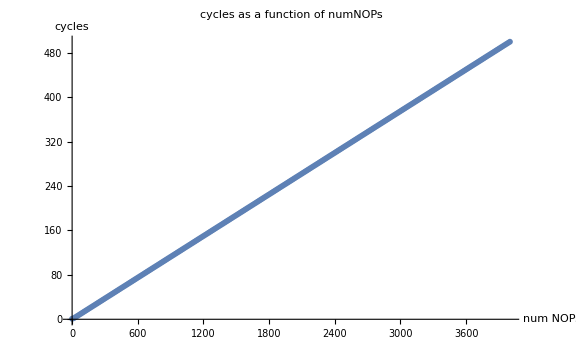

```mathematica
nops4000=;
ListPlot[nops4000, ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs"]
```

Now add a delay block of 8 chained FSQRT.D, each 13 cycles long.

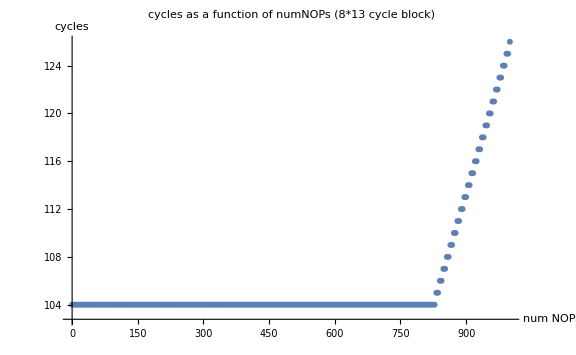

```mathematica
nops1000=;
sqrt8=;
ListPlot[sqrt8,  ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs (8*13 cycle block)"]
```

Nothing too difficult to understand here; for fewer than (8*13*8=832 NOPs) the loop time is defined by the FSQRTs, for more than 832 NOPs the loop time is defined by the NOPs.

Delay block timing (blue) vs non-delayed timing (gold)

```mathematica
ListPlot[{sqrt8, nops1000},  ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs (8*13 cycle block)",
PlotLabels->{"FSQRT8 delay", "no delay"}, 
PlotRange->{0, 126}]
```

-Graphics-

We can force the FSQRTs to delay for a lot longer by chaining 32 of them together. Now we see something interesting, a glitch in the graph!

Delay block timing (blue) vs non-delayed timing (gold), with delay block and number of operations large enough to force a glitch.

```mathematica
sqrt32=;
ListPlot[{sqrt32, nops4000},  ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs (32*13 cycle block)", 
PlotLabels->{"FSQRT32 delay", "no delay"}, 
PlotRange->{0, 644}]
```

-Graphics-

What happens if we try to shrink the delay to the bare minimum?

Delay block timing (blue) vs non-delayed timing (gold), with delay block and number of operations optimized for visible (but minimal) glitch.

```mathematica
sqrt22=;
ListPlot[{sqrt22, nops4000},  ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs (22*13 cycle block)", 
PlotLabels->{"FSQRT22 delay", "no delay"}, 
PlotRange->{0, 513}]
```

-Graphics-

And zooming in

```mathematica
p1=ListPlot[{sqrt22, nops4000},  ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs (22*13 cycle block)", 
PlotLabels->{"FSQRT22 delay", "no delay"}, 
PlotRange->{{2000, 4000}, {286, 513}}]
p2=ListPlot[{sqrt22, {0, 13}+#&/@nops4000},  ImageSize->Large, 
AxesLabel->{"num NOPs", "cycles"},
PlotLabel->"cycles as a function of numNOPs (22*13 cycle block)", 
PlotLabels->{"FSQRT22 delay", "no delay"}, 
PlotRange->{{2000, 4000}, {286, 513}}]
```

-Graphics-

-Graphics-

There are clearly two interesting numbers. 
- At 4000 NOPs, the time taken is 500+13. ie one fsqrt was delayed each iteration.
- The delays starts at 2228 cycles.
How do we explain these facts?

In the case of NOP, the only resource that can possibly be relevant is the ROB. In other words, as a rough approximation, what’s happening is: 
- the fsqrt’s block the ROB for long enough that around ~2200 NOPs can pile up in the ROB, unable to retire because the fsqrts are still going. 
- at that point the next fsqrt (placed by looping around back to the start of the loop, is not able to even enter the machine because one of the requirements to pass Decode to the next stages is a ROB slot. 
- so that fsqrt is delayed, and our timing switches from MIN(22*13, N/8) to something like MIN(21*13, N/8+13).

That gives the intuition (and approximates the numbers) but is off by a few cycles because it does not include the overhead of the fsqrts themselves. Can we do a little better?
We will assume that any type of operation can be decoded at 8/cycle and placed into the ROB at 8/cycle. 
This assumption may need to be revised, but let’s assume that for now. 
At t=-1 the ROB holds nothing. 
At t=0 the ROB holds 8 successive fsqrts.
At t=2 the ROB hold 22 successive fsqrts and 2 NOPs.
At t=13 the ROB holds 21 successive fsqrts and 2+ (13-2)*8 NOPs
until we loop to the second iteration:
At t=T the ROB holds (22-T/13) fsqrts and 2+(T-2)*8 NOPs

For T=21*13=274, the number of enqueued NOPs will be 2178
For T=22*13=286, the number of enqueued NOPs will be 2274
We see trouble at 2228 between these two, so our ROB size is somewhere between these two. 
Essentially at T=~280, we reach a situation where 
- 21 fsqrts have been processed
- the last fsqrt is still executing, with a few cycles to go (22*13-280=6)
- The ROB holds 1 fsqrt, ~2270 NOPs, and perhaps two  instructions from the branch test+loopback
BUT it can no longer accept the first fsqrt from the next loop iteration. So we get a stutter at this point, a delay in the smooth flow by 6 cycles before that fsqrt exits head of the ROB, and Decode is no longer stalled. 

Once one has a more accurate idea of the machine, one can attempt to perform precise measurements. But this entire document will be about trying to understand the overall machine, thus we’ll be satisfied with approximate numbers, leaving precision for later workers.

So we’ve established a few initial facts here: 
- The ROB is ~2274 instructions in size. Over time we’ll see that I believe it’s best treated as ~324 rows, each 7 slots in size, giving a total of 324*7=2268 entries. 
These “rows” are the units of Retire.

Retire (and the ROB) have to handle the following tasks
- deallocate resources (physical registers, load/store slots, ...) as instructions are completed BUT
- maintain machine integrity in the face of misspeculation (eg branch prediction). 
This means that temporary state (in physical registers) can only be deallocated once it is certain there’s no possibility that unwinding speculation may require the use of that state. 

This leads to a delicate balancing act where one has to hold onto resources as long as necessary (for correctness) but wants to relinquish them (for reuse) at the absolute earliest moment that that is possible. Much of Apple’s somewhat unusual ROB machinery is an attempt to be more aggressive in this reuse goal.

## More Experimentation Theory

The ROB+NOP analysis gives some of the flavor of the enterprise going forward. The usual pattern is 
- a delay block
- running in parallel with other operations
To void confusion, let's consider the delay block (which can be of variable length) to take duration D, and the Ops block to be comprised of N Ops that would be expected, under ideal circumstances, to take duration O.

(a) Once the "other operations" take longer than the delay block we get a diagram like diagram 1 above.
The diagram to keep in mind is
| Delay<---------D----------------------->|| Delay<---------------------------------->| 
|Ops<------------O--->|                               |Ops<---------------->|                                |
transitioning to 
| Delay<---------D----------------------->|           | Delay<---------------------------------->|
|Ops<-----------O------------------------------->||Ops<-------------------------------------------->|

(b) But once we make the ops block long enough, lack of some resource will stall the earlier stages of the machine (Decode, Map, Rename)and prevents all the operations from executing right away because all resources are locked up until the head of the ROB (the Delay block, retires .and so the Ops block encounters an additional delay, a delay caused by its inability to fully execute ). This gives us a diagram like 2. with a notable glitch. 
| Delay<---------------------------------->|                        | Delay<---------------------------------->|
|Ops<---------------------------xxxxxxxx-------------->||Ops<---------------------------xxxxxxxx-------------->|
In other words once the resource count used by Ops is exceeded, then the delay O_measured(N ops) is larger than O_expected(N ops) by the delay xxxxxxxx that occurred while the Ops were sitting idle, unable to proceed through the machine until the head of the ROB retired (at the end of the delay block) and resources were freed. 

Note that for this condition to occur (presence of the xxxx) we require 
- D must be large enough to block N ops partway through their execution
- N must be large enough that all resources are fully consumed.
However once we see a glitch, it's sometimes desirable to try to shrink D and N down to about the minimum values that will reproduce the phenomenon, the glitch in timing, as in diagram 3.
Other times it makes sense to push D rather larger than the minimum because you'll then catch an additional unexpected event!

In this case the number of interest was the minimal number of ops that had to be enqueued to generate a glitch. As our analyses become more sophisticated, we will be considering other features of these sort of graphs. For example the slope of the NOPs line tells us how many NOPs/cycle can be processed by the machine. We may structure things so that, after a glitch, the slope of the post-glitch line tells us something about how rapidly resources are freed (as opposed to what we have learned so far, namely how many resources can be used up).

## Register Files

## More OoO Theory

Remember why we distinguish between logical and physical registers: https://en.wikipedia.org/wiki/Register_renaming.
We use physical registers (the logical physical register perhaps mapped to different physical registers as execution proceeds) for two reasons
- to avoid having to pause execution because of false dependencies
- to maintain state in a temporary form for speculative execution. If we want to be able to execute further down a speculative path, we need to be able to hold more temporary state, ie more physical registers

Most machines distinguish three classes of registers: int, FP/SIMD, and flags; and all three are renamed and live in separate physical register files. 

So consider a stream of instruction that each generate an integer result. Every such result requires a destination register which will be a newly allocated physical register. If the pool of such physical registers runs out, integer instructions cannot proceed until more physical registers become available. In fact no instructions can proceed, because register allocation occurs in the front end of the machine, where instruction flow is still in-order.

The flow of instructions is essentially 
Fetch
Decode, 
Map (mainly figure out the dependencies between the current group of eight newly decoded instructions)
Rename (allocate resources required by each instruction, eg a destination register
Dispatch

Schedule
Execute

Retire
Complete
Writeback

The initial set of stages all occur in-order – meaning that any block in one of those stages blocks all subsequent instructions. 
Schedule and Execute occur out of order (which is where the performance win is!) The win has two sources: 

- some instructions  will be delayed by random events the compiler can't predict, like loads that miss in cache. Other, independent instructions can occur while those instruction wait for whatever is they're waiting for.

- instructions tend to cluster as sequentially dependent instructions (C depends on B depends on A), but these dependency chains are usually surprisingly short (about 10 to 20 instructions) before they are terminated (usually by storing the result to memory), after which an independent chain starts. Thus if we can queue enough of these independent dependency chains in the machine, we can run many of them in parallel. 

In theory the compiler could do this for us on an in-order machine. In practice this fails because
(a) most languages don't provide enough information about the non-overlapping of storage for compilers to be able to disambiguate that the store from the last dependency chain doesn't overlap with the loads that starts the next dependency chain
(b) most of these dependency chains are separated by branches of some sort, and the compiler can't be sure which way the branches will go
(c) trying to optimally schedule hundreds of instructions in a compiler is a combinatorial explosion problem, one that takes a lot of time, usually too much to be practical.

Retire, Complete, and Writeback tend to be bundled together in modern cores, and (mostly) happen in order. 
Retire is easy to understand. It's the final point at which instructions have done (almost) everything they are supposed to do, and are no longer speculative. Their resources can be released, and reused by new instructions.
Writeback used to mean that results that were held in physical registers were written back to "architected registers". This is a term you will see if you read really old papers (say pre-2000 or so.) The evolution of out of order technology went essentially something like 

(0) an in-order machine, with let's say 32 architected integer registers x0..x31 has a register file of these 32 registers. Every instruction affects its destination architected register.

(1) very early out-of-order has each ROB entry providing a slot that acts as the destination register of each instruction. So Register allocation happened automatically as allocation of the ROB slot. Writeback meant copying from that ROB slot register to the architected register file. 
This is clearly built on the in-order model, with the idea that when anything fails, you fall back to the architected register file as the true state. But it means the number of physical registers equals the number of ROB entries -- and what to do about FP/SIMD vs int registers? And you waste a register slot for instructions (like branches) that don’t use a register. And all that writeback copying uses power.

(2) the physical register file was detached from the ROB. This solves the FP/SIMD vs int problem, and allows each of int register file, fp register file, and ROB to be independently optimally sized. But you're still paying writeback costs

(3) various alternatives were adopted for how to recover from misprediction using maps that describe how physical registers map to logical registers. Done correctly, this avoids the need to have a separate architected register file along with writeback; the state of the machine exists only in the physical register file together with the map between the physical and architected registers.
I refer frequently  to the paper (2004) http://pages.cs.wisc.edu/~rajwar/papers/taco04.pdf An Analysis of a Resource Efficient Checkpoint Architecture by Haithim Akkary. This was written just at the point of this transition, so it describes multiple options for how this can recovery be performed. 

(4) the usual state of the art for industry today is much (not all) of what Akkary is proposing in that paper. 
Apple is the only company I know of that's using the next step in the evolution which is to use a History File to record the changes made to the mapping tables as execution proceeds. This change decouples the ROB itself (a queue of instructions) from the History File (a record of changes to register mappings). This is as opposed to recording these mapping changes as part of the ROB. 
The first advantage of this is that once more the two can be separately sized, rather than tying the number of instructions in the ROB to the number of changes made to registers. 
The second is that the two are deallocated separately at Retire – the ROB can free up to 56 instruction in a single cycle; the History File, operating independently and with a more difficult task, can free up to 16 registers in a single cycle. 

(5) The next step beyond 4 would be the use of Virtual Registers (to be discussed below). Apple doesn't do this yet, but probably will soon.

Finally the Complete stage is mostly meaningless (by the time an instruction is considered eligible to Retire it has executed and so completed its job)… except for the case of stores. 
In the old days, at the the point of Retiring a store, the store would be copied from the Store Queue to the L1D cache. (This could involved pulling in a line that was the target for the store.) And it was only when that line had been returned from L2 or DRAM, and had the store written to it, that the store could be considered Complete.)
Nowadays, for a store:
- Execution consists of calculating the store address, and placing the store address and store data in a store queue. 
 - At a later point (when the store is non-speculative) the store will move from the store queue to a write buffer (sitting between the store queue and the L1D cache) at which point the entry in the store queue can be released. 
 - But the store is still, (in some sense) not complete! At some random later point the store will move from this write buffer into the L1D. And at some random even later point, it will be made visible to other cores. 
 It's something of a question of exactly what you're trying to achieve as to when you define a store as Completing, so once again this has become a somewhat obsolete stage. 

 Essentially Retire now means Deallocate (resources) in the same way that Rename means Allocate (resources).

Here’s another way to think about this, as described in (2009) https://www.disca.upv.es/spetit/publications/ieeetoc.pdf A Complexity-Effective Out-of-Order
Retirement Microarchitecture. 
The basic OoO CPU allocates, at the last stage of in order execution (ie at Rename) various resources that will be required by later execution, including LSQ entries, registers, and ROB slots. And it releases those, again in-order, by waiting until whatever instruction is at the head of the ROB has completed, and then running forward along the ROB as rapidly as possible, releasing resources until it hits another blocking instruction. The most common reason to block the head of the ROB waiting for an instruction to complete is waiting for a load that missed to DRAM, though we may wait a few cycles for shorter instructions like say a divide.
This basic design makes it very easy to recover from either misspeculation or exceptions. In either case we simply have to execute up until the problematic instruction (eg the load that generated an MMU exception, or the branch that was mispredicted) is at the head of the ROB, and then restart the machine. This works because Retire/Deallocate/Commit happens in order and won’t allow anything to be stored to permanent machine state until we know  that each instruction being committed should in fact have executed. 

But this also ties together various different ideas (maintaining valid machine state vs deallocating resources that are no longer needed) and a pattern we’ve already seen repeatedly and will see more is you speed things up by breaking up a task that is done adequately by one structure into two tasks both done  better by optimized structures. 
In this case the big problem is that resources (eg LSQ entries and registers) are being held long after they were needed for execution, simply because deallocation only happens at this in-order final step. So, for example, if the ROB is blocked by a load to DRAM, then we will execute as much as we can but eventually we will run out of something (usually registers) and the machine will freeze until the load returns from DRAM. Can we avoid that? We know that nothing unexpected can happen in terms of the load ( MMU exception tests have been cleared, LSQ overlap with a possible store has been cleared) so why do all the later instructions need to wait for this load before they release registers for reuse? 

Thinking this way gives you various possibilities for OoO Commit. Like everything, people have imagined various versions of this, and as a very new concept (quite possibly not yet implemented by anyone) there is not yet any consensus on the best way to do things. But the paper I reference tackles one of the less obvious aspects of the problem:
The nice thing about the ROB is that it’s a large, but in-order structure, so it’s not very area or power expensive, it maintains the program order you want “for free”. Suppose we are blocked at the head by a load, but the following few instructions have nothing to do with that load and are just some simple arithmetic. If we commit them out of order to release some registers, how can we keep using the ROB as an in-order instrument (and we do need that order for cases where the head of the ROB is speculative, or generated an exception, and we need to flush everything after the head). Simply removing random elements from this in-order queue and moving everything else up is energy expensive. But leaving holes means a godawful mess in terms of tracking which instruction follows what. 
The idea of the paper is to replace the ROB (handles Validation and Deallocation) with a shorter queue that only handles Validation. Instructions are placed into the Validation Buffer (VB) in order at, eg Decode time, just like the ROB, and move through the VB in order, just like the ROB. But they only remain in the VB as long as the head of the VB has the potential to fail. So, for example, now if a load to DRAM is at the head of the VB, it only remains at the head until we know that there’s no possible exception or no possible load/store address aliasing. Likewise branches can exit the VB once they are resolved. A third sort of instruction is something like a divide, where (ideally) we establish in the first cycle of execution that division by zero is or is not possible (ie possible exception) and once that’s settled, a non-exceptioning divide can also leave the VB.
The end result is that most instruction situations that would block the ROB, and eventually cause the machine to lock up, can in fact pass through the VB in a few cycles, without the VB ever filling up. Later those instructions can, out of order, release their resources as appropriate. For example, once again, the long-lived load to DRAM will have to hold onto its destination register for many cycles, until the data is returned from DRAM (and then even longer, as subsequent instructions wish to use that register). Presumably this “release of resources” will be something like decrementing the reference count for the source and destination registers of this load instruction. 
But unrelated instructions after the load can now release their registers out of order, with a net effect that the pool of available registers is effectively (averaged across many programs, and very dependent on other machine details) effectively about 30% or so larger. Likewise the LSQ is effectively about 10% larger due to LSQ entries being released earlier. 

This scheme is, like all schemes, not perfect. Consider, for example, the bete noire of the modern OoO CPU: a load that misses to DRAM followed by a branch that depends on the loaded data. This will allow the load to rapidly graduate out of the VB but the branch will now sit at the head of the VB, blocking progress until the load returns. But this is still better than the ROB case. The ROB prevented progress for every load that missed to DRAM, the VB only prevents progress in this (somewhat more rare) situation of a load followed by a branch.  
If we are willing to be more ambitious, and allocate more resources, we can even handle this sort of situation somewhat. When we realize this case has occurred, we can generate a checkpoint, a snapshot of the machine state just before the branch, and then let the branch graduate and keep executing past it. If the branch did turn out to be invalid (should not have been graduated past the head of the VB) we can restore state from the checkpoint. 
This scheme, while feasible, is of limited benefit beyond pausing when the VB fills up and we wait for the branch to be resolved; the reason is that a checkpoint can restore register state, so it can allow us to recover from registers that were reused as we executed the speculative (and ultimately incorrect) code. But a checkpoint cannot store memory state. So what do we do about stores that are also speculative? We can’t graduate these from the VB, and so now LSQ slots will be the resource that ultimately fills up. (But what if we graduated stores that are “safe” in every respect except that they are branch speculative to a different type of structure that is more like an L0 cache and less like the LSQ...?)
The most extreme version of these ideas shade into things like transactional memory, where you now have “speculative” bits associated with data in the L1 cache, and you allow some speculative transactions to proceed all the way to the cache, with the “speculation boundary” now being that these speculatively written values in cache are not allowed to leave the cache (not to service snoops, not to write to DRAM or DMA or anywhere else) until the speculation episode is over and we go through to clear all the speculative data bits. Both Intel and IBM (in POWER8 and 9) have tried transactional memory and given it up as being too complicated to be worth the payoff (though I don’t believe either fully exploited it as I’ve described here, they used it only for lock elision and transactions, not to increase how aggressively an OoO CPU can speculate). IBM still has transaction memory in the z/ Series so at least one team still has faith in the idea. ARM has the TME (Transactional Memory Extensions) instructions defined but so far no-one on Team ARM seems brave enough to try where Intel and IBM POWER have failed. 

So, bottom line is that 
- you can replace the ROB with a VB, at not too much design disruption, and the payoff is effectively a 30% or so larger register file and 10% or so larger LSQ, for no extra area or power. Very nice. 
- if you want to be much more aggressive you also speculate your way past in-order validation of things like branches, but the cost to do so is a radically redesigned L1 cache and interaction with the rest of the SoC (cache can’t release any speculated writes to cache, which affects snooping, DMA, etc). 
Let’s get step one, transitioning from ROB to a VB, implemented and optimized, before we start worrying about these crazier ideas!

Back to our stream of integer instructions, and to experiments. 
Each of these allocates a physical register in Rename. That register can be freed once the instruction Retires (but not earlier). Which means that if the integer instructions are blocked by a delay block at the head of the ROB, eventually all physical registers will be allocated, the machine will stall, our timing will see a glitch. Let’s try it!
Remember as we perform these experiments below, all the details I gave above (eg Apple’s use of a history file decoupled from the size of both the ROB and the physical register files) was not told to us by Apple! It’s all the result of experiment, and that’s what this long run of experiments below is designed to figure out.

## Integer Physical Register File Size (ADDs)

Before going further let’s validate our foundational ideas about the physical register file. 
We start with the simplest model, then see if it breaks as we add tweaks.
Start with a run of instructions (ADD x0, x5, x5) that each require a physical register to hold the generated result.

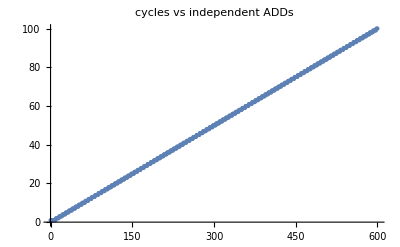

```mathematica
addIndependent600=;
ListPlot[addIndependent600, 
PlotLabel->"cycles vs independent ADDs"]
```

No surprises, the primary notable fact is the slope (6 independent integer adds/cycle).
Now let’s add in a delay.

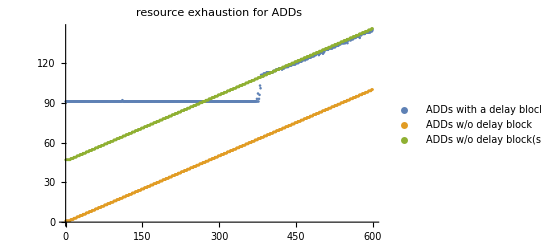

```mathematica
sqrt7ιaddIndependent600=;
ListPlot[{sqrt7ιaddIndependent600, addIndependent600, #+{0, 111-65}&/@addIndependent600},
PlotLabel->"resource exhaustion for ADDs",
PlotLegends->{"ADDs with a delay block", "ADDs w/o delay block", "ADDs w/o delay block(shifted upward)"}]
```

```mathematica
(* {377,91},{378,93},{379,96},{380,103},{381,101},{382,111} *)
```

Here are the notable points:
- Clearly at ~378 ADDs, there is a notable jump in the cycle time.
- The slope of the delayed ADDs is unchanged, just shifted up by 46 cycles. 
- So at ~378(=63*6) physical registers, at 63+2 cycles in, ADD progress stops, ie at INT_STOP_TIME=(num phys reg/6 + 2 [two cycles for branch and enqueing the sqrts])

For how long? Until the ROB clears, so 
WAIT-TIME=DELAY TIME (13*numSqrt) - INT_STOP_TIME.

I *think* the transition occurs over ~5 cycles because of  8-wide Rename.

| Delay<---------------------------------->|                        | Delay<---------------------------------->|
|Ops<---------------------------xxxxxxxx-------------->||Ops<---------------------------xxxxxxxx-------------->|

Let's assume there's a few cycles of jitter in xxxx (just assume that for now). And that the actual physical register count is say 380.
This would mean that for N very near the resource limit (say 379 or 380) those N's will occasionally hit the resource limit (and execute the slow path, where xxx force a delay and everyone has to wait for ROB to clear) and will occasionally not hit (meaning the fast path, no XXX delay, no requirement for the next block of fsqrts to delay till the ROB clears before they can begin execution). 
If such a jitter existed then we'd see something like maybe 1/6 of the time the 378 case is slow, 5/6 of the time it is fast, and the average cycle count is 5/6 to 1/6 weighted. Likewise the 379 case is 2:6 to 4:6 weighted and so on, and we'd get the sort of staircase we see. Depending on exactly how we aligned all the instructions, and the source of jitter, we might be able to get a perfect jitter free-case, to a perfect linear ramp. 
I assume the jitter reflects differential widths in different parts of the machine (eg Decode can generate 8 instructions per cycle, but integer execution can use up only 6 per cycle) meaning that slightly different numbers of instructions could be enqueued (and blocking the transit of fsqrt from the in-order path to the OoO path) in different places on different loop iterations. But trying to pin that down further using this particular harness seems inefficient.
Going forward we should GENERALLY expect a slightly noisy transition region (over 6? 8?) cycles because of our jitter explanation, and not waste time obsessing over its existence.

So what is definitely established is that 
• there's some sort of limitation at around 380 ADDs (seems like physical registers)
• assuming the above point, we've also learned that registers are deallocated at Retire (deallocation is delayed by the Head of ROB blocking) rather than some more ambitious schemes that de-allocate a register when all users of that register have completed. We’ll discuss this later.

It’s important to have a correct understanding of the analysis, which is somewhat more abstract (less mechanistic) than Henry Wong’s method. In particular it’s very tempting to view the x-axis (the N axis, where N is the number of filler instructions between delay block) as representing time, and doing that will drive you crazy!

To be sure you understand, consider the graph below.

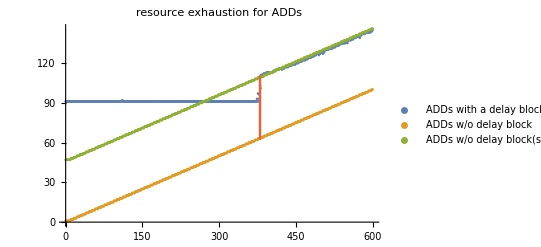

```mathematica
ListPlot[{sqrt7ιaddIndependent600, addIndependent600, #+{0, 111-65}&/@addIndependent600, {380, #}&/@Range[63, 110]},
PlotLabel->"resource exhaustion for ADDs",
PlotLegends->{"ADDs with a delay block", "ADDs w/o delay block", "ADDs w/o delay block(shifted upward)"}]
```

Essentially we have two independent blocks (call them chains) of sequential execution. 
The first chain is the delay block, the block of 5 (or 10, or 20) chained FSQRTs. The amount of time this block would take to execute is independent of the number of filler instructions (ADDs), and can be viewed as the flat part of the blue curve, extended to arbitrarily high values of N.
The second chain is the ADDs. For small N, they take an amount of time linear in N, following the left hand side of the gold curve. For large enough N the execution of the ADDs is forced to block (the xxx time) while we wait for a resource to be freed. 
Thus for N<~380 the time taken by the ADDs follows the gold line, 
for N>~380 it follows the green line, 
with the two lines linked by a jump occurring at N=~380. 

SO: Loops with filler of less than ~380 execute on the fast path; loops with filler of more than ~380 execute on the slow path. 
The curves show what happens for loops with differently sized filler, they do not show what happens in time as successive ADDs of the filler are executed!

The whole blue curve (the one we measure) is the time taken to execute (in parallel) the filler block (following the curve gold/red/green) and the delay block (always taking a constant 7*13=84 cycles). The time for a loop iteration is always the larger of these two possibilities.

To get a clean curve, it’s ideal (though sometimes not possible) to have the delay block last substantially longer than the filler block takes to reach resource exhaustion. 
Observe what happens when we don’t do that.

```mathematica
sqrt8ιaddIndependent600=;
sqrt6ιaddIndependent600=;
sqrt5ιaddIndependent600=;
sqrt4ιaddIndependent600=;
sqrtS4ιaddIndependent600=;
delay45ιadd=;
delay46ιadd=;
ListPlot[{sqrt4ιaddIndependent600, sqrt5ιaddIndependent600, (*sqrt6ιaddIndependent600,*)sqrt7ιaddIndependent600, sqrt8ιaddIndependent600, addIndependent600},
PlotLabel->"cycles for N independent ADDs, given a variable length delay block",
 PlotLabels->{4, 5, 7, 8, 0}, 
ImageSize->Large]
```

-Graphics-

We point out these salient facts. Note that 5*13 takes 65 cycles, which is time to perform 390 adds, so a delay of 5 is right on the cusp, able to show the phenomenon but not a clean jump. 
• For a delay that is too short (4 FSQRT) we clearly don’t cleanly hit the phenomenon of interest (ie ADDs delayed because of inability to allocate a resource, blocked behind the head of ROB). 
• For a delay that is just on the money, (5 FSQRT) the crossover region (the jump at ~380 ADDs) is not smoothly isolated and it’s easy to get distracted in the hopeless task of trying to figure out the exact structure of the crossover region.

#### an aside for experts

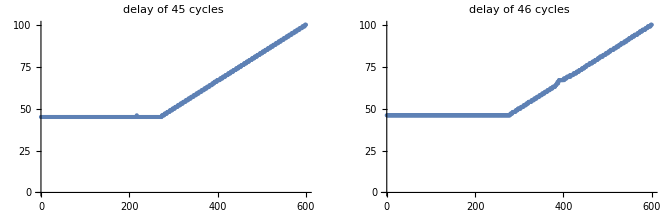

```mathematica
p1=ListPlot[delay45ιadd, PlotLabel->"delay of 45 cycles"];
p2=ListPlot[delay46ιadd, PlotLabel->"delay of 46 cycles"];
GraphicsRow[{p1,p2 }, ImageSize->670 ]
```

It’s interesting to consider why we still get a (small) bump for the case of  delay of 4*13 (52) cycles. 
The first parts of the curve, up to N=~380 are clear. What’s unclear is why there should be some delay for, say, a filler of 390 ADDs. 
After about 312 ADDs are executed, the head of ROB clears, the physical registers used by the first few ADDs behind the head of ROB will start to be released (in fact at a rate of 16/cycle as we will see) and there is no obvious reason for the ADD chain ever to be blocked or delayed, no reason for any xxx time. 

This understanding is (kinda sorta) confirmed by comparing a delay
 of 45 cycles (4 FSQRT s1, s1, s1 FADD s1, s1 FABS s1, s1) 
with 46 cycles (4 FSQRT s1, s1, s1 FADD s1, s1 FADD s1, s1).
45 cycles behaves as expected, 46 cycles shows a slight but definite bump at N=~380.

I believe this effect is a consequence of a low-level implementation detail in Apple’s register file. I’ll explain this below, in power aspects of the register file, once we have explained higher level aspects of the register file.

## FP Physical Register File Size (FABS)

Let’s try the same strategy for fp registers. The code is as before except we replace the ADD with FABS d2, d0

```mathematica
fabsIndependent600=;
sqrt13ιfabsIndependent600=;
ListPlot[{sqrt13ιfabsIndependent600, fabsIndependent600},
PlotLabel->"cycles vs independent FABS",
PlotLabels->{"FABS with a delay block", "FABS w/o a delay block"}, 
ImageSize->Large]
```

-Graphics-

```mathematica
(* {403,130},{404,131},{405,131},{406,132},{407,132},{408,132},{409,132},{410,133},{411,134},{412,134},{413,135},
{414,135},{415,136},{416,138},{417,135},{418,137},{419,137},{420,140},{421,143},{422,149},{423,146},{424,147},{425,150} *)
```

So we see the structure we expect by now. The slope of both lines is 4 independent fp instructions/cycle, as expected. 
The jump happens over the range 403..425, so over a range of about 25 instructions, centered at about 415 instructions. 
The jitter range is a little messier than before, I assume at least in part because the delay block and the FABS are sharing registers and execution paths.

We can use an integer delay block (chained UDIV, 7 cycles/iteration) to get a slightly cleaner result

```mathematica
udiv20ιfabs600=;
ListPlot[{sqrt13ιfabsIndependent600, udiv20ιfabs600},
PlotLabel->"cycles vs independent FABS",
PlotLabels->{"FABS with a SQRT delay block", "FABS with a UDIV delay block"},
ImageSize->Large]
```

-Graphics-

```mathematica
(* {428,140},{429,141},{430,140},{431,145},{432,142},{433,148},{434,156},{435,156} *)
```

We see a narrower transition region, and without the delay block using up some of the fp registers, we see that the fp register file is perhaps closer to 432 or so in size.

## Register File Size (All Registers)

The apparent number of physical registers for int and fp are fairly similar. 
One can entertain a number of possibilities (is there a common register pool?), so lets examine what happens when we try to allocate both integer and fp registers. Let’s try a probe consisting of an ADD and a FABS.

```mathematica
fabsπaddIndependent600=;
sqrt9ιfabsπaddIndependent600=;
sqrt9ιaddIndependent600=;
sqrt9ιfabsIndependent600=;
ListPlot[{sqrt9ιfabsπaddIndependent600,sqrt9ιfabsIndependent600, sqrt9ιaddIndependent600, fabsπaddIndependent600},
PlotLabel->"cycles for N independent ADDs+FABSs",
PlotLabels->{"FABS+ADD", "FABS", "ADD", "FABS+ADD w/ no delay block"},
ImageSize->Large]
```

-Graphics-

```mathematica
(* {308,117},{309,119},{310,123},{311,124},{312,128},{313,130},{314,132},{315,132} *)
```

Now this is interesting! 
The red curve omits the delay block, and shows a slope of 4 ops/cycle. We are throttled by the 4 fp pipes.
The green curve and the gold curve are, respectively, the pure integer test and the pure fp test.
The blue curve is the case of interest, with a probe of (ADD+FABS).

We see clearly a standard jump, centered at about 312 or so. How can we interpret this? 
Clearly the idea that registers are shared between int and fp fails. If that model held, we’d jump at something like 192 (half the ~384 registers allocated to fp, half to int, stall). 
But something clearly is shared! There’s an additional resource  that constrains us, a pool of ~624 somethings that’s shared by int and fp registers.

We can continue our investigation by testing the third available pool of registers, the physical flags register. 
Let’s start by testing CMP x0, x0

```mathematica
cmp600=;
sqrt9ιcmp600=;
ListPlot[{sqrt9ιcmp600, cmp600},
PlotLabel->"cycles for N CMPs",
PlotLabels->{"CMP with delay block", "CMP w/o delay block"}, ImageSize->Large]
```

-Graphics-

```mathematica
(* {121,117},{122,122},{123,122},{124,125},{125,119},{126,134},{127,131},{128,136} *)
```

So no real surprises. This time the slope of the lines is 3 instructions per cycle;.
However the jump is at ~124 (128?) physical flags registers. So not the same number as int or fp...

Now for the exciting part, run all three together! First let's investigate the simple case, with no delay block.

```mathematica
fabsπaddπcmpIndependent600=;
ListPlot[{fabsπaddπcmpIndependent600, cmp600},
PlotLabel->"cycles vs N CMP and N FABS+ADD+CMP",
PlotLabels->{"FABS+ABS+CMP", "CMP"}, ImageSize->Large]
```

-Graphics-

Now our rate drops to 600 triplets in 225 cycles, 8/3=2.667 instructions/cycle. 
The limiting point is the 8-wide front end (Decode, Map) of the machine. We have a total of 3*600 instruction, processed 8 /cycle, which takes 1800/8=225 cycles.

Now add the delay block.

```mathematica
sqrt9ιfabsπaddπcmpIndependent600=;
ListPlot[{sqrt9ιfabsπaddπcmpIndependent600, fabsπaddπcmpIndependent600},
PlotLabel->"cycles vs delayed N FABS+ADD+CMP",
PlotLabels->{"FABS+ABS+CMP with delay", "FABS+ABS+CMP w/o delay"}, ImageSize->Large]
```

-Graphics-

```mathematica
(* {127,117},{128,123},{129,128},{130,136},{131,138},{132,138},{133,138},{134,139},{135,139},{136,140} *)
```

We see that we’re constrained by the number of compares; we can’t get beyond that to test the region of interest. If there is a common pool of 624 somethings, cut 1/3 each way gives 208. Not reachable via a unit of (CMP+ADD+FABS).
What about 624/5=124.5? Right on the cusp! So let’s try one CMP paired with two ADD and two FABS. We’ll implement this as only allocating the CMP for every second (ADD/FABS) pair, so the unit is (ADD+FABS+.5 CMP).

```mathematica
fabs2πadd2πcmp600=;
sqrt9ιfabs2πadd2πcmp600=;
ListPlot[{sqrt9ιfabs2πadd2πcmp600, fabs2πadd2πcmp600},
PlotLabel->"cycles vs delayed (FABS+ADD +1/2CMP)",
PlotLabels->{"FABS+ADD +1/2CMP with delay", "FABS+ADD +1/2CMP w/o delay"}, ImageSize->Large]
```

-Graphics-

```mathematica
(* {245,117},{246,121},{247,124},{248,130},{249,132},{250,131},{251,135},
{252,137},{253,137},{254,137},{255,136},{256,139},{257,139},{258,140}*)
```

Almost! But not quite?
The jump is at ~250. Is this what we expect? 
250 units corresponds to 250*(ADD+FABS+ half a CMP), so we’re possibly still being limited by the ~128 flags physical registers before we can get to the good stuff, since half of 250 would be 125. 
But 250*2.5=625. It’s plausible that we’re seeing a signal. But let’s confirm. 
Drop to a third of CMP.

```mathematica
fabs3πadd3πcmp600=;
sqrt9ιfabs3πadd3πcmp600=;
ListPlot[{sqrt9ιfabs3πadd3πcmp600, fabs3πadd3πcmp600},
PlotLabel->"cycles vs delayed (FABS+ADD +1/3CMP)",
PlotLabels->{"FABS+ADD +1/3CMP with delay", "FABS+ADD +1/3CMP w/o delay"}, ImageSize->Large]
```

-Graphics-

```mathematica
(* {264,117},{265,119},{266,120},{267,125},{268,130} *)
```

OK, finally, the signal we’re looking for. 
The fundamental unit of allocation is  (ADD+FABS+1/3CMP) (implemented as  adding a CMP for every third ADD+FABS). 
We execute 266 of  this unit) so 266*(2+1/3) =620 register allocations! And this time all three register pools (int, fp, even flags) are only partially exhausted, with 266 int registers, 266 fp registers, and 87 flags registers being used up at the point of the jump. 

So there is some communal structure related to the allocation of registers, of size ~620 entries, which is used up in addition to the register files.

## The History File (ROB structure tracking all changes to Register Mapping tables)

What are these unknown shared ~620 resources? 
I made many different hypotheses, and experimented with many different things, but the real answer appears to be in this patent: (2019) https://patents.google.com/patent/US20210064376A1/ Last physical register reference scheme.

One way in which Apple optimizes the Retire tension I discussed is through a structure called a History File.
Conceptually the history file sits next to the ROB, and while the ROB holds a sequence of instructions (all instructions, in-order), the smaller HF holds the sequence of changes that were made to the three (int, fp, and flags) register mapping tables. 
The HF has ~620 entries, and requires an entry for every instruction that will modify the mapping tables (so basically any instruction with a destination register, including a flags destination). The HF also includes a single bit flag that this is the last mapping referencing the physical register referenced by the mapping. 

To understand this aspect of the ROB, perhaps start by reading (2001) https://courses.cs.washington.edu/courses/cse378/10au/lectures/Pentium4Arch.pdf The Microarchitecture of the Pentium 4 Processor which describes the P6 and then the P4 schemes. 

The P6 scheme was very simple (as these things go). The ROB and the PRF were the same structure; allocation of a ROB entry was the same thing as allocation of a destination register. Speculation was handled by having a separate PRF, named the RRF (Retirement Register File), that represented the “true state of the machine as of Retire” so that you could recover just by pointing all the Map tables to the RRF. 
Problems with this scheme include 
- that your ROB and PRF are linked in size, though really you want the ROB to be some scaling factor larger than the PRF; and 
- the copying of a GPR to the RRF on every retire costs additional energy. 

The P4 scheme has separate (and separately sized) ROB and PRF, and a separate Retirement RAT (Retirement Mapping Table) that’s updated at retire. 
This is progress! We have 
- separate sizing of ROB and PRF; and 
- the energy cost of updating an entry in the Retirement RAT is less than that for copying a register to the RRF. 
It’s hard to see what the problems with this scheme are, until you start being more ambitious.

Suppose we have a situation where there are many instructions in the ROB, and halfway down the ROB there's a branch that we know is mispredicted because we just executed the branch and learned that. So we need to engage in branch mispredict recovery.

The P4 recovery scheme is to mark in the ROB entry for the branch that it was mispredicted, and continue as usual until the branch retires. At that point 
- the instructions before the branch have all retired (they were ahead of the branch so were valid); 
- as they retired they updated the RRAT (so RRAT represents an accurate register mapping table at the point of the failed branch); 
- and so handling the misprediction mainly means copying the RRAT into the frontend Mapping table. 

But this also means that all that time from when we learned the branch was midpredicted until it retires is dead time! The machine kept chugging away at instructions after the incorrect branch instead of doing something useful.

What we would prefer, as near as feasible, is, rather than waiting till it retires,  as soon as we know a branch is mispredicted 
- we keep all the instructions older than the branch (and still executing) alive
- we kill all newer instructions
- we flush all inappropriate enqueued instructions and begin fetch from the new address
- the new instructions begin execution even while we're still retiring the old instructions in the ROB that were ahead of the the branch.

For this sort of scheme to work, obviously we need machinery to mark and flush instruction as appropriate; but most relevant right now
- we need to have the correct mapping table in place as soon as the newly-fetched instructions enter the machine; so 
- we can't wait until the branch Retires and we can swap in the RRAT
- we need to construct the correct table, and install it at the correct point of execution (so that it’s seen by the new stream of instructions as they hit Map)
Details of how you might do this are given in http://www.cs.wisc.edu/~rajwar/papers/taco04.pdf, which we’ve already referenced once. This paper discusses many things, but in section 3.2 it discusses two slight modifications to the P4 scheme to reconstruct the mapping table as fast as possible without waiting until the branch Retires. Both alternatives require each instruction as stored in the ROB to carry additional information that looks something like "this instruction swapped pRegA for pRegB as the mapping for lRegC"; and by running through these mapping statements in sequence you can reconstruct the mapping table from a given starting point.

It's unclear what Intel does nowadays but they were aware of this limitation in P4, and addressed it in Nehalem.
(2011) https://www.intel.com/content/dam/www/public/us/en/documents/research/2010-vol14-iss-3-intel-technology-journal.pdf Intel Tech Journal Nehalem Issue
page 16 discusses the problem, but says nothing beyond "we have a fix". 

Akkary's more performant solution, the one called HBMAP+WALK is essentially what Apple uses. However rather than store the mapping updates associated with each instruction (updates that are not required by many instructions) Apple separates those changes from the ROB into a separately sized History File, with a pointer in each ROB entry pointing to a History File entry (or something like that).
The essence of the History File is that it doesn't track values or instructions, all it cares about is changes that were made to the register Mapping files, so that by rewinding the History File, you can rewind machine state to the last known good point that you wish to reach. 
A secondary task of the History File is to note when physical registers can be freed for reuse. We'll see how that happens below in the Duplicating Registers section.

## How Do “set flags” Instructions, Like ADDS, Modify the History File?

Buoyed by this understanding, let’s test FABS+ADDS. (Recall that an S suffix on an integer instruction means that instruction also sets the flags register in addition to the ADD or whatever.)
The question of interest is: how the flag register rename is handled by the history buffer?
The obvious expectation is that ADDS, generating both an add result and a flag result, will require two slots in the History File., since there are two remappings being performed, in two different (int and flags) mapping tables. 

However we have to be careful in this test. We can’t exceed 128 ADDSs before we hit the limit of the number of physical flag registers! We’ve already seen this above when we were probing the History File. 
Let’s try (FABS+ ADD+ .5 ADDS). This consists of 2.5 instructions, but might require either 2.5 HF slots (one for each instruction) or 3HF slots (2 slots for the ADDS, one for ADD destination, one for the flag destination). So we would expect this to max out at N units of either 206(=620/3) or 248(=620/2.5).

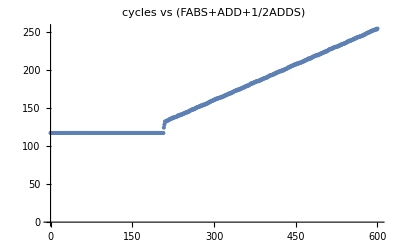

```mathematica
sqrt9ιfabsπaddπadds600=;
ListPlot[sqrt9ιfabsπaddπadds600, 
PlotLabel-> "cycles vs (FABS+ADD+1/2ADDS)"]
```

```mathematica
(* {207,117},{208,124},{209,128},{210,132},{211,132},{212,132} *)
```

Hah! Isn’t it nice when our understanding advances to the point where was can start to make testable predictions?!
So that’s pretty clear! Instructions that both perform some other calculation and set the flags register (ie have two destination registers) require two HF slots. 
More precisely, given the way I described the History File (to unwind register mappings) one slot will be allocated for each register rename. Meaning that we should expect
• zero HF slots for stores
• zero HF slots for explicit prefetch, PRFM, instructions
• zero HF slots for writes to special registers (somewhat... some special registers are renamed)
• one HF slot for standard loads
• two HF slots slots for load pair (which takes two destination registers).
These are all confirmed. (Note our goal right now is to understand the HF, not to probe details of loads, stores or PRFM instructions!)

BTW the special registers case is surprisingly interesting. Reading (and especially writing) special registers has usually been a very slow path, because the easiest way to handle a special register write is to delay performing the operation (and all subsequent instructions) until the relevant instruction is at the head of the ROB, ie to “serialize” the instruction stream. The reason for this is that there are multiple different special registers that all do something different (change memory mappings, change how interrupts are handled, change floating point behavior, ...) and you can’t make those changes while the instruction is speculative because they would be so difficult to unwind if the speculation proved in error. 

But that doesn’t stop Apple. Check this out: (2019) https://patents.google.com/patent/US10838723B1/ Speculative writes to special-purpose register. 
Different registers are handled differently but the basic idea is that 
- Some easy cases (most obviously moving data to and from the flags register) are treated via machinery close to the Rename Mapping machinery. 
- For other cases, the write to the register is allowed to proceed out of order, but the new value is retained in speculative storage. Reads of the new value (with an age stamp later than when the new value was stored) get told the new value; everything’s consistent. Then at the point when the MSR instruction is ready to retire, the new value gets written to permanent special register storage and the machine state is changed. 
So you don’t have to pay serialization costs every time you change a minor register, or when you make a series of changes. Even when the system does require serialization, it can require this only after a sequence of changes has exhausted temporary storage.

There' s a second interesting issue here. 
Any modern machine these days will crack more complex instructions into smaller instructions. For other CPUs this seems to be primarily about execution complexity, but Apple have generalized this into a powerful tool. The insight is that different stages of the pipeline may want to treat an instruction as a single unit or multiple units depending on exactly what the instruction is doing. 
For example an ADDS or a LDP (load pair) want to be treated as two instructions for the purposes of register allocation (Rename) and deallocation (History File) but as a single instruction for the purposes of execute. 
Conversely an instruction like ADD (shifted), which shifts one of its arguments before adding it, wants to be treated as a single instruction for the purposes of allocation and Retire, but to be split into two operations for execution. The patent is here: (2012) https://patents.google.com/patent/US9223577B2 Processing multi-destination instruction in pipeline by splitting for single destination operations stage and merging for opcode execution operations stage.
One interesting aspect of this that I slid past you is that most instructions that split into two executed parts, like ADD (shifted), don’t have to assign a physical register for the intermediate result (in this case the result of the shift); the intermediate result is just picked by the ADD off the bypass bus and no register is wasted. However, strangely, the EXTR instruction, which looks to my eyes looks like it could use this same bypass mechanism, for whatever reason (real issue? or just no-one ever optimized it?) does allocate a genuine intermediate register, with the extra resource allocation waste that implies.

## ROB Duplicate Registers (MOV xn, xm)

This is hardly the end of the story. We know from other investigations that Apple provides zero-cycle moves. The idea of zero-cycle MOV is obvious, in that  you “execute” the move merely by updating the register Mapping tables, rather than by sending an instruction through an integer execution port. What makes this not exactly trivial is that you now need a variety of extra book-keeping to track when it is safe to release a physical register (which now may have multiple duplicate users). 
It’s also worth noting that Apple seems to prioritize the zero-cycle aspect of this technology (also used to load Immediates into registers); it’s nice that the technology allows the machine to act as though it has a few additional physical registers (because a MOV “reuses” a physical register, rather than allocating a new one) but that’s not the priority, the priority is to reduce the latency of MOV in a chain of operations.

Apple appears to have used three successive solutions to this, and it’s worth understanding all three because even when a solution is abandoned, some ideas from it live on in other aspects of the CPU.

The central problem around renamed registers is when they can be reused. 
The first half of renaming is obvious – you need a table that maps architectural registers to the current physical register (or something equivalent, like the ROB slot of the instruction that will eventually produce the value of interest), and you need a pool of free registers from which you allocate a physical register for each successive destination register. 
The difficult part is how you move registers into that free register pool – how can you, as cheaply as possible, and as early as possible, know when a physical register can be reused? 
Conceptually there are three parts to when the physical register is no longer required:
- when the store to the register has been performed AND
- when all the readers of this physical register have executed AND
- when the logical register to which this physical register is mapped has been overwritten
Each of these three parts has multiple solutions, and it’s a constant weighing of options as to which is best. For example for the second sub-problem, one can imagine options that include
- have a table that more or less notes the ROB slot for each reader of a physical register, and clears that entry as the appropriate ROB entry retires, until all entries are clear 
- have a counter that goes up when a reader goes through Rename, and is decremented when a reader is Retired, ie a reference counter
- have a way to scan the entire table (make it a very wide matrix of bits) so that you can easily see if a column is bit-free vs has at least one bit set indicating a user

We see Apple working their way through variants of these ideas over time.
First off, an early patent is (2005) https://patents.google.com/patent/US20070050602A1 Partially decoded register renamer. Good luck understanding this patent first pass through! But it's actually interesting once you figure it out. 
It refers to a core somewhat like A6, so out of order probably 3-wide or so, and primarily interested in the question of: how does the ROB communicate with the register allocation mechanism that some instructions have Retired? (Regardless of what solutions you adopt to the issues I raised earlier, this sort of communication is necessary.)
To understand the solution (which may be used, even today, in a fancier version) you need to know that the machine being described has a 64-entry ROB, treated as 16 "rows" which can each hold four instructions, and one row can Retire every cycle. So you want to communicate with the register allocation mechanism 
- four instruction IDs that have retired 
- look up those instruction IDs in a table (ie use a CAM structure) so you can set various flags for the appropriate registers
- but you don't want to pay the cost having four simultaneous CAMs
So the idea is, instead of indicating the Retiring instructions as four integers, you indicate it as a rowID (a 4bit value) and a mask (four bits) indicating which of the four instructions in that rowID are Retiring. Now you only have to use one CAM (for the rowID) and for each entry that matches the CAM you run a secondary test that it matches the appropriate bit in the bitMask. 
It's a low-level patent, but shows the sort of tricks Apple is constantly playing, using whatever structure is present in a set of values (in this case, that Retiring instructionIDs are sequential) to reduce the workload.

Now let’s look at what needs to be added if we want to use zero cycle moves (and thus allow duplicate logical registers associated with the same physical register).

The first Apple solution uses the RDA (register duplication array), a CAM that can describe ~8 registers that have been subject to duplication. If you create further duplicated registers beyond the CAM limits, the MOV's execute like normal instructions. 
Early Apple patents like 2012 https://patents.google.com/patent/US20130275720A1/ Zero cycle move discuss the RDA in various contexts. 
(The RDA is still being referenced as of 2018 https://patents.google.com/patent/US10838729B1/, but that seems to be a lazy lawyer using obsolete boilerplater and diagrams!)

By 2014 we see https://patents.google.com/patent/US20160026463A1 Zero cycle move using free list counts, a scheme that (to my mind) makes a lot more sense, that trades the RDA (a CAM structure) for a few extra bits in each physical register tracking the number of users. So we have a reference-counting type system.

Finally we see in 2019 a third scheme https://patents.google.com/patent/US20210064376A1 Last physical register reference scheme which specifically states "It is noted that in the previously used register duplicate array (RDA) scheme, a new entry would have been created for PR6 with a reference count of 2. However, in the new physical register last reference scheme, keeping track of the total number of references to a physical register is no longer necessary. Rather, it is sufficient to track only the last reference to the physical register. This is a more elegant scheme that is easier to implement, uses less area, and has higher performance."
(This same patent shows how Apple uses a History File.)

The M1 appears to implements this more elegant scheme, and appears to show none of the limits one might expect from the two prior schemes. 
This third scheme imposes no limits on the number of duplications (MOV's) that can occur, either on the number of different source registers that are duplicated, or the number of destinations to which a given source register can be duplicated. If you look at the patent, you may wonder how it is implemented -- it requires a frequent lookup against the Mapping table to see whether a physical register is the target of a mapping, and this looks like an expensive CAM lookup. My guess is that in fact the relevant structure is implemented as a bit matrix,  a structure we will see again when we discuss Scheduling.

Let’s see what we can learn experimentally about this duplication mechanism. Forget the zero-cycle aspects for now; what this means for resource allocation is that an operation copying one register to another (MOV xn, xm) does not allocate a new destination register as the physical register for xn; instead it simply updates the mapping of logical xn to point to xm's current physical register. There are multiple ways this could be implemented (as the Apple patents already point out) so we want to probe possible ways in which this might fail, or behave suboptimally

### xzr

First we'll try creating multiple references to xzr.

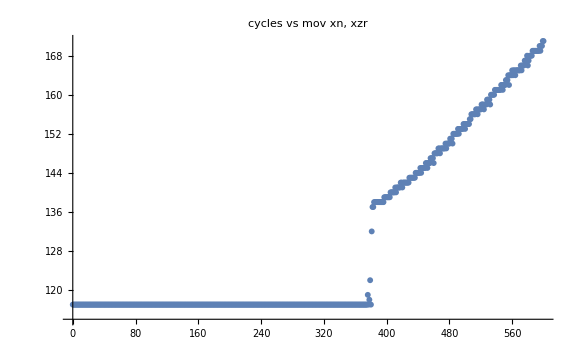

```mathematica
sqrt9ιmovzr600=;
ListPlot[sqrt9ιmovzr600, 
PlotLabel->"cycles vs mov xn, xzr",
ImageSize->Large]
```

```mathematica
(* {378,118},{379,122},{380,117},{381,132},{382,137} *)
```

```mathematica
(600-382.)/(171-130) = 5.317
```

So we see that about 380 xzr allocations can be performed. 

Unexpectedly MOV from xzr is handled like a standard integer operation, executed in the int pipelines. 
We cannot see this from the graph, but the fact that the limit kicks in at ~380 (suggesting the allocation of a physical register) is indicative. 
Looking at the performance counters tells us that MOV from xzr is, in fact, not eliminated. 
We also see from the slop of the ramp that the rate appears to be about 6 MOVs/cycle, ie the standard integer execution rate.

There may be something strange about the implementation here. But it may also be as simple as “don’t do that!”. 
Why, in real code, as opposed to fake benchmark code, would you need this operation? If, in some instruction, you want a register with a value of zero, use xzr, it’s already there! Why waste a second register as a copy?
If for some strange reason you absolutely need a second copy of a zero’d register, Apple has provided a fast optimal path for zero’ing registers via MOV xn, #0. To also special-case xzr would require extra work in decode, and does it make sense to spend that area, power, and cycle time rather than just telling people not to do that? 

As we shall see going forward, there’s more apparent weirdness in how xzr is implemented. But always you have to remember – is this something it makes sense for me to even want to do in real code? 
Rather than implementing xzr as just one more register which just happens to always hold zero, Apple appears to have implemented it as a decoding pattern, which does things like modify the instruction to which we decode, or set a flag on that instruction. And that’s probably optimal in terms of performance and power, if you’re willing to do that extra work…

### xn

But that's not the end of the story! Let's try a non-special register, like MOV x0, x2. 
This case reaches 620 with no glitches (as opposed to the xzr case above)
(Just for fun I also included the case MOV x0, x0. This should be treated as a NOP, and that’s in fact what we see. There’s no reason your code should ever include MOV xn, xn !; but if it does, they behave just like NOPs, using no execution resources except ROB slots, and the curve jumping at around ~2300 when the ROB slots are exhausted. In the curve below you only see the curve start rising at 880 because at that point 880 NOPs/8 per cycle exceeds the 110 cycle delay.)

```mathematica
sqrt9ιmov1200=;
sqrt9ιmovSame1200=;
ListPlot[{sqrt9ιmov1200,sqrt9ιmovSame1200},
PlotLabel->"cycles vs mov xn, xm",
PlotLabels->{"different registers", "same register"}, ImageSize->Large]
```

-Graphics-

```mathematica
(* {616,117},{618,119},{620,120},{622,125},{624,127} *)
```

```mathematica
(1200-624.)/(204-127) = 7.4805
```

So we’re seeing not a limit at the number of physical register (380, as in the previous graph) but at the number of HF slots. 
Once again to see the most interesting aspect of this, you also need to look at the PMC to see that no instruction  issue occurs: all eight MOV’s (different register case) execute purely at Rename. 
We can get some confirmation of this from the graph, since the throughput of the MOV’s is ~8/cycle, which is Mapper/Rename throughput, not the 6 we’d expect if the instruction had to go through the integer pipes.

The same zero-cycle (and 8-wide!) behavior holds for FP/SIMD registers (eg MOV.16B v0, v1). 
We would also expect that, since it's the common pool of History File slots used for both integer MOV and FP/SIMD MOV.16B, when we pair the MOV with a MOV.16B, the jump will be at ~620/2=~310, and that's exactly what we see.

What further aspects of duplication can we test?
The RDA (remember, the subject of the 2012 Apple patent) can only hold a limited number of entries, each describing the number of duplicated references to a register. We can use this to test if Apple is, in fact, still using an RDA.
If we create as many duplicates as possible (ie duplicate multiple different registers) presumably we will flood it, at which point duplications will have to happen via standard execution, not by register rename. 
We create a probe that consists of fifteen instructions
( mov x_i, x_(i-1) for i..1..29 ) 
And replicate this (N/15) times.
(We can’t do much with x31 which is xzr/sp and special, so we are limited to 15 pairings).

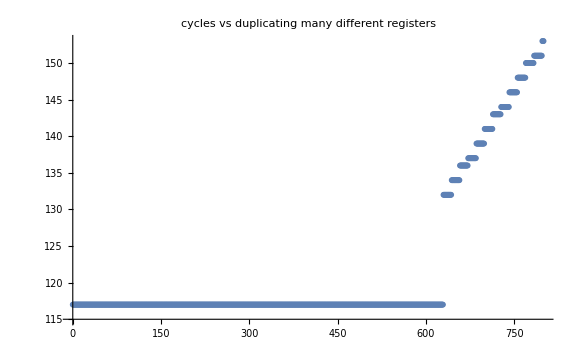

```mathematica
sqrt9ιmanymov800=;
manymovπfmov800=;
ListPlot[sqrt9ιmanymov800, 
PlotLabel->"cycles vs duplicating many different registers", 
ImageSize->Large]
```

```mathematica
(* {628,117},{629,117},{630,132},{631,132} *)
```

The result shows the expected jump (extremely sharp!) when the HF is maxed out at 630. 
More important, however, is that the throughput never deviates from 8 instructions/cycle, so the Rename magic is able to continue working with so many different duplicates established; if there is a limit to the number of duplicates, it’s more than fifteen.
(Remember, what we are testing for is the presence of an RDA, a Register Duplicate Array, that can hold only a limited number of Register Duplicates, ie source physical registers that have been mapped to more than one logical register.)

There are other ways to run the test, like performing fourteen one time duplications of the form  mov xi, x(i-1), to exhaust the RDA; then following with N mov x29, x28. Same results. 
We can also add 15 floating point duplications, for a total pool of 30 duplicated source registers, no difference. 
So, yeah, seems like no RDA is being used.

#### subregisters

What if we try subregisters, eg MOV wn, wm, or MOV.8B vn, vm, or MOV dn, dm?
On the M1 we don’t get any of these fancy tricks when copying subregisters . Such copying is slightly trickier for various reasons, the most obvious of which is rules for how the high bits have to be handled; but it seems like it should be doable, (eg via an additional “zero the high bits” flag in the logical->physical map, or that same bit set in the physicalRegisterID [this concept will make more sense when we discuss immediates].) 
Maybe it’s not worth doing? (But it seems like it should be, especially for code that’s using lot’s of floats or doubles but is not vectorizable). So maybe it’s on the drawing board for a later CPU?

There is something of a historical precedent:
Suppose you have a machine (like the A7) for which you expect both 64-bit and 32-bit wide registers to be common. One way you might arrange things is that your register storage behaves as two side by side banks of 32-bit wide registers, with the ability to allocate a row of two registers as a single unit (perhaps by a high bit set in the registerID). This would give you both some number of 64-bit registers while also giving you more 32-bit registers during the transition period while 32-bit software is common. 
 We see a (kinda sorta) version of it here (2010) https://patents.google.com/patent/US20120110305A1 Register Renamer that Handles Multiple Register Sizes Aliased to the Same Storage Locations, dealing with the old ARMv7 way of aliasing floats, doubles and neon registers. Clearly this is obsolete; but it deals with a slightly more complex version of the problem. 
 Likewise (2012) https://patents.google.com/patent/US9317285B2 Instruction set architecture mode dependent sub-size access of register with associated status indication discusses how power can be saved when reading or writing a 32b (W) register, and the use of an extra bit in the logical to physical mapping table to note that the logical user is utilizing the 32b subset of the referenced 64b physical register. 
 
 Generically, it seems like there is scope here for potentially massive register allocation improvement. 
 Imagine instead of two register files for int (each 64b wide) and SIMD (each 128b wide) we have a single register pool consisting of rows of four 32b units. Register allocation would consist of providing (appropriately aligned) a full row (SIMD register), a half row (double or x register) or quarter row (single or w register). Conceptually as raw storage this is feasible, one just has to be a little careful about how the free lists are treated; and a few high bits associated with each physical registerID clarifying the width of the item that is being extracted. 
 Where things become slightly tricky is in register aliasing (eg you write a signed value to a w register, then read that as an x register). 
 
 In the integer case this is fairly easy to handle; you just need to give the register file some logic so that when values flow in or out they are appropriately shifted and sign-extended, and you need an extra bit associated with each 32-bits to clarify how the sign extension should be performed on the outflow. 
 I haven’t bothered to look at the precise neon SIMD/DOUBLE/FLOAT aliasing rules to know if there’s a difficult problem on that side. But the vision is tantalizing! A unified register pool means that instead of being limited by just the 400 or so integer registers, code that used no fp registers would have many more int registers available, and code that used many w registers would have a pool of even more registers available.  
 (Of course to get full value out of this, the size of the history file needs to be increased, but that doesn’t seem like a problematic structure to grow.)
 
It’s looks like this idea of allowing a wide register to act as multiple shorter registers has been reused, yet again, in Graviton 3, as discussed in https://chipsandcheese.com/2022/05/29/graviton-3-first-impressions/ (look for the Out of Order Structure Sizes section)...

## Instruction Scheduling

Going forward, you may want to keep in mind this diagram by Dougall. The ROB stuff is provisional (and I think better explained below) but the basic ideas and numbers match my investigations. 
And what he calls Dispatch Queues should, I suspect, be thought of as Buffers. Buffers are cheaper than Queues because they don’t make the same ordering promises. I suspect the Apple Dispatch Buffers can lose ordering (in cases where it doesn’t matter much, namely when the Scheduler Queues are so filled up that the Dispatch Buffers are more than just pass-through).

Note that this diagram should be treated as provisional. In particular (eventually both of these will be explained/justified below)
- the monolithic 48 entry Load/Store Scheduling Queue is in fact 4 separate 12 entry queues, just like the other cases
- the other entries apart from load/store are probably about 2x too large (that is, the size of say the two MUL queues is probably ~13 each), likewise the FP queues probably 18 each. Essentially (as will be explained below) while each queue feeds a primary execution unit, the queues are paired, and if one queue does not have a runnable instruction, it can accept the “second choice” runnable instruction from the companion queue; thus for many testing purposes it will look like the queue feeding a particular execution unit is twice as large as it is, because the “amount of scheduling space” is the sum of the two queue sizes.
xxx I have not yet had time to probe the full details of this pairing beyond having seen it in action in the case of load store. 
Given the numbers, an obvious guess is that on the integer side 
- the two MUL queues are paired (each 13 in size)
- two two BR queues are paired (maybe one of size 12, one of size 14, or both of size 13) 
- the ALU/FLAGS queue and the ALU queue stand alone and are not paired.
On the load/store side, the store queue is paired with the ambidextrous (store+load) queue. 
I would guess that the two FPCSEL queues are paired, but have not tested that. 

It makes sense to pair together queues as similar as possible (except where prevented by the fact of the two different integer Dispatch Buffers) because that gives you the maximum amount of sharing flexibility; whichever queue you dump an instruction in, if the other queue can’t find a runnable instruction, two instructions can still be scheduled. This doesn’t work as well when one type of instruction can only go into one execution unit – which is the case for the store vs ambidextrous unit, which is how I discovered the phenomenon.

-Graphics-

Consider now the following experiment. Suppose we use up almost all the int physical registers  (via ADDs) then try to perform some MOV’s. What we are interested in is the transition between these two types of instruction, one of which is executed in the OoO pipeline, one of which is executed in Rename.

```mathematica
add370ιmov800=;
ListPlot[{add370ιmov800, {#, #/8}&/@Range[800]},
PlotLabel->"370 ADDs followed by N MOVs", 
PlotLabels->{"370 ADDs followed by N MOVs", "N MOVs"}, 
ImageSize->Large]
```

-Graphics-

The low-N and high-N parts of this curve are easy enough to understand. We have no delay block. The first segment of the graph corresponds to the 370 ADDs, processed at a slope of 6/cycle; these are followed by the MOVs, processed at 8/cycle, and the difference in slope is visible, compared to the gold curve which is just MOVs without the initial ADDs. 

More significant for us is the flat region from 370 to about 397 
What’s happening there? This  tells us something about the int instruction scheduling. 
To simplify (this will all make sense after you read below then come back here)
- Rename can generate 8 instructions (8 ADD’s) per cycle.
- These can be moved (8 per cycle) into a Dispatch Buffer
- But only 6 instructions per cycle can leave the (integer) Dispatch Buffer
- And those 6 instructions can immediately execute, so they do not fill up the Scheduling Queues
- Hence every cycle the Dispatch Buffer gains two instructions, until it is full
- The integer Dispatch Buffer has a capacity of ~24 instructions, so it soon fills up.
- Once we add a few MOV’s to the end of the instructions to be executed, at first those MOV’s take zero cycles to execute
+ more precisely they execute in Rename at the same time as the ADD’s that were in the Dispatch Buffer are drained
+ so we get 4 free cycles (24 buffer size/6 ADDs per cycle) of NOPs that will not add to our cycle count
+ and 4 cycles of NOPs is 32 free NOPs before the additional NOPs start to increase the cycles/loop iteration

This is the basic idea with the one final tweak being that integer code actually uses two buffers, each of size 12. 
(BTW there’s no significance to the use of 370 ADDs, you just need “enough” where enough is more than 12 cycles*8/cycle=96)

If you understand that, then you should understand this:

```mathematica
mul370ιmov800=;
ListPlot[mul370ιmov800, 
PlotLabel->"370 MULs followed by N MOVs", 
PlotLabels->{"370 MULs followed by N MOVs", "N MOVs"},
ImageSize->Large]
```

-Graphics-

This is very much the same idea, only using MUL x0, x5, x5 as the probe. What should we expect?
We get an initial slope of two instructions per cycle (only two execution units support multiply, but they are fully pipelined). 
The flat region runs for {370,185} to {420,185}, so we get about 50 free NOPs. Does this make sense? Yes!
The Dispatch Buffer that feeds the two MUL units has a capacity of 12, so will drain in 6 cycles. 6 cycles allows 48 MOVs to execute in Rename.
So we validate both our understanding and that there are two Dispatch Buffers feeding the six integer Scheduling Queues, as in the diagram.

## M1’s Implementation of instruction scheduling

The machine is 8-wide all the way though to Rename; and throws out 8 ADD instructions per cycle into the Scheduling Pool. By Scheduling Pool we're being deliberately vague, but mean the idea of some pool of instructions between Rename and Execute from which instructions are Scheduled for Execution in an out-of-order manner, as their dependencies are resolved.
One’s natural assumption, the usual model, is a single level scheduling pool (called something like a Scheduling Queue) but it's time to revise that. 

Recall that the scheduling queue holds instructions that can't yet execute because at least one of their dependencies is not yet available; for example the instruction may be waiting on a load, or it may be one of the final instructions in a chain of ten or fifteen sequentially dependent instructions. 
We want the scheduling queue to be as large as possible, as this allows the CPU every cycle to look over more instructions to find something to execute. Or to put it differently, the larger the scheduling queue the more independent chains of sequentially dependent instructions you can run in parallel, so the more ILP you can extract.

### separate scheduling queues

However scheduling queues are phenomenally expensive in power! (Every cycle you need to scan the entire collection of instructions to check which have become runnable, then of those instructions choose the oldest for execution.) 
The most obvious solution, at least as a first step, is to at least split the single scheduling queue into multiple queues. This means that you sometimes waste some queue space (if you're doing only integer computation, all that space devoted to the fp scheduling queue is wasted) but it allows the sum of all the queues to be larger for the same, or lower, power.

Apple takes this idea to an extreme by adopting a queue in front of each execution unit, rather than, perhaps, a common queue for integer, a separate common queue for fp, and a third separate common scheduling queue for load/store. But a problem with these multiple queues now is that you want to ensure that they are load-balanced. Obviously some integer instructions can only go to one or two pipelines (there are only two branch execution units, only one integer divide unit), while other integer instructions like ADD can go to any of the six integer execution unit queues. You can't do anything about the specific pipeline(s) that some instruction are forced to go down. But you can balance other instructions as much as possible around those restrictions.

### dispatch buffers

Apple's solution to this (which has accumulated other benefits over time) is to install a Dispatch Buffer, a secondary instruction storage pool, between Rename and the Scheduling Queues. 
The initial goal of this Buffer was load balancing -- after instructions with strict requirements are sent to the appropriate queues, the remaining instructions are sent out according to which queues are least full, so that overall queue fullness remains even across all queues. 

Of course the the Dispatch buffer also acts as a secondary storage for instructions, a way to put them somewhere and allow Decode and Rename to keep going, even if all the integer queues are full and can accept no more instructions. A Dispatch buffer is cheap because it doesn't have the ordering requirements of a Scheduling queue (which instructions are oldest?) and doesn't have to be scanned every cycle to figure out which instructions have become runnable. AMD uses a Dispatch Buffer for this reason, for FP/SIMD instructions. You can see the AMD case here: https://en.wikichip.org/wiki/amd/microarchitectures/zen_2 (Look for the big diagram, then in the FP section for the Non-Scheduling Queue)

However a Dispatch Buffer is also imperfect for these same reasons -- if Scheduling Queues all fill up, and then the Dispatch Buffer, so that this Buffer contains more than just a few instructions, then, once execution starts flowing again, it's somewhat random which instructions will be the first to be moved from the Dispatch Buffer to the Scheduling Queues and on to execution; and choosing the wrong instructions from the Dispatch Buffer might delay the execution of critical instructions for a few cycles. 
So a Dispatch Buffer is not absolutely free storage that should grow as large as we like; we want it to be large, but we don't want to have to pay the side effects (poor scheduling) of it being large! It needs to be kept to a limited size so that, even if there is some degree of sub-optimal issuing of instructions to the Scheduling queues, there's also limited delay that can occur. 

There's one other, less obvious aspect to the Dispatch Buffers: each one can accept up to 8 instructions from Rename. Assume you have a long run of integer instructions. Each of the six integer queues can only accept one instruction per cycle, so in the absence of a buffer, Rename would only be able to clear 6 instructions per cycle. The machine wouldn't halt, but the front-end would be forced to run 6-wide rather than 8-wide. It's even worse if there's a long run of FP or load/store instructions where only 4 instructions could be enqueued per cycle. 
Each Dispatch Buffer can accept a full eight instructions per cycle, thus it can clear Rename for the next eight instructions, and this can continue for at least a few cycles, though obviously not indefinitely. As I said about designing not just for the mean of a program, but for the standard deviation...

### evolution of Apple’s scheduling queue

The Scheduling Queue is another case where we can see the evolution of Apple's thinking over time.  (Recall what I said, that Apple use the term Reservation Station for what I'm calling Scheduling Queues.)

#### 2013 (two level scheduling – dispatch + scheduling queues)

We start with (2013) https://patents.google.com/patent/US9336003B2 Multi-level dispatch for a superscalar processor, which describes a basic two level scheme, where the main point is load-balancing. BUT with the secondary point that the buffers are capable of accepting up to eight instructions (whereas queues only need to accept one instruction per cycle). These details matter! Most hardware structures grow quadratically in area as you increase their inflow or outflow. So there's a real win if you can dump all this quadratic complexity (eight-wide inflow) onto a very simple structure, a buffer with no ordering or other properties, while keeping the queues as 1-in, 1-out per cycle.

#### 2015 (non-shifting queue, based on relative age field)

This is somewhat augmented with (2015) https://patents.google.com/patent/US20170024205A1 Non-shifting reservation station, a non-shifting Scheduling Queue which I will describe soon, and the technical companion patent (2016) https://patents.google.com/patent/US10120690B1 Reservation station early age indicator generation.
To understand this 2015 patent, recall that the usual way a Scheduling Queue is implemented is exactly as a physical queue. Using a physical queue means that temporal ordering is trivially preserved -- it's easy to see which instructions are oldest (at the head of the queue) vs youngest (at the tail of the queue). But a queue uses a lot of power because it has to be "collapsing"; that is, every time an instruction is scheduled from the middle of the queue, you have to move all the other values along the queue to remove that vacancy and open up space at the end of the queue. 
Now you can imagine various possible ways to reduces the cost (leave the holes as long as possible, ie only collapse when you have to; maybe use indirection, like a linked list rather than a linear sequence of storage; ...). The Apple solution is to use an age matrix, which is, just like aspects of the 2019 History File patent, a structure that is large (by the standards of tech many years ago -- now transistors are cheap!) but low power and has low complexity wiring. The age matrix tracks the temporal ordering of the instructions while not requiring them to continually be moved from one slot to another. 
I urge you to look at this one; it's fairly easy to understand but so neat! 
Suppose a particular scheduling queue has 30 entries. Then associated with each entry is a 30 bit vector, each bit of which represents one of the queue entries. If a bit is set to 1, that means this queue entry is older than the entry represented by the bit. It's a fairly simple simple algorithm when to flip bits to one then back to zero, and the flipping doesn't have to happen very often (ie low energy). 
(A similar solution is used for the Load/Store Queue as we'll discuss when we get to Load/Store.)

#### 2016 (earlier testing of relatives ages, allowing larger queues)

Now we have this 30 bit vector indicating age of each slot relative to others lots. OK, in principle we understand how it encodes the age info, but what do you actually do with that info? That's what the 2016 patent covers, somewhat. 
One can imagine at least two ways of using these age vectors. One idea is you perform a pop count on each vector, then find the slot with the highest popcount. Conceptually easy, but it assumes that we have fast cheap circuits that perform popcount, and perform "find largest in a set of 30 integers"...
Alternatively we can use good old divide-and-conquer. Compare adjacent pairs of entries to find which is older (which is a simple test of the bits at the two appropriate positions in the two bitvectors), and replicate that 5 times (binary log of 2). The patent points out that you can do at least the first round of this in an earlier cycle (relative age won't change, but you may have to test all slots, you can't mask out slots that aren't executable); and by doing one or more of these relative age comparisons in an earlier cycle you have to do fewer (easier to meet cycle time) in the next cycle. 
One interesting aspect of this recursive structure is that really what you are trying to calculate is not actually "oldest runnable instruction" it is "best choice for runnable instruction". You could replace/augment the age bitvector with something encoding criticality information while still using this same tournament "compare successive pairs" structure to get a criticality-based scheduler; perhaps via something as simple (at least at first) as adding a single extra "critical" bit to the relative age bitvector that overrides age if it's set for only one slot, otherwise it's ignored and age wins. That allows us to start with a basic criticality predictor that generates just a single yes/no prediction.

#### 2017 (pairing scheduling queues and issuing from either)

Next we get (2017) https://patents.google.com/patent/US10983799B1 Selection of instructions to issue in a processor. 

Consider on the one hand Intel's scheduling solution which is (more or less) to use a single large age-ordered queue. 
In theory this gives you total information – you can see all the instructions, all their ages, and can schedule the oldest ready instructions. That may sound ideal but 
- you pay a substantial cost for that in energy, in inability to scale, and in lack of time to implement various smarts
- you're optimizing for something (oldest ready instructions) that is not even really what you want (see my mention a few pages below of criticality).

The Apple solution runs in the opposite direction, starting with the simplest solution that will work (multiple queues, each independently scheduling only their contents). Clearly such a solution can result in multiple types of imbalance, and so we see every year simple tweaks that substantially improves the balancing while not costing much in area or energy. So 
the Dispatch Buffer tries to keep a collection of queues reasonably balanced in their fullness, and 
- the two patents described above track relative age (so that, approximately, albeit not perfectly, oldest ready instructions schedule first).

However we could still have an imbalance where queue A has two instructions ready to execute while queue B has no instructions ready to execute. That’s not ideal! Can we do anything easy to fix this?
Consider how the age mechanism I described above works. Essentially we have multiple rounds of "find the better instruction [by runnability and age] from comparing these two instructions". Each such round take in two candidates and outputs one candidate. 
So suppose that at the very last round, we also offer the second choice candidate from queue A to queue B (and vice versa). 
Queue B will accept the second choice candidate as better than what it has (which is nothing!) and will schedule the second choice candidate from queue A to execution unit B! 
Obviously one needs a few interlocks and tests and so on to ensure that you don't land up scheduling a Divide instruction to a queue without a divider; but it's one more easy'ish tweak to the pre-existing system to improve load balancing and throughput a little more.

#### 2017 (splitting scheduling queue into a fast front half and a slower back half; not implemented? or only for FP?)

Finally we get (2017) https://patents.google.com/patent/US10452434B1 Hierarchical reservation station. 
Honestly I don’t get how this one fits into the general pattern of Scheduling Queues, or any of our test results. Maybe it represents a set of ideas that were ultimately discarded? Or that are only used for FP?

The problem this claims to be solving is that age/readiness comparing the full set of instructions in the Scheduling Queue may not fit within cycle time. The early age (2016) scheme was one of dealing with that. But this suggests a different scheme.
The idea is that we split the Scheduling Queue into two parts, primary and secondary. We run the scheduling machinery on both halves. 
- The results for the primary queue are some number of instructions to be issued (oldest ready instructions); 
- the results for the secondary queue are both 
+ some number of instructions that could be executed (oldest ready instructions) and 
+ a second array, of oldest instructions, to be moved to primary on the issue of the newly scheduled instructions from primary. 

Of course I don't know, but the logic looks to me like the queue they had in mind 
- was split into primary and secondary, 
- initially all secondary did was figure out which instruction each cycle to move to primary; 
- then the inventors realized that by adding a little logic, they could also issue instructions from secondary if primary could not supply enough instructions. 

But there's a lot I don't get about how this fits into the 2015/2016 scheme! We don't want to be moving instructions around (that's the point of the aging bits) but this scheme seems to require moving instructions from primary to secondary. 
Could the primary and secondary queues be interleaved, or side by side, so that the distance moved (from one slot to the next) is not very large?

Perhaps this scheme is specific to FP?
Look at the sizes of the different Scheduling Queues. My rough heuristic for the size of a Scheduling Queue is that it wants to be able to hold enough instructions so that something can always be found to Issue from that Queue. If the Queue is too small, then an instruction that could be Issued is unable to Issue because it's hiding up in Dispatch or even in Rename, invisible to the Scheduler. But the Queue costs power, and if it too large, those extra instructions are always just sitting in the second half of the Queue are doing nothing for performance because an instruction ready for Issue can always be found in the first half.
This heuristic suggests that the optimal length of a queue will vary depending on both 
- how much (on average) instructions tend to depend on the previous instruction (chained dependencies mean the later instruction has to wait in the queue) and 
- on the average latency of these instructions being waited upon. 

This seems to match the pattern we see for Apple. 
In particular for FP/SIMD both long dependency chains and long instruction latencies are common, hence we see each Scheduler Queue as a hefty 18 entries in size. So maybe this patent is more or less specific to FP, splitting these 18 entry queues into two 9-entry halves, or a 12 entry front-section and 6 entry back section,  that are separately scheduled as per the patent?

Another way to try to make sense of this patent is to skip over the details it gives (which are very clear that it is the scheduling queue that is split in two) and assume the patent operates at a more abstract level. 
The basic model is that a Scheduling Queue performs two tasks
- figure out which instructions have become runnable (all their dependencies are satisfied) 
- figure out the "best" of these instructions to execute. (Ideally this would be the most critical instruction; right now it tends to be the oldest instruction).
If a given Queue cannot find an instruction that's runnable then, as described, we try to grab one from the paired queue. Suppose that also fails, what else can we do?
Suppose we add logic to the Dispatch Buffer to figure out which instructions have become runnable. (We could even make this logic somewhat cheap in that it only works for truly runnable instructions, with no attempt at speculative scheduling based on "it looks like this instruction will become runnable next cycle because its dependency takes two cycles and started one cycle ago".) We could also abandon any attempt at finding the "best" of the runnable instructions in the Dispatch Buffer, we just pick a random one. 
This, at the cost of a fairly cheap (I think) addition to the Dispatch Buffer logic gives us a third possible source for an instruction if neither the primary queue nor the paired queue has a runnable instruction available. Even if the instruction that executes is not optimal or critical, using any particular execution slot going vacant is better than not using it!
This model is somewhat different from the exact words of the patent, but  matches the spirit of the patent. So???

### dependency tracking

#### register-based dependencies

The other part of handling Scheduling is tracking instruction dependencies. The traditional way to do this is through physical registers: ADD x0, x1, x2 depends on x1 and x2. We map those to p11 and p12, and route the instruction to scheduling as ADD p10, p11, p12. Then Scheduling won't consider the instruction for Issue until P11 and p12 both become valid. 

This physical register based scheme is an obvious grandchild (after various improvements and tweaks along the way) of the original Tomasulo scheme from the 1960s. You may enjoy reading (1987) https://www.cs.auckland.ac.nz/compsci703s1c/resources/Sohi.pdf Instruction Issue Logic for High Performance Interruptable Pipelined Processors; an old paper which is interesting precisely because it's written at such an early time, talking about the precise mechanics of (one early version of) how you do this, before the details became routinized as just the words Rename and Scheduling. 

A similarly old paper (2000) which at least introduces many of the ideas I've been discussing about how to handle register renaming is
(2000) https://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.137.3852&rep=rep1&type=pdf  The Design Space of Register Renaming Techniques.
These historical papers are helpful in two ways 
• they explain the problem that needs to be solved and 
• reading them you helps you understand the terminology and mindset of comments you find on the internet. 
However it's important to realize just how long ago those papers were, in a Moore's Law world. What was optimal and state of the art in 2000 may make zero sense in 2020. 

This register-based scheme works, but isn't the only way of doing things. The biggest problem is that, for today’s version of Tomasulo-type schemes to work, registers have to be early-allocated, ie have to be allocated at an in-order stage of the pipepline (traditionally in the Rename stage). And the problem with early allocation is that a very expensive and limited resource (a physical register) is now locked up from Rename until the instruction Retires. But if you think about it, the register is only required from the point at which the instruction completes Execution (to hold the instruction result); all the time before Execution (while the instruction is waiting to be scheduled) that physical register is achieving nothing useful; its only purpose is for its registerID to establish instruction dependencies. 

So: can we late-allocate a register, at the point of instruction execution (in fact completion, when we want to write out the result!) rather than at Rename? 
Yes – if we have some alterative way of tracking instruction dependencies...
One version of this, an extension of Tomasulo, uses virtual registers (1999) https://upcommons.upc.edu/bitstream/handle/2117/101362/00809456.pdf Delaying Physical Register Allocation Through Virtual-Physical Registers.

The flip side of late register allocation is early register release, ie releasing a physical register as soon as it’s no longer required (because all potential users have executed) rather than waiting until Retire. The details of how this could be done (not optimally, but picking up some of the value) appear in the Haithim Akkary paper referred to earlier, describing Checkpoints and other instruction for very large OoO processors. 

As far as I know no commercial CPU (even Apple) currently uses register late allocation or aggressive early release. However IBM (in recent POWER) does use late-allocation of load/store queue slots.
Apple definitely uses at least one of late-allocate or early-release for load/store queue slots, probably early release. (A 2019 patent described below suggests a scheme with traditional allocation of LSQ slots, but early release.)

#### instruction-based dependencies

An alternative is, rather than saying that  ADD x0, x1, x2 depends on (the physical registers mapping to) x1 and x2; to say that the ADD depends on the two previous instructions, call them I27 and I35, that will produce x1 and x2 respectively. 
This could be implemented by, eg, having I27 and I35 in fact refer to the ROB slots of the relevant instructions, and essentially instead of marking a physical register as valid at Execution completion, the ROB slot is marked as valid. Let’s call these numbers associated with previous instructions SCH#’s. 
Thus associated with each instruction in scheduling is a Dependency Vector, which describes the instructions that have to complete before this instruction can execute. (This may sound more sophisticated than virtual registers, but in fact it harkens back to the mid-1990s when, as I've already described, something like the Pentium III attached a physical register to each ROB slot, and so marking a physical register as valid was the same thing as marking a ROB slot as valid.)

The Apple Scheduler patent is (2016) https://patents.google.com/patent/US11036514B1 Scheduler entries storing dependency index(es) for index-based wakeup.
To understand it, we need some history.

The original 1960s Tomasulo renaming stuff, already mentioned, is from an utterly different world in terms of transistor budgets and the relative speed of different components. (You will see, in the history, an explanation of some of the SCH# naming conventions in Apple patents, and will see why they refer in the patent to possible ways of doing things that clearly seem dumb!) For our purposes the aspects of Tomasulo that matter are 
- Registers were renamed via a mapping table
- A destination register was NOT allocated right away. 
+ the scarce resource was a slot in the Reservation Station and physical registers.
- When a slot in a reservation station became available, a waiting op was moved to that slot. Call the address of that slot a "tag"
+ it should be clear that this tag conceptually functions as an ID for an operand for all subsequent instructions. It acts like a physical register ID.
- When an instruction in the reservation station is able to execute (dependencies satisfied) a destination register is allocated. 
+ that register is marked with the tag we mentioned earlier.
+ so at this point we have a destination register marked with the tag of an instruction, and possible dependent instructions marked with such a tag
- Once the instruction has executed, it broadcasts its result on the bypass bus along with the tag.
+ dependent instructions in the reservation station look for the matching tag and grab the result (their operand value) from the bypass bus.
+ likewise the register file looks for the matching tag, and stores the result in that physical register.

Compare all this to the model you should have of renaming today. We 
- Provide the destination register at Rename, not much later at Issue. This means the destination register is idle for those cycles between Rename and Issue (as we have already discussed) but it means much of this tagging nonsense goes away. 
- Instead of a tag (allocated when the instruction moves into the Scheduling Queue) dependency can be built upon the destination register's physical registerID. 
- An instruction has as unresolved dependencies, not a tag (the ID of an instruction that has yet to execute, attached to the result of the execution on the bus) but a physical registerID on an invalid register. When an instruction executes, it dumps the result (plus the destination physical registerID) on the bypass bus. The destinationID tells the bus where to place the value in the register file (so no tag comparison needed there), but all waiting instructions in all scheduling queues still have to look at all the physical registerIDs flowing over the bypass bus to see if one of those registerIDs matches a dependency so that they can now be marked ready to execute. 
You can see that the two procedures are very similar, just with the role of the tag being replaced by the destination physical registerID. But you can also see that we have a huge scaling problem here, trying to compare all the possible physicalRegisterIDs generated in a cycle (there are 14 units that could all generate a result in one cycle on the M1, and some of them [think load pair, or an instruction like ADDS that also sets flags, could generate two results) with the physical registerIDs that are the dependencies for every instruction in every queue. We need to rethink the problem based on today's concerns, not the concerns of the late 60’s.

For now assume that the earlier instruction on which we’re dependent is identified by ROB slot. Given ~2300 ROB slots, that would mean ~2300 instructions on which we could depend. But think about what we are trying to do. 
Suppose instruction i0 depends on architectural register x1, which is mapped to physical register p2. 
At the point where i0 enters the scheduling queue, p2 can either be valid or invalid. 
If p2 is valid, then i0 has a dependency on p2, but it’s not an “op-dependency”. As far as scheduling is concerned, i0 can execute right away, because p2 is known. 
On the other hand, if p2 is invalid, then there is an op-dependency on p2, and i0 cannot execute until the producer of p2 has executed. Thus for scheduling purposes we want to know what pending instructions i0 is dependent on. 
This simplifies the problem; we don’t actually care about every instruction in the ROB, we only care about instructions that are in the scheduling queues and haven’t yet executed; an instruction that executed before i0 even entered the scheduling queue has stored its result in p2 and is not relevant for scheduling. 
So the number of instructions we need to track for scheduling is really the number of instructions that are waiting to execute ahead of this one, which is a maximum of ~400 (worst case total occupancy of all the scheduling queues and dispatch buffers).

How are SCH#’s implemented? I think the original implementation (when the SCH# terminology was born) had no Dispatch Buffers, and had the Mapper allocate an instruction slot in a particular scheduling queue. Thus the SCH# could literally refer to the slot of the queue in which the instruction was placed. 
But the current implementation is, I would guess, much like register allocation. Imagine a pool of 400 numbers, 0..399. Each is marked busy or not. Map allocates each instruction a free index from this list, marking the index as busy; at instruction is removed from the scheduling queue, that same index reverts to free, and that index is used to broadcast “instruction with this index has generated a result”. This gives every instruction a unique persistent ID from the beginning to the end of its scheduling career, from a set that’s as large as required but no larger.

#### bitvector-based dependencies

Now how is dependency implemented? You might imagine something like an array for each instruction that holds a maximum of maybe three SCH#s. That seems obvious, but If we trust the patents, the obvious answer is wrong. 
It appears to be that each instruction has an associated dependency bitvector, with a bit set for each dependent SCH#. This means a dependency vector is ~200 bits long, though only a few (perhaps two or three) of those bits are set. 
There are a lot of patents that suggest this bitvector implementation, eg (2006) https://patents.google.com/patent/US7647518B2 Replay reduction for power saving, which says "The dependency vector may comprise a bit for each entry in the buffer 42" (buffer 42 is essentially the scheduling queues).
The most detailed explanation seems to be in this patent (which otherwise covers very different material, but has a full explanation in the section covering Figure 2): (2014) https://patents.google.com/patent/US20150207496A1 Latch circuit with dual-ended write.

Why run your dependency based on instruction number rather than the Tomasulo physical register-based scheme?
One possible answer is that it allows you to have dependencies beyond just register-based. 
We will discuss more details around load/store issues and, in particular, load-store dependency, below. But the issue that matters right now is easily understood: 
suppose you have a load that depends on an earlier store (ie the load load's from an address to which a store stored in the recent past). Clearly, for correctness, the load must execute after the store has executed, otherwise the load will load stale data from the cache.
There are a variety of aspects to exactly how this is done, but summarizing it all
- there is a predictor table (the LSDP -- Load Store Dependency Predictor) that records these dependency pairs as they are encountered.
- interestingly, this table is associated not with the Load/Store unit but with the Mapper unit (the unit that figures out inter-instruction dependencies in a group, and the physical registers upon which an instruction [encoded as logical registers] depends. Why is this?
- because the LSDP implementation is handled as just one more dependency of the load! Just like the load might depend on instruction M to produce one of the registers that goes into the address calculation, it can also depend on instruction N (which will perform the store) as an instruction that has to be completed before the load can execute. 
(I have to say I find this a genuinely cool idea, one that I have not seen before and did not think of for myself.)
Details of this (along with many other details of how the LSDP detects loads that depend on stores, and how those load/store pairs are aged out of the LSDP table) can be found in (2012) https://patents.google.com/patent/US20130298127A1 Load-store dependency predictor content management.

This requires being able to add an additional dependency to the Load – but that is not a problem given the dependency bitvector, it’s just one more bit flip!
This idea can be (and is) generalized by Apple in many different directions.
- For example another aspect of Loads (to be explained later, for now we just give the idea) is Replay. A Load may fail temporarily because a resources it requires is unavailable (eg a TLB lookup or an L1D cache lookup). This can be resolved simply by having the load retry every few cycles, but that wastes energy and resources. For a range of Apple devices (from the A6 to the A10; as of probably the A11 an even more sophisticated scheme was implemented) Replay was handled by adding to the bitvector a synthetic dependency associated with the event being waited upon.
- Another version of these synthetic dependencies is used by a scheme that performs thread context switching in hardware and in the background as other instructions execute.
- Yet another version is used in Apple’s value prediction scheme. 

The dependency bitvector makes it easy 
- to add new dependencies to any instruction. 
- to define new types of dependencies. These merely have to grab a free SCH# from the pool (which we may want to expand to 450 or so) and broadcast that SCH# at the point when the synthetic dependency (eg service this particular TLB miss) has been completed.
None of this flexibility would be possible with a fixed sized dependency array of say a maximum of three dependencies per instruction.

### implementing the scheduler

Finally how do we use all this? Remember we started with (2016) https://patents.google.com/patent/US11036514B1 Scheduler entries storing dependency index(es) for index-based wakeup.

Step one is we realize that the problem splits into three conceptually distinct tables. 
Consider a Scheduling queue with 30 entries. Treat each entry as actually composed of three fields that are very different, so it's like we have three tables each thirty entries in size. 
First table holds the operation, its physical destination registerID, and its source operands. These could be immediates, they could be physical registerIDs. Point is, this first table tells you everything you need to execute the instruction, but nothing about how to schedule it. It does not tell you when the instruction can/should run, just what you need once you've decide to run the instruction.

Second table holds the dependency information. 
So this second table is going to be a huge bit matrix. 30 rows high, around 400 columns wide. We've already discussed the dependency bitvector. So for any given row (a pending instruction) there will be just a few bits set. Maybe bit 7 of row 4 is set , meaning 
- the instruction in Scheduling Queue slot 4 is not yet ready to execute. It depends on some physical register that hasn't yet been filled, and the instruction that will fill that register is the instruction that has been given SCH# index 7. 

Third table ties these two together. It holds the SCH# of each instruction, and the relative age data (discussed in the Non-shifting reservation station patent above). 
So now think what happens conceptually during execution. The bypass bus still exists, still carrying all the generated results along with their destination registerIDs. 
But there is a parallel bus that exists about 400 bits wide. Each time an instruction issues, from all the different execution units, each unit sets one of those bits active depending on the SCH# of the instruction that they are issuing. So that bus is carrying say 10 or so hot bits representing all the instructions that will soon be generating a result. (It doesn't matter whether they generate two results or one; all that matters is that a younger instruction depends on this instruction to have been completed before it can execute.) 
That 400 wide bitvector can be grabbed by every scheduling queue, copied to the top of the scheduling bit matrix, and the hot bits allowed to "flow" down their columns. Every 1 that they encounter in the column gets flipped to a 0. (The 1 meant this row's instruction was waiting for this column's instruction to have been completed.) Then every row can be or'd to see if it's all zero; if so it's marked as ready and can be scheduled as soon as other details (like age relative to other instructions) allow.

There are plenty of details I'm omitting here. 
One obvious detail is, as we have mentioned, there are additional dependencies that can be added to the bitvector, but those trivially fit into the model. 
Trickier, and I ignored it to get the idea across, is what to do about instructions that take longer than one cycle to execute – I was sloppy about the timing details, but conceptually, of course, what you want is for each execution unit to place its "this instruction is about to complete" bit on the 400-wide common bus in the cycle just before the instruction will complete.

In one sense this is no different from the earlier tag and physical registerID schemes
- 14 units are each broadcasting that they have completed an instruction, and 
- the identifier for that instruction has to be tested against every waiting instruction. 
But we have dramatically regularized the problem! We have a single wide bus carrying the info from all those execution units. We have a single bit matrix (per Scheduling Queue) that is tested against that wide matrix. Our scheduling problem now boils down to figuring out nice circuits to perform the two tasks of interest (flip all 1s in a hot column to 0s; then find all rows with only 0s) and because these are clean bit-matrix problems we can solve them however is most convenient, even by analog techniques. 

Note also that we simplify things by dealing with three different structures:
- a scheduling matrix that tells us which instructions are able to execute (all dependencies fulfilled)
- an age matrix which tells us which of the ready instructions are oldest
- an instruction list holding what needs to be passed on to the execution unit

This idea is called matrix scheduling. It may not sound like the patent if you read the patent blind, but I think you will agree that it's the only reasonable interpretation of how things have to work (given how wide the M1 is, and given everything else we know about the machine, like distributed scheduling queues and dependency bitvectors). 
I think the specific point of the 2016 patent is the exact timing in this scheme. If you followed the tagID/destination physical registerID scheme, you'd broadcast the SCH# of each instruction in the cycle that it completes. This is easy, matches history, and the signal provided clearly means that the instruction has completed. 
But it makes the Scheduler timing very tight; and it’s not necessary! With the matrix scheme I have described, you know, from the moment the decision is made as to which instructions will issue, what the SCH#'s of interest will be, so you could broadcast them in the issue cycle. 
That's fine for most (one-cycle-latency) instructions, but you need something extra to handle the multi-cycle latency cases, hence the patent. I think, for example, that the bit-shifting scheme used by load-dependent instructions to maintain them in the scheduling queue until the load is proved valid (or needs to Replay) could be reused as a timing mechanism for this purpose.
(But honestly this is one of the uglier Apple patents I have encountered – determined to claim everything, equally determined to reveal nothing. If Apple gets this rejected by a court at some point, they'll have only their lawyer to blame – part of the patent deal is that you explain how you do something, you don't just claim that something can be done. And this patent elides the explanation of the only part that's interesting, namely the multi-cycle timing.)
The one other thing the patent covers is a few technical details that reduce energy consumption by allowing rows that are no longer of interest (have all their scheduling requirements already matched) to opt out of the matching procedure.

#### criticality based scheduling (future, not yet implemented by anyone)

BTW instruction scheduling, though it's been thought about for so many years, is hardly a solved problem! In particular, scheduling based on the oldest runnable instruction is merely a heuristic it's not optimal. Better would be to schedule instructions based on criticality, which is a measure of how much subsequent instructions will be sped up by executing this particular instruction right now. There are way to measure (approximately, of course, we can't look into the future!) criticality fairly easily, and there are criticality predictors that do a good enough job. The concept is explained very nicely in Pierre Salverda (2008) https://www.ideals.illinois.edu/bitstream/handle/2142/11442/Principles%20of%20Instruction-Level%20Distributed%20Processing.pdf?sequence=2&isAllowed=y, Principles of Instruction-Level Distributed Processing.
But as far as I know no-one is yet using criticality to inform their instruction scheduling.

#### split scheduling queue (obsolete, only of historical interest)

For completeness, there’s an additional early Apple Scheduler patent here (2008) https://patents.google.com/patent/US20100162262A1 Split Scheduler, but I think it’s only of historical interest. The problem that patent wants to solve is to be able to schedule dependent instructions back-to-back, and the solution adopted is to try to segregate “immediately dependent instructions” from “other” instructions, so that the immediately dependent instructions form a very small pool that can easily be scheduled. 
However the problem to be solved is better solved via speculative scheduling, so this is all moot. 

There are more modern interesting ideas in the space of splitting a scheduling queue; one of my favorites is (2015) https://hal.inria.fr/hal-0122519/document Long Term Parking (LTP): Criticality-aware Resource Allocation in OOO Processors. But so far no-one appears to have adopted any such ideas.

#### microcode

Even on ARM occasional microcode may be necessary, for the occasional complicated system control instructions (like the instructions to invalidate particular sets of items in the TLB). (2011) https://patents.google.com/patent/US9280352B2 Lookahead scanning and cracking of microcode instructions in a dispatch queue dates from the Swift (A6) days but may well be (to some extent) the way the issue is still handled. 
What’s interesting about this is how it compares with Intel. Intel and AMD insert microcode at Decode. This complicates Decode, but means the microcode instructions have full access to Rename/Allocation facilities. If we take the patent literally, Apple does the equivalent after Rename, detecting “complex” instructions as they pass through Dispatch, on their way to be inserted in various either Dispatch Buffers or Scheduling Queues. When the complex instructions are detected, they are replaced with some number of microcode instructions which are fed into the Dispatch process until they’re done. 
This is presumably slightly more energy efficient and more resource efficient (eg it looks like these distinct microcode instructions do not take up ROB slots); but it also constrains how wild they can be if they can not, for example, branch, or allocate generic registers. However, if the ISA does not require such shenanigans, why not take advantage of inserting microcode at this latest possible opportunity?

(Simple instruction cracking, at least for instructions that touch multiple registers, is handled by the (2012) https://patents.google.com/patent/US9223577B2 Processing multi-destination instruction in pipeline by splitting for single destination operations stage and merging for opcode execution operations stage scheme, as already described which, in Decode, generates multiple instructions [which can each be handled appropriately in Rename/Map/Allocate] then in some subsequent stage [maybe using the same sort of pattern detection as the “complex instruction” detection, in Dispatch] merges them back to a single instruction.)

### optimizing the issue queue

We don’t often think of it that way, but instruction queue slots are a resource, like ROB slots or physical registers. And like those, we should be interested in any scheme that can give us effectively more instruction queue slots. 
Traditionally the instruction queue is one of, perhaps the, hottest parts of the chip because every cycle the entire queue has to be probed to figure out what instructions can be woken up (based on values that became available in the previous cycle) and the “queue” has to be repacked, or something equivalent, to both maintain age order and handle the holes from random instructions in the middle of the queue being scheduled.
We’ve seen that Apple tries to deal with these issues in a variety of ways
- multiple per-execution unit queues rather than one large queue
- clever dispatching of instructions to balance across queues (reducing the downsides of multiples imbalanced queues vs one large queue)
- using a tournament to find the one best (oldest, but ready) instruction for scheduling in each queue, rather than exact age maintenance
- using queue pairs to handle imbalance, where one queue might have two ready instructions and its paired queue has no ready instructions
- using a non-scheduling buffer to hold instructions even when the instruction queue itself is full. 
Ultimately these are all an attempt to provide something close to issuing ready instructions by age, but without promising perfect scheduling by age. 

The point of all this is that the Issue Queue is what allows us to look ahead in the instruction stream for independent instructions to execute. The large our look-ahead window, the more likely we can see past the next thirty (or fifty, or one hundred) instructions all dependant on what we are doing right now to find non-dependant instructions that we can execute simultaneously. This is different from the function of the ROB, which is essentially to maintain speculative state in such a way that we can recover if the speculation proves to be a mistake. So the ROB is (as of M1) effectively around 1000 instruction or so of speculative state, while the Issue Queue(s taken together) as of the M1 provide a look-ahead window of about 280 instructions. 

Can we do even better? In fact we can. Consider (2020) https://www.diva-portal.org/smash/get/diva2:1390628/FULLTEXT01.pdf Rethinking Dynamic Instruction Scheduling and Retirement for Efficient Microarchitectures. This thesis points out that about 30% of instructions at Decode or Rename time already have their input values available, they have no need for the area and power complexity of the Issue Queue (which is all about holding instructions waiting for input values, so that as soon as a new input value arrives the oldest such waiting instructions can we woken up and issued); this 30% can issue right away. So why not bypass them into a much cheaper structure?
You can do even better than this if, in addition to detecting readiness at Rename time, you also detect criticality. Now you split your instructions into three streams, essentially ready (so don’t need fancy scheduling), non-critical (so also don’t need fancy scheduling, they can wait around in a simple structure till ready, and then just be executed whenever there are free execution units) and about 40% or so of instructions that are both not ready and critical, and so do need the full machinery of the Issue Queue.
(The second half of this thesis discusses out of order retirement, something we already discussed earlier in this document. The thesis approaches the problem of out of order retirement from a different angle, IMHO less practical than the idea of the Validation Buffer, but it does include essentially limit studies that suggest that practical “safe” out of order retirement can get you about 50% better IPC, while “unsafe” retirement can get you around 100% better IPC.)

The above ideas tackle one side of the issue queue, namely trying to bypass it for items that are already ready.
The other side of the problem is avoiding stuffing the issue queue with instructions that will not be ready for a long time (and thus are just wasting space and burning energy every cycle, to no useful end). We’ve mentioned one solution to this is Long Term Parking; a different paper giving much the same ultimate solution is (2004) https://d1wqtxts1xzle7.cloudfront.net/93424809/ICS-04-IQ-libre.pdf?1667281228=&response-content-disposition=inline%3B+filename%3DScaling_the_issue_window_with_look_ahead.pdf&Expires=1732473961&Signature=Tj5CYWqB2gKAm-UaGjZXYLCGIRIX7gCOBqY4iX2liRu6tsIkpjarewsIb954~OS6FtICS-aZ-Kehzru3qF94ZEK~lyy7PfSqMIGuMuQe~j2YAYFRG-NRhqNlJ4yXPfmW6WHViQcLpRO27IRWQUiD-9BjceiWdBURINeJSlRuyM2Mob6wsIXowub1eDXcBXJbGapjbvRmBAb3RGYiloX~R29y0rt9lkNO2h8RvjrRrL1UTC84WMVLFm8I8sGB6l7ZgRIDJwJ7G7T6Bc4m-LJB5q8BLuHMw8YvXpX8QVZo9YNd90owYffmJWt15h2jnvB3yIoG5PuDYl9DGr8vN0P2Ag__&Key-Pair-Id=APKAJLOHF5GGSLRBV4ZA Scaling the Issue Window with Look-Ahead Latency Prediction. 
In both cases we begin with a latency predictor that attempts to predict instructions that will take a long latency (generally loads that will miss in L1), then steers the dependents of those loads  into a light-weight buffer where they can sit comfortably until they become runnable. For most CPU designs you also need to estimate when the load will hit the cache, or accept some lost cycles while the instructions were waiting in the buffer while runnable. For Apple’s design this is probably less of a concern, given that Apple already appears to have very fine-grained notification from the L1 cache up into the core that any particular load has just hit the cache.

This idea of long term parking, or shunting predicted long-wait dependents to a separate buffer sounds good – but there is a problem you have to be honest about. How useful, in the real world, is your predictor? 
We are interested in loads that are predicted to miss in L1. But most (not all, but most) of such loads can also have their addresses fairly well predicted, in which case we can prefetch their data. So this machinery only work ideally for a fairly narrow case of loads whose address cannot easily be predicted (eg walking some large complicated data structure) or cannot be predicted early enough for prefetch to be useful. A lot hinges on the quality of the predictor, and it’s unclear in many papers that the predictor has been paired with a realistic CPU design, specifically a realistic set of prefetchers.

## Experiments on instruction scheduling

## Explaining the integer Dispatch Buffer

So back to the issue that got us interested in scheduling in the first place -- in the previous graph, what’s up with the pronounced flat region in the middle?
Here’s my best explanation:
Assume a two level Scheduling Pool: an initial buffer (the Dispatch Buffer) followed by a genuine Scheduling Queue. We know that Rename can dump instructions into the integer Dispatch Buffer at 8/cycle, but maybe instructions can only leave that buffer at 6/cycle, so one per scheduling queue? (Faster might be desirable under rare conditions, but it’s usually unnecessary, and it’s power/area expensive.) 
This would mean that the Dispatch Buffer is going to fill up at a rate of 2/cycle (8 in, 6 out). Or, more precisely, perhaps each of the two Dispatch Buffers fills at 1/cycle (4 in, 3 out)?
After 96 ADDs, a Dispatch Buffer that can hold 24 (2/cycle*12 cycles) will be saturated. In fact Dougall’s experiments (probing for exactly this size, not detecting it as a side effect like we are doing) has the 1st level int Dispatch Buffer as 24 elements (split into 12+12). 
So effectively the machine runs like 
First 96 ADD’s: 				throughput 8-wide, fills up first level Dispatch buffer with ~24 instructions
274 ADDs from 80 to 370: 	throughput 6-wide, since only 6 instructions can pass from Rename to Dispatch
		excess cycles in this phase is (290/6-290/8=11.4. We have permanently lost ~12 cycles in our 8- vs 6-wide comparison. 
MOV’s start: 				for about 4 cycles (24 ADDs/6) we get to process ~32 MOVs (or NOPs) for free in Rename, in parallel with int Execution as the excess ADDs stored in the 24-slot Dispatch Buffer are drained. 

In other words the flat region (when it’s apparently costing us no extra cycles to process MOVs (or NOPs, or anything else executed in Rename) are when we’re overlapping execution in Rename with instructions that were present in the Dispatch Buffer and are now making their way to Execution. For this to happen we need the flow rate into Dispatch Buffer to be higher than the flow rate out from Dispatch Buffer, so that a backlog of instructions builds up in Dispatch Buffer that can then drain in parallel with the subsequent instructions executing in Rename.

### testing the fp Dispatch Buffer

We can check this understanding by testing a few variants. 
If this analysis is correct, we should see the same phenomenon if we follow the ADDs with something like FABS which executes not in Rename, but in a different pipeline, so can again run in parallel with the int Dispatch Buffer draining.

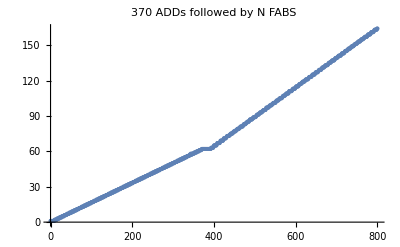

```mathematica
add370ιfabs800=;
ListPlot[add370ιfabs800, 
PlotLabel-> "370 ADDs followed by N FABS"]
```

Well, that’s nice! As we predicted :-) And in fact the signal is cleaner (the flat run is 23 instructions long)

## Interpretation as smoothing mechanism

Now let’s try something a little different. 
Suppose we interleave (6ADD+ 2NOP). We know that can run at 8 wide indefinitely, it’s perfectly balanced with, every cycle, 6 instructions going into the integer pipeline and 2 NOP instruction being executed at Rename. 
Now suppose we change this to (12ADD+ 4NOP). Now it’s not perfectly balanced: The first cycle we dump 8 ADDs into the Dispatch Buffer, but only withdraw 6. The next cycle 4 ADDs into the Dispatch Buffer -- along with 4 NOPs executed at Rename, and then 8 NOPs executed at Rename. But still balanced overall – as long as we have a buffer that can hold 2 ADDs. 
We can continue like this through (k*6 ADDs + k*2 NOPs), until the point where the Dispatch Buffer is not longer quite large enough to hold all the excess ADDs. Let’s see what I mean:

```mathematica
add6nop2=;
add72nop24=;
add84nop28=;
add90nop30=;
ListPlot[{add6nop2, add72nop24, add84nop28, add90nop30},
PlotLabel->"ADD/NOP sequences",
PlotLabels->{"6ADD+ 2NOP","6*12ADD+ 2*12NOP", "6*14ADD+ 2*14NOP", "6*15ADD+ 2*15NOP"}, ImageSize->Large]
```

-Graphics-

Consider the case of 6*15 successive ADDs. This is 90 ADDs, so takes just over 11 cycles (8*11=88) in the pipeline up to Dispatch. Each of these 11 cycles, 2 excess ADDs remain in the Dispatch Buffer, so at the 15*6 case we have almost maxed out that buffer. Throw in imperfect alignment and imperfect balancing of instruction and we can say the buffer reaches its capacity. And we see that it is indeed noticeably slower than the predecessor cases. 

Essentially the case 6*1 through 6*13 always take the fast path (102 cycles per loop iteration), anything above 6*15 takes 108 cycles, and 14 is a slightly noisy version in between. 
To put it even more simply, the Dispatch Buffer acts to smooth local variations in the types of code, so that a dense run of ADDs can still run 8 wide, as long as the dense run is not too long. We see the transition here between the case of not too long and too long here at between 6*13 and 6*15 successive ADDs. Once you are unbalanced for too long buffering cannot save you and your maximum throughput is reduced (ie slope of the line moves upward).

The same sort of buffering over regions of dense code (for example a stretch of FP or load/store dense code should likewise help us to still maintain an IPC of 8, as long as
- overall the balance of instructions is not too biased to only one type of instruction, and 
- the runs of a single type of instruction are not too long.

### acceptance width of fp buffer

Now the next obvious question is what are the exact properties of these Dispatch Buffers. For example consider the floating point dispatch buffer. Presumably this releases instructions 4/cycle, but does it accept instructions 8-wide or something narrower? Let’s see.

```mathematica
fabs4nop4π1=;
fabs4nop4π6=;
fabs4nop4π5=;
ListPlot[{fabs4nop4π1, fabs4nop4π5, fabs4nop4π6},
PlotLabel->"FABS/NOP sequences",
PlotLabels->{"4FABS+ 4NOP", "20FABS+ 20NOP", "24FABS+ 24NOP"}, 
ImageSize->Large]
```

-Graphics-

So let’s assume that the green line were exactly  matching the lower two lines. That would mean that three successive (8x FABS) instruction probes could be processed through Rename (and into fp Dispatch), followed by three successive (8x NOP) instructions without a hiccup. Which would mean that the Dispatch Buffer must be able to accept 8 instructions per cycle, and be able to hold at least 12 instructions (since each of those three cycles, its net occupancy will grow by 4 instructions. 
We see that we can’t quite achieve that with 6*(4x FABS+4x NOP) but we can with 5*(4x FABS+4x NOP). Suggesting that the Dispatch Buffer is ~12 in size. (The methodology is somewhat sloppy because it will be sensitive to exactly how the FP instructions are aligned in the run of eight instructions that’s passing through Decode to Rename – sometimes there will be perfect alignment, sometimes there will be a straddling of some FP instructions at the head and at the tail of a line.)

### probing that the integer buffer is split in two

Now what if we try this same methodology with CMP? We believe that CMP can execute of three of the six integer pipelines, and Dougall’s diagram suggests that one of the two integer Dispatch Buffers feeds these three pipelines, meaning we should expect to only be able to buffer 12 of these instructions. Do we see that?

```mathematica
cpm3nop5π5=;
cpm3nop5π6=;
ListPlot[{cpm3nop5π5, cpm3nop5π6},
PlotLabel->"CMP/NOP sequences",
PlotLabels->{"15CMP+ 25NOP", "18CMP+ 30NOP"}, 
ImageSize->Large]
```

-Graphics-

So let’s think about this. When we run 6* (3x CMP+5x NOP) we have a sequence of 18 successive CMPs running through Rename. That’s a little over 2 (round it up to three!) cycles. 
If we take this as meaning that we can transfer all those CMPs into a (12-sized) buffer while, during two cycles, extracting 2*3=6 CMPs, the numbers kinda work out – certainly better than assuming a 24-sized buffer. It also seems that these two integer Dispatch Buffers can accept 8 instructions per cycle.

You will recall when we started down this path we also ran the experiment for MUL, another instruction specialized to only some integer execution units, and again we saw the same sort behavior, a buffer of ~12 in size.

### probing if the fp buffer is split in two

What about the fp Dispatch Buffer -- is it possible that there are two of these, each feeding two of the four fp pipelines?
We can try the same technique with FCMP (which can only execute down one of the four fp pipelines). 
The results are

```mathematica
fcmp1nop7π6=;
fcmp1nop7π15=;
fcmp1nop7π14=;
ListPlot[{fcmp1nop7π6, fcmp1nop7π14, fcmp1nop7π15, {#, #/8}&/@Range[800]},
PlotLabel->"FCMP/NOP sequences",
PlotLabels->{"6FCMP+ 42NOP (blue)", "14FCMP+ 98NOP (gold)", "15FCMP+ 105NOP (green)"}, 
ImageSize->Large]
```

-Graphics-

Now this one is actually surprising! The jump (deviation from a long term rate of 8 operations/cycle) occurs at 15* (1x FCMP+ 7x NOP). It’s hard to square that with the precise numbers on Dougall’s graphic. 
If we can sustain 14 FCMP without reducing the overall throughput (ie overall the gold curve stays at the same slope as the blue curve [6 FCMP] and the red curve [8 ops/cycle perfection]), that implies we must be able to in a first cycles move 8 FCMP from Rename to FP Dispatch, of which one moves on to Execute. Then in the next cycle we move over 6 FCMPs, one goes to Execute, leaving us with a net of 12 in Dispatch. This is so perfectly matched it suggests that perhaps the size of the FP Dispatch Buffer is slightly larger, perhaps 14 rather than 12? 

Either way, the point we wanted to establish is established – we have a single FP Dispatch Buffer, rather than a split buffer like integer.

### probing the ld/st Dispatch Buffer

Since we have the machinery in place, we might as well also test load/store!

```mathematica
ld3nop5π4=;
ld3nop5π5=;
ld3nop5π6=;
ListPlot[{ld3nop5π4, ld3nop5π5, ld3nop5π6},
PlotLabel->"LD/NOP sequences",
PlotLabels->{"12LD+ 20NOP", "15LD+ 25NOP", "18FCMP+ 30NOP"}, 
ImageSize->Large]
```

-Graphics-

If we compare this to the CMP results (CMP, like LD, is 3-wide) we can see that we overflow the LD/ST Dispatch Buffer slightly sooner than for CMP, which agrees with Dougall’s result of a size of 10 for the LD/ST Dispatch Buffer.

## Handling Immediates (MOV #)

## Overview

So far we’ve seen that we have what feels like ~380 int physical registers, but ~624 entries in the History File. If we’re doing integer-only work, we’d like to be able to make use of all those HF entries without first being limited by the physical registers. How can we do that? Well 
• some of the HF entries will probably be used by instructions that set flags.
• another aspect of bridging the gap is register duplication (zero-cycle MOV), which requires an HF slot, but not an additional physical register.
• a final aspect, which we’ll examine now, is the special treatment of immediates in the context of register initialization. 

There are a few different types of immediate, and, unfortunately for us, they all seem to have somewhat different paths, and different characteristics!

### zeroing

Most common is the need to zero a register, and one can imagine multiple ways to do that, eg 
MOVZ x0, #0 (aliases to MOV x0, #0)													runs 8 wide
MOVI x0, #0   (normally aliases to ORR, not allowed for #0 so we will try AND x0, xzr, #1)	runs 6 wide
MOVN x0, #0 (not allowed for #0 or #-1)
MOV x0, xzr 																	runs 6 wide
EOR x0, x0, x0				runs 1 wide! Not only not an idiom, but forces the chain dependency!

So Apple clearly want us to use MOV # (whatever the preferred machine code might be), and aren’t going to make an attempt to catch other cases. (It is remarkable that MOV x0, xzr is not special-cased as a Rename-time remapping...)

### non-zero immediates

How about constructing non-zero constants?
MOV x0, #1
MOV x0, #-1
MOV x0, #0x1234
MOV x0, #0x12340000 				(coded as MOVZ x0, #1234, lsl 16)
MOV x0, #0x1234000000000000 		(coded as MOVZ x0, #1234, lsl 48)
MOV x0, #0808080808080808 		(one of the "boolean" coded logical immediates)
ALL of these (!) are recognized and run 8-wide.

Now let's not get carried away with the 8-wide goodness! Apart from an immediate of zero, these are implemented as 2-wide in rename plus 6-wide in execution, so not quite as free as register duplication, but often free. 
The common case of an isolated initialization or two will be free; along with 6 other integer ops, and even the common case of many back-to-back initializations will run 8-wide, albeit often using integer slots.

### dependencies of immediates

How about dependencies? 
MOV x0, #0; MOV x1, x0 seems to run fine (800 ops in 100 cycles), though I'm not doing true latency tests.
In other words both these zero cycle operations either stack together in the same Rename cycle, or appropriately pipeline in successive Rename cycles as you would hope.

Likewise for MOV x0, #0; MOV x1, x0; MOV x2, x0; ...MOV x7, x0.
M1 even appears to be able to note and appropriately handle (via zero-cycle rename) all the dependencies inherent in the chain
MOV x2, x1; MOV x3, x2; MOV x4, x3;  ..MOV x0, x8 !
Apple appears to feel (I assume this is what LLVM will generate) that if you want to set many registers to the same value, the way to do that is via
MOV x0, #;  MOV x1, x0; MOV x2, x0; MOV x3, x0; ...

Out of interest, we can also test 
MOV x0, #1  +  MOVK x0, #0x1234, lsl 16
to create a 32-bit wide constant. 
This runs at 4 (of these pairs) per cycle, suggesting that 2 of the ops (probably always the baseline MOV#s) run at rename, while the other six (two of the baseline MOV#s, four of the "with keep" bit-insertion MOVK's) run at execute. This matches Dougall's throughput for MOVK. And also tells us that MOV+MOVK is not fused.

### floating point immediates (no interesting support)

ARM supports a few floating point immediates, but the M1 does not handle these in any special way at Rename. 
Likewise the way to zero an FP register is via FMOV dn, xzr, but (like everything xzr related...) this is not special-cased. 
So there are various dimensions along with the current scheme could do better, especially for FP.

### implementation

How is this immediate-handling implemented?

#### 2012 scheme (special register names)

The patent 2012 https://patents.google.com/patent/US9430243B2/ Optimizing register initialization operations discusses the original implementation, suggesting the goal of zero-cycle initialization is to perform initialization one cycle earlier, not either to offload work from the integer pipelines, or to give us some free registers; those are nice side effects but not the primary goal. 
The implementation has changed since 2012, but the primary purpose (lower latency initialization) appears to be unchanged. 

The 2012 patent suggests that unused physical registerIDs can be used to encode a few small constants (think eg 0, +1, -1). The idea is that if you have, say, 192 physical registers, you can use registerIDs 192..255 to encode special immediates. Beyond that the details are vague (apart from a suggestion that registerID 255 is hardwired to 0). 
However it is important to note that (like many good ideas from the 2012 A7 era of Apple cores) this idea seems now to have been superseded by a new scheme, that's not yet in the patent literature. 

I can imagine an extension of the 2012 idea that uses wide'ish registerIDs, about 22 bits or so. The first bit or two would indicate an immediate (of four or so types) vs a physical register. If a physical register, subsequent high bits could indicate the register file (int vs fp vs flags), and even special purpose registers and (indirect, ie delayed allocation) ROB IDs. 
This would allow immediates to be "executed" 8-wide at Rename time, and would allow fp immediates also to be executed at Rename time. When a subsequent use case wished to read the register, it would submit the registerID, as usual, to the register file, which, rather than performing a lookup, would have logic to decode the tag and generate the appropriate immediate onto the bus delivering the register value. (That part is described in the 2012 patent.) 

This is not as outrageous as it might appear. Something like this already has to be done in part: One of the "registerID" slots of instructions transported down the integer pipe for int execution today has to be wide enough to hold all the various forms of immediate as part of the instruction definition. So what I am suggesting is not that absurd a modification, it's more simply allowing that same wider registerID across all the registerID slots. 
But that's not what we have today... Oh well, there will be more chips! And Apple has changed the scheme at least once, they can improve it some more!

So that’s one path to handling immediates, via encoding them in a wider “register dependency” field.

#### current scheme (separate register pool)

Another path (which appears to be what Apple is doing right now) is using a separate register pool. 
Imagine that at Decode you interpret that an instruction is a MOVI xn, #123. What can you do with this information? One possibility is to find a free physical register and store the immediate value in that free register; then the next cycle you can map that physical register to xn.
 This sounds good in theory, but runs into a wall as soon as you think about implementation details. The basic problem is that the primary integer register file has a certain maximum number of write ports and the storing of the immediate in that register file adds to the pressure on those write ports. One could just accept that cost, that you can't always get what you want including as many writes to the register file this cycle as you want; but another alternative is to create a separate "immediates-only" register file which can only be written to by this Decode path. We'll see below that when using immediates we appear to have access to about 38 more integer registers than usual! Which strongly suggests that there is indeed such a separate pool. 
 
 I can't find any academic discussion of how common immediate constants are in code, and so whether they are common enough to justify all this effort. 
 However eventually we will discuss Value Prediction, which also strongly benefits from having a separate register pool (again for reasons of write port pressure), and it's possible that this pool of additional registers could one day service value prediction in a future core.

## Probing immediates experimentally

### mov #0

Let’s test a delay block along with N MOV #0’s.

```mathematica
sqrt7Sιmov0π800=;
ListPlot[{sqrt7Sιmov0π800, {#, #/8}&/@Range[800]},
PlotLabel->"delay, with N MOV #0",
PlotLabels->{"delay, with N MOV #0", "8 ops/cycle"}, 
ImageSize->Large]
```

-Graphics-

No real surprises. The slope is 8/cycle. There’s a brief stutter around N=620, presumably something to do with the History File, but let’s not get distracted.

### mov #1

Compare this to the exact same structure but using MOV #1.

```mathematica
sqrt7Sιmov1π800=;
ListPlot[{sqrt7Sιmov1π800, sqrt7Sιmov0π800, {#, #/8}&/@Range[800]},
PlotLabel->"delay, with N MOV #1",
PlotLabels->{"delay, with N MOV #1", "delay, with N MOV #0", "8 ops/cycle"},
 ImageSize->Large
]
```

-Graphics-

Rather different!

It’s appears  that MOV xn, #0 is special-cased and is handled like MOV or NOP, fully resolved at Rename. 
However any other immediate, eg MOV xn, #1, is “semi”-special-cased.

### existence of additional, special, immediate registers

We already know that we get two free MOV# Rename's per cycle; any more than that have to route through Execute.
But compare the the MOV #s to standard register usage, in terms of the use of physical registers.
(For reasons that will in time become apparent, we'll also switch to a much longer delay time.)
So see what I mean, compare 
ADD x0, x5, x5
ADD x0, x5, #1,
MOV x0, x5
MOV x0, #1

```mathematica
sqrtS15ιadd600=;
sqrtS15ιaddI600=;
sqrtS15ιmov600=;
sqrtS15ιmovI600=;
ListPlot[{sqrtS15ιadd600, sqrtS15ιaddI600, sqrtS15ιmov600,sqrtS15ιmovI600 },
PlotLabel->"physical register usage of ADD vs MOV vs MOV #",
PlotLabels->{"ADD xn, xm", "ADD xn, #", "MOV xn, xm", "MOV xn, #"} ,
ImageSize->Large]
```

-Graphics-

So 
• the ADDs (two registers, or register and immediate) max out at around 380 physical registers. 
• the MOV x0, x5 does not use physical registers at all, and  maxes out at around 620 History File entries. 
• MOV x0, #0 is like MOV x0, x5; fully executed at Rename, doesn’t use a physical register. 
(No surprise since it’s doubtless a rename to a hardwired zero – but not xzr.)
• The unexpected case is  MOV x0, #1, which  maxes out at around 418 physical registers. 
It’s like it has access to about 38 more registers than a standard integer instruction!

Let's examine this more carefully. 
Our hypothesis is that there's some extra storage available for holding immediates; ie a few special registers (call them I registers or iRegs) that can only be written to at Rename, and that aren't part of the main int physical register set. 
But we need to be careful in testing this because, remember that we can only execute two MOV#'s in Rename per cycle. So we need to pad those MOV#'s with  NOPs to ensure that nothing goes down the standard integer pipeline (where it presumably fills a standard integer register). 

We start by considering a probe that consists of 32x (MOV x0, #1; NOP NOP NOP) followed by ADDs. The idea is to see whether the MOV x0, #1 took storage away from the ADDs.

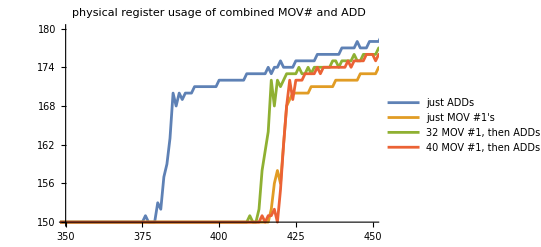

```mathematica
sqrtS15ιmovI32ιadd600=;
sqrtS15ιmovI40ιadd600=;
ListPlot[{sqrtS15ιadd600, sqrtS15ιmovI600 , sqrtS15ιmovI32ιadd600, sqrtS15ιmovI40ιadd600}, 
PlotLabel->"physical register usage of combined MOV# and ADD",
PlotLegends->{"just ADDs", "just MOV #1's", "32 MOV #1, then ADDs", "40 MOV #1, then ADDs"},
PlotRange->{{350, 450}, {150, 180}}, 
Joined->True, 
ImageSize->Scaled[.7]]
```

(Normally I haven’t added “joining” lines between actual data points, but in this case the lines are helpful to guide the eye, even though they exaggerate the noise in the image.)

Hypothesis confirmed! 
Look at how the green curve jumps at close to the same place as the gold curve; ie the MOV# register usage has not removed registers from those available to the ADD.
The red curve (40 rather than 32 MOV #1’s) suggests that there are more than 32 I registers available, perhaps as many as 40.

### how many immediate registers? how many values can they hold?

So the next question is how many of these registers are there really, and how they are “organized”. 
For example one possibility is that there is only a single immediate register, which can hold a single non-zero immediate value (but with multiple references). 
Another possibility is a set of 40 registers, each of which can hold a different immediate. 
Or anything in between, like a CAM that can hold up to 8 distinct values?

First let's try 40 MOV x0, #i before the ADDs. (ie the immediate value ramps from 1 through 2, 3, ... 40)

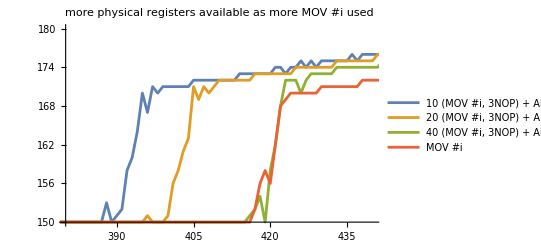

```mathematica
sqrtS15ιmovIV10NOPιadd600=;
sqrtS15ιmovIV20NOPιadd600=;
sqrtS15ιmovIV36ιadd600=;
sqrtS15ιmovIV40ιadd600=;
ListPlot[{sqrtS15ιmovIV10NOPιadd600, sqrtS15ιmovIV20NOPιadd600, sqrtS15ιmovIV40ιadd600, sqrtS15ιmovI600},
PlotLabel->"more physical registers available as more MOV #i used", 
PlotLegends->{"10 (MOV #i, 3NOP) + ADDs", "20 (MOV #i, 3NOP) + ADDs", "40 (MOV #i, 3NOP) + ADDs", "MOV #i"},
PlotRange->{{380, 440}, {150, 180}},Joined->True,
ImageSize->Scaled[.7]]
```

So we see that if we use 10 MOV#i’s, we get essentially 10 additional registers (we max out at 390 rather than 380). Same for 20. 
For 40 we don’t get quite all the way to 420, so the number of additional iRegs appears to be around 36.
Also we are using a different immediate value for every MOV, so we must have at least 36 distinct “storage objects” available.

### what happens when we use up all the immediate registers?

One final test . We know that the I-registers can be written to from Rename. 
Consider the following probe N times (MOV x0, #i   ADD x0,x5,x5   ADD x0,x5,x5   ADD x0,x5,x5).
This produces a curve that jumps at around 416 or so, no surprise, and that has a slope of 8 instructions/cycle, again no surprise. 
But think what the jump at 416 means. 

Presumably there are no more than about 36..40 iRegs. And 416=52*(2+6).
So we know that the first 40 or so MOV#’s are handled at Rename, apparently via being written to special iRegs. What about the (2*52-40=64 MOV #i’s that execute after those first 40, once the 40 iRegs have been allocated?)
One can imagine two possibilities.
• The first is that there are generic write paths from Rename to all registers in the int register file. 
If this is the case, then we should be able to process the 416 or so operations in 52 cycles. 
• Alternatively, if the write paths from Rename to the int register file are only present for the iRegs, then we’d expect the 416 operations to be processed using 20 cycles for the first 160 operations, and then (416-160)/6=43 cycles for the remainder, taking a total of 63 cycles. 

Can we see this difference?
It turns out we don’t actually need to work so hard!

```mathematica
sqrt3ιmovIιadd=;
sqrt4ιmovIιadd=;
sqrtS7ιmovIιadd=;
sqrt1ιmovIιadd=;
sqrtS2ιmovIιadd=;
sqrt2ιmovIιadd=;
p1=ListPlot[{sqrt3ιmovIιadd, sqrt4ιmovIιadd, sqrtS7ιmovIιadd, 
{#, #/8}&/@Range[650], {#, If[#<160, #/8, 20+(#-160)/6]}&/@Range[950]},
PlotLabel->"(MOV# + 3ADDs), long delays",
PlotLabels->{"delay 39", "delay 52", "delay 70", "8-wide", "8- then 6-wide"},
PlotMarkers->{{Automatic, Scaled[.01]}, {Automatic,  Scaled[.01]}, {Automatic,  Scaled[.01]}, {Automatic, Scaled[.005]},  {Automatic, Scaled[.005]}},
ImageSize->Large];
p2=ListPlot[{sqrt1ιmovIιadd, sqrtS2ιmovIιadd, sqrt2ιmovIιadd, 
{#, #/8}&/@Range[650], {#, If[#<160, #/8, 20+(#-160)/6]}&/@Range[950]},
PlotLabel->"(MOV# + 3ADDs), short delays",
PlotLabels->{"delay 13", "delay 20", "delay 26", "8-wide", "8- then 6-wide"},
PlotMarkers->{{Automatic, Scaled[.01]}, {Automatic,  Scaled[.01]}, {Automatic,  Scaled[.01]}, {Automatic, Scaled[.005]},  {Automatic, Scaled[.005]}},
ImageSize->Large];
GraphicsColumn[{p1,p2}]
```

-Graphics-

To make things simpler, I split this into two plots, one showing small delays, one showing longer delays.
The longer delay plot (look at eg delay 39) answers the question that interested us, namely we see a stretch of 6-wide execution before reverting to 8-wide. 
In other words, it appears that only iRegs can be written to from Rename, and when an iReg is not available, MOV# has to run 6-wide.

But beyond this, one might ask about the other details in the plots. 

• What I think is happening is that for short delay, the pattern for every loop iteration is first to use up the iRegs, which are then rapidly released when the delay completes; thus there is a very limited to no window during which no iRegs are available.

• On the other hand assume a longer delay, say 39 cycles. One's first quick thought is that the iRegs should always be used at the start of a loop, then released as soon as head of ROB clears, so should be available again and we should immediately revert to 8-wide. That is what happens on the first iteration through, but it's not what happens long term.

Long term I think what happens if, say, you're running with N=300 and delay of 39 is that iRegs are used when they can be, released at some later time, and land up being spread throughout the ROB rather than being all bunched at the beginning of the ROB. 
And so even when head of ROB clears, that doesn't free all the iRegs right away. In fact it's only if you have N>~420 or so that you provide a long enough period of time after head of ROB clears for all the registers to be freed and the a reversion to 8-wide. 
Later we will see that freeing registers (when it is possible, ie if there's not a delay instruction blocking the head of the ROB) occurs at 16 registers/cycle, which is fast but not infinitely fast.

### summary of experimental findings

So I think the model is that 
- there is a special hardwired zero physical register (ZPR) (which, strangely, appears not to be xzr!) and a MOV #0 is treated as a Rename duplication to that ZPR
- there is a augmentation of the physical register file that can hold perhaps 36 distinct values, and can be treated as part of the register file (can be looked up via RegisterID)
- there is a special write path from Rename to the iRegs, but not generic pRegs, to allow up to two writes from Rename per cycle 
- but these two Rename writes are only possible if free iRegs are available

- thus if Rename sees that an instruction involves the write of a known value AND a free iRegister is available, then Rename will simply write the value and mark the MOV# as complete, so that it doesn't need to pass on to Scheduling and Execute. 
But if any of the conditions fail (not a known value, no free iReg, already both ports to the iRegs are in use) the MOV # is not marked as complete, and it passes on to scheduling for normal execution. 

- MOV # is primarily a latency reduction tool, but it does also give us the effect of a few additional physical registers.

In this context, this LLVM check-in, https://github.com/llvm/llvm-project/commit/d5f1131c812df57560c7563475cb0d674a101636,  from April 2021 is especially interesting, suggesting that pretty much the entire ARM community has concluded that MOVI works better than using xzr. (The context is zero’ing FP registers, but honestly, if anything moving data across to FP should be easier for a dedicated register than handling generic immediates.) 
It’s not clear to me quite why handling a dedicated zero register should be so problematic, but the lesson  of ARMv8 generally seems to be that xzr was probably a reasonable idea in the context of the ISA encoding (ie as a way to encode two or three functionalities in a single instruction) but not a good idea as a way to actually use zero as a value (eg in a MOV).

## Some Register File Implementation Details

You may recall that when we first started looking at exhausting the physical register file we saw some unexpected blips. Now is the time to consider what they tell us. 
Suppose you have to create a register allocator – what are you being asked to do? You need machinery that performs the following tasks
• you need a pool of registers
• you need a way to know which registers are in-use versus which are free
• given the pool of free registers, you need to provide Rename with up to 8 physical registerIDs every cycle. 
Each of these tasks has many further details!

## Structure of the register pool

Consider the pool of registers. We talk about a "register file" but there are many possible implementation details here. 

For example: in Apple's first 64-bit cores, the integer file was in fact split about 40% 32-bit registers and 60% 64-bit registers! This allowed saving some area, and the free register allocator would preferentially provide 32-bit wide registers for instructions taking a w- register rather than an x-register. 
Details here: 2013 https://patents.google.com/patent/US9639369B2 Split register file for operands of different sizes.

Apple no longer does that (at least I can find no evidence for it), but what they do do is split the register file into four banks which can each be individually powered on or off. To put this in context however, we first need to look at how registers are marked free.

## Apple’s implementation of a “free register list”

Obviously one part of freeing registers is having the ROB tell you when a physical register is no longer in use; we'll assume that's a solved problem and ignore it. More interesting is how do you preserve this information of what registers are free? 
One option is to maintain a queue- or list-like structure (so basically an array of slots, newly freed registers go in one end, registers to be allocated come out the other end). This works and is easy to run wide (just pull 4 or 8 or however many you need values from one end), and has been the standard solution for years, hence the usual term free register  list. But this solution limits your control over the process.

Apple have (once again) gone through at least three refinements.

### bitvector (2012)

The first method, (2010) https://patents.google.com/patent/US20120143874A1 Mechanism to Find First Two Values for microprocessors is based on bitvectors. Instead of a queue, imagine that when a physical register is free we flip a bit associated with the register, so that a bitvector consisting of NumPhysicalRegisters bits tells us which registers can be reused. This uses little storage but does require, every cycle, a search along the vector for bits that are set to 1. 
in this earliest version the bitvector is split into two halves, and each half is examined to find two free registers (so that we can find up to four free registers, which is good enough for an A6 class CPU). As an aside, the suggested physical register size is 56 registers! Those were the days.
The real focus of the patent is the circuit for finding two free registers (ie the first two bits set to 1) within a bit vector; done in a recursive fashion, based on groups of three successive bits.

Next is (2012) https://patents.google.com/patent/US20140013085A1 Low power and high performance physical register free list implementation for microprocessors. This is the same bitvector as above but with multiple ways to make this scheme work better (and to scale to finding more free registers). The important ideas are 
• we actually use multiple bitvectors. Remember the older A7 design was 6-wide, so the maximum number of register allocation per cycle is 6. We have three bitvectors which, between them, cover the entire set of free registers. 
So 1/3rd of the free bits live in the first vector, 1/3 in the second, 1/3 in the last. 
• we have three pairs of scanners that run over these three bitvectors, one scanning forwards, one scanning backwards; so each scanner has to find one free bit, and between the 3*2 of them you can find 6 free registers.

• but for this to work well, the free registers have to be evenly distributed over all three bitvectors, and most of the patent is about how that is done. 
• some ideas for how to do this are obvious (like, to the maximum extent you can, if you only need to deliver say 4 registers, deliver them from the two bitvectors that are most full, and don't scan the one that is emptiest).
• but one particular part of the solution is of interest going forward, namely that Apple draws a distinction between two classes of free registers. 

There are, what you might call, “long-term free” registers which have been marked via the bitvector as free. 
There are also what you might call “short-term free” registers (Apple calls these “returning physical registers”) which the ROB has just told the Register Allocator, are free. These are treated differently with the register allocator (as far as feasible) trying to immediately recycle the “short-term free” registers so that, ideally, they do not have to have their setting in the bitvector toggled on, then immediately off again, and to avoid the more power-expensive operation of scanning the bitvectors.

### multiple bitvector banks (2016)

The second stage of evolution we see in (2016) https://patents.google.com/patent/US10372500B1 Register allocation system. This uses a system that’s clearly built on the ideas of 2012, but with additional techniques for saving power. 

The idea is that, as I mentioned, we split our register file into multiple banks (the patent suggests 4, and I suspect that’s still the case; it matches the results I have seen). The most important goal of this banking is to save power by trying to limit (as much as possible) activity to just some of the banks. You only need many physical registers under a few circumstances; much of the time you can do with far fewer. So we want to arrange things to, as far as possible, stick to using registers in as few active banks as possible, and only activate a sleeping bank when really necessary. The patent is about how we do that. 

The details are very low-level, but the overall idea is: as far as possible,  ensure that new register allocations (while building upon a scheme much like the earlier 2012 bitvector scheme) are bunched towards a single register bank. Sounds good, but how to do this?
• One part is fairly obvious, namely the use of a “short-term free” register queue, presumably on the theory that such registers come from register banks that are already powered up. (The usual situation, by far, is that the ROB is not especially occupied, and registers are rapidly used then freed, they normally don’t hang around in the ROB for hundreds of cycles!) 
• The second part is much more ingenious! It still uses the multiple bitvectors of the 2012 patent, but rearranges the mapping of these bitvectors into the register banks so that all the (now eight rather than six) scanners are likely to find free registers in the same single bank. You need to look at the patent to see what’s done, but it is very elegant.

### elide register allocation where possible (2017, not yet implemented)

The third stage of evolution would be some sort of resource amplification, one or more of 
• late register allocation (virtual registers)
• early register release (as soon as there are no users, no need to wait till Retire)
• no register allocation (read the register value directly off the bypass bus). This can be done when architectural register values are immediately overwritten. 

We know that the third option is in limited use for some cracked instructions, and is covered by the patent 2017 https://patents.google.com/patent/US10691457B1 Register allocation using physical register file bypass, which is discussed in more detail below in Register bypassing and early release. 
Today the only case where these are implemented is a few (not all) cracked instruction cases, but this patent suggests we may see these ideas in a future design.
xxx need to do some tests of cracked instructions here, plus analysis of numbers from dougall’s throughput+counter pages

## Power aspects of the register file

I’m always reluctant to blame an anomalous result on “power saving” because that’s too easy, and can be used anywhere! At the very least before making such a claim, I want to have a valid model in mind of how the power saving might work. 
However I think the glitch we saw here is indeed the result of power saving, in the form of the details described above. 

Specifically what I am assuming is something like
- we have four register banks
- under the particular delay conditions that lead to the glitch, while the delay is active 3/4 of the registers (assuming 380 registers, that would be 285 registers) land up active and waiting in the ROB. Pretty much the cycle that the ROB clears is the cycle that allocation moves into the fourth and final bank. All allocation then occurs from this bank while the other three banks run in low power mode. 

- but the timing is such that: remember I said that the times just balanced so that all the free registers were used up in exactly the same number of cycles that the registers were freed from the ROB... So I think what happens is simultaneously 
+ the ADDs are allocating free registers from the one bank that is powered up
+ the ROB is freeing registers that are allocated to the three powered down banks
+ the registers that are freed by the ADDs (which complete very soon) are nonetheless still in the ROB (and not yet marked free) behind all the registers that were allocated during delay

so we get to a cycle where simultaneously
+ the last register is allocated from the powered up bank
+ no registers have yet been released to the powered up bank (though that’s about to happen) 
+ plenty of registers have been released, but they are all allocated to the three powered down banks

Presumably the system copes by powering up one of the powered down banks, and that takes two or three cycles, generating the glitch we see. In theory this might not actually be necessary -- waiting just one cycle would result in the first set of registered from that fourth, powered up bank, being released, but the machine can’t look into the future! 

There are still aspects to this that are unclear. Does this bank power-up delay always suspend register allocation for a few cycles like we are seeing here? Or under normal circumstances does the machine have heuristics that indicate it makes sense to begin power up before everything runs absolutely dry, and that power-up can happen “in the background” without requiring all register allocation to halt?

I’m open to alternative explanations for this glitch, but so far I see nothing I consider reasonable except the above.

## Context switches

A single core will occasionally engage in context switching, sometimes within the same thread (servicing an interrupt), sometimes between threads in the same process, sometimes between processes. Is there any way we can reduce the cost of these?

### dirty flags

Let's begin with the paradigm case, switching between threads in an app. The essentials of how this is done include
- creation of a new thread includes creation of a Thread Control Block, which includes a region of memory that will hold the registers of a thread when it is not running
- switching threads by the OS includes storing all the registers of the old thread to that thread's TCB, then loading all the registers of the new thread from its TCB

One way to reduce this cost is to have some sort of "dirty" flag that is cleared when a new thread is swapped in, and set as soon as the thread uses a register (or more generally, one from a set of registers). It was not uncommon, for example, to do this for either the FP or SIMD registers on the assumptions that many processes did not use these and so time spent context switching them could be avoided. The PowerPC Altivec VRSAVE register is an example.

### hardware based register save/restore

Next up in sophistication is to delegate saving register context switches to the hardware. In principle this would involve steps something like 
- the OS queries the hardware as to the size of a thread storage block (so it knows how large to make a TCB) 
- the threadID/some thread-associated register is the address of the TCB
- a context switch would consist of something like four instructions 
move specialPurposeRegister1 oldThreadID
move specialPurposeRegister2 newThreadID
switchOut specialPurposeRegister1
switchIn specialPurposeRegister2

Done correctly, this in theory allows the CPU to add additional state without requiring an immediate OS update, and allows the CPU to engage in the previous "dirty" flag optimizations without bothering the OS. It also allows optimizations like storing the registers directly to, say, L2 instead of wasting L1 cache space on data that will likely not be reused for many cycles (in principle an OS context switch could do the same thing via non-temporal stores, I don't know if any do).
In practice the one ISA that does this, x86, in the usual x86 fashion screwed up every possible angle of the implementation so no-one actually uses it.

### apple’s 2015 patent (not yet implemented?)

What Apple does is to unite and improve both of these ideas. (2015) https://patents.google.com/patent/US9817664B2 Register caching techniques for thread switches.
The basic ideas are 
- there is some way (unstated, but presumably based on a special purpose register) to indicate the current threadID, and that a context switch has occurred (which could be as simple as changing the value in that SPR)
- after that point, under "ideal" circumstances the hardware will automatically save out old registers and load in new registers
- but it will do it on demand, not as one large block of time that stores all then loads all.

The idea is to add a new field to the mapping table that maps each logical register to a physical register so that the mapping says
x0 is mapped to physical register p3 with a tag of threadID. 
Now imagine what happens right after a context switch. The first new instruction wants to read register x0, so it consults the mapping table. The mapping table tag does not match the current threadID so the following happens:
- we write out p3 as the value of x0, using the threadID tag and some offset algorithm to know where to write x0 in the TCB
- we load in x0 using that same offset, but based on the the new threadID, and we place that new threadID in the mapping table tag for x0
This is the basic idea, and it has as a consequence that writing out and loading in the new register values will be spread out over time, hopefully mostly interleaved with real computation.

There are a number of details to make this more performant. 
- First is that these tags may be associated with more than one register. It would make sense, for example, to have a single tag for two integer registers since loading or storing two is no more expensive than loading or storing one. Presumably you pair these based on statistics about what registers tend to be used together.
- Secondly the stores are straight to L2, without wasting space in L1. It's unclear if this is done at cache line granularity (ie, as an extension of the first point above, aggregate under one tag enough registers to pack a cache line, and store these out sequentially filling a single cache line transfer buffer); or perhaps at some smaller granularity that's an optimal match to the bus width between L1 and L2 (maybe 32B quarter of a cache line?)
- Third the threadID tags are in physical address space, not virtual address space. This I assume makes life easier for the OS, and allows a minor advantage of not having to perform TLB lookups (and perhaps some other slight streamlining relative to a normal load/store). It does make me wonder the nature of the connection between L1 and L2 and how partial lines are handled. This use of a physical address also mean the OS has to be careful about these TCB pages; they can't be swapped out or compressed or similar shenanigans!
- Finally there's an additional flag that is set when a register is modified (ie a dirty flag) to be used in the obvious way, to avoid having to save an unmodified register.

Note also that this means the CPU is capable of doing something very strange, namely creating synthetic instructions, with no warning (and allocating whatever resources they might need) in the middle of the pipeline! This is something I've never heard even remotely considered in any other CPU, and Apple has provided zero patents on it, at least that I've found. These synthetic loads and stores (required to write out the old thread's version of a register and load in the new thread's version) are close enough to normal instructions that they fit nicely into the operand dependency model we're about to discuss. The machine does not stop while the registers are brought up to date, instead the instructions that depend on say x0 are given additional dependencies that they cannot proceed until these synthetic register load/store instructions have completed, but other OoO behavior can as usual route around them. Much later we will see another version of this creation of synthetic instructions when we look at Apple's (currently very limited) use of value speculation. 

Note how nicely general this scheme is. It can (not necessarily unlikely, for the SIMD registers) allow a SIMD register to persist, unreferenced, through multiple context switches and still be there when the initial threadID runs again. It can also easily be adapted (with an appropriate interrupt "threadID", perhaps NULL) to interrupt handling, allowing handlers  to use whatever registers they feel like, and have these transparently saved as appropriate then reverted on return from interrupt.
The one place you have to be careful is: what if a thread moves to a different core? The patent suggests having (Apple custom) instructions that do things like force flush all the modified registers to the TCB. 

The scheme as I have described it is general and could be used for all the registers that are stored during a context switch, which extends to the NZCV flags register, the FPSR floating point status register and possibly various SPR's. As a practical matter, the SIMD registers (and the AMX registers?) are the most likely immediate candidates. My intuition says that even the integer registers would benefit, especially, as I suggested, for interrupts, but who knows exactly what Apple has implemented

It should be pointed out that I have engaged in some correspondence with an author of the 2015 Register caching techniques for thread switches patent. His belief (though he cannot be sure because he left Apple a few months before the patent was filed, let alone any hardware released) is that while the idea is valid and will work, it has not yet been implemented in an Apple core. 

It’s interesting to compare this scheme (perhaps not yet implemented) with the register security tag scheme I described at the very start of this document., and which does appear  to be implemented. The security tag is a much simpler mechanism than context-switching, but is a very nice half-measure. It requires a similar tag associated with each entry of the architectural to logical mapping, a validation of that tag on every access, and machinery to update the tag under certain conditions. But it does not require the subsequent steps of automatically writing registers values out to DRAM, or reading them in from DRAM. 
Hence it would be not crazy to imagine that the context switch mechanism might eventually be implemented, by expanding the existing security mechanism.

### apple’s 2019 patent (reduced context)

Paired with this we have the related but different (2018) https://patents.google.com/patent/US20190220417A1 Context Switch Optimization.
This is a very strange patent, meaning I have to be rather speculative in trying to understand it. The basic idea is very easy: suppose that Apple defines, for some processes, an alternative slightly simplified version of ARMv8 that uses a subset of the registers, for example it uses half the integer and one quarter of the SIMD registers. Defining this is not too hard; it's mainly small modifications to the compiler. But if we do this (for whatever reason) and rely on it, then we want the CPU to flag when we don't follow the rules. Thus we define a reduced processor context (the set of allowed registers), a register (swapped on context switches) that states whether the processor is operating with access to all registers or (possibly more than one alternative) reduced processor context, and some minor machinery to generate an exception when an inappropriate register, for the reduced context mode, is touched.

Now why bother to do this? Hypotheses:
• the 2015 patent sounds good, but if it iss not yet implemented, then the actual cost of context switching remains a notable block of time one might want to reduce. If the OS can define many of the ongoing background processes as reduced context, it can save context switching time.

• even if the previous patent is in place, and even if you modify the compiler to use fewer registers, without some sort of explicit contract, the OS has to allocate a full-sized TCB to hold all the ARMv8 ISA registers. If we want to save some space (again for these many background processes and OS threads) because we know they have minimal register requirements, it's not enough to just compile them with fewer registers, we need to also have the CPU's automatic register saving mechanism incapable of overwriting the bounds of a reduced context TCB.

#### relevant for chinook?

• (most speculative) this has nothing to do with either Firestorm or Icestorm! Few people know that, along with Apple's large and small cores, there is at least one other core they have designed, a tiny core, which is the controller for things like the GPU, NPU, ISP and suchlike. We know that the codename for this core in the A12 was Chinook, and that it is an AArch64 core (apparently with NEON) at the same architecture level as the A12 (eg it provides Pointer Authentication). It would be reasonable to assume, given how Apple has designed the small vs large cores, that this is mostly a "parameterized" version of the basic large core design (ie same overall OoO structure, branch prediction, scheduler, etc) just with even fewer of everything than the small core. 
With that in mind, consider that Icestorm has ~80 physical integer registers and ~88 physical SIMD registers. Maybe Chinook has the bare minimum the design can support without locking up (?34 of each or whatever), and is most performant when actually locked into a subset of these, using 16 integer and 8 SIMD or whatever? 
The justification for this wild speculation is

-Graphics-

with accompanying text (removing some irrelevant parts)

•	The workload of the processors 10A-10B may be characterized as having more frequent context switches than the workload of the CPU processors in the cluster 88. In some cases, the context switches may be much more frequent (e.g. one or more orders of magnitude more frequent). Additionally, the workload of processors 10A-10B may also be characterized by infrequent, but non-zero, use of one or more data types specified in the ISA. For example, in an embodiment, the workload may include infrequent, but non-zero use of vector registers. Accordingly, reducing the context saved and restored in the processors 10A-10B may be significant in terms of improved performance, reduced power consumption, and memory footprint... 
The size of the local memories 100A-100B may be limited, e.g. compared to the memory 92, and storage in the local memories 100A-100B may be used for other data besides the contexts 82A-82B, so reducing the context memory footprint may improve performance as well since more local memory space may be available for process data other than context save data.
	•	The peripherals 98A-98B may be any set of additional hardware functionality included in the SOC 90. For example, the peripherals 98A-98B may include video peripherals such as an image signal processor configured to process image capture data from a camera or other image sensor, display controllers configured to display video data on one or more display devices, graphics processing units (GPUs), video encoder/decoders, scalers, rotators, blenders, etc. The peripherals may include audio peripherals such as microphones, speakers, interfaces to microphones and speakers, audio processors, digital signal processors, mixers, etc.

In other words, although this may seem initially like crazy speculation, I think it’s reasonable to interpret the patent as essentially confirming
• the existence of Chinook
• that it’s used as a general purpose controller all over the SoC
• that it’s essentially a further scaled down Apple small core, not a separately designed bespoke core
• and that Apple makes it “effectively” smaller by things like careful ABI.

It could be argued that any sort of AArch64 OoO design is far more than what’s needed for many of these tasks, but one has to wonder if that’s 1990’s thinking. The Apple solution may use a little extra area (cheap) but in return delivers 
• security (this isn’t a second class core; it gets the full security treatments of all the other Apple cores including things like TLB protections and PAC)
• easy integration with existing developer tools, compiler, and the OS
• enough performance that engineers can spend their time worrying about how to make the entire device better, rather than worrying about how to make an ARM M4 do whatever needs to be done.

## Register bypassing and early release

We've described multiple ways that Apple can make the physical register file appear larger. But they haven't taken the next step in doing so, namely using virtual registers or something similar (for late allocation) and allowing for early register de-allocation.
They clearly have thought about the issue, as in this patent: (2017) https://patents.google.com/patent/US10691457B1 Register allocation using physical register file bypass.

Consider an instruction sequence like REV x0, x0; CLZ x0, x0; ADD x0, x0, x1
Note two things. 

- First the data that is transferred from the REV result into the CLZ input does not need to ever be stored anywhere – there is no way to access it after the CLZ executes. So why not omit allocating a register, and just have the REV read the value from the bypass bus?

- Second the ADD overwrites the value of the x0 output from the CLZ, so even if we did allocate a physical register to the result of the CLZ, why not just deallocate it right away because, once again, no code can access it after the ADD has overwritten logical x0?
This gives us two different techniques for requiring fewer physical registers, one avoiding the allocation of a register by use of a tag, the other allowing for early deallocation of a physical register. 
These are both nice amplification technique -- not incredibly powerful, but also not especially difficult.

However a test on the M1 suggests that, in spite of the patent, neither appears to be implemented, at least not as of the M1. 
The test sequence I used above is drawn from the patent (so you’d hope it would demonstrate the effect, if anything!) However, to simplify the problem I also tried the easier test sequence (no complications as to which execution units different instructions can execute in)
ADD x0, x5, x5; ADD x0, x0, x0; ADD x6, x7, x7; ADD x6, x6, x6; 
ADD x8, x9, x9; ADD x8, x8, x8; ADD x10, x11, x11; ADD x10, x10, x10
As expected this will run at 6 instructions per cycle, but more interesting is, if we add in a delay, how many instructions will execute before the jump (ie how many registers will be allocated). Note that these pairs all satisfy the conditions of the patent – the instruction result is generated to a register which is immediately overwritten by the next instruction. Even so, we see the jump at the usual ~380 instructions, no difference in the apparent register file size.

One might ask why this is not implemented, especially  given that, as we will see, an equivalent is implemented for load/store?

xxx test/explain the cracked case as seen by the performance counter numbers
Before answering this, note is that there are apparently cases where cracked instructions [like ADD (shifted)] are implemented as 
- two instructions where 
- the second instruction reads the intermediate value straight off the bypass bus without allocating a register, as we discussed earlier. 
So why not implement the same mechanism more generally?

I suspect the issue with using tags as the patent describes is that you also need a way to force the two instructions to schedule together – it doesn't do you any good to have the second instruction plan to read the value off the bypass bus if it isn't scheduled immediately after the first instruction. Presumably this tying mechanism exists for the case of cracked instructions, but Apple hasn't yet implemented something allowing generic tying of instructions? Ideally such a solution might be part of a more generic fused instruction mechanism, which is one reason it might be delayed. 

Similarly, consider the failure cases for virtual registers, eg what if, at the point of instruction execution, you discover there is no free physical register available? It's not an impossible problem, but once again  it requires some support machinery that won't exist until you add it. 

What about implementing the alternative of early register release? 
In that case, my guess is the fly in the ointment is the last physical register scheme, a patent I have already referenced, (2019) https://patents.google.com/patent/US20210064376A1.
 Getting that scheme to work along with early deallocation  is not impossible but, once again, it's one more thing that needs to be figured out. It's certainly possible, perhaps even likely, that the initial machinery for these various ideas is in the M1/A14 hidden behind chicken bits, but ready for later release when they're considered 100% working.

## How rapidly can the ROB retire instructions?

We still haven’t nailed down everything register related!
We know that registers are released at Retire (no early release) but how rapidly are they released at Retire? The minimal rate must be 8/cycle (to maintain 8-wide throughput) but could it be larger?

Why do we care about this? If we’re waiting for an integer register to be released when head of ROB clears, what’s the problem if 8 integer registers are released per cycle, given that integer execution can only use 8 integer registers/cycle? The issue is that after a long delaying head of ROB (like a miss to DRAM), there are many instructions, all blocked on different things. 
Yes, there are some integer instructions blocked on an integer register. But there may also be some fp instructions blocked on fp registers, likewise for flag registers. And there may be load or store instructions blocked waiting for load or store queue slots. So ideally when the head of ROB clears, we’d like to run through the ROB as fast as possible, freeing resources as rapidly as possible, so that as much stalled activity as possible can resume as soon as possible!

### retiring NOPs (56/cycle)

Given this insight, let’s start with an easier case. 
We  begin with a delay block consisting of our usual FSQRT, followed by a large number (~1800) of NOPs, followed by instructions that use up all the int registers then wait on them. 
The question of interest is how long it takes to clear the NOPs (ie clear out the head of the ROB) before the ADDs can start work. 
So the structure is 
- delay block of 33 FSQRTs (33*10 =330 cycles; needs to be long enough to be sure everything is packed into the ROB and scheduling queues!)
- delay block of 1800 NOPs (should take 1800/8=225 cycles, to pack the ROB behind the FSQRTs)
- resource depletion block of 370 ADD x0, x5, x5 that should use up all the physical registers
- probe block of variable number of ADD x0, x5, x5
The probe block should not be able to run until more physical registers become available, which cannot happen until both the delay block ends and the NOPs are cleared.

```mathematica
nop1800πadd370πadd2600=;
sqrtS33ιnop1800πadd370πadd2600=;
ListPlot[{sqrtS33ιnop1800πadd370πadd2600, nop1800πadd370πadd2600, {#, #/8}&/@Range[2600]},
PlotLabel->"delay caused by extreme number of NOPs",
PlotLabels->{"1800 NOPs followed by ADDs, with delay", "1800 NOPs followed by ADDs, w/o delay", "8 instructions/cycle"},
ImageSize->700]
```

-Graphics-

```mathematica
(* {2172,330},{2176,336},{2180,348},{2184,356},{2188,377},{2192,381} *)
```

Well that’s nice and clean -- once you figure out the correct probe!
The gold curve is, of course, the non-delayed version. Easy to see the break in the slope as we switch from 8/cycle NOPs to 6/cycle ADDs. 
The obvious fact about the blue curve is that the jump is at ~2180=1800+380, exactly where we’d expect (stall once the ADDs run out of physical registers).
But more significant is that the ramp jump is about 53 cycles. Of course much of that could be because of xxx time, ie the time spent waiting for the FSQRTs to complete, which is not interesting. What we care about is the time spent clearing the ROB after the last FSQRT completes.

We can get better insight into that by varying the number of NOPs.
Consider the image below, where we use the same structure, but vary the number of NOPs from 0 through 450, 900, 1350, to 1800.

```mathematica
sqrtS33ιnop1350πadd370πadd2600=;
sqrtS33ιnop900πadd370πadd2600=;
sqrtS33ιnop450πadd370πadd2600=;
sqrtS33ιnop0πadd370πadd2600=;
ListPlot[{sqrtS33ιnop1800πadd370πadd2600,sqrtS33ιnop1350πadd370πadd2600,sqrtS33ιnop900πadd370πadd2600,sqrtS33ιnop450πadd370πadd2600,sqrtS33ιnop0πadd370πadd2600},PlotLabel->"delay caused by varying number of NOPs",PlotLabels->{"1800 NOPs","1350 NOPs","900 NOPs","450 NOPs","0 NOPs"},ImageSize->Large]
```

-Graphics-

There’s clearly a variable delay (look at the size of the jump) from when the machine stalls until when ADDs start being processed again, and that stall grows as the number of NOPs grows. 
What’s the exact relationship? Let’s zoom into the relevant part of the image and add some guide lines.

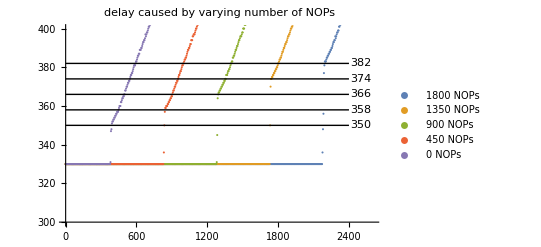

```mathematica
p1=ListPlot[{sqrtS33ιnop1800πadd370πadd2600, sqrtS33ιnop1350πadd370πadd2600, sqrtS33ιnop900πadd370πadd2600, sqrtS33ιnop450πadd370πadd2600, 
sqrtS33ιnop0πadd370πadd2600},
PlotLabel->"delay caused by varying number of NOPs",
PlotLegends->{"1800 NOPs", "1350 NOPs", "900 NOPs", "450 NOPs", "0 NOPs"},
PlotRange->{300, 400}];
p2=Graphics[{Line[{{0, 330+20+8#}, {2400, 330+20+8#}}],Text[330+20+8#, {2500, 330+20+8#}]}&
/@Range[0, 4]];
Show[p1, p2, ImageSize->Scaled[.75]]
```

This image looks messy but really all we have done is zoom in on the interesting part of the original image (the jumps) and overlay some lines. 
There’s room for disagreement, but to my eye the lines are plausible cycle values at which the ramp of each curve starts. 
The interesting point is that the lines tell us the amount of delay (the time it takes to again start processing ADDs from when the machine stalled.
There is a baseline delay of 20 cycles (even with no NOPs). More interesting is that the additional delay increases by 8 cycles for every 450 NOPs. 

So the time it takes the ROB to clear 450 NOPs is 8 cycles, ie the machine clears 450/8=56 NOPs/cycle!

#### structure of the ROB

We will see evidence for this later as we cover load/store and branches; but in fact the ROB is best thought of as consisting of ~330 “rows” where each row can hold 7 instructions. Most instructions can go in any slot, but “failable” instructions must go in the last slot (which provides extra storage). Failable instructions are those that might require the CPU to flush and restart. These can be branches (mispredicted...) or loads/stores (possibly some exception conditions, but the main case I am thinking of is a load/store dependency misprediction when a load occurs out of order relative to a store and so reads possibly invalid data [all to be explained later].

The usual structure of the ROB, when not running weird test code, will look something like maybe two or three instructions in a row, then a load at the end of the row, then maybe five instructions, then a branch terminating that row, and so on. The ROB slots are cheap, so Apple is happy to give us thousands of them! The real constraints in real code will be either load/store/branches filling up the ~330 failable ROB slots, or int/fp code using up all the HF slots. 

So a better way to think of Retire is that Retire can clear 8 ROB rows per cycle. This can ultimately mean clearing as few as 8 instructions (if we had eg a sequence of eight successive loads, or some combination of successive loads, stores, and branches but nothing else). Or it could mean as many as 8*7=56 instructions if every one of the eight rows was fully populated. 

A slightly more sophisticated way to think of this is that the ROB is required to track one part of recovery from speculation failure (branch misprediction or load/store dependency misprediction) while the History File (and checkpoints) track a different part of this recovery. In other words, as I keep stressing, only the failable slot of a 7-entry row of the ROB actually matters; the other 6 slots just hold “inert” entries from instructions giving their ordering, but they are never used.
 
Hence an obvious question  is: why even have the other 6 instruction slots? We can treat the ROB as ~330 entries which hold a pair (failable instruction, 3-bit counter) and the 3-bit counter describes how many instructions would have been in the other 6 slots. 
(Why not allow then allow 1+7 entries instead of 1+6? Presumably the case of the counter as all 1’s or all 0’s is treated specially in some way, eg as a synchronization of some sort? or that case means the entry is invalid?)
This scheme is not visible to an outside tester, but seems a reasonable way to save a few transistors and a little energy. 
This refinement was suggested to me by Arthur V.

### freeing up registers and HF slots (16/cycle)

That's fairly impressive, but clearing NOPs is easy. What about a more difficult task like restoring registers?
The plan now is to replace the NOPs with FABS, which will use up slots in the History File. How many registers can be freed per cycle?
We  want to use enough FABS to make the phenomenon visible, but not so many that we flood the History File with floating point register manipulations and don’t leave space for all the ADDs. Using a maximum of 278 FABs seemed to do OK. 
If those can be cleared at 56/cycle, clearing the whole 278 will take 5 cycles. 
Hopefully we can see that against the 20 cycle baseline (and the noise that will arise from using FP for both this timing and the delay.

```mathematica
sqrt33ιfabs0πadd800=;
sqrt33ιfabs278πadd800=;
sqrt33ιfabs70πadd800=;
sqrt33ιfabs139πadd800=;
sqrt33ιfabs209πadd800=;
sqrt33ιcmp50πfabs278πadd800=;
p1=ListPlot[{sqrt33ιfabs278πadd800, sqrt33ιfabs209πadd800, sqrt33ιfabs139πadd800, sqrt33ιfabs70πadd800, sqrt33ιfabs0πadd800},
PlotLabel->"blocking the ROB with fp registers",
PlotLabels->{"delay+ 278F ABS+ ADD", "delay+ 209 FABS+ ADD", "delay+ 139 FABS+ ADD", "delay+ 70 FABS+ ADD", "delay+ 0 FABS+ ADD"}, ImageSize->Large];
p2=Graphics[Line[{{0, 330+20+4#}, {800, 330+20+4#}}]]&/@Range[0, 4];
Show[p1, ImageSize->Large]
```

-Graphics-

Well clearly the delay is a lot longer than 5 cycles! So let’s use the same “step through quartiles” trick we used for NOPs, and zoom in.

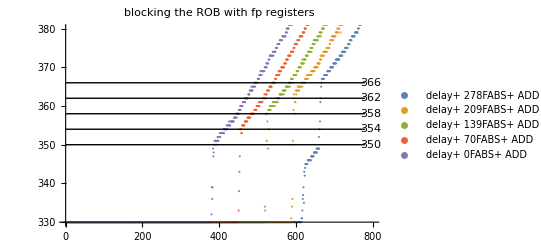

```mathematica
p1=ListPlot[{sqrt33ιfabs278πadd800, sqrt33ιfabs209πadd800, sqrt33ιfabs139πadd800, sqrt33ιfabs70πadd800, sqrt33ιfabs0πadd800},
PlotLabel->"blocking the ROB with fp registers",
PlotLegends->{"delay+ 278FABS+ ADD", "delay+ 209FABS+ ADD", "delay+ 139FABS+ ADD", "delay+ 70FABS+ ADD", "delay+ 0FABS+ ADD"},
PlotRange->{330, 380}];
p2=Graphics[{Line[{{0, 330+20+4#}, {780, 330+20+4#}}],Text[330+20+4#, {795, 330+20+4#}]}&
/@Range[0, 4]];

Show[p1, p2, ImageSize->400]
```

I think it’s legitimate to see clearing 70 FABS from the ROB as taking 4 cycles, so 17.5 clearances/cycle. Probably best to read that as 16 per cycle.

We can attempt to validate the above hypotheses by prepending, before the 278 FABS that use up physical FP registers, 50 CMPs that use up physical flags registers. If our hypothesis is correct, this should result in an additional delay of another three cycles (50/16=3).

```mathematica
p1=ListPlot[{sqrt33ιfabs278πadd800, sqrt33ιcmp50πfabs278πadd800},
PlotLabel->"blocking the ROB with non-integer registers",
PlotLabels->{"delay+ 278FABS+ ADD", "delay+ 50CMP+ 278FABS+ ADD"}, ImageSize->Large];
p2=Graphics[{Line[{{0, 330+36+3#}, {780, 330+36+3#}}],Text[330+36+3#, {795, 330+36+3#}]}&
/@Range[0, 1]];
Show[p1, p2, ImageSize->650]
```

-Graphics-

We see the point is validated; an additional delay by what can plausibly be viewed as an additional three cycles.
Obviously the methodology I am employing is not great for incontrovertible, exact measurements! But I’m interested here in large-scale exploration to figure out the overall design of the system; I’ll leave it to others coming later to perform the high precision experiments.

Experts might want to know why the curves show two jumps. Consider the blue curve, and compare with the previous graph.
The ADDs face two possible constraints: physical registers and HF slots. 
When there are not too many FABS enqueued (the cases of 70, 139, 209 FABS above), then the ADDs run out of physical registers first and block.
But when there are enough FABS enqueued (the case of 278 FABS) then the first constraint that is hit is running out of HF slots. 
After the FSQRTs clear the FABS start to clear, and HF slots are released. This allows ADDs to restart for a few cycles – until they now run out of physical registers. The FABS HF slots were releasing FP, not integer physical registers.
The CMP case is an even stronger version of this. Think about it. In the CMP (gold curve) case at any given N value, 50 fewer ADDs have been enqueued than for the blue curve case. We still run out of HF slots at the same point because CMP, FABS, and ADD all use up slots from the same HF pool; but once HF slots start to be freed, there are 50 more integer physical registers available than in the blue curve case, hence the intermediate run before the second delay (running out of integer physical registers) can proceed until N is 50 operations higher.

#### freeing just HF slots, not registers (also 16/cycle)

There’s one more thing we need to test.
To clear entries from the ROB to eventually free up those integer registers, we have to 
- clear entries in the HF, and 
-  release registers to the free list. 
It’s possible that these two tasks take a different amount of time (for example releasing HF slots happens rapidly, but then moving registers onto a free list so that they are available for reuse happens at a slower rate.

So let’s try a variant that doesn’t involve freeing registers, just HF slots. 
Replace the FABS with FMOV d31, 30. The idea is that while clearing a FABS entry from the HF involves freeing an actual physical register, almost every FP HF entry only records a change in the mapping tables; it doesn’t actually change a register to be free to move to the free list. The idea is to test if manipulating physical registers in Retire is slower than manipulating HF entries.

```mathematica
sqrt33ιfmov278πadd1000=;
ListPlot[{sqrt33ιfabs278πadd800, sqrt33ιcmp50πfabs278πadd800, sqrt33ιfmov278πadd1000},
PlotLabel->"blocking the ROB with non-integer registers, FMOV version",
PlotLabels->{"delay+ 278FABS+ ADD", "delay+ 50CMP+ 278FABS+ ADD", "delay+ 278FMOV+ ADD"}, 
PlotStyle->PointSize[Small],
ImageSize->Large]
```

-Graphics-

As you can see there is no difference! 
It appears that HF slots and registers are both freed at 16/cycle, there’s no faster path for HF slots that are not freeing a physical register.

### so how close is the M1 to a KIP (kilo-instruction processor)?

Just as a fun exercise, how close is Apple to a KIP (kilo-instruction processor)? 
A KIP has been the CPU designer’s dream since ~2000CE, ie a design that can maintain “in progress” one thousand instructions, the idea being (at the time the phrase was coined) that this would be enough usually to keep a CPU from stalling even if a load missed all the way to DRAM. Unfortunately as CPUs have become higher GHz and wider, 1000 instructions is no longer enough (if a miss costs you, say, 330 cycles, and you’re 8-wide, you’d like to be able to power through 8*330 instructions before stalling), but the number is still a good milestone. 

Obviously Apple is way beyond this 1000 limit in trivial fashion (sequence of NOPs) but what about real code?

As explained, the ROB size itself is not a problem, it’s various other structures that are more difficult to scale up (eg LSQ, physical register files, history file) and we have seen how Apple has continually disaggregated or rethought these into different structures that scale better (perhaps parallel structures like the banked physical register file, perhaps move the most difficult to scale part out of a structure as we will see with the splitting of the traditional Load Queue into the LEQ and the LRQ). 
Given all this, if we want to pack as many “real” instructions into the ROB as possible, what are the limits?

The first is that anything that changes a register will use a History File slot, and we have ~620 of those. But we also have some instructions that don’t change the register file, most notably stores and branches. Unfortunately stores and branches (and loads) use the same “failable” slot of the ROB, even the simplest non-problematic and non-conditional branches like “B .+4”, so we might as well just use stores (since branches are also limited by other data structures beyond the number of failables).

If we use the probe ( ADD x0, x5, x5; FABS d0, d0; STR x5 [x2]  ) we can in fact reach about 310 iterations of this before he see a jump! 
So ~930 realistic’ish instructions! Not bad! It might be possible to go slightly beyond this with a few other instruction classes; I didn’t push the issue.

## Loads and Stores

## Experiments to test LSQ sizes

### first attempt at testing queue sizes (FSQRT based)

We' ve so far explored some aspects of the ROB, and the size of the physical register files. Now let’s explore the size of the load/store queue.

```mathematica
sqrtS11ιld=;
sqrtS10ιld=;
ListPlot[{sqrtS10ιld, sqrtS11ιld}, 
PlotLabel->"independent loads with an FSQRT delay",
PlotLabels->{"10 FSQRT delay", "11 FSQRT delay"}, ImageSize->Large]
```

-Graphics-

The gold curve gives us the immediate info of interest, a jump at ~330, which would suggests that the LSQ can hold 328 loads. But there are unexpected issues here!
- First is that the limit seems suspiciously close to the size of what I have called the “failables” part of the ROB; ie the limit looks like how many loads we can hold in the ROB, not in the LSQ. 
- Second is that we don’t seem to actually lose any cycles! Yes we have the jump at ~330, but that’s followed by a regime where we appear to be executing loads at 4/cycle rather than 3/cycle, till we get back on trend! 
So there’s something weird going on.

Do we get the same behavior for stores?

```mathematica
sqrtS15ιst=;
sqrtS18ιst=;
ListPlot[{sqrtS15ιst, sqrtS18ιst},
PlotLabel->"independent stores with an FSQRT delay",
PlotLabels->{"15 FSQRT delay", "18 FSQRT delay"}, 
ImageSize->Large]
```

-Graphics-

```mathematica
simpleFSQRTDelayLoadStorePlot=ListPlot[{sqrtS18ιst, #+{0, 70}&/@sqrtS11ιld}, 
PlotLabel->"independent stores lined up against independent loads",
PlotLabels->{"stores", "vertically shifted loads"},
ImageSize->Large]
```

-Graphics-

We see exactly the same pattern for loads and store (ie 
- same jump at ~330, 
- same running at about 4-wide till N=~420).
The difference in slopes after that arises from M1 having 
- 2 load units
- 1 store unit
- 1 ambidextrous unit
so that it can run either 3 loads/cycle or 2 stores/cycle. 
These results seem ...unlikely... They indicate a massively large load-store queue, same sized for loads and stores.

### second attempt at testing queue sizes (miss-to-DRAM based)

Let’s try a different tactic. Instead of using our trusty FSQRT as a delay block, we’ll use a delay block based on loads that continually miss to DRAM.

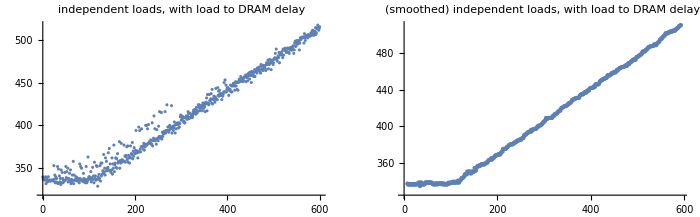

```mathematica
ld330ιld=;
p1=ListPlot[ld330ιld,
PlotLabel->"independent loads, with load to DRAM delay"]; 
p2=ListPlot[MovingMedian[ld330ιld,15],
PlotLabel->"(smoothed) independent loads, with load to DRAM delay"];
loadQueueSizewithDRAMDelayPlot=GraphicsRow[{p1, p2}, ImageSize->700]
```

As you can see, the problem with using a load delay is that there’s a lot of noise in the signal, and while we can reduce this (at the cost of much longer runtimes) we’ll be cheap and just use a smoothing filter (moving median) to make it easier to see the point. And the point is that, with this delay, as opposed to with an FSQRT delay, there’s a discontinuity at N=~125!

We see the same pattern with stores, in this case with a discontinuity at around 100 stores:

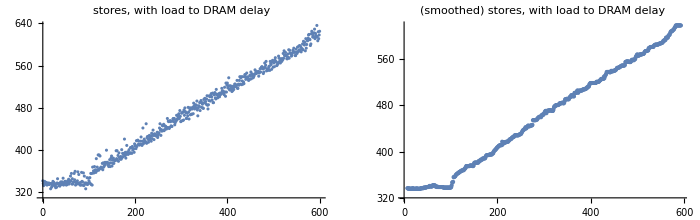

```mathematica
ld330ιst=;
p1S=ListPlot[ld330ιst,
PlotLabel->"stores, with load to DRAM delay"]; 
p2S=ListPlot[MovingMedian[ld330ιst,15],
PlotLabel->"(smoothed) stores, with load to DRAM delay"];
GraphicsRow[{p1S, p2S}, ImageSize->700]
```

So we find ourselves with the following conclusions:
• there appears to be load queue, of size ~125 loads
• there appears to be store queue, of size ~100 stores
• but these do not behave like our previous constrained resource tests!

Clearly we need to understand exactly what the load/store queue(s) do, how they work, and how they can be optimized.

## Theory of the load store queue

The load/store queue is a large, complicated subject. Even more so than the rest of the CPU, there are technicalities in this area that are specific to x86, or specific to Intel, but which are not universal constraints on how things have to be done. Be open-minded!

### why do we need a store queue?

First the store side: Why do we need a Store Queue at all? 
Once we have a speculative CPU, this means that we are going to be executing speculative stores. But we cannot allow such stores into the cache for two reasons, one obvious, one slightly less so.
- The obvious reason is that if you overwrite a value in the cache, then discover that the path of execution was misspeculated, what can you do? You can't undo the write and recover the previous value that you overwrote!
- Less obvious is that once you write to the cache then, (more or less), that value, although still speculative, becomes visible to other CPUs via snooping, and once again, you can't undo whatever those CPUs do in response to that snooping, even if you want to undo the write.

So we need somewhere to hold each pending store until that store becomes non-speculative.
It is traditional to make this storage a queue, with the oldest stores at the end and newest at the beginning. The reason for this temporal order is that the code may very well generate multiple stores to the same address, so you need to be careful about the ordering of stores (and also, as we will see, of loads). Remember that our CPU is out of order...
So imagine code that looks like this 
store xM into xA
...
store xN into xB+xC
...
It is possible that xA=xB+xC. It's also possible that one of these stores may execute in reversed order, eg maybe xA is generated by a slow load, whereas xB and xC are already available in their registers. If we don't get ordering correct, we'll store xN, then overwrite it with xM, ie the reverse of correct program order...

So the basic idea becomes clear. To ensure correct store behavior given both speculation and out-of-order execution, we want something like
- a time ordered queue to hold stores, for which 
- each slot looks something like (store address, store data, various flags [valid, free, etc]) 
- queue slots allocated at Rename (ie at a point where the instructions are still in order)

And the most basic flow looks something like 
1) allocate a store queue slot at Rename
2) store sits in the issue queue for the LS unit until both its (store address and store data) dependencies are satisfied
3) (store address, store data) are written to the queue slot
4)  ...at some later point... the store address has to be tested against the TLB to make sure there are no permission issues, no VM fault, etc
5) the store instruction reaches the head of the ROB. Assuming the TLB issues didn't generate a fault, the store can complete.
6) ...at some even later point... the store data is written to cache, and the store queue entry is freed. 

Pretty much every step here has interesting non-obvious wrinkles, and we'll return to them, but for now accept this framework.

### why do we need a load queue?

Now think about loads. Why do we need a load queue? Well think about this:
We have a bunch of pending data in the store queue, and loads whose addresses match those earlier stores have to get their data from the store queue, not the stale data in the cache. 
And they have to get the correct version of the data, the latest version that was stored just before the load, from the store queue.

It is for this reason that we generally talk about the LSQ as a single queue that holds loads and stores. This becomes clear when you think of loads, and remember that loads can also happen out of order relative to each other, and relative to stores. 
The idea, then, in this most basic model, is that a single LSQ has slots that hold both loads and stores, allocated in program order at Rename. Then, 
- when a load executes, it scans the LSQ backwards in time from its position, looking for the nearest store slot with a matching address, and reads that data.
- when a store executes, it scans forward in time, looking for every load slot (there maybe more than one) with a matching address, and feeds that slots its store data. 

This model has to deal with various dependencies you may not have thought of that have to resolve before load or store execution can proceed. 
For example:
Suppose that (once again, out of order!) you're a load looking along the queue backwards in time to find a matching address. Maybe some of those stores
-  have not executed yet, 
- so there are slots that you know are store slots, 
- but the address has not yet been recorded. 
What to do? In the model we have described so far, we have to delay execution of the load until we can be sure that every earlier storage slot has its address attached, so that  we can be sure we read the correct data from the store slot if there is a matching earlier address.

So, then, the basic load instruction cycle is something like
11) allocate a load slot, in order, at Rename, from the common LSQ
12) load sits in the issue queue for the LS unit until its (address) dependencies are satisfied
13) load scans backwards in time along the LSQ looking for matching addresses. 
14) if there are any holes in that scan (ie stores with unresolved addresses), wait till they are filled
15) if there are matching addresses, grab the data from the nearest match, otherwise from the cache
16) ... at some point in the previous 3 steps, validate TLB/faulting/permission issues...
17) load instruction reaches head of the ROB, and its LSQ slot can be freed 

Note also that we now realize we needed to include a (3a) step for stores, involving scanning the LSQ forward for matching load addresses. 
And we're just getting started!

### speeding up the basic design

So with this pool of ideas in place, let's now consider various issues.
Of all the complications, the biggest is the problem of loads and stores possibly having the same address. Forcing loads to delay for every store loses us a hefty fraction of our OoO performance. And, of course, most of the time loads and stores are to different addresses! We are making the machine run a lot slower for a case that's very rare – but has to be handled correctly when it happens. 
Specifically:
• if we know a load doesn't match an earlier store (and the same in reverse, a store doesn't match a later load) then we don't have to worry about this business of making sure data goes to the correct additional slots, we can just do the obvious thing – for a store, hold onto the store data in the store slot; for a load, read the data from the L1 cache. 
So we'd like to know about a load/store address collision ASAP.

#### split store address from store data

So this leads to the first, easiest part of a a better solution: realize that a store may be able to resolve its address long before its store data is known. 

If you can attach an address to a store slot, OK, any load that reads from that address will have to delay until the data is available. But all the other loads (and this is most of them) with different addresses can go ahead, all they care about is that an earlier slot is not relevant to them, and won't acquire an address that becomes relevant to them.
You are probably well aware that, for example, x86 splits stores into two operations, one corresponding to the store address, the other to the store data, and each is separately scheduled. Every performance CPU now does the same thing conceptually, though they may implement it rather differently.

#### predict load/store dependency

Alternatively, or in addition to, separating the store address from the store data, you can build a predictor that predicts whether a load is likely to depend on a recent earlier store. Then what you can do is run step 13 as before, but if step 14 shows missing store addresses, consult the predictor and either wait or just assume there won't be a relevant store that later occurs, and go ahead. 
This is, of course, a new form of speculation ("load/store" or "address alias" speculation) but fortunately it can be handled by our existing machinery like the ROB. What's necessary  is to validate that when every relevant earlier store slot has its address eventually filled in, that address did not collide with the load that we (LS-speculatively) executed and whose data we (LS-speculatively) pulled in from the L1 cache. 

If there is an address match, we 
- mark the load in the ROB as misspeculated, 
- update the LS predictor, 
- flush the bad load and every subsequent instruction, 
- restore state, and start again; much like a branch misprediction. 

(Note that I was a little quick above – if we're clever, we can actually compare the later stored data to the data used by the load from the cache. If they are the same [and you'd be amazed how often they are, many many stores are the same thing repeatedly stored to the same address] then no harm no foul! No need to create drama and go through a recovery process...
This is possible in theory. I’m unaware of whether any cores actually implement this optimization.)

It is a fortunate fact that LS dependence prediction is surprisingly easy, and predictors are remarkably accurate, way above 99% for most code most of the time; it's a much easier problem than branch prediction.

Let’s now consider a basic LSDP (load store dependence predictor) in more detail; how it might work to see how it might be improved. 
The basic flow is as we have described
- we have an early store A, and a later load B
- store A does not execute for a while because its store address is not available
- load B executes optimistically 
- when store A actually executes, it notes the overlap of its address with load B and raises an alert
So what the predictor should warn us about is that load B depends on store A. But how exactly will it do this? 
The prediction cannot be based on the store and load addresses because we don’t know those! Specifically, if store address A had not been delayed (ie unknown), we would not have had to speculate on whether its address did or did not match load B!
How about we identify store A and load B by their PCs, PCa and PCb? Obviously this may not be perfect, but speculation is about what usually works, not what’s perfect, and using PCs to track probably colliding load/store pairs works very well. 
So we imagine the LSDP as essentially a table of (storePCa collides with loadPCb) pairs.

Now how would we use such a table? 
The simplest idea is at some point in the pipeline we check the PC of each load against the table. In event of a match we mark this load as “pessimistic” and do not allow it to execute until every earlier store address is known. 
That will work, and is already a good start, but now let’s consider various sub-optimal aspects of this implementation.

- as described this mechanism does not allow for multiple loads that depend on the same store. This could be dumb code (multiple successive loads from the same address) or reasonable code (store a 4-element SIMD vector, then successively load each of the four elements as scalars for subsequent processing). This is an easy fix that you can imagine for yourself.
- there’s also the possible reverse problem, where a load depends on multiple stores (so store four successive scalar values, then load them as a SIMD vector)
- we are being too pessimistic, waiting for every earlier store to execute, not just the store(s) that affect this particular load
- as described, once a load/store pair is in the predictor, it’s there forever! There’s no mechanism for removing entries from the predictor once they become irrelevant. 
- a silly (but necessary) concern is that essentially this mechanism as described above, specifically the recording of load/store PC pairs, is the subject of a patent by the very litigious WARF (University of Wisconsin).

#### splitting the single load-store queue into separate load and store queues

We now know why 
- an LSQ exists, 
- why it’s (conceptually treated as) a single queue, 
- the issues around why you want time ordering of the (load and store) addresses, and 
- what to do about missing addresses. 

So consider resource issues:
If we want to hold up to, say, ~600 pending speculative instructions (size of History File), and we expect ~half of them to be loads or stores, we need ~300 LSQ slots. When we run out of LSQ slots, like all resource allocation under the traditional model, Rename stalls until the rest of the pipeline makes some progress, so eventually a load or store reaches the head of the ROB, is retired, and its slot is freed. 

But a large LSQ is not cheap!The problem is not so much the area of the queue, to hold all the addresses and store data; the problem is that 
- every time a load or store executes, it has to compare its address against so many other pending addresses, and the logic structure that does that (called a CAM) is power hungry, growing worse as there are more and more addresses to compare. 
- and with a single queue, we have to waste power checking every address against every other, even though stores only want to compare against load addresses, and vice versa. 

What can we do to improve life?
The original model I described, before load/store dependence speculation, is essentially what we saw in something like the MIPS10000 in late 1990s. 
The x86 equivalent at the time only required a store queue because all loads and stores were executed in order relative to each other. (Meaning loads occasionally pulled their data out of the store queue, but there was never a situation where store queue entries had not yet been filled in, or a case where a store could generate data that should have been read by an earlier load).

IBM POWER4 (2002) takes us a long way to the full model I have described here. They have out of order load and store execution, and they have prediction of whether loads will alias with earlier stores. What IBM do at this point, and what seems to be the standard going forward, is to split the model I have described into two parts.
Imagine separate load and store queues (now possibly of different lengths) for which each queue entry has a few bits that we can call an “age”. 
Rename allocates ages as a single (continually increasing) stream that’s common to loads and stores, but stores get store buffers from the SQ, loads get load buffers from the LQ. 
Each buffer, at allocation time, has its age stored in the age slot. We still require that loads scan the store queue looking for earlier stores with a matching address, but they now find where to start the scan by finding an appropriate age marker; likewise for stores looking in the load queue. 
You’ve 
 - given up a small amount of the ordering info in the single LSQ, 
 - but you have less work 
 - also each queue (and so each pool of addresses) is smaller, even though the total number of Load and Store Queue slots together can be larger.
 You can now also start to optimize each queue separately for its particular tasks, giving it a slightly different logic structure.

## Non-standard ideas for improving the LSQ

### use the store queue as a L0 data cache

At this point you can make the following observation: 
- on every load you have to pay the price for accessing the SQ (to match the load address with possible store addresses). 
- And if you hit a load in the LSQ you don't have to pay the price of accessing L1 (because the store data is in the Store Queue entry) 
- Therefore you might as well try to store as much in the LSQ as possible! 
This leads you to try to structure things so that after stores retire, and even after the data is written out to cache, you try to hold onto every store queue entry (marked as valid, but free) for as long as possible, so that you can maximize the number of load hits to the storage queue. 

This idea (and the mechanics of how to implement it) are discussed here: (2019) https://www.diva-portal.org/smash/get/diva2:1316126/FULLTEXT02 Filter Caching for Free: The Untapped Potential of the Store-Buffer.
(This works surprisingly well. On Skylake sized machines, you can get 30 to 50% hit rate, saving around 15% of the energy used by the load/store/L1D subsystem!)
Is Apple doing this? As a pure energy savings measure, with no performance impact, it’s hard to test. I have seen nothing in the patent record, but if there’s nothing to patent beyond the basic idea...

### two level LSQ

This is nice, but we still want larger load/store queues, and they are still expensive!
A very nice alternative is described in (2005) http://webdiis.unizar.es/~ktm/papers/ISCA_05_v4_final.pdf Store Buffer Design in First-Level Multibanked Data Caches.
This paper points out a version of a design principle that’s, as I have tried to stress, very dear to Apple: don’t use one hardware structure to do two jobs!
The Store Queue does three different things:
- it enforces correctness by holding stores until they are not speculative
- it enforces correctness by ensuring correct load/store ordering
- it provides performance by forwarding pending stores to loads accessing those store addresses.

But an interesting fact is that most load/store forwarding happens with loads that are very close to their stores. This means you can split these structures into two:
- a store-forwarding buffer that is optimized for speed. It only holds about a fifth of the store queue entries , it’s a simple FIFO (so no complex logic to figure out what is or is not held). It supplies the first matching store to a load, which in theory may not be correct but is usually good enough. And it’s multi-ported enough to be probed and read-out by three simultaneous loads per cycle
- a “traditional” store queue which is concerned with correctness, but doesn’t have to be fast or multi-ported enough to handle three loads every cycle. 
The idea is that most loads that are going to match to a store are (correctly) handled by the small fast buffer, and anything that slips through the cracks is handled by the large buffer, as a Replay or even a Flush, but this should rarely be necessary. 

The paper itself also talks about many other things; some are design options irrelevant to our interests, but it’s nice in being above average in how well it explains some of the background to Store Queue issues and options in resolving them. 
(Haithim Akkary earlier proposed a two level STQ in the grand KIP paper to which we’ve referred many times, but does a terrible job, IMHO, in explaining why it’s interesting or how it should be structured.)

### virtual LSQ

More interesting is a step IBM took a few year after POWER4, with POWER7 in 2011, which is to “virtualize” much of the load/store queue. 

Just as we discussed with registers, the standard LSQ model uses early allocation (at Rename) and late release (at Retire) of LSQ entries. 
This means that much of the time the LSQ entry is marked as not free, but is not being used productively; 
- much of the time it's empty waiting until the load or store executes, or 
- it's long after everything relevant to the load or store executed, but the instruction is being blocked by something at the head of ROB and until then the LSQ entry cannot be released. 
And as before, this is because in the most obvious LSQ model, or even, the fancier POWER4 split LQ and SQ model, you need allocation at Rename to attach ordering requirements to the LSQ entries. 

So how to work around this?
What I am calling age tags are still allocated at Rename, in program order, across loads and stores in increasing order. 
But the actual load and store buffers are not allocated until the instructions are ready to execute as they leave the Scheduling Queue. 
This means that you maintain can ordering across a large pool of loads and stores (use more bits for the age tag) while using a smaller pool of Load and Store Queue entries (and thus addresses you have to check). Most of the entries in the virtual Load Store Queue (ie load/store instructions ordered by age tag) will spend much of their time in the Scheduling Queue, not in the Load and Store Queues.

As with virtual registers, if you temporarily run out of physical backing store (load or store queue slots) the addresses will pile up in the Load Store Scheduler, not in Rename, so more of the machine can make progress (even while load and/or store are temporarily blocked, other instructions can still move on to the integer and FP pipelines).

You can see some of the issues involved in a design like this (along with a more careful explanation of the various scans of the load store queue for various purposes) here: (2007) http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.140.3533&rep=rep1&type=pdf Late-Binding: Enabling Unordered Load-Store Queues.

Apple definitely seem to be using a virtual LSQ (evidence in the experiments section below). Different patents suggest that what Apple variously calls the GNUM (retirement group number), or the RNUM (reorder buffer number), or the LNUM (load queue? number) are used as the ordering property for load/stores, fulfilling the role that I called "age bits" when describing POWER4.

Late resource allocation is a nice resource amplifier, with the flip side of the idea being early resource release. For example if there is no older store ahead of a load with an unknown address, then there is no possibility of the load having been mispredicted as not matching a store, and so having loaded stale data from the cache. In other words, under these circumstances, there is no need to continue to hold onto the Load Queue entry. 
Again the experiments (with some patent validation) show that Apple is using early release of both Load and Store Queue entries.

## Apple’s implementation of load store dependency

### 2009 (load referenced by instruction count relative to store)

We start with a very basic 2009 https://patents.google.com/patent/US20100205384A1 Store hit load predictor. (If you look at the inventor name on that patent and think Apocalypse Now or, even better, Zeroville, you are clearly way too much of a movie geek!)

Like most of the early (pre-A7_ patents there are interesting ideas here, but ultimately things changed a lot. 
In this early version, noteworthy points are that 
- stores are tracked by PC.
- problematic loads are tracked by an offset (number of instruction in the instruction steam) relative to the problematic store. 
This is clearly an end-run around the patent, but it works!
- the scheme can track a load dependent on multiple stores, but not a store that affects multiple loads.

The essential idea is 
- when a store (not a load) passes through Mapping, its address is compared with the store addresses in the predictor. 
- if there is a match, the associated count in the predictor’s entry for that store is read. 
- we now start counting instructions and if we see a load <count> instructions after the store, then that's a load that needs to be handled carefully. 
- we know the SCH# of the earlier store, and we add that SCH# to the dependency list of the load. 
Isn't that cool? Another lovely case enabled by the dependency bitvector. So now the load delays execution not just until its address register(s) are available, but also until the store has executed. 

So this handles the legal issue, and the matter of waiting on the exact problematic store.
How does this handle the other issues we raised?

- the LSDP table is a CAM, so it’s fully associative, and it’s allowed to hold multiple entries with the same store PC but different load offset counters. 
This is how multiple loads dependent on the same store are handled. 
When the PC enters the CAM, multiple entries are triggered, and multiple counters started with the appropriate load offset counts.

- Alternatively the table can be populated by multiple store PCs each with a different count that ultimately references the same load. 
In other words, the table can store a load that depends on two (or more) stores. And the bitvector mechanism can capture those multiple stores as multiple dependencies.

This use of the bitvector mechanism is no small thing. Simply having a predictor that tells us “this load probably depends on a recent store, be careful” is better than nothing, but how do you act on that information? 
The bitvector gives a very precise answer – create a dependency on the SCH# of the earlier store, so that the normal scheduling of instructions prevents earlier execution. 
Without this mechanism you’re forced to resort to messier, less precise, ad hoc solutions, for example Store Sets (1998) http://people.csail.mit.edu/emer/papers/1998.06.isca.storesets.pdf Memory Dependence Prediction using Store Sets.

- The patent points out this possibility of a load depending on multiple prior stores; but a practical matter will be how many of these "instruction N from now" counters is the Mapping stage tracking at any given time? Presumably simulations will show a number of dependencies that make sense, and for more complicated situations (16 byte loads followed by a single SIMD load?) we revert to marking a load as pessimistic and just waiting for all earlier stores to execute. 
So one could imagine something like the described mechanism handling anything up to 4 simultaneous "pending problematic loads" (ie four counters) all of which could eventually resolve to the exact same load (with four store dependencies) and any load that somehow fails to be captured under these conditions (either too many dependencies; or just too many simultaneous load/store dependencies happening in this narrow stretch of code) being relegated to a separate table of "pessimistic loads", based purely on load PC with no test of store PC. At least that's how I would do it. 

- One sub-optimal aspect of this scheme is updating the table. The CAM is treated as a FIFO, so that entries are aged out purely based on new entries entering, with no tracking as to whether any particular entry is still useful or anything like that. 
This is a reasonable first start and I'm guessing that CAM is small, so adequate as a first attempt.

- A second sub-optimal aspect (not essential, but part of Apple’s 2009 implementation) is that the store PC held in the CAM is a simple hash (Apple suggests about the ten low order address bits) of the PC. This means that, for example, there will be occasional non-problematic stores that match in the LSDP predictor and start a counter. If that counter expires matching a load, then that load will be delayed. Presumably the combination of both these events (store matching low address, then load matching the count) is not too common, but it’s not ideal that it can happen. 

I raise this issue  because keep it in mind when we later look at branch predictors. 
The LSDP (as of 2009) is a CAM, so it’s a fully-associative cache, but the cache entries are based on a hash of the store PC. 
Various branch predictor structures are N-way set associative (rather than fully associative) and indexed by a hash of the PC, but the entries in the indexed set are compared with a tag comprising the full PC. In other words the branch scheme is 
- less flexible (it cannot cope with more than N entries that want to match a single index) 
- slower (two stages of first tag comparison, then data lookup)
- lower power
- will not alias (match in the address hash of two unrelated cases).

### 2012 (load and store both referenced by hash of PC and instruction registers)

This is updated in 2012 https://patents.google.com/patent/US20130326198A1 Load-store dependency predictor pc hashing. What changes?

We learn that (for this implementation) the size of the LSDP table is 256 entries. 
It’s still a fully associative CAM, but operated rather differently.
The unit of interest remains a load PC/store PC pair where the load at the one PC has been found to be dependent on the store at the second PC. 
Once again we want to search the table every time the store PC execute, to find the associated load PC and mark it as a dependency. 
However the details all change. 
Firstly the business of instruction offset counts was clearly an awful hack that we want to get rid of. How can we do so while remaining legal?
The answer is the second change. 
ARMv7 had load and store multiple instructions which, as the name says, could store or load a succession of registers. Even ARMv8 has load or store pair. 
Now you can have a situation where a store single register is followed by say a load pair, where the first register of the pair matches the store, but the second register of the pair is independent (or variations, like a store pair followed by a single load). Which means that while saying that a particular load instruction depends on a particular store instruction is true, it’s not the detailed truth. More detailed truth would be that a PC+register identifier (target register for the load) depends on a PC+register identifier (source register for the store). And that’s our solution! We can make the hash ID into our table of load/store pairs based on both the store PC and the store register, and now have a lookup that both solves our technical problem and our legal concern. As an aside (though less important) the patent states that hashes of the simplest form (just using the minimal lowest order bits of the PC, as was probably the case with the 2009 patent) lead to an undesirable degree of aliasing, and so the PC address part of the hash uses (to simplify) the 24 lowest bits of the PC, first 12 xor’ed with second 12. (I’m constantly on the lookout for details of Apple hashes because I think in many places in the design Apple has replaced a traditional few lowest bits as an index, with a more sophisticated hash.)
Likewise the matching load is described by a hash of the load PC with the target register. 

Replacing the count-based mechanism of the 2009 patent, the new mechanism is that 
- every store, as it flows through Rename constructs the PC+register id hash, 
- probes the LSDP CAM, and 
- sets an “armed” bit on every match. 
- This armed bit is later cleared when that store is executed.
Meanwhile every load, in the same way, at Rename 
- probes its hash against the CAM and 
- in the event of a match that is armed (ie the store is present, but has not yet executed) 
- marks the load as picking up an additional dependency for every store that is matched. 
- the load now cannot execute until the dependency is resolved, which happens when the store executes. 
(Actually in this original design, the dependency is actually resolved quite a few cycles after the store executes, which is sub-optimal. With multiple intermediate steps, the details depending on things like when store data is available relative to a store address, this seems to have reached the optimal end point with (2020) https://patents.google.com/patent/US11175917B1, discussed much later, finally ensuring that the load is allowed to execute essentially at the earliest possible point after the store, so that it will arrive at the LSQ just in time to accept the store data.
I think, in this 2012 design, stores are still a single operation, not yet split into separate store address and store data operations. Once that split happens, some of the details of how the load is woken up for issue have to change.)

An additional improvement is that a confidence field is now associated with each entry. This is used in two ways
- under low confidence conditions, the entry is retained in the table but stores do not trigger an arming (ie the entry is essentially ignored)
- when a new entry is added, it will be a low confidence entry that is purged to make space.

The patent again raises the issue of a load that may depend on multiple stores but is unclear as to the preferred solution suggesting either 
- multiple entries match the load (ie the load picks up multiple dependencies) OR
- an entry is marked as "multimatch" and if that bit is set, behave as I earlier suggested, waiting for all older stores to issue before the load.
Possibly both mechanisms are used, the multiple dependency case for the most common situations (maybe up to two or three dependencies?) and the multimatch case for more than that. 

The mechanism avoids the 2009 counters (which are conceptually cool, but one more complication). 
I don't know if the energy cost of the first scheme (having to decrement a bunch of counters every cycle) is worse than this second scheme (having to perform an additional CAM lookup on every load). 
The second scheme is probably more accurate – neither patent exactly mentions it, but they both seem aware that a problem with the first (instruction count) based scheme is if you have conditional branches between the load and the store, which will vary the instruction stream count between instructions...

One issue worth noting is that both stores and loads probe the table as a CAM, meaning that it's not trivial to convert from a CAM to a lower energy structure like a set associative table. More difficult, and requiring a multi-step lookup, but not impossible (basically one table for stores and ARMing, a second table for loads, and cross-pointers between the two). By comparing this patent with the next one (both issued on the same day!) it looks like the lookup table was indeed split from a design that can CAM on both load and store hashes to two separate tables linked by a common “entry number”.

### (2012) confidence tracking

The companion patent 2012 https://patents.google.com/patent/US9128725B2 Load-store dependency predictor content management tells us how the confidence field is maintained. One could imagine a few different mechanisms (basically you want to increment confidence every time this entry correctly caused a load to wait, and decrease confidence every time it caused an unnecessary wait). 

The precise way Apple do this is to check whence a load that matches an armed store ultimately acquires its data. 
If it acquires the data from the store queue, then we increment confidence (we probably need to wait on the store since it was fairly recent). 
But if the load acquires the data from the L1D, then we decrement confidence (maybe there was a recent store, but regardless, it is separated enough in time from the load that it's fully processed and present in the cache by the time the load executes). 

This is both a better and worse scheme that might first appear, depending on details the patent does not describe. 

- It is true that just finding the data in the store queue is not a very reliable indicator that the store was recent enough to matter (there are good reasons to hold store data in the store queue for as long as possible, even after the store is safely executed and even retired).
 But the fact that only loads that matched armed entries in the LSDP means that the arming is restricting interest to stores that happened recently relative to the load. So better than you might at first expect.

- On the negative side (as described in the patent) this means that loads that match an unarmed entry (maybe just by coincidence in the hash bits; maybe en entry that used to be valid but now the store always happens too early to be relevant) are not aged out. 
So the scheme needs to be augmented by some sort of aging scheme to remove obsolete entries from the table. Something like: 
- every 10,000 cycles you subtract 1 from every entry's confidence level. 
The patent mentions that you need such a scheme, but gives no details.

### 2016 (LSDP optimized for Replay)

The next evolution is 2016, https://patents.google.com/patent/US10437595B1/ Load/store dependency predictor optimization for replayed loads. 
This patent addresses the issue of splitting a store instruction into store address and store data. 

Assume we have a store then at some later time a load that matches the store address, and the LSDP has not been trained on this pair. 
What can happen?
- nothing at all. The load is much later than the store, the CPU has no reason to link the two together.
- the load is forced to Replay because it sees the store address in the store queue, but there is not yet any associated store data.
- the load sees no matching address (the store address has not been provided yet), the load goes ahead reading from cache, and later we Flush.
Clearly 
- the first case is easy, and clearly 
- the third case is used to add an entry to the LSDP. 

But what about the second case?

You could argue that Replays are not that expensive (true) so just ignore it, and don’t use up an LSDP entry. 
But Apple’s choice, as of this patent, is something subtler. The thinking is  “we got lucky with this Replay, but clearly we have a situation where there is a store happening close in time to a load from the same address, and we should keep an eye on this”. 

How should you handle this? Imagine we created a separate Replay Predictor for this case. 
As before, 
- we store a hash of the store PC, 
- a hash of the load PC, 
- we arm an entry when the store occurs, and 
- if a load PC matches an armed entry, the load PC sets up a dependency.
 After all, a Replay is cheap, but it’s not free; it would still be better if we didn’t issue the load until the store it depends on has executed, rather than have to issue the load twice (once fails because no data, then Replays). 

Now if you think about it, everything about this new predictor is basically the same as the existing LSDP! So why not treat them as a single table?
That’s basically what Apple does, with only two tweaks.

First 
- an entry is marked with a  bit that says if it was generated by a Replay vs a Flush. 

Secondly 
- If the entry is marked as initiated by a Flush, then we want to be really careful about delaying the load. 
A load delay might cost a cycle or two, but that’s much better than a Flush. 
So even a very slight belief (weak confidence) that this entry is legitimate will delay the matching load.

- On the other hand, for a Replay the balance of cost and benefit is much closer. 
What’s wrong with always forcing a dependency on the store? The load can’t execute anyway until the store is done!
The problem is that load takes multiple cycles. Once the load begins execution it has to 
- calculate the address (add two registers), 
- perform a TLB lookup, then 
- scan the store queue. 
The earliest it can get the value from the store queue is within three cycles, just maybe two cycles. 
The world we want is that the load picks up the value from the store queue the cycle after it is deposited there; 
the world we get, if we force dependence, is that the load picks up the value with an additional delay of one, maybe two cycles. 

And we can’t improve this because we don’t have earlier indication of when the store data might be ready than the fact that the store has completed! 
In essence, the best we can do is speculate that this load will find its data ready in time. And that’s exactly the tradeoff we have here; that is the predictor we have built!

In conclusion: 
- The Replay cost is not that high; the cost of forcing a dependency on the store is an additional cycle or two that might have been avoided. 
- If we’re not confident that the delay is really required (maybe the timing between the store and the load usually works out OK, just occasionally the store data is slightly delayed) then why force a guaranteed delay? 
- So for Replay entries, we require a rather higher confidence value before we force the load to depend on the store. 

Apple give a difference argument for the same end point. The reasoning they give in the patent is that 
- Store queue Replays happen occasionally for random reasons that do not repeat. 
- If you immediately started acting on a Replay entry stored in the LSDP, then you would delay a lot of loads until the entry ages out, based on these random events.
- By forcing a higher confidence threshold before the Replay entry is acted upon, essentially you require the load to have to replay twice in succession before it’s considered a real problem case that needs to be respected. 
I think both explanations are probably reasonable ways to view why this modification is worth making.

BTW, an additional way to use this Flush vs Replay indicator bit is when you have to replace entries in the LSDP: preferentially replace Replay entries rather than Flush entries. The patent does not mention this, but it’s an obvious extension

### dealing with non-aligned/overlapping loads and stores

Having a load/store dependency predictor, and the speedup it gives you, is nice, but at some point you still have to actually compare the load and store addresses in the load or store queues, to make sure there is not an overlap. This is not as easy as it might at first seem, when you remember that we could be dealing with a misaligned load that just overlaps in one or two bytes with a different misaligned store... 

One way to deal with this is to treat LSQ entries at the granularity of a cache line. A load or store is recorded in the LSU by the cache line it would occupy, and with a bitmask indicating the bits that the load or store cares about. This uses a little extra storage but is easy enough to implement in terms of simply 
- matching cache line addresses, 
- and’ing bitmasks from matching cache lines, and 
- seeing if there’s a 1 in the result. 
(What about loads or stores that cross a cache line? Easiest is to convert them into two entries, though other options are possible. That’s a waste, but if such cases are common in your code, well, dammit, write better code!)

## Apple’s implementation of Replay

### what is Replay?

A second advantage of the bitvector dependency scheme is that it allows for Replay dependencies. I’ve alluded to these many times, but now let’s consider them in some detail.

 Replays are situations where an instruction could not complete because some detail wasn’t ready in time. The standard case is that a load begins execution because its address registers are ready, but the calculated address misses in the TLB. Or it hits in the TLB but misses in the L1 cache. Or it matches an address entry in the Store Queue, but the associated Store Data isn’t yet present. 
 Every one of these cases has the form that something isn’t quite ready, but will be soon, so ideally we’d just hold onto the load and try it again in a few cycles.

The problem also extends beyond loads because of the concept of Speculative Scheduling. This is discussed in a paper I mentioned at the start of this document,  (2015) https://hal.inria.fr/hal-01193233/file/ISCA%2715 _Scheduling.pdf Cost-Effective Speculative Scheduling in High Performance Processors. The issue is that in high frequency pipelined CPUs, you have to schedule the next cycle of instructions based on a hope that the current round of instructions will complete correctly; you don’t have time to wait until the instructions have confirmed successful execution before scheduling the next set of instructions. This means that you might schedule multiple dependent instructions that assume that, at the time they start executing, the data they are expecting from a previous load will be present at some expected location (like the bypass bus). If the load fails, those instructions will still read whatever random data is on the bypass bus, and that’s not great!

### Replay recovery (early 2016)

Our first concern, once we realize a Replay is necessary (eg the TLB, the cache, the store queue, have indicated that the data expected by the load is not present) is recovering from the invalid data. The easy answer is simply to Flush everything after the relevant Load, wait till the Load data has arrived, then start again, but obviously that’s awful! Slightly better is just flushing the instructions that are in execution after the Load miss is discovered, but that’s still not great. The classic paper (2004) https://pharm.ece.wisc.edu/papers/hpca2004ikim.pdf Understanding Scheduling Replay Schemes discusses the known ideas, some of which inform Apple’s scheme.
 
The patent is  (2016) https://patents.google.com/patent/US10514925B1 Load speculation recovery. Essential ideas are

- when an instruction dependent on a load begins execution, it is not removed from the scheduling queue. Instead a “timer” attached to the instruction begins a countdown. These instructions are said to be in the “shadow kill window”, or sometimes the “load recovery window”
- if the load behaves as expected, the timer is “cancelled” and the instruction removed from the scheduling queue; otherwise 
- the instruction remains in the scheduling queue, to be rescheduled when the load replays. 

The nice thing about this scheme is that 
- it scales to multiple dependencies. If three instructions are waiting on the same load, they will all be cleared from the scheduling queues, or left to Replay, when that load indicates its success or failure
- it is recursive in the sense that an instruction dependent on an instruction dependent on a load inherits the “timer” and will likewise be cleared or left to replay.

The exact details differ from what I’ve said; specifically the “timer” is a bit that is shifted each cycle, but the idea is as I said. 
You should look at the patent details, but it’s really very clever, while also being rather simple! In particular it builds on the existing dependency bitvector scheme, and it handles all the complications you can imagine, like an instruction that depends directly on load A and indirectly on instruction B that depends on load C that started a cycle after load A.
It also has the marvelous advantage that it is trivially adapted to value speculation! I have found no patent proving that Apple uses it in this way, but it’s such an obvious next step.

### Replaying instructions

Given the above design, we see that after a Load fails to acquire the data it expected, it (and all the instructions that depend on it) will still be in the scheduling queue. That’s good, it means the Load is ready to immediately re-execute (after which the dependent instructions will be scheduled). 
But when should the Load re-execute?
The traditional answer is simply to retry the Load every n cycles, which is easy to do but wasteful of both power and performance (every cycle you retry, some other instruction is prevented from using that execution unit).

#### 2006 (extra dependency bits)

(2006) https://patents.google.com/patent/US20080086622A1, Replay reduction for power saving first lists a number of different circumstances that might require Replay, then describes adding a few extra dependency bits to the dependency vector for all these different various circumstances. 
 The relevant bits are set true the first time the instruction fails, so that the instruction will not be re-scheduled [because a "dependency" bit is not resolved] , until the problem clears, at which point the fake dependency is marked as resolved and the instruction is scheduled. (As always, details in the patent).

This is a good start because the instruction does not waste resources retrying until retry makes sense. But it's not perfect because the Scheduling Queue is a small structure, and while a Load sits there waiting on eg a TLB or L1 cache miss, other loads cannot use that Scheduling Queue slot. 
An alternative would be to move the Load to some sort of separate queue while it waits (and even, if possible, return or some how reduce the resources it is holding while it waits).

#### mid 2016 (move Replays into the Load Queue)

Apple has moved partially to this with the second generation (A7..A10) of cores. For example 2016 https://patents.google.com/patent/US10133571B1 Load-store unit with banked queue states (as an aside, apart from the main patent idea) that the load queue and store now hold loads/stores that are waiting on either TLB translation or a cache miss. 
This means that these loads (and stores) that are waiting on a Replay are cleared out of the LS Scheduling Queue (which is progress!) and now occupy the rather larger Load or Store queues. 

But it still leaves instructions dependent on those waiting loads clogging up the other scheduling queues :-(

Note that this also now moves some Scheduling functionality, 
- out from the Load Store Scheduling Queue (where the Scheduler waits for dependent physical register values to be available, as required to calculate an address)
- down to the Load Queue (where loads wait on things like TLB values or data to be available in cache, and they are waiting on Replay events). 
This is a repeat of what we have seen so often – split a generic structure (in this case the generic scheduling queue) into specialized versions. So now the generic queue depends on other instructions and physical registers, the specialized Load Queue now has as dependencies changes in Replay sources, like TLB entries or cache data becoming available.

The primary concept of the patent is to split the Load Queue (which now supports Replay) and Store Queue into multiple banks. 

For the Store Queue, this split is probably a power-saving measure. We start by filling up the first bank in order, then when it is full, switch to the second bank while Retires drain from the first bank, then we switch back. I expect the hope is that most of the time the Store Queue is not very full, and so only one of these banks needs to be powered on, apart from a small transition time when a few older values in one bank are waiting to retire even as the newer values are being placed in the other bank. 

For the Load Queue, the split is driven by the need for Replay. The details are not given (we will see them in the next patent) but essentially each bank is associated with a Load Pipeline, and loads are allocated sequentially across banks so that banks are populated at an equal rate. This means all banks are powered up, and means some degree of co-ordination between them is required to maintain ordering; but it also means they can behave like Scheduling Queues with a fairly easy “choose one item that’s ready and, ideally, the oldest” every cycle for Replay.

#### 2019 (split Load Queue into a Replay optimized queue and an Address validation queue)

The 2016 scheme means the Load Queue (which was supposed to exist and to be optimized for comparing against earlier Store addresses) has taken on an additional Scheduling task. Having one structure perform two tasks is never ideal so, once again, apply the standard design idea: hence
2019 https://patents.google.com/patent/US20200394039A1 Processor with Multiple Load Queues. We split the Load Queue into two parts, one that’s a continuation of Scheduling, one that’s the traditional “validate against Store addresses” queue.

- The first queue (the LEQ or the "fun" queue) is devoted to performing whatever still needs to be done to perform a load, and as fast as possible. This queue will hold load instructions in various stages of execution, from the initial address calculation, to TLB lookup, to cache access, to data value returned. Instructions in this queue can be Replayed if necessary, and can engage in various speculative shenanigans for the sake of speed.

This queue inherits the structure described above, one bank per Load Pipe. Each LEQ bank can be thought of as an extension of the associated Scheduling Queue. Both attempt to schedule an instruction each cycle; of course usually the Scheduling Queue will win because Replays should be rare, but when a Replay is ready to execute it is the preferred instruction.

Replay begins, in terms of timing anyway, at the beginning of the Load Pipe with AGU then TLB lookup. This is clearly not ideal, redoing work that has already been performed. It's unclear if the work is re-performed or if the instruction just runs through those steps to match timing, but does not actually 
waste energy on a second Address Generation and (especially) TLB lookup. Matching the timing is more or less essential to ensure that Replay does not collide with normally scheduled Loads – if the two timings were not matched then you could have things like 
+ in cycle N the Scheduler fires off a Load, which spends a cycle in AGU and TLB
+ in cycle N+1 Replay fires off a load that bypasses AGU and TLB, and so
+ both loads arrive at the next stage (simultaneous lookup of matches in the Store Queue and the L1D) and so collide. 
One could imagine a few ways to handle this, but Replays should be rare, so it may not be worth it. On the other hand, a simple bypass that prevents the Address Generation and TLB lookup (while still enforcing the timing) should be feasible. 

Interestingly in this new scheme (and probably also the 2016 scheme) we no longer use the dependency bitvector for this Replay Scheduling. Replay is a more specialized Scheduling because each Load only has one dependency (a specific TLB entry, or cache line or whatever) so we can switch to a simpler Scheduler. Each Load has associated with it one ID that describes the event of interest, and that event is broadcast over some bus when it occurs, and checked against every LEQ entry, with matches marked as Ready. This should remind you of a reversion to the original tag-based Tomasulo algorithm!

- The second, larger queue (the LRQ or "boring responsible parent" queue) is devoted to ensuring correct behavior. This holds onto loads even after a data value has been returned, on the off-chance that a Load Store Dependency has occurred, and recovery will be needed. It doesn't have to be as low latency as the LEQ, so it can be substantially larger, or even use low power, slower technology. 

The LRQ is, I assume, structured like the Store Queue described above, so it's split into some number of banks (perhaps two or four), that are filled sequentially, with the hope that under most conditions only one or perhaps two of the banks need to be powered up.

Note that Stores can also have Replay conditions (for example the Store TLB lookup can miss). 
Store Replays are not performance critical, so perhaps Apple continues to use a single Store Queue structure for both Stores that are waiting for Replay and Stores that are waiting to Retire? (That's certainly what both the 2016 and this 2019 patent suggest). 
An alternative could be to create something like the LEQ, holding Stores waiting to Replay. Such an alternative, not being performance critical, could be simpler, for example having only one instantiation, so that only one such Store could be Replayed per cycle.

(And an interesting aside also suggested by the patent is that it describes a little of how Apple allows for early release of the slots for either of these Load queues.)

#### 2019 (convert Flushes to Replays)

Obviously we want to avoid Flushes (Load assumed that it would not match a Store, and acquired stale data from the cache) as much as possible, and a good LSDP is the first line of defence. 
But in addition we have (2019) https://patents.google.com/patent/US10983801B2 Load/store ordering violation management.

The idea is (at an abstract level, stripped of implementation details) something like 
- the somewhat obvious way of checking for load/store dependency is in the cycle after a load address is calculated, 
BUT 
- suppose we move the test instead to the cycle at which the data would be stored into a register/placed on the bypass bus?

This delay (of maybe 3 cycles under normal conditions, more if there is a cache miss) gives a few more cycles for unresolved store addresses to possibly become resolved, meaning that there’ll be a few more cases we catch where we can recover simply by preventing the load result from propagating to the target register and just forcing the load to Replay, rather than Flush!

(Another issue this resolves is that the usual load/store queues explanation seems to operate in virtual address space. 
It's rare, but you could have collisions that only appear in physical address space as a result of the load and the store targeting the same physical address via different virtual addresses. This will also be caught by the mechanism described, since  this later point at which the load address is checked against the store queue is now after TLB lookup.)
The 2019 patent has some nice timing diagrams that show how this works, if you are interested in the details and still somewhat confused; and it explains exactly how it is done rather than my grossly simplified explanation. (Rather than moving the test to the end of load execution, there's a primary test at the start of load execution, plus an additional test at the end to catch all changes that might have occurred during the intervening few cycles.)

The above scheme sounds great, but still imposes some latency! Consider for example this situation:
- The load begins.
- The store begins. The address is available, the store data not yet.
- The dependency is detected
- The store data becomes available.
- The store data is “processed” meaning that it is inserted into the store queue.
- After this processing, the store is “connected” to the LEQ (the load execution queue, the queue specialized to deal with replay issues) 
- At which point the load can begin replay to, eventually, pick up the data out of the store queue.
All this imposes a substantial additional latency, around 7 cycles or so. Not a catastrophe compared to other options like flushing, but not great.

#### (2020) faster store forwarding

The basic problem is that the execution flow only gets round to informing the load to begin replay after the store is essentially completed. But one doesn't want to modify that flow too much for the usual power reasons, and because the flow is optimized for the common case of no load/store dependency. What to do?
(2020) https://patents.google.com/patent/US11175917B1 Buffer for replayed loads in parallel with reservation station for rapid rescheduling. 
The solution is Apple's standard solution to this sort of problem: stop trying to make one structure serve two purposes. So we add a new (small, specialized) structure in parallel with the load/store scheduler queue, called the Replay Load Buffer.
You should be able to identify all the various parts in the diagram below, but the parts of interest to us right now are RS 36 (Reservation Station – the scheduling queue for load/stores, and the RLB 50 right next to it. The RLB is a specialization of the scheduling queue that is small and takes priority over RS36 (in the event that both have ready instructions).

-Graphics-

The idea is that the RLB knows the store address instruction that caused the replay and the ID of the store data instruction that’s associated with that store address. Thus now rather than waiting for knowledge to flow from RS through AGU through STQ to LEQ and finally back to Replaying the load, the replayed load can issue “in sync” (actually two cycles behind) the store, and grab the data essentially at the point that it’s available in the Store Queue. The two timelines below show the old timeline (before an RLB). Note how it’s seven cycle from the IS(issue) of the StoreData till the IS of the dependent Load.
With the new timeline we are able to ISsue the load only two cycles later.

-Graphics-

(RR=Register Read
AT=Address Generation/Translation
DT=Data Tag Lookup
DD=Data Read [not sure what these two refer to in the context of a write! maybe it’s just to unify the timing between load and store?]
FW, FWP1, FWP2, FWP3 are forwarding, plus one/two/three [ie handling the data after it’s been acquired]
More important are the RP, RP1, RP2 stages (Replay stages) that correspond to communication overhead in the previous scheme, compared with the new scheme which is able to have the RLB detect that the relevant Data Store instruction is about to Issue, and immediately restart the load.)

A secondary win (which appears to be new, when I compare this patent with the previous equivalent) is that the load is removed from the scheduling queue when first issued. In earlier designs as far as I can tell the load remains in the issue queue, but frozen until it is given the go-ahead to replay. So this means that the issue queue becomes effectively a little bit larger since it’s not wasting slots on these loads waiting to Replay; probably a small effect, but every bit helps!
Unfortunately (at least to my eyes) the Replayed load still passes through AGU and TLB (the AT stage). This still seems sub-optimal (both energy and latency), and feasible to bypass?

The various patents I've listed suggest that Apple is well aware of how Replays are a lot cheaper than Flushes, and strives both to limit Flushes and to make Replay efficient. This is no small matter. Replay is traditionally considered to result in a substantial performance reduction; known to be so for both Alpha and Pentium 4, and believed so for later designs. 
This paper, for example, (2019) http://uu.diva-portal.org/smash/get/diva2:1316465/FULLTEXT01.pdf Minimizing Replay under Way-Prediction ascribes a 7% slowdown just to Replay caused by Way Misprediction, even ignoring other causes of Replay like cache  bank collisions, TLB misses, or cache misses. 
But Apple seem to be in a position 
- to minimize Replay (no Way Prediction? clever bank handling), 
- to perform Minimal Selective Replay (only the precise instructions dependent on the Replaying load have to be replayed, and they will already be present in the Scheduling Queue, not have to be moved back there), and 
- to perform it at exactly the right time (by means of the tag-based dependency added to the LEQ entry of the Load that failed)

Ultimately Apple has a way to implement Speculative Scheduling  efficiently because the following elements can be used together
- instructions waiting in a Scheduling Queue can read a result off the bypass bus before it is written to a register
- instructions are held in the Scheduling Queue (and results are held from being written to a register) until an instruction has completed
- instructions are scheduled dependent on a previous instruction (a SCH#) rather than dependent on the register that instruction produces.
That seems like a technicality but what it means is suppose I have a load that feeds a result to add which feed the result to a mul.
I can speculatively issue the add to pick up its input from the bypass bus, from the load; then the mul to do the same from the add. This chaining works even when I don’t write back the intermediate values to a register. 
If the dependencies were based on registers, I would have to be flipping back and forth between marking a register as valid (so that an instruction dependent on it can schedule) then marking it invalid (because its data is incorrect because of Replay). Once again carefully considering the different aspects of an issue pays off:
+ for SCHEDULING I want to depend on prior instructions. If a prior instruction is marked as “executed” that means I can now Schedule (picking up the result of that instruction off the bypass bus) but this is idempotent. If I learn the data I pulled off the bypass bus was invalid (Replay) I 
= don’t mark my result register as valid, not yet
= I don’t mark my instruction slot in the Scheduling Queue as completed, not yet
= meaning I can execute again, just as soon as the SCH# I am waiting on (eg the previous load) once again marks that it has issued. 
+ for DATA PERSISTENCE I want to mark physical registers as having valid contents, but I can’t undo this if I realized I made a mistake. 
= So I can’t mark physical registers as valid until I know their data is trustworthy.
= So I can’t use flipping a physical register to valid as a Scheduling signal, unless I give up Speculative Scheduling. (Or use a much more heavyweight Replay which involves restoring a lot more state at Replay.)

Because
- all the instructions stay in their Scheduling Queues AND
- no results are written to a register (more precisely, random junk may be written, but the register will not be marked as valid) 
until the load is valid, Replay is not that expensive. It requires redoing every instruction along a dependency chain a second time, but only one more time, but no Flushing.

#### (2020) store forwarding and atomic operations

There are always some weird case you didn’t think of, as in (2020) https://patents.google.com/patent/US20220091846A1 Atomic Operation Predictor.
We won’t discuss the details till Volume 3, but you are surely aware that, for the purposes of synchronization between CPUs, certain types of operations have the form 
- load a value (and mark the cache line in which it lives as “locked”) 
- modify the value
- conditionally store the modified value (depending on whether or not some other CPU touched the “locked” line)
An example of this sort of pattern might be an atomic increment. The point is that you do not want two CPUs to both read the existing base value, both increment it, and both store it (in which case only one store will go through, and the value will be incremented only by one, not by two...)

Now consider a situation where the CPU engages in some version of this conditional modification of a value. The final store is conditional (on the state of the cache line) but there may be a subsequent load from that store address. And that subsequent load could just have the store value forwarded to it from the Store Queue, using all the machinery described above. Is that good or not?
Well it’s good if the store conditional is likely to succeed, because it means we saved some latency.
But it’s bad if the store conditional is likely to fail, because in that case the load (and all subsequent instructions) have incorrect data and we need to Flush.

This is a speculation problem and the history has followed the same pattern as usual. 
We began with the CPU not speculating (a load from the address of a Conditional Store will wait until the Store Completes); 
then we switch to the CPU speculating that we will have the common case (assume the Conditional Store succeeds, with the ability to detect a misspeculation and Flush); 
and finally we create a dedicated predictor. 
So that's what we get in this patent, a simple predictor attached to the Store Queue holding a few of the most recent Store Conditional addresses, and a counter of success vs failure. The rest is obvious: if the predictor suggests that the Conditional Store will fail then it will use the Replay machinery to hold back the dependent load until the Conditional Store completes. 

Can you make such a predictor smarter? The patent suggest at least two options. The first is in many common cases a value is used as a flag or counter/semaphore, and the common cases of a value of 0 or 1 tend to occur when the value is uncontested, it's only when values of more than 1 appear that once can start to expect contesting. So looking at the value to be stored can bias the initial value of the predictor. Secondly different exact patterns of atomic operations are used for different purposes, and again some of these purposes have different statistics (for example one might use a different type of code structure for a lock that's expected to be mostly uncontested vs one that's expected to be heavily contested). 

Moreover, once you have such a predictor in place, can you use it for more things? Apple give a few examples of this (in a kind of matter of fact way that to me suggests they are already doing these, not just listing future patentable ideas).
First is that these conditional atomic patterns usually exist in a loop, something like ("try to load and  increment until the store does not fail"). The branch prediction system may have assumed the test in this loop does not fail, and thus continues with code after the loop. There is nothing we can do about that code that's already in the machine, it will just have to flush; but we can try to avoid wasting any more energy by throttling the front end until we resolve either whether a flush is necessary or we can keep going. We may even be able to use the value from the store conditional predictor to update the branch predictor, though I suspect that's still in the vague "possibly for the future" stage.
Second is that we can also use the prediction (we'll probably succeed in the vs we'll probably fail) to choose an optimal cache line state for when we make the coherency transaction attempting the conditional write to the cache line. If we expect to gain the line, we'll ask for the line as Exclusive (since we want to write to it); if we don't expect to gain the line, we'll ask for it as Shared (so that we can read from it without drama for the next time through the loop). This will force a second coherency transaction (to gain Exclusive) if we do unexpectedly gain the line, but, well, prediction is always a game of hopefully you win more often than you lose!

## Back to LSQ measurements

So recall where we started. We hoped to discover the size of the load and store queues, and instead we found what looked like sizes that varied substantially given different test probes.
So, given our new understanding, can we create a cleaner example of this issue, that we see what looks like a ~125/100 sized LSQ under one test but not another?

## Yet a third different value for the “size” of the LSQ

Loads have to remain in the LSQ as long as they are in some way speculative. So imagine the following construct:
• long chain of FSQRTs to act as a delay
• convert the result of the last FSQRT to an integer using FCVTAS x0, d1
• store a result using that integer as an index, ie STR x5, [x3, x0]
• lots of loads

Under these conditions the loads will be scheduled and will, in fact, even execute speculatively (under the assumption that their load addresses do not collide with the unknown store address) but they cannot complete until the store address is in fact known. This gives us a much cleaner result:

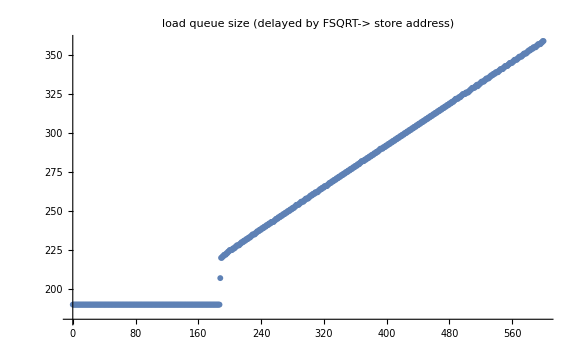

```mathematica
sqrtS19ιloadSpec=;
ListPlot[sqrtS19ιloadSpec, 
PlotLabel->"load queue size (delayed by FSQRT-> store address)",
ImageSize->Large]
```

We see a clear jump at N=188 (load queue can hold 188 entries) and this matches Dougall’s results achieved using somewhat the same idea (but with speculation from a branch dependent on the FSQRT chain, rather than on memory-aliasing dependent speculation).

What about stores?

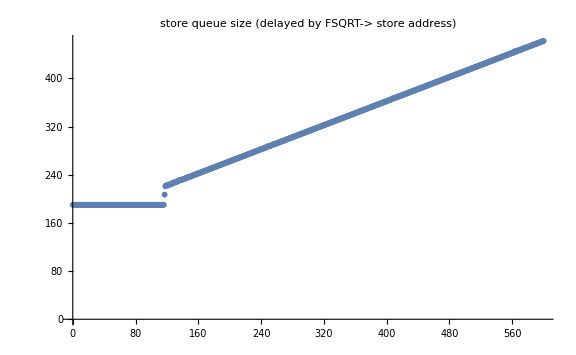

```mathematica
sqrtS19ιstoreSpec=;
p3=ListPlot[sqrtS19ιstoreSpec,
PlotLabel->"store queue size (delayed by FSQRT-> store address)",
ImageSize->Large]
```

Again we see a nice clean jump, giving us ~118 store queue slots, again matching Dougall’s result.
(You might wonder why a store would force subsequent stores to remain speculative. Surely even if the second store address matches the first, the second store will simply overwrite the first, so who cares? 
In the generic case there could still be a problem because of alignment – if one of the two stores is not aligned, then it would be possible for a matching-width store to overwrite some bytes but not others... 

If we force the alignments to match, I think that in principle the ARM model allows this to become non-speculative, but Apple doesn’t catch that and special case it.  This probably makes sense; they already have most of the win available from a good LSDP, and trying to optimize the very special case of this test is probably of little real world value.)

## Explanations

So: We have seen three different results for different attempts to measure the size of the load and store queues:
- the most naive test (uses FSQRT delay) gives an apparent size of ~330 for both
- using a load miss to DRAM delay gives apparent sizes of ~125 (L) and ~100 (S)
- using an FSQRT delay generating a delayed store address gives apparent sizes of ~188 (L) and ~118 (S)

Why these various different results? 
What appears to be happening is that Apple is using a virtual load-store queue. In other words 
- while instructions are still in-order at the Map/Rename stage, load/stores are given a sequential ID that describes their relative ordering, but they are not allocated a load/store queue slot.
- at issue time (ie at the start of execution, when the address is about to be calculated) the load/store queue slot(s) (two in the case of loads, for the LEQ and the LRQ) are allocated.

As counter evidence I will mention (2019) https://patents.google.com/patent/US20200394039A1 Processor with Multiple Load Queues which is very clear that 
- entries in the LEQ are allocated at issue
- entries in the LRQ and STQ could be allocated at issue
- LNUMs (that track relative ordering) are allocated at Rename
The most reasonable analysis is that as of the 2019 patent Apple was allocating LRQ and STQ entries at Rename, but was primed to switch this at any time, and it seems that by the A14/M1 that time had come.

We will first discuss the load cases, then see if there is anything different in the store case.

### early load queue deallocation (simple FSQRT delay)

The easiest case is the first case, a simple FSQRT delay

```mathematica
simpleFSQRTDelayLoadStorePlot
```

-Graphics-

The salient issue in that case is that there is no question of load/store aliasing because there is nothing in the store queue against which an alias could occur! 
Thus, while the loads occupy resources in the ROB, they don’t have to hold onto their load queue slots (because the only reason for those slots was to ensure that older stores that have not yet completed do the right thing relative to younger loads, and there are no older stores). 
More generally, in principle, once there are no older store that could, in any way, affect a load that load could release its load queue slot. 

We see that Apple appears to be doing this, and as confirmation there is, once again, a patent: (2013) https://patents.google.com/patent/US9535695B2/ Completing load and store instructions in a weakly-ordered memory model.
In other words, what we are seeing is proof of early resource deallocation for the case where the resource is Load Queue (ie LRQ) slots. 

The resource limitation that causes the jump at around ~330 is something we have already discussed, that the ROB consists of ~330 rows, each row can hold 7 instructions, but only one “failable” instruction, and loads/stores (and branches) count as failable instructions. 

We’ll discuss the other interesting feature of the curve later, once the “sizes” of the Load and Store Queues is settled.

### the size of the physical load queue (load to DRAM delay)

Now what about the case of the load-miss-to-DRAM based delay? ie this diagram:

```mathematica
loadQueueSizewithDRAMDelayPlot
```

-Graphics-

The most important thing to realize in this case is that the metronome that is determining the base ~330 cycle delay is a series of chained loads. 
load A → load B → load C. If each load (to some random location that’s hopefully never in cache) can execute immediately then (give or take a whole lot of noise in the response time of DRAM and the NoC) the time per loop iteration will be ~330 cycles.
But if something delays when load B can start executing, then the time per loop iteration will be more than ~330 cycles. 
So what we see is that if we have load A (load to DRAM) followed by N local loads (loads to cache) there is no delay as long as N<~125. Once N>~125 we see a delay. So these intermediate 125 Loads are using up some resources that has to be freed before load B can begin execution.
What is that resource? It’s not ROB related (that’s N=~330, or HF related, ~630, or physical register file related, ~380). It is in fact “genuine”, not virtual, Load Queue slots. load B cannot start executing until it has a Load Queue slot.

### late load queue allocation (FSQRT delay with ambiguous store address)

Compare this with with our final case, the FSQRT delay generating an unknown address for a store, as in the nice clean plots that begin this section. 
- while the head of ROB is blocked by multiple FSQRTs, 
- loads (or stores) are fetched, renamed (ie given virtual LSQ resources) and send down the load store pipeline. 
- They issue, at which point they are allocated a real load (or store) queue slot. 
- Eventually those slots run out and the loads (or stores) pile up, first in the 48 LS Scheduling Queue entries, then in the 10 LS Dispatch Buffer entries. 
- When those 58 entries are full (along with the genuine ~130 load queue entries, then Rename stalls and we get the classic jump, at N=58+130=188 for loads, and at N=58+60=118 for stores. 

If you haven’t spent much time with more traditional CPUs, this may seem obvious. But it’s not! 
A traditional CPU would stall loads and stores at Rename when it was not possible to allocate a Load or Store Queue slot. Hence it would stall at ~130 loads, or ~60 stores. 
A CPU with a virtualized LSQ at Rename only has to allocate an age tag. The loads/stores can then proceed into the Dispatch Pool and Scheduling Queue, and can keep doing so even when all the LSQ slots are full, up to the point where the Dispatch Pool and Scheduling Queue slots are also full. 
Hence late allocation allows us to enqueue 58 more loads or stores than traditional allocation before we have to stall. We get about 50% larger effective load queue size, about 100% larger effective store queue size, at the cost of a slightly more complex algorithm. 

The difference between this case and the DRAM case is that 
- for the DRAM second loop iteration to begin, the loop delay (the load B) has to proceed past the earlier stages of instructions storage (in the Scheduling Queues) to begin execution with possession of a genuine Load Queue entry
- for the FSQRT+Store second loop iteration to begin, the FSQRTs need to get past Rename to the Floating Point Scheduler, but they don’t care if 58 extra Loads have been dumped into the Load Store Dispatch and Scheduling queue and are blocked there.

So what we see is that the M1 has a pool of ~130 genuine Load Queue entries (ie LRQ entries), but for most code patterns this pool is amplified by both
- early deallocation of Load Queue entries (if there are no ambiguous store addresses remaining ahead of a Load, that Load no longer needs to hang around in the LRQ)
- late allocation of Load Queue entries (so that excess loads, that might not be able to execute because all the physical Load Queue entries are busy, can still be shifted out of Rename into storage in the Load Store Dispatch Buffer and Scheduling Queues. Doing this means that even though they can't execute until a Load Queue entry becomes available, they will not block instructions behind of a different class, like the FSQRT delay instructions.

### structure and evolution of the load-store Scheduling Queues (bonus discovery!)

What about the regions between about 330 and about 410 where we get what looks like 4 loads/cycle, not 3?
That's a reflection of the Dispatch buffer, and we saw a similar situation when we first discussed Dispatch Buffers. Before proceeding, you should also refamiliarize yourself with paired scheduling queues.

So recall the relevant part of Dougall’s diagram:

-Graphics-

This shows a single Dispatch Buffer holding 10 entries (probably correct) feeding what looks like a single, surprising large, Scheduling Queue (incorrect). 
I suggest that the Scheduling Queue is split into 4 queue of 12 entries, and so somewhat like the integer and FP setups. 
Below is the justification for the argument (which I don’t claim to be definitive, but it’s the best explanation I can give for the phenomenon we see of the “4 ops/cycle for load or store, in the range of N from about 330 to 420” in the graph we have already seen:

```mathematica
simpleFSQRTDelayLoadStorePlot
```

-Graphics-

-Graphics-

Let’s start by assuming the diagram is correct. 
- Load/Store has a Dispatch Buffer of size about 10 instructions. 
- This feeds into a single Scheduling Queue that feeds four Execution Units. 
- The Dispatch Buffer, as usual, can accept 8 instructions per cycle, but can only output four instructions per cycle into the Scheduling Queue. 
So suppose N=410. Then at the end of one cycle we have 
- 330 loads have completed, and are sitting in the ROB
- 80 loads could not move pass Rename (because no ROB entries were available)

The last FSQRT completes, the loads in the ROB Retire, the new cycle starts.
- First thing to happen is that the 80 loads piled up behind Rename have to be handled. At first these are moved into the Dispatch Buffer at 8 per cycle, and moved out of the Dispatch Buffer into the Scheduler Queue at 4 per cycle. But that means a net of 4 in the DIspatch Queue, so that can only be sustained for about two cycles before we drop to a throughput of clearing 4 loads per cycle. 
To clear out 80 loads will thus take ~20 cycles. 

- As far as the Scheduling Queue is concerned, we are piling up an excess of one load per cycle, (4 in per cycle, from Dispatch; 3 out per cycle from 3 Load units) so we cannot sustain this indefinitely, but we can sustain it for quite a while, certainly for 20 cycles (at which point we have 
+ an excess of 10 loads still in the Dispatch Buffer, 
+ an excess of ~10 loads in the Scheduling Queue, 
+ and have executed 60 loads). 
- At that point the 80 Loads in excess of 330 are done, the FSQRTs are in Rename, and can propagate to the FPU, start to execute, and start the next delay cycle. 

So we see that for this case of 410 loads, the time taken is the initial FSQRT delay, plus the time it takes to clear the 80 loads being able to do so at 4/cycle.
So this describes the  initial flat region (the FSQRT delay), the jump (run out of ~330 ROB failable slots), and the high speed region from 330 to 410 (Scheduling Queue can take in 4/cycle, emit 3/cycle, and has space to sustain this for quite some time as the Scheduling Queue slowly fills up at one excess instruction per cycle).

That all seems plausible, but we are still left with the question of why we revert to 3 loads/cycle at N=~420? If the above explanation is the full story then at that point we should have the Dispatch Buffer full, maybe 12 instructions enqueued in the Scheduler, and space for an additional excess of 36 or so. We should be able to sustain 4-wide till a much higher N! 

My guess is that this reflects some structure within what Dougall draws as a monolithic load/store Scheduler Queue of 48 entries. 
XXX I don't have time to draw any diagrams, so you will have to make do with text diagrams for now but what I imagine is the following
- this apparently monolithic queue is actually four queues each 12 entries in size
- the Dispatch Buffer is able to feed one instruction per cycle to each queue (just like integer and FP)
- this works out OK (ie it's allowable to enqueue loads into a queue that looks like its attached to the STORE/AMX execution unit) because
- of the patent we described that pairs queues together and allows an instruction in one queue of a pair to execute if the other queue of the pair cannot find a runnable instruction.

If we accept this chain of logic, then what we see matches what we might expect – we can run 4-wide until one of these queue (the one attached to STORE/AMX) is full (because every cycle it is never chose, the other queue always has a runnable load). And then we run three wide. 

A reasonable objection is that this will lead to a drastic reordering of the loads – the loads that were dispatched to the STORE/AMX queue will (if we accept the way the patent described paired queues) always be considered second class, and will be delayed as long as their are loads in the other load queue, meaning a possible indefinitely long delay. Perhaps so, and perhaps Apple are aware of that, but figured it was acceptable? The A12 has two load pipes and 2 store pipes, I can't find data for the A13.

Here's what I imagine as the evolution of the design. (Timing details for what core got when may be slightly incorrect; this is a conceptual model!)
For the A11 we have a fully symmetric design. So we have the Dispatch Buffer feeding 4 identical queue, each 12 in size, arranged like 
S0 S1 L2 L3

Now for the A12 we decide we will add paired scheduling queues. How should we pair? 
The obvious choice is to pair the two L's together, and the two S's together; it's simple, and instructions from one queue can easily be shifted to the paired pipeline without even having to test the instruction type. The downside is that the total pool of Scheduling storage for Loads remains at only 24 instructions, likewise for Stores. If we have an imbalance of lots of Loads relative to Stores, we can't make use of the Store Scheduling Queue space. 

What about if we pair (S0 L2) and (S1 L3)? The win is that now all our scheduling queue space is available to hold either an temporary excess of Loads, or (less likely, but happens sometimes, eg if you're filling a large structure with zeros, an excess of Stores). The downside is that (without substantially rethinking the details of how we choose the the oldest ready-to-execute instruction; and the mechanism of second choice from one queue feeding the other queue) we can get cases of imbalance. If the S queue is all filled with loads, and the L queue always finds a runnable load, then the S queue will stay blocked that way until something changes (eg a dependency eventually means the paired L queue cannot find a runnable Load); this is the imbalance we saw above. 

So which of these two options is overall better is a question for the simulator, but I would not be surprised to see that the LS pairing is better. For normal code (with a mix of loads and stores, especially if Dispatch tries to place stores in an S queue, and only places a load if no store is available in the Dispatch Buffer) then it's probably rarely an issue. And for code that consists of a long stream of loads or stores and nothing else, it's not much of an issue the precise order they get executed, so if some loads get stranded in an S scheduling queue for many cycles, well, so what.

So let's assume that's the A12. With A13 we get AMX, and AMX instructions are executed (ie transported to the AMX unit) via the Store pipeline. So now we have (SA0 L2) and (SA1 L3). This works in the same way as above, is still essentially balanced, and still gives us the ability to absorb long streams of pure loads, pure stores, and even pure AMX instructions, in a way that can devote all 4x12 Scheduling Queues to that single instruction type if that's all that is seen.

Finally with the A14 some bright engineer notices the following:
Suppose we define a third load pipeline. This means essentially we 
- need an AGU (but can reuse a Store AGU) 
- need a port into the TLB (details dependent on exactly how the TLB is structured, but reuse of the store port may be feasible)
- need to create a third path to the L1D (details dependent on exactly how the L1D is structured, but reuse of the store path may be feasible
- need to create a third bank for the LEQ
- need to create a third port to test load addresses against address in the Store Queue
In other words a lot of reuse of existing Store machinery is possible.
And because of the pre-existing paired Scheduling Queues, we don't have to do much real work at the Scheduling/Dispatch level.
So we land up, finally, with a structure that looks like 
(SA0 L2) (SAL1 L3)
Loads that go into the second pair (either scheduling queue) can be issued as loads, and that part of of mismatch from the A13 has gone away. The only problem is if the SA0 queue is filled with a long run of loads, which become blocked because loads are also being Dispatched into L2, and those L2 loads are always preferentially issued.

At each stage we have given our Load Store unit a reasonable boost in capabilities while also, at each stage, never paying much of a hardware price. The cost is that at each stage we introduced some asymmetry so that while performance is usually boosted quite a bit, there are weird corner cases that will do less well. If I'm correct that every four years or so the design gets a complete clean start redesign, then we may soon revert to a symmetric design with better performance than what we have today, and without the asymmetries. 
For example what we also converted SA0 to a load supporting SAL0? Well, do we want to do the full work required to support a fourth load pipeline? Maybe that's not a good use of resources. 
Alternatively we could have that SAL0 and SAL2 take turns to feed into a single third Load pipeline (basically if only one of them has a load, they get the pipeline; if both have a load, one gets it and flips a bit so that next time it's the other one's turn). That sees like the sort of quick elegant hack that Apple uses so often, providing most of the benefit of giving a full SAL0 (in particular better load balancing now) at very low additional hardware complexity. 

Alternatively, we could change the design so that the Scheduling Queues become virtual! I think this is eminently practical.
Consider how the Scheduling Queues are used. Their job is to hold instructions, test that  an instruction has become runnable, and check ages. 
These are the same job regardless of whether the instructions are loads or stores. The details of load or store only matter at insertion (Dispatch preferentially inserts stores into an S Queue, loads into an L queue) and extraction (Issue from an S queue will only extract Stores or AMX instructions). Note also that both Dispatch and Issue are already cross-wired to both of a pair of S and L Scheduling Queues. 
So:
- differentiate between physical queues (call them 0 and 1) and logical queues (call them S and L)
- Dispatch and Issue operate as above on the logical queues
- but there’s a degree of indirection between the SL and 01 queues.
- So we start off with S tied to 0 and L tied to 1
- Whenever one of the queues becomes full, we swap the indirection at both ends. (A few addition tests are necessary to ensure that, under certain circumstances like once both buffers become full, we don’t just keep swapping every cycle!)
- Meaning that, if eg, we were servicing a long run of loads, the 0 queue will become filled with loads that are never extracted, until the swap, at which point the the 1 queue will become filled with loads. 

This mechanism allows two nice improvements
- ALL the LS Scheduling Queues can act as buffer during a long run of either pure loads or pure stores; we get a much larger effective buffer before we have to drop to 3-wide Loads or 2-wide Stores as far as the rest of the machine is concerned. Right now the effective excess buffer is 10 (Dispatch)+ 12 (one L queue) or 24 (two S queues). But what I’m suggesting would allow that to expand up to 10+48 for both L and S (and A).
- We do a better job (not perfect, but a lot better) of not holding onto very old instructions without Issuing them until the machine has been forced to stall.

However as it is, we see the design we we see. Rename can feed Dispatch can feed Scheduling 4-wide up to about 90 instructions (N=~420) before queue SA0 becomes full of Loads and never able to get a chance at Issuing a Load. 
Note this also explains the Store behavior of 4 wide until N reaches ~420. The logic goes as before. but now every cycle both queue L2 and queue L3 are being filled with Stores (Dispatch of 4 instructions per cycle), while only SA0 and SAL2 are being drained of Stores (2 Stores Issue per cycle). Again at around N=~420 we have both L2 and L3 filled each with 12 stores which have never had a chance to issue, and throughput drops to 2 Stores per cycle.

### what about the store queue?

What about the Store versions of these tests? Do they teach us anything additional?

#### late allocation (miss to DRAM and FSQRT with ambiguous address delays)

Consider first the load-miss-to-DRAM case. That shows a jump at what looks like N=~100. Is that reasonable?
In this case we do not see a delay in how long it takes to start Load B until not only all 60 store queue slots are in use, but also the 58 Dispatch Buffer+Scheduling Queue slots. 
Why the difference? 
For the load case, the delay loads, load A, then load B, then load C, are fighting for the same Load Queue slots as the local filler loads. It does not help that the delay loads can move past Rename to pile up in the Dispatch Buffer and Scheduling Queue; that doesn't change the fact that the delay loop can't begin the next iteration until load B receives a physical Load Queue slot. ie the load case stalls at Execute.
In the store case, the delay loads have no interest in the Store Queue slots, so stall does not happen at Execute; rather now the common resource that both delay and filler store care about is the Dispatch Buffer+Scheduling Queue slots, and it is only when those are filled up that stall occurs, this time at Rename. Before that point, as long as a load can get past Rename, there should be a Load Queue slot available, and being Dispatched into a Load/Store Scheduling Queue should allow the delay load to get to it and start execution. 

But I slipped a fast one past you in the above! Go through the argument again. The common resource that matters is in fact just the Scheduling Queue slots, not the Dispatch Buffer. As long as there is one space free in one of the four scheduling queues, then load B can be Dispatched into that Scheduling Queue, and can be Issued for execution in the next cycle; no  delay. But if load B is placed in the Dispatch Buffer, then it cannot begin execution until a space opens up in a Scheduling Queue. Moving it to the Dispatch Buffer clears Rename and allows other types of instructions (int or FP) to make progress, but it doesn’t mean that the Load can make progress, not until a Scheduling Queue slot opens up. 
This, and the fact that movement from the Dispatch Buffer to the Scheduling Queue is somewhat stochastic once the Scheduling Queues and Dispatch Buffer fill up (since the Dispatch Buffer makes no serious attempt to preserve ordering and Dispatch the oldest instruction) explains some of the noise we see in the DRAM Delay case. And it means that the N, number of stores, at which we should expect a jump is in fact 48+60=108, omitting the 10 storage units of the Dispatch Buffer. That looks (by eye, given the noisiness) more or less what we see.

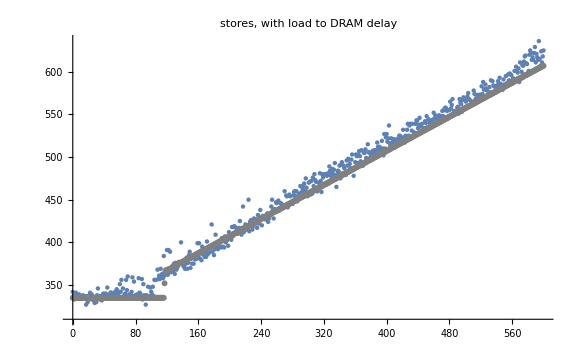

```mathematica
p3=ListPlot[#+{0, 145}&/@sqrtS19ιstoreSpec,
PlotLabel->"store queue size (delayed by FSQRT-> store address)",
PlotStyle->{Gray},
ImageSize->Large];
Show[{p1S, p3}, ImageSize->Large]
```

Certainly it seems reasonable to assume that, like Loads, we see delayed allocation of Store Queue slots, since both probes shows that many stores can progress past Rename even when the Store Queue (of size ~60 entries) is full.

#### early deallocation (simple FSQRT delay)

Consider this apparently simple case of a delay block of some FSQRTs, followed by a number of local stores (to the same simple in-cache address), which only jumps at N=~330? Here we have to tread more carefully. 
It's undeniable that 
- execution does not seem to be hindered by any resource limitation before the 330 entry ROB limitation
- there are not enough ways (either actual store queue slots, or "virtual slots" by holding store instructions in the LS Dispatch Buffer+Scheduling Queue) to get us close to 330 storage elements

- BUT! we said that stores have to be retained until they are non-speculative; we cannot allow speculative stores past the LSQ storage to make it out to the L1$!

If we equate “non-speculative” with “Retired”, then we have a problem because these stores have not Retired – that’s the whole issue of them still present in the ROB and using up the ~330 available ROB slots they can occupy.

Conceptually one might imagine two ways out of this problem.

One possibility is that we are, in fact, overwriting the same address every cycle. So in theory there's no need (once you establish that there are no intervening loads or anything else of interest between two stores) to care about the older store value, all that matters is the newer value. 
Under the right conditions Apple might cull older stores as being idempotent (ie they don't change the state of the machine). 
This is easily understood, but I’m unaware of any core that attempts exploit this fact (which, ideally shouldn’t happen in most code!)

Can we test this? 
I tried changing the storage address so that every store stored to a successive location, and saw no difference. 

But that's still not absolutely definitive, because how large is the amount of storage attached to each Storage Queue slot? It could be as large as a cache line! Maybe successive stores are aggregated somehow as a single unit in a single Storage Queue slot? Ambitious! But not impossible.

So I separated successive stores by 64 bytes and again, no change, the jump in the curve is at ~330 stores. 
The issue is not related to idempotent stores.

The second possibility is that remember the whole point (the only point) of the store queue is to hold onto stores as long as they are speculative. 
Not until they retire, not to force some sort of program order, only so that they don't escape out to cache until they are non-speculative. 
Which means that as soon as we know they are non-speculative, the Store Queue can be released, and the store allowed to proceed to cache! 

And this is, in fact, what happens. Essentially for every instruction in the ROB, Apple is tracking two things, both 
- when the instruction Completes and 
- when the instruction becomes Non-Speculative (ie every earlier instruction that was speculative or could cause a fault of some sort has successfully completed). 
At the point that stores become both Completed (ie their TLB lookup has indicated that they are not problematic) and Non-Speculative, the store data can be sent off to L1$, and the Store Queue entry freed for re-use, regardless of how far from retirement the store is. 

As usual, there's a patent confirming this hypothesis: (2015) https://patents.google.com/patent/US10228951B1 Out of order store commit.

#### 2006 (historical interest, early release of store queue data for a strong memory model)

To understand the full flow of thought, we begin with (2006) https://patents.google.com/patent/US20080086623A1 Strongly-ordered processor with early store retirement, a patent from the PA Semi days, and not especially relevant (because it's about a strongly ordered memory model -- perhaps PA Semi thought they might be forced to make x86 designs?). The patent says, essentially, that it can't think of anything to do about early release of load queue entries, but that there are circumstances under which store queue entries might be early-released. (Well, not exactly. What they seem to have in mind is almost the reverse of our concern. Assume a Store that is Non-Speculative and ready to Retire. At this point it tries to store its data, but the Store misses in L1. The idea seems to be that we will perform the Retire anyway, we will store the Store Data in some Cache buffer (to be merged with the cache line when it is delivered to the L1D), and we will free the LSQ entry.

#### 2013 (early release of non-speculative loads)

This is followed by the more optimistic (2013) https://patents.google.com/patent/US9535695B2 Completing load and store instructions in a weakly-ordered memory model which we've already described (early release of loads once they become non-speculative). 
The early release of loads when non-speculative is, perhaps, obvious (at least for a weakly ordered memory model); the patent is mainly about how you can implement separate load and store queues that maintain ordering relative to each other, while allowing both loads and stores to be (in-order) removed from one end of the queue while new instructions are added to the other end. It's worth looking at to see how these sorts of queues are implemented without having to move data between slots, and how wraparound is handled – but it will make your head hurt!

#### 2015 (early release of non-speculative stores)

Finally we get the above-mentioned (2015) https://patents.google.com/patent/US10228951B1 Out of order store commit which gives us more aggressive store commit. 
The difference here compared to the 2006 case is that 2006 
- allowed stores 
+ to release resources, and 
+ commit to cache, 
+ before retire, 
- but this had to happen in ROB order. 

2015 
- allows the resource releasing out of ROB order. 
Specifically, if the oldest store to be committed is a cache miss, then, while that cache miss is being served, we allow younger [but no longer speculative] stores to be written to cache.

It's interesting that they don't tell us how you can operate a low-power queue if you are allowed to remove items from the middle of the queue – obviously the circular queue techniques of the 2014 patent won't work! 
Presumably they use ideas like those of the non-shifting reservation station, like we saw in (2015) https://patents.google.com/patent/US20170024205A1 Non-shifting reservation station when discussing Scheduling . 
(And it gives one confidence in Apple's design process if a good idea invented for one part of the CPU is immediately adapted to solve a similar problem in a different part of the CPU.)

#### 2018 (how the machine tests that a load or store has become non-speculative)

This series of patents ends, for now, with (2018) https://patents.google.com/patent/US10628164B1 Branch resolve pointer optimization. In all the above work we refer to stores (or loads) as becoming non-speculative, and we know conceptually what that means, but not exactly how the machine implements it. The patent describes a way of implementing this. The problem is not quite as simple as you might think, because any given store might depend on multiple branches ahead of it, and those branches can execute out of order. 
One way you might solve this is through a variant of our good old dependency bit vector scheme, with something like a bitvector that holds all the predecessor branches that have not yet executed. But there’s an easier solution, the subject of the patent.

Simplifying to convey the point, imagine the stream of execution as it passes through Decode, where every instruction gets a sequential instruction number. 
- Then any given store can know the number of the last branch before it in program order.
- If the Decode unit also propagates that number down to the Load Store Unit which propagates it to the Store Queue, then every Store in the Store Queue also knows the number of the branch after it.
- Finally as every branch is executed (possibly out of order) the number of the oldest branch that’s still in the Scheduling Queue is noted. (The patent is somewhat vague about this, but it’s the only interpretation that makes sense.) 
- This oldest not-yet-scheduled branch is sent to the Store Queue.
Every store now knows that it lives between the branch ahead of it with sequentialID M and the branch behind it with sequentialID N.
When the oldest not-yet-scheduled branch sent to the store queue matches sequentialID N, then every branch earlier (ie branch M and forward) has been executed, and so the store (or load) is no longer speculative. 

This sounds reasonable, but I don’t understand why the behind branch sequentialID is required; why not just compare the branchID that’s propagated to the Load Store Unit with the sequentialID of the store itself? I suspect there are a lot of details (how much can you trust that the Scheduling Queues and Dispatch buffer can precisely identify the oldest branch that has not yet been scheduled?) that ultimately rely in some way on this second behind branch sequentialID, but honestly I cannot understand the patent as it is presented, even when I try to fix up the parts that seem clearly wrong.

To some extent these out of order commit concepts seem “obvious”. However historically (and still!) out of order commit has been seen as too complicated to be worth implementing. (2019) http://uu.diva-portal.org/smash/get/diva2:1263287/FULLTEXT01.pdf Maximizing Limited Resources: a Limit-Based Study and Taxonomy of Out-of-Order Commit is one of my less favorite papers (grindingly repetitive, and with singularly unhelpful graphs), but it does explain some of the issues in out of order commit. By their terminology it appears that Apple is using a somewhat (though not fully) aggressive version of what they call safe out of order commit.

#### 2011 (early version of the store queue storage structure)

(2011) https://patents.google.com/patent/US9131899B2 Efficient handling of misaligned loads and stores is about something different, but it describes the store queue structure at the time. 
The store queue consists of two parallel storage arrays; one holds addresses, the other holds the stored data.
The address array is split into two banks, an even bank and an odd bank, based on bit 7 of the storage address. We’ll see how this matches the design of the L1D, but essentially what it means is that bits 0..6 of an address give an offset within a 128B line, while bits 7..13 describe which line within a 16kB page (and thus describe the sets of the cache). Thus the store queue, like the cache, is split into even and odd halves based on the lineID. 
Each storage slot of the odd half and the even half share a page address. 

I think the way the design is supposed to work is that one entry refers to one executed storage instruction. 
- In the normal case (a store that does not cross a cache line) the page entry and one of the even or odd line halves is valid; the valid half gives the address of the store. 
- In the line crossing case the page entry is valid, both line halves are valid, and they refer to a line and its successor; by the pattern of the two addresses, you can tell how to split the two parts of the store data across a line. 

Thus we have a structure that 
- records the store data (regardless of alignment) separately simply as a blob of 8..128 bits
- records the store address in a way that’s split by even/odd lineID and so makes it fairly easy to detect and deal with stores that cross a cache line (and means that, for most loads and stores, only the even or odd half of the store queue has to be probed, perhaps saving a little energy) 

You might ask what about stores that straddle not just a cache line, but a page boundary? They could be treated as two separate stores (use two entries) but the patent suggests using a third small structure (not described) to handle those (presumably rare) cases. And additional complication you probably didn’t think of in that case is that (one way or another) the store has to be sent through the TLB twice to translate both of the pages that are touched. 

This structure (and its matching equivalent in the L1D) mean, among other things, that the address parts of a load matching this earlier store that crosses a line can be handled simultaneously, and the store data delivered as a single package to the load, so a line-crossing load is no more expensive than an aligned load. The same essentially holds true for line-crossing loads whose two parts hit in the cache. 
My guess is that even if the different parts of a store are written to their separate cache lines in separate cycles, the entire entry will not be reused until both parts of the store are written  – meaning that the store queue can always service the entire load. 

The nastiest case is a store that provides part of a load (think a double byte store that crosses a cache line, followed by a double word load that crosses a cache line and covers that store). Presumably in this case data has to be provided from both the store queue and two cache lines (and at least one of those cache lines could miss in cache), and it all has to be stitched together! The LSU provides auxiliary storage, called the Sidecar, to hold the various temporary pieces during this operation.

### (2020) write combining buffer

Recall that the primary goal of the Store Queue is to hold speculative stores. We’ve suggested ways to extract more value from the Store Queue by treating it as an L0 Cache and encouraging it to hold more data. One problem with that line of thought is that, in line with the Store Queue’s primary goal of handling speculative stores we have to think very carefully about how aggressively to aggregate successive stores (especially small stores like bytes) into a single Store Queue entry. The task does not seem hopeless (perhaps use a color/generation that changes every time we cross a speculated branch, and allow successive stores with the same color to aggregate, and then complete together?) but there are limits to how aggressively this can aggregate, especially when you consider eg the structure of a loop of stores. 

Another alternative is to give up on using the Store Queue per se in this way (perhaps beyond some simple color-based aggregation to make it effectively larger?) and add a different type of structure, namely a set of Write Combining Buffers. These differ from the Store Queue in that they are populated by by stores that are no longer speculative, and so aggregating is no longer a problem. The advantage of this aggressive aggregation is that we save power and bandwidth. If we can aggregate multiple stores in a Write Combining Buffer, when that buffer is full we only need to take up a single L1 cache cycle to move the aggregate to the L1, and if we aggregate enough to fill an entire cache line, we can write the entire cache line to L2, avoiding
- L1 bandwidth
- allocating an L1 line that (more likely than not) will never be referenced before it ages out to L2 anyway
- reading the line from L2 (or even SLC or DRAM), and then fully overwriting it just a few cycles later.

So there’s clear value in having at least one or two Write Combining Buffers sitting between the Store Queue and the L1 cache. But once you have such structures you have the same problem as with any structure, namely the governing algorithms. In particular: on the one hand, we want to keep each buffer “open” as long as possible, on the off chance that eventually a new value will come in to aggregate with the existing values (and of course the larger the aggregation the better, up the best case of all where an entire cache line is covered); but on the other hand we always want to be able to cover a short burst of stores without slowing down the rest of the machine (which will happen if the Store Queue fills up because it can’t retire stores to the Write Combining Buffer, because no Buffers are free and we’re waiting to write some out to L1 or L2). So how do we balance these?
The 2020 answer is https://patents.google.com/patent/US11256622B2 Dynamic adaptive drain for write combining buffer. 
Honestly, as bottlenecks go, this one is pretty unimportant, and so not much effort has been put into making the solution especially sophisticated. 

The simplest type of solution is something like: assume we have 16 Buffers, and, on average, 4 free Buffers is enough to absorb most bursts of stores (given that some of the stores will hit in early buffers, and many of the stores will aggregate in the 4 free buffers). Then we establish a highwatermark of 12, and once we have more than 12 buffers active we start draining them (ie transferring them to L1), while continuing to accept non-speculative stores from the Store Queue, and ideally we never have to pause for running out of Buffers. 
The problem with this is that while most code mostly has stores close together (eg filling up a cache line) some code may write to widely different addresses. One type of example is changing just one field in each entry of an array large structs (which might translate into, eg, changing two bytes in each cache line). Another type of example might be a stream of unpredictable, almost random, writes, as in writing to a hash table. For such code, a highwatermark of 12 may not work very well because the writes do not aggregate well in either previous or newly allocated buffers, each buffer only captures one or two writes, and so it makes sense to switch to a substantially lower highwatermark, perhaps 8 or even 4. 
And that’s essentially what the patent is about – track the number of non-merging stores (ie stores that require a newly allocated line) vs the number of merging stores and if it grows too high, respond appropriately, either by switching to draining immediately, or by modifying the highwatermark. 
There’s a slight tweak to this in that we may hold off draining if the L1 cache port is in use (which is another way of saying that stores always have lower priority access to the L1 cache than load [and probably prefetches?]) but nothing more. One could imagine some more sophisticated tweaks. For example which lines are chosen to be drained? It seems to be either random, or a roundrobin over the store structure. A fancier scheme might track how “efficiently” a Buffer is being filled and drop Buffer with lower efficiency, or try to hold for longer onto Buffer that are close to full. But that would take area and energy, and is perhaps just not worth it; the common cases that result in efficiently filled line will be handled more or less automatically anyway.

## Testing the LSDP

Let’s see what we can learn about the LSDP. The idea is to create varying types of store/load pairs and see how performance varies.
We build up complexity gradually.

### independent addresses

To calibrate, start with a basic load and store to two different, unchanging, addresses, using two different registers:
STR x10, [x2]; LDR x11, [x3] 		(x2!=x3)

There should be absolutely no interference here between the store and the load, and that’s what we see.
We see nothing unexpected, and we see a throughput of 800 store+load pairs takes essentially 400 cycles, so two pairs (four memory ops) per cycle.

Now a slight variation:
STR x10, [x2]; LDR x10, [x3] 		(x2!=x3)
What’s different here? Note that the load now feeds into the store. 

Your first thought might be that this has to run sequentially, each instruction waiting for the next. But be careful.
Write the code as 
STR1 x10

LDR1 x10
STR2 x10

LDR2 x10
STR2 x10

etc

LDR1 and LDR2 are independent (they will load to different physical, renamed, registers).
What a common register enforces is that the store (one store) has to follow the load. That’s all. 
Hence there is nothing preventing each pair (as drawn) from executing in parallel, two per cycle (two loads, two store per cycle).
And once again that is what we see.

```mathematica
storeLoadπDiftAddrπfullyIndependent=;
storeLoadπDiftAddrπchainedSrcDstRegister=;
ListPlot[{storeLoadπDiftAddrπfullyIndependent, storeLoadπDiftAddrπchainedSrcDstRegister},
PlotLabel->"load/store pairs, to different addresses",
PlotLabels->{"using different registers", "using same src/dst register"}, 
ImageSize->Large]
```

-Graphics-

The case of a chained dependency through the same register (gold line) is very slightly slower than the case of no chained register (blue line) but essentially the same speed of two pairs per cycle! 

Given this understanding, we can now see why slight variants on this, using two different register widths, behave the same way. 
STR x10, [x2]; LDR w10, [x3] 		(x2!=x3)
and
STR w10, [x2]; LDR x10, [x3] 		(x2!=x3)
also run at full (two pairs per cycle) speed.

### same address (no prediction required)

Now we do the same thing, different registers but load/store to the same address.
STR x10, [x2]; LDR x11, [x2] 
Once again your intuition is that we have forced a dependency, but again let’s be careful. So write the code as 

STR1 [x2]
LDR1 [x2]

STR2 [x2]
LDR2 [x2]

STR3 [x2]
LDR3 [x2]

Now think about how this code has to execute (for correctness) and how it will execute. 
For correctness we require that 
- every load (appear to) execute between the two store and
- every store (appear to) happen sequentially
But our OoO machinery is very flexible in how this is actually implemented. 

The stores can occur out of order, just as long as the (address, data) pairs are placed into the Store Queue in the correct order (which is achieved by giving each store a Store Queue location at Mapping/Rename (while the stores are still in order). 

The loads can also occur out of order, the only constraint being that each load of a pair must occur after its matched store. 

So, conceptually, what now happens is that a whole lot of these loads and stores are thrown into the Dispatch Buffer and the Load/Store Scheduling Queues. Ideally their age is preserved in this process, and they are scheduled in order, but the Dispatch Buffer doesn’t promise to preserve order, and the ambidextrous Load/Store unit may occasionally have a load placed in it the Dispatch Buffer rather than the perfect balancing of always stores. So ordering will occasionally be imperfect.

Assume perfect ordering. What should we expect? Some of this I have to guess, because no-one gives full details, but we have something like:
STR1 has been split into two instruction, StoreAddress1 and StoreData1, both targeting a particular slot in the Store Queue (slot allocated already).
STR1 (both parts) and LDR1 issue together. 
Store Data places its data in the Store Queue slot.
Store Address and Load calculate their address, and perform TLB lookup in sync. 
At that point, the next cycle or so, we have something like 
- the store will place its address value in the Store Queue slot
- the load will send its address value to the L1D, and to the Store Queue
- if the timing is set up correctly, we can have something like the store places its value in the Store Queue slot in the first half of a cycle; the load performs a comparison against all the Store Queue slot addresses in the second half. 
- so the load sees a match, the store data is already present, and the load completes (acquiring the data from the Store Queue rather than the cache).

If we have imperfect ordering (the load occurs one cycle or more earlier than the paired store) then what will happen is 
- the load looks in the Store Queue, finds no matching entry, and gets the data from the L1D cache

For most cores that’s the end of the story, at some later point the Store will execute, will compare its address to the addresses in the Load Queue, will see that its paired load has already executed (and acquired data from the L1D) and that load will be marked as having to be Flushed (or some similar recovery procedure).

For Apple (the 2019 Load/Store Ordering Violation Management patent we have already discussed) what will happen is that every store in progress will also compare its address against every load in progress. This means that, for example, right after address generation (even before TLB lookup) the store will have some sort of indicator of where its data is going. This can be compared with the in-progress load’s virtual address and if they match, then that’s simply an early version of the load’s eventually matching the address in the Store Queue! (Of course this mechanism is not perfect; it won’t catch weird cases like the store written to a physical address that’s the same as the load, but via a virtual address that is different. And it may not catch weird partial overlap/alignment cases. But it will catch most cases early, with all cases being caught by the later tests.) 

This means that even if the store started two or three cycles after the load, the there may be enough of an overlap in time for the load to detect that it has a matching store in progress and should not get its data from the cache. In theory the load might be able to get the data from the Store Queue (the store that matched its virtual address with the load knows its Store Queue slot, and the Store Data instruction may already have dumped its data there). I don’t know if Apple does that. Even if they don’t, the load can be marked as a Replay, and so it re-executes a cycle or three later, at which point the Store has fully completed, and the load can match its address against the Store Queue and pick up the data from there.

This is what we see in the curve. There’s clearly some messiness (the occasional Replay) but overall our performance has not slowed down too much. 
The gold curve (I only drew half of it to leave the lower part of the curve easier to see) shows what would be perfection (2 load/store pairs per cycle, no cycles lost to Replay or Flush) and we run about 15% slower than perfection. Not ideal, but we’re not losing too many cycles, even in this worst possible scenario, where basically every load and store are setup so that it’s easy for them to cause a Flush.

Note that what we have seen so far can be summarized as:
- if a register is shared, store has to happen after load
- if an address is shared, load has to happen after store
but in both cases, with only one of these two (register and address) shared there are no serial dependencies. There is only the dependency of each individual load/store pair, and the pairs can all execute independently. Hence we run at essentially two pairs per cycle in all these cases. 

- no LSDP is necessary because the addresses (of the load and store) are known early enough. Ideally the loads execute at the same time as the stores (or a cycle later) so when the load looks up an address in the Store Queue, it finds its matching address. 
Even in cases of a few cycles of slip between the load and the store we are still OK without an LSDP because our ability to compare an in-progress store address against every in-progress load address catches these cases and handles them without much overhead.

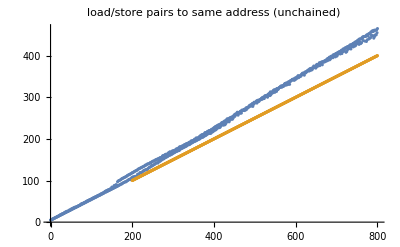

```mathematica
storeLoadπSameAddrπFullyIndependent=;
ListPlot[{storeLoadπSameAddrπFullyIndependent,{#, #/2}&/@Range[200, 800]},
PlotLabel->"load/store pairs to same address (unchained)"]
```

### same address but delayed data (prediction required to avoid replay)

Now suppose that the data of the store is only available very late, but the address of the store is easily available. We would expect now that, just as above, mostly the loads and stores execute in sync, and the load hits a point where it has matched in the Store Queue, but the store data is not available. So it will have to Replay once the Store Data part of its associated store executes. 
We can force this be using a slow instruction like FVCTAS to generate the store data, so our probe looks like 
FCVTAS x10, d1 (with d1=0.0)  this instruction has a latency of ~13 cycles and converts d1(=0.0) to an integer
STR x10, [x2]; LDR x11, [x2]

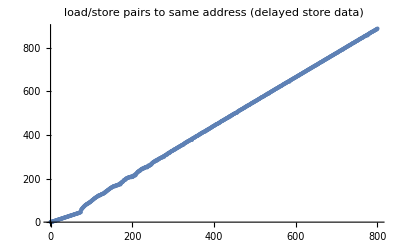

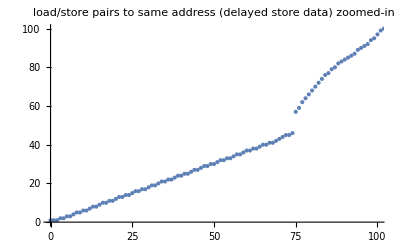

```mathematica
storeLoadπSameAddrπDelayedStoreData=;
ListPlot[storeLoadπSameAddrπDelayedStoreData, 
PlotLabel->"load/store pairs to same address (delayed store data)"]
ListPlot[storeLoadπSameAddrπDelayedStoreData, 
PlotLabel->"load/store pairs to same address (delayed store data) zoomed-in",
PlotRange->{{0, 100}, {0, 100}}]
```

Honestly, this is better than I expected!
There are clearly two regimes. 
Up to 74 pairs, the machine processes about 1.6 pairs per cycle. Not quite two pairs, but close'ish.
After 74 pairs, the machine processes about .8 pairs per cycle.

So let's think about this. 
Ideal execution would be that each load is delayed long enough that it only issues just before the x10 value is ready to be stored. 
The machine is not psychic enough to do that!
But what it can do is record each time a load issued too early compared to its store, and record that in the LSDP. 
Then the next time the load is placed in the Scheduling Queue, it will wait around with the store as a dependency, and will not execute until the store has executed (address and data).
If the machine could do that perfectly, then once the predictor is trained we shouldn't have to lose any cycles, we'd just have every load waiting around (for a long time) in its scheduling queue until its store was ready. In the real world the delay between the load and the generation of the store data is long enough that scheduling queues will fill up, instructions will slip out of order, cycles will be lost while no appropriate instruction can be found in a particular queue, etc.

What we see is that we get close-ish to that ideal case for up to 74 load/store  pairs. This suggests 
- that the LSDP can hold ~74 entries
- when everything is working,  load is delayed by the LSDP to the correct time required by the store data, so the load does not have to Replay.

Once we get past the capacity of the LSDP we switch to essentially one pair per cycle. I interpret this as meaning that the execution of every paid proceeds like 
Store Address + Load (execute same cycle)
Load - sees no valid store data, sets a Replay dependent on the Store Data arriving for that particular Store Queue slot
Load - Replays successfully.

Now that each load of the pair has to execute twice how long would we expect a pair to take?
If 100 pairs take 50 cycles (no Replay), then naively 100 pairs take 100 cycles (Replay, each load executes twice). 
This isn't quite correct because in principle three loads can execute per cycle if there are no stores (but can this happen for Replay conditions?), but let's accept it. Then we'd expect ideal throughput to drop to 1 (or a little over 1) pair per cycle. 
We have all the imperfections of before, plus new collisions that can occur in the LEQ, so let's just round up the .8 per cycle we see to close enough to 1.

I think it's reasonable to conclude that 
- we have seen the LSDP make its appearance
- it can hold about 74 entries
- when working correctly, we don't lose much load/store performance to the severe out-of-order execution generated by the slow production of the store data
- even when the LSDP can't help us, this particular case (address known, just data unknown) is handled adequately by the Replay mechanism. We lose half our throughput (since every load has to execute twice) but no more than that. 
And as always what we are testing here is extremely unbalanced code! Normal code may well have store data that is very delayed, but it is unlikely to have a load of that store data immediately after the store, or to have such a high density of loads that the cost of the extra Replay loads is a noticeable additional burden.

### same address, same register

Now use a chained register:
STR x10, [x2]; LDR x10, [x2] 
Unrolled this looks like:
STR1 x10, [x2]
LDR1 x10, [x2]
	STR2 x10, [x2]
	LDR2 x10, [x2]
		STR3 x10, [x2]
		LDR3 x10, [x2]

Earlier we stated that a common register requires the store to follow the load. And a common address requires the load to follow a store.
So we’re basically stuck. 
Unlike the previous cases, we can no longer separate the chain of instructions into independent load/store pairs that are run in parallel. 
The best we can hope for is to run STR1 and LDR1 in parallel, meeting after three cycles at the STQ entry, another cycle to get that data value up to the bypass bus (and stored in the physical register corresponding to LDR1’s x10); then we start the next pair of STR2+LDR2.
So we expect best case throughput of one pair per four cycles.

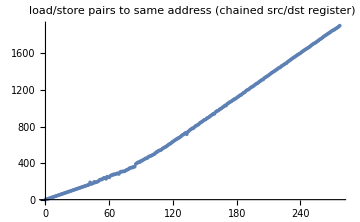

-Graphics-

```mathematica
storeLoadπSameAddrπChainedSrcDstRegister=;
ListPlot[storeLoadπSameAddrπChainedSrcDstRegister,
(* {#, 8(#-100)+483}&/@Range[100,250],*)
PlotLabel->"load/store pairs to same address (chained src/dst register)",
ImageSize->Medium]
ListPlot[{storeLoadπSameAddrπChainedSrcDstRegister,
{#, 4#}&/@Range[100]}, 
PlotLabel->"load/store pairs to same address (chained src/dst register)",
PlotRange->{{0, 100}, {0, 500}},
PlotLabels->{"measured data", "guide line (4 cycles per iteration)"}, 
ImageSize->Large]
```

Clearly there are two regimes. 
The initial regime can support about 70..80 load/store pairs. While in that regime the cost of a single load/store pair is about 4 cycles (slope of the initial section). 
Once we transition to the slow regime, the cost of a single load/store pair jumps to about 8 cycles.

So this matches our analysis. 
One thing it confirms is that loads and stores to the same address (ie the pair STR [x2] LDR [x2]) do indeed behave optimally. They can issue together, and the store address can be placed in the Store Queue early enough for the load to detect that address when it probes the Store Queue.
For the load to acquires its data from the Store Queue rather than the Cache is called Store Forwarding.
(In fact there are multiple ways to perform Store Forwarding. The way Apple actually implements this is probably via the Register File. This will be explained soon, in the Load Accelerators section, with a brief discussion below of Zero Cycle Loads.)

Secondly it confirms that the size of the LSDP seems to indeed be around 74 elements.

It also suggests something about the replacement policy for the LSDP.
My assumption is that the replacement policy for the LSDP is not especially sophisticated. Suppose you want to add an entry to the LSDP? What slot do you use? 
If any slot is marked invalid, that's an obvious choice. 
If there are no invalid entries, then low confidence entries are the next obvious choice. 
Then entries that are used to avoid a Replay rather than to avoid a Flush (since Replay's are much cheaper than Flushes).
But when all entries are essentially the same in these respects, what do you do? 
- Random is one choice. This requires remembering no state.
-  Another is LRU, which, in exact form is difficult to implement.
-  Another is MRU, also difficult to implement and probably optimal for streaming situations. 
 - A fourth option is to track the entry number you replaced last time and just increment that with wraparound. 
 For "normal" code with a mixture of memory references of all sorts, this will behave like Random, skewed towards LRU (good). 
 For streaming code, it will behave like LRU, which is pessimal. 

 This fourth option seems to me to be what we are seeing. 
 In the earlier case where we had delayed store data, and a clear  break in the curve, that suggests LRU (behaving pessimally, with essentially zero reuse). 
 This current curve has a much less pronounced break at the transition point, so it's behaving more like Random replacement of the LSDP, I'm guessing that's because entries are being added to the LSDP in a somewhat more random manner as execution proceeds. (Before the LSDP is populate, the stores will all be held back relative to the loads, because the x10 dependence is immediately visible to the scheduler; which means multiple loads will initially start too early compared to their subsequent stores. Throw in the ambidextrous load/store unit, and pretty soon you have a major mess in terms of the order in which the load store dependencies are detected and then recorded in the LSDP.)
 Under Random (or Random-equivalent) replacement we'll see some entries being removed that are still being used, even as other entries would have been a much better choice for removal, so we should start to expect that even at only N=50 or so, we start to see some occasional slowdown because some loads that should have been held back by the LSDP have had their entries replaced prematurely and sub-optimally. 
 
 For most code the choice of LSDP replacement policy probably doesn't matter much. If you are writing code that is streaming (so it has a controllable structure and it's constantly generating loads that match the address of recent stores, you're probably doing something terribly wrong!) For normal code, Random is a reasonable choice, and if Apple do what it looks like to me, they get something probably a little better than Random because it skews to LRU.

The second regime is as we discussed before. In the second regime We are still trying to execute like 
STR1 x10, [x2]
LDR1 x10, [x2]
	STR2 x10, [x2]
	LDR2 x10, [x2]
		STR3 x10, [x2]
		LDR3 x10, [x2]
but we do not have the LSDP to enforce the precise synchronized scheduling of each store with its matching load. So most loads execute early relative to their stores, don’t see the data available in the Store Queue (but are caught as Replays) and are forced to Replay. So our minimal cycle becomes
STR1 x10, [x2]
LDR1 x10, [x2] (a cycle or two off earlier than the store)
LDR1 x10, [x2] (replay)
	STR2 x10, [x2]
	LDR2 x10, [x2] (a cycle or two off earlier than the store)
	LDR2 x10, [x2] (replay)
		STR3 x10, [x2]
		LDR3 x10, [x2] (a cycle or two off earlier than the store)	
		LDR3 x10, [x2] (replay)
The minimal timing of one loop becomes not the latency of one load but the latency of a load+replay. 

Experts might ask Zero Cycle Loads in this context, and if that changes anything. Zero Cycle Loads will be explained towards the end of this load/store section. 
The short answer is no, because the ZCL still has to be validated, and that takes the full timing cycle described above. 
But to check this, I ran the code three times. 
The second time used LDR x10, [x2, x0] (with x0 set to 0). An indexed address of this form is  not susceptible to the basic ZCL but is still susceptible to the strided address ZCL. 
Any simple attempts to bypass the strided address ZCL by varying the common address used by the load and the store is strided, so will still be captured by the ZCL! So let’s use a quadratically increasing address stream!
initialization
	MOV x0, #0; MOV x20, #1
loop
	STR1 x10, [x2, x0]
	LDR1 x10, [x2, x0]
	ADD x0, x0, x20
	ADD x20, x20, #1
but even this quadratically varying index stream (no ZCL!) has essentially identical results. 

Remember that the LSDP matches a store PC with a load PC. The whole point is that it does not know that actual load and store addresses (if we knew those, we would not need a predictor!) So apart from the ZCL issue, we should expect (and indeed we see) no change even when the addresses being shared by the loads and stores change.

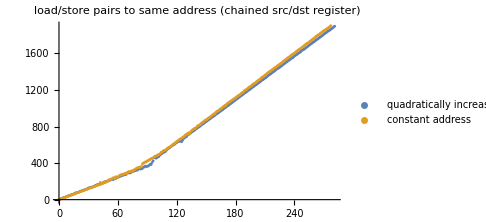

```mathematica
storeLoadπSameAddrιQuadraticπChainedSrcDstRegister=;
ListPlot[{storeLoadπSameAddrιQuadraticπChainedSrcDstRegister, storeLoadπSameAddrπChainedSrcDstRegister},
PlotLabel->"load/store pairs to same address (chained src/dst register)",
PlotLegends->{"quadratically increasing address", "constant address"}, 
ImageSize->Medium]
```

### force address prediction (delayed address)

Now we' re going to repeat these tests, but forcing the store address to be unknown at the time of the load. The plan is the same as how we generated delayed store data:
• generate an integer (slowly!) using 
FCVTAS x0, d1 (with d1=0.0)  this instruction has a latency of ~13 cycles and converts d1(=0.0) to an integer
follow this with 
STR x10, [x2, x0]; LDR x11, [x3] 		(x2!=x3)

So the probe looks like repeated ( FCVTAS STR LDR ).
Once again the load and store are completely independent. 
If the LSDP is working correctly, they should not interfere with each other in any way, and we should see no slowdown. 
Even when we do overflow the LSDP, as long as loads are predicted by default never to match unknown store addresses we should still see no interference

And we see nothing unexpected, nice smooth two pairs processed per cycle.

#### load from (unknown) store address

But now one small change, force the load and store to share an address:  
STR x10, [x2, x0]; LDR x11, [x2] 
Note that these correspond to the same address, but we are not forcing the load to delay on the x0, so it should be able to execute well in advance of the store.

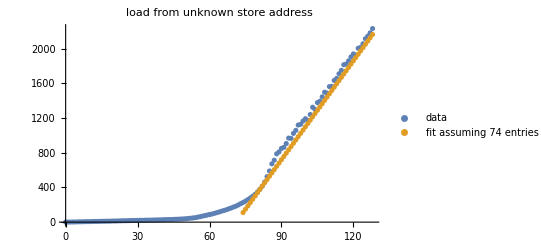

```mathematica
storeπDelayedιLoadπSameAddrπIndependentRegisters=;
ListPlot[{storeπDelayedιLoadπSameAddrπIndependentRegisters,
{#, (#-74)*38+1.5*74}&/@Range[74, 128]},
PlotLabel->"load from unknown store address",
PlotLegends->{"data", "fit assuming 74 entries and 38 cycle flush"}]
```

Yikes! Let’s zoom in:

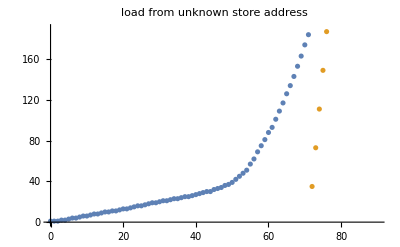

```mathematica
ListPlot[{storeπDelayedιLoadπSameAddrπIndependentRegisters, 
{#, (#-74)*38+1.5*74}&/@Range[72, 128]},
PlotLabel->"load from unknown store address",
PlotRange->{{0, 90}, {0, 190}}]
```

So up till about 50 pairs we get adequate throughput. Not the 2 pairs per cycle I would expect, but something like 1.4 pairs per cycle. Honestly I can’t see why the gap between what we expect and what we get is quite as low as it is. Each load will have to delay until its store executes, but in theory these should all be able to just wait in the various Scheduling Queues until the stores are ready, then immediately execute, with few lost cycles. 

However we are more concerned with what happens once we exceed the capacity of the LSDP. The slope of the second half of the curve is about 38 cycles/pair! 
I think this splits into something like 25 cycles as the cost of a flush caused by a load/store aliasing., and 13 cycles as the cost of performing the FCVTAS after the flush, either way the cost of a Flush is clearly phenomenal compared to either correct execution or a Replay. 

The execution pattern is: 
- the load executes (far in advance of the store, which is waiting for the FCVTAS result). 
- It isn’t stopped by the LSDP (which has overflowed and so has no matching PC) and so 
- it executes assuming it matches no address in the Store Queue.
- Later the store address becomes available and is compared to the address in the Load Queue, 
- we see that the Load picked up stale data (either from the L1D or an earlier entry in the Store Queue),
- and so the machine forces a Flush after that load. 
(In principle doesn’t have to be this way! Suppose the value that was loaded were stored in the Load Queue next to the Load Address. This could be compared with the Store Data and if they match, why Flush? 
No-one does this, but given that repeatedly storing and loading the same data is not that uncommon – sometimes for good reasons, sometimes not – it seems worth at least running a simulation to see what sort of a win this could buy you.)

The curve suggests the LSDP holds only about 50 elements. But that’s an illusion caused by random replacement and the massive increase in cycles when even just a small fraction of the load instances cause a flush. I added the gold line to both curves to show how we’re still really dealing with ~74 entries in the LSDP.

#### force the load to be delayed like the store

What if we also force the load to delay, by making it also depend on the x0?
FCVTAS x0, d1; STR x10, [x2, x0]; LDR x11, [x2, x0]

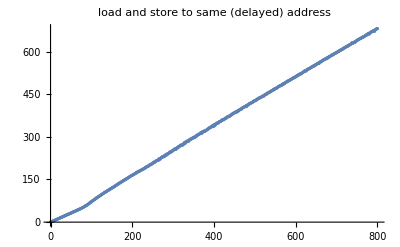

```mathematica
loadStoreToSameDelayedAddress=;
ListPlot[loadStoreToSameDelayedAddress,
PlotLabel->"load and store to same (delayed) address"]
```

Now we see something like the first stage of the LSDP curve. 
We see an initial slightly faster regime, about 1.5 pairs per cycle, for N<~70..80. 
Then about 1.2  pairs per cycle.

So performance is adequate. Not great, when we compare with the 2 pairs per cycle when the load and store addresses are both known, but clearly we’re just getting some sub-optimal scheduling (at N<74) and  the occasional Replay (at N>74), not many Flushes. 
As I’ve said earlier, I wonder if at least some of this glitchiness is the result of the ambidextrous load+store Execution unit? 
Loads and Stores will be placed across the load and store Scheduling Queues as the Dispatch Buffer sees best, but because that one unit will occasionally switch from serving loads to servicing stores, the various queues will slip out of perfect synchrony...

#### shift the timing of the load relative to the store

Now let’s tie these ideas together. Suppose we have a probe that looks like
FCVTAS x20, d1
EOR x0, x20, x20; (followed by some number of EOR x0, x0, x0);
STR x10, [x2, x0]; 
LDR x11, [x2, x20]

Remember that on M1, unlike x86, xor is not a zero'ing or dependency breaking idiom, so EOR takes one cycle,  and the successive EOR’s are chained, so each one adds a cycle of delay. Of course the EOR generates a zero value, so  x0, like x20, continues to remain at value 0.

This means that (with just the first EOR) we have now forced the store to be one cycle later than the load, so higher chance of collision. 
And we can vary the number of EOR’s to move the distance to two, three, ... cycles later than the load. 
What do we see?

```mathematica
data1xor=;
data2xor=;
data3xor=;
data4xor=;
data5xor=;
data6xor=;
ListPlot[{loadStoreToSameDelayedAddress, data1xor, data2xor, data3xor, data4xor},
PlotLabel->"load/store to same unknown address with variable load delay",
PlotLabels->{"0 xor", "1 xor", "2 xor", "3 xor", "4 xor"},
ImageSize->Large]
ListPlot[{loadStoreToSameDelayedAddress, data1xor, data2xor, data3xor, data4xor, data5xor, data6xor},
PlotLabel->"load/store to same unknown address with variable load delay",
PlotLabels->{"0 xor", "1 xor", "2 xor", "3 xor", "4 xor", "5 xor", "6 xor"},
ImageSize->Large]
ListPlot[{loadStoreToSameDelayedAddress, data1xor, data2xor, data3xor, data4xor, data5xor, data6xor}, PlotRange->{{0, 80}, {0, 200}}, PlotJoined->True,
PlotLabel->"load/store to same unknown address with variable load delay (zoomed-in)",
PlotLabels->{"0 xor", "1 xor", "2 xor", "3 xor", "4 xor", "5 xor", "6 xor"},
ImageSize->Large]
```

-Graphics-

-Graphics-

ListPlot::optx: Unknown option PlotJoined in ListPlot[«1»].

So as we said, the baseline (no delay) gives us about 1.2 iterations of (FCVTAS, store, load) per cycle, so about .8 cycles per iteration. 
As we add 1, 2, 3 cycles of delay between the store and the load, this increases to about 1, then about 1.2, then 1.5 cycles per iteration. 
Obviously we’re doing slightly more work (the xor’s, but that basically trivial); more important is probably that ever more cases are being caught by late detection of load/store matching and being converted into a Replay. 

By 4 EORs, each iteration is taking a little over 4 cycles, and pretty much every load/store pair is being run as a Replay. We start to see a small effect at N=~50.
At 5 EORs, each iteration is taking 10 cycles, and we clearly have a mix of some Replay cases with a fair number of Flush cases; 
By 6 EORs (ie delay between the store and the subsequent load of 6 cycles) we’re essentially at the case where every load/store pair generates a Flush, as soon as we exceed the capacity of the LSDP.

Examining the zoomed-in plot for small values of N, I think the case for N<~20 corresponds to enough temporary storage (STQ and Scheduling Queue) to hold all the pending loads and stores over multiple loops; enough so that a Replay doesn't slow us down because it can happen in parallel with other load/store pairs performing various parts of their executions. 

Past N=20, without enough storage to hold all this state, we begin to have to delay processing later loads/stores because all the temporary storage is occupied by items in various stages of partial execution 
- waiting for the value of an address index (x0 or x20), 
- waiting for a chance to Replay. 
And delaying those subsequent loads/stores make the time taken to process them visible because it's time not overlapped with other stages of the load/store processing of other loads/stores.

So we have that effect (exceeding temporary storage) hurting us up until N=~50, but even up to ~50 performance is not catastrophic, because the LSDP is preventing mostly preventing Flushes. We spend a few cycles with every load and store waiting in all the various temporary storage, but we don't Flush.
Past N=50 we begin to Flush, and then everything goes terribly wrong terribly fast.

### various nasty cases

Let’s now try a few nasty cases to see how Apple copes.

#### unaligned loads and stores

Till now we have had x2 and x3 perfectly aligned, at the start of a page boundary. 
Let's add 127 to each one, so that now load/store of anything but a byte crosses a cache line boundary. 
This has no effect on throughput of the basic 
STR x10, [x2]; LDR x11, [x3] (x2!=x3) 
case, which is fairly impressive! Somehow we are getting four cache-line-straddling accesses per cycle, even if we accept that Zero Cycle Loads are shouldering some of the burden.

The easy variants on this behave in the same way. The more difficult variants 
(same register, same address, latency has to be at least 4 cycles and is frequently 8 once we overflow the LSDP) shows similar behavior.

```mathematica
storeLoadπSameAddrπChainedSrcDstRegisterιcrossCacheLines=;
ListPlot[{storeLoadπSameAddrπChainedSrcDstRegisterιcrossCacheLines, storeLoadπSameAddrπChainedSrcDstRegister, 
{#, 4#}&/@Range[100],
{#, 8(#-75)+300}&/@Range[75, 150]
(*,{#, 8.5(#-75)+300+230}&/@Range[75, 150]*)},
PlotRange->{{0, 180},{0, 1400}},
PlotLabel->"load/store pairs to same address (chained src/dst register)",
PlotLabels->{"crossing a cache line" , "aligned with cache line", 
"guide line of 4 cycles/pair",
"guide line of 8 cycles/pair"},
ImageSize->Large
]
```

-Graphics-

For few enough (~74) pairs, behavior is identical in both cases (load/storing at the beginning of a cache line, vs straddling two cache lines).
And there is a similar slow regime, where every load has to Replay once (the slope is slightly higher, about 8.5 cycles per pair rather than 8 cycles per pair, but essentially the same)

But there is a pronounced jump (by about 130 cycles!) between the two regimes. 
I have no idea what’s causing this. The only difference between these two cases is that the blue case performs its load/stores crossing a cache line. 
This equivalence of the earlier, faster, regime (where we assume the LSDP is ensuring that Replay’s are never required) suggests that the LSDP doesn’t need to kno or do anything strange about loads or stores that cross cache line boundaries (which makes sense, since it is blind to the actual values of the load and store addresses). 

How about the following theory: 
- At the point where the LSDP stops being a useful predictor, the Store Queue is full of retired but not yet completed stores (split over two cache lines). 
- One of the loads at this point generates a Flush.
- The Flush forces that entire Store Queue to be written out. Maybe this isn’t normally done at Flush, but is a special case for stores split over two cache lines or something?
- Forcing out all that data generates the one-time obvious jump? (
+ 60 Store Queue entries, 
+ each one has to be read twice (for each of the two cache lines), reads on separate cycles because each STQ entry is single ported,
+ each write to cache has to happen serially in sequence because they’re all to the same address.

But I will admit this is special pleading, the result of the similarity between the size of the gap (~130 cycles) and twice the size of the Store Queue. Why don’t we see a similar 60 cycle gap for the aligned case?

If we really engage the LSDP with our delayed address calculation 
FCVTAS x0, d1; STR x10, [x2, x0]; LDR x11, [x2]
we again see the same behavior as before, with no serious differences.

#### vector load/stores & load pair/store pair

Now let’s try vector load/stores. All the different variants behave as expected, including LSDP behavior, Zero Cycle Loads, and no problems with mixed used of q0 and s0, one for the load, one for the store. 

Same is true for load/store pairs.

#### partially overlapping loads and stores

Now let’s try overlapping loads and stores.
Start with 
STP x10, x11, [x2]
LDRB w12, [x2, #0]; LDRB w13, [x2, #1]; LDRB w14, [x2, #2] 
This has no real need for address speculation , but does involve store to load forwarding (and can’t be faked with Zero Cycle Load tricks). 
The basic unit involves one store and three loads, so (assuming everything is timed correctly) we should be able to perform one iteration per cycle. 
And that’s what we see!
(If we are correct that each Store Queue Entry is single ported, then the three loads will have to execute sequentially as far as loading their data is concerned. But they manage to co-ordinate this smoothly enough that there’s no serious delay.)

Now let's introduce register chaining so:
STP x10, x11, [x2]
LDRB w10, [x2, #0]; LDRB w11, [x2, #1]; LDRB w14, [x2, #2]

Now we do see something slightly different, though hardly a disaster.

```mathematica
storeLoadπSameAddrιOneStorePThreeLoadBytesπChainedSrcDstRegister=;
ListPlot[{storeLoadπSameAddrιOneStorePThreeLoadBytesπChainedSrcDstRegister,
{#, 9(#-25)+25*8}&/@Range[60, 200]},
PlotLabel->"wide store read by three loads, chained register",
PlotLabels->{"data", "guide line (9 cycles/iteration)"},
ImageSize->Large]
ListPlot[{storeLoadπSameAddrιOneStorePThreeLoadBytesπChainedSrcDstRegister,
{#, 5#}&/@Range[25]},
PlotRange->{{0, 70}, {0, 600}},
PlotLabel->"wide store read by three loads, chained register",
PlotLabels->{"data", "guide line (5 cycles/iteration)"}
]
```

-Graphics-

-Graphics-

Overall much what we expect, but with a few differences in the details. 
The largest difference is that we move to the slower part of the curve at around N=25 rather than 74. Presumably each pair of (initial store, one of the loads) occupies an LSDP entry, so the effective size is reduced to a third?

The fast regime runs at 5 rather than 4 cycles/iteration. And the slow regime at 9 rather than 8 cycles/iteration. 
Let’s try to figure out where these differences come from. 
First let’s drop the STP and switch to storing just a single register.

```mathematica
storeNoPair=;
ListPlot[{storeLoadπSameAddrιOneStorePThreeLoadBytesπChainedSrcDstRegister, storeNoPair,
{#, 7(#-25)+25*4.5}&/@Range[25, 200], storeLoadπSameAddrπChainedSrcDstRegister},
PlotLabel->"store read by three loads",
PlotLabels->{"store pair", "store word", "guide line (7 cycles/iteration)"},
ImageSize->Large]
ListPlot[{storeLoadπSameAddrιOneStorePThreeLoadBytesπChainedSrcDstRegister, storeNoPair,
{#, 4.5#}&/@Range[35]},
PlotRange->{{0, 50}, {0, 500}},
PlotLabel->"store read by three loads",
PlotLabels->{"store pair", "store word", "guide line (4.5 cycles/iteration)"},
ImageSize->Large]
```

-Graphics-

-Graphics-

So it seems that the primary problem was the Store Pair. Even in the case where the LSDP is fully functional, the primary loop
STP x10, [x2]
LDB w10, [x2] (+ two extra loads)
is one cycle longer. In principle there’s no reason why this is necessarily so that I can see. In principle the STP could be performed as a single 128b store that has no interest in the fact that the 128b were created from two registers.

If we replace the store pair with a store word we see that in the fast case an iteration now takes 4.5 cycles per loop. That's a consequence of the three loads, but stays at that value for two loads. (If we use only two loads, of course we now get the LSDP as useful up to N=74/2=37, but the slope remains 4.5 rather than 4). Likewise the high slope remains 7. 

Now this is honestly rather strange! Why would the more complicated probe
STR x10, [x2]
LDB w10, [x2] (+ two extra loads)
run faster (once it has to continually Replay) than the simpler probe
STR x10, [x2]
LDR x10, [x2]
?
Even 
STR x10, [x2]
LDR x10, [x2] + LDB x11, [x2,#1]
runs faster, at 7.5 cycles per iteration rather than 8!

The only thing I can imagine is that the presence of the extra load(s), once the LSDP is no longer helpful, breaks up sub-optimal scheduling patterns. The extra load (and the delay it engenders when it Replays to access the Store Queue slot) serves to occasionally delay the LDR x10, [x2] enough that it is not required to Replay.

Finally recall that 
STR x10, [x2]
LDR x12, [x2]
took half a cycle per iteration, because the fundamental units are the STR/LDR pairs, and each of these can execute independently, so the only real constraint is we can perform 2 loads and 2 stores (ie two pairs) per cycle, ie half a cycle per pair.

Modify this to 
STRB w10, [x2, #0]; STRB w11, [x2, #1]; 
LDR x12, [x2]
The change to storing a byte is not, by itself, a problem.  A single store byte runs at the same half a cycle per pair, for the same reason. 

We now have two stores in our triplet, so the maximum speed at which the triplet could execute, with everything independent (independent registers, independent addresses), is now one triplet per cycle (ie two stores per cycle). That's what we see.
But what if we now have one of the bytes overlaps with the load, as in 
STRB w10, [x2, #0]; STRB w11, [x2, #100]; 
LDR x12, [x2]
Now we take ~1.33 cycles per triplet, likewise if both byte stores match the LDR address. 
Obviously there is extra work that's involved in this second case, in that the load has to acquire values from two store queue entries and the cache, then stitch them all together. It looks like this (specifically the stitching together) takes an extra cycle. There's no reason, in principle, why this extra cycle should be visible to us; it's not part of any dependency chain. My guess is that the speculative scheduling is done on the assumption that each load will take four cycles, and when they take five it's not a catastrophe but, one cycle in three, two loads, or a load and a store collide in some stage and one of them has to be delayed by a cycle. In principle, with more resources in the LSU, this doesn't have to happen. 

If we convert the stores to store the lower and upper halves of a word, the cycles per triplet remains unchanged, which suggests the stitching together does take an additional cycle (since this case requires no cache access, only the two store queue accesses).

There's a whole lot more that could be investigated here to investigate precisely all these various unusual cases, but the broad contours are clear enough that I think it's time to move on, past Replay and the LSDP.

#### conclusion

So I think we can conclude that this validates
- there is an LSDP
- it can hold about 74 pairs of (storePC, loadPC)
- it prevents both Flushes (catastrophic) and Replays (not catastrophic, but a few wasted cycles)
- there is also late checking of whether loads might have collided with stores (catching cases where the load is two, three, even four cycles early; and converting them into Replays), and this is probably extremely helpful in real code, converting Flushes to Replays even on first time code that isn’t part of loops or otherwise is not present in the LSDP.

We have seen the evolution of the LSDP from preventing just Flushes to trying to prevent both Flushes and Replays, with a few compromises made to the Flush part of the design to better accommodate the Replay part. 
I wonder if, following the standard Apple pattern, it’s time to disaggregate the LSDP into two predictors, one handling the Flush case only, optimized for accuracy but not needing to be very large; and a second predictor handling the Replay case which does not have to be as accurate but should be much larger (eg based on a direct-mapped or two way set associative design rather than a CAM-based design). Replay is not that expensive, so it’s not a catastrophe if a few Replaying Load/Store pairs are not captured because of collisions in the hash of the PC to an index, as long as most are; and these two issues can be balanced with a more cache-like design. 

Continuing the theme of disaggregation, there are suggestions for how to split the Store Queue by function (in the same way we saw the Load Queue split by function). Probably the best match of these to Apple is (2006) https://zilles.cs.illinois.edu/papers/baugh_lsq.pac2.pdf Decomposing the Load-Store Queue by Function for Power Reduction and Scalability which suggests a small high speed structure, tightly linked to the LSDP, which handles forwarding stores to loads, and a second large, banked and slow structure that handles testing that loads and stores do not conflict. (Obviously we hope the LSDP will catch most such cases, and any that are left are not performance critical given that we will be Flushing anyway.)
Of course this philosophy (use as minimal a store forwarding structure as possible) is in direct opposition to a different paper we have already seen, The Untapped Potential of the Store Queue! Is the energy win from using lots of store queue forwarding (and so avoiding L1D lookups) more than the energy win from minimal store queue forwarding and a lower energy structure to hold most stores? Well, that’s what makes microarchitecture interesting.

#### future improvements?

One, possibly fairly easy, way to improve load/store performance is to copy/modify an idea in Lunar Lake. 
Suppose that we provide more (say another one to three) “store execution units”. Superficially this sounds like a dumb idea – increasing the less important unit, and just assuming away that more store units is easy. But these are not store execution units, they are “store execution units”...
Amongst the various parts of the load/store experience, as much as possible we’d like to know store addresses ASAP, so that, as much as possible, we can convert speculation about load/store collisions into actual knowledge about such collisions (or not). So we’d like to accelerate just the address generation part of a store, we can delay everything else from knowing the store data value to cache and TLB access. 
This suggests providing for more “store address units” which have basically two jobs (perform the additions that result in an address, and then store the address in the LSQ) while retaining the same number of “store data units” aka “real store units”. If we can zip through the address calculation of large numbers of issue queue stores via cheap hardware, it’s less important that the store data part of the stores accumulates and is funnelled through a narrower set of execution units...

A variant of this idea might be (with ARM help) to define quad load and store instructions. Like load/store pair, these give us more functionality (ie data register movement) while not increasing the expensive part of the operation (checking addresses against the LSQ) since there’s still only one address to be checked. 
We’ve already seen quad-execution instructions added to SME, so the precedent exists. 

At some point Apple will probably add the ARMv8.8 memory movement (memcopy, memfill) instructions. The obvious way to implement these is to implement them as microcode, emitting load/store instructions; but that’s horribly sub-optimal. Far superior is to execute them as a special-type of instruction down as far as LSQ, so that, once again, we can do one single round of address comparisons. With that out the way, then we can start a data movement loop that operates directly on the L1 cache...

## Load Accelerators

Because loads are common, and high latency, we do whatever we can to make them faster. 

Obviously one track, with which you are familiar, is multi-level caches. 

A second track, one we have discussed in immense detail, is ensuring that loads are not slowed down by store any more than is absolutely essential (the LSDP) and are not slowed down much by slight glitches in timing at any stage of load execution (Replay). 

But a third track is to make loads provide a result faster than it takes to access the L1D. 
To understand how this could be done, we need to think abstractly.
Consider Loads to be an instance of “matching” the load with a “source” via some “matching mechanism”.

Traditional loads find their source data in the L1D, and perform the matching via the physical address.

## Acceleration via the Store Queue

Any modern machine (store forwarding) will have loads that match recent stores find the data in the Store Queue, and the match is via the physical address. One could imagine an alternative to this. 
Suppose the match were by virtual address. This means that the comparison of the load address with the Store Queue entries could happen right after address generation, in parallel with TLB lookup. 
This could provide the data one, maybe even two cycles earlier, for a reasonable fraction of loads. (The Filter Caching for Free paper we have already mentioned suggests about 18% of loads hit in the Store Queue for a Skylake-sized Store Queue of 56 entries, similar to M1's 60 entries). 
The big problem with this idea is that it hurts Speculative Scheduling: 
- do you schedule dependent instructions assuming the load will provide data in two cycles, or in four cycles? 
Presumably one can (as always) build a predictor, and then it's a question of the speedup vs the energy cost of the predictor.

But we can also look at this from a different direction. 
Consider the LSDP. This mostly succeeds in tying a particular store (by PC) to a particular load (by PC). In other words, we are matching source and load by the PC of each. 
What if we generalized this? Imagine a table much like the LSDP but the way it works is:
- every entry in the Store Queue records the store's PC
- if a load hits in the Store Queue, that load's PC and the store's PC are recorded in the table
- in future, when a load matches a load PC in the table (comparison performed eg at Mapping time) then instructions dependent on that load can be speculatively scheduled assuming a load latency of  2 rather than 4 cycles. Failure will result in a Replay.
- of course we can add the usual bells and whistles as necessary, eg confidence tracking, aging out entries, arming when we see a matching store, ...

This might allow us to capture not just the lower energy savings possible by reading the Store Queue rather than the cache, but also the latency savings.

## Acceleration via Registers

### 2012 ZCL patent (register renaming based on common base register)

A second source for load data is values in registers. Every value that is stored to memory by the CPU was stored there as a register store. That value may still persist in a physical register. This is again a matching problem – how can we match a load (that will ultimately use a particular address) with the physical register that was earlier stored to that address?

A different way to think about this is consider the sequence
define x0
STR x0, [x2]
do some stuff
LD x1, [x2]
use x1 
The most naive version of handling this would require the data to be pushed through the store all the way to the cache, then loaded. 
More sophisticated would be to pick up the load data from the store queue.
Best of all would be, effectively, to remap the store data register, x0, to the load value register, x1, bypassing/augmenting the actual store to DRAM. 
For this reason the idea is called Memory Renaming (by analogy with Register Renaming), 1997, https://web.eecs.umich.edu/~taustin/papers/MICRO30-mren.pdf, Improving the Accuracy and Performance of Memory Communication through Renaming. 
However Memory Renaming is a somewhat vague term, and many companies seem to use it to refer to loads that hit data in the Store Queue.
The state of the art right now (as I understand it) is that high-end x86 systems can perform the above (store to load) in about 5.5 to 7 cycles; and that this is handled by the Store Queue. Apple is comparable, when going through the Store Queue, at ~6 cycles. 
But what Apple can do in addition (under the right conditions) is service the store from the register file rather than the Store Queue, so that the (store to load) takes 5 cycles (in  the most difficult case) and 3 cycles (in the easier case). I am unaware of any other vendor that does this sort of register-based Memory Renaming.

Let's start by considering the simplest possible version of a solution, then improving it. So we start with simple stores (a single register) using simple address modes (a single base pointer, no index or immediate offset). 
Suppose we record in a table that base pointer x2 stored physical register p100. There will be multiple such entries, in principle one for every possible xn base pointer.
Now suppose I execute LDR x10, [x2] (which is known at Decode time, unlike the load address). I look up my table, see that the appropriate value is p100, and so I rename x10 to p100, and mark x10 as already valid, so it can be used by any other instructions. 
In other words, just like Zero Cycle Move, the work is done at Rename, and this acts as a Zero Cycle Load.
(Note that this implementation stores the value to be forwarded from the store to the load via the register file, as opposed to the initial paper which suggested storing it in separate storage).
This design is covered in 2012 https://patents.google.com/patent/US9996348B2 Zero cycle load, where they call the idea the RF-LSDP (Register File Load Store Dependency Predictor).

So what can go wrong?
Suppose I change the value of x2. That's easy to catch, and I simply mark the entry in my table invalid.
I need to track if p100 is overwritten, but that's also easy and handled in the same way. 
What if the load accesses the effective address of x2 via some different combination of registers, eg [x2]=[x3, #64]. Well, in that case we will not get a match and we will not get a Zero Cycle Load. But nothing will go wrong. Realistically, high level code uses pointers (or the equivalents of pointers, even if they are not language visible) for loads and stores, and the same register will be used to write or read from a common structure under most conditions. So this is not a serious concern.

Another way to phrase all the above is: Suppose you know that 
- a recent store wrote register xS AND
- generated an address based on register xA AND
- a load is loading from register xA AND 
- xA has not been modified AND
-pS (the physical register corresponding to logical store data xS) is still available
Then you can perform the same sort of zero cycle game, servicing the load by simply Remapping pS into the destination register for the Load.

The real concern is that a different store, using eg address [x3, #64] will overwrite the value stored at [x2]. Or even another CPU might have overwritten it, if the address is somehow being shared by more than one core. 
This tells us that, whatever we do to accelerate the load, we will also have to validate it.  I have had a lot of difficulty testing that this (and a few other) Zero Cycle Loads exist, and I think at least in part this was because of validation as a bottleneck. These schemes are designed to shave a cycle or two off critical paths in real code, not to accelerate micro-benchmarks. So they may only activate as one or two instantiations per cycle, and attempting to activate them too often may throttle them (likely in the validation stage).

### 2018 patent (extend to load after load, extend to stack pointer)

So at this point we understand the basic idea of the most basic sort of ZCL load accelerator. How could we improve it?
In the initial patent Apple provided two linked upgrades:
- they allow addresses that are not just a base pointer, but also a base pointer+immediate, ie [x2, #64]
- they also track addition or subtraction of immediates to the base pointer. 
So suppose the table records
[x2, #64] → p100;  and now we add 10 to x2. Then, in essence, the table entry is updated to 
[x2, #54] → p100.

These two changes mean that 
- a much wider range of stores will be eligible for being captured in our ZCL table 
- and entries can persist after common modifications to base pointers (like incrementing them to walk along an array)
But of course they also make the implementation of the table a little harder! Apple don’t describe how they implement the ZCL lookup table, or how they track which entries to update when a base pointer is added to or subtracted from. 

Note that this mechanism as described does not handle load/store pair, and Apple are unclear about whether it handles FP/SIMD registers (ie can the entry for [x2, #64] point to say f100, a floating point physical register rather than only integer physical registers?

Apple made one neat improvement to this mechanism a few years later when someone realized that stores aren't the only way a register is attached to an address; this is also true for loads. If a few cycles ago I loaded p100 from [x2] and then I load from [x2] again, I can use the ZCL mechanism to return p100 as the destination register of the second load. Ideally code is not constantly re-loading from the same address! But realistically this is common in various scenarios, including non-optimized code (eg when debugging) and code generated by JITs. 
This idea is covered in 2018 https://patents.google.com/patent/US10838729B1 System and method for predicting memory dependence when a source register of a push instruction matches the destination register of a pop instruction.

However, as the name of the above patent suggests, it is primarily concerned with stacks. 
The reason this is worth doing is that an extremely common pattern is 
- enter a function
- save various non-volatile registers to the stack
- execute (including changing those non-volatile registers)
- restore the non-volatile registers from the stack
- exit the function
There’s a very clear and structured pattern matching each register stack store with a later stack load, and if we can track this pattern we can take advantage of it to convert each of the stack loads to a zero cycle (and lower energy) register rename. So how do we do that?

Now that we have this idea of reading from registers, is there any other way we can usefully associate a register (loaded or stored) with some sort of pattern that is known at Rename time? Apple provide a second variant that behaves something like the stack engine of x86 designs. 
The idea is essentially the same as the previous RF-LSDP, but specialized to the case where the base pointer is the stack pointer. This specialization, called the SP-LSDP (Stack Pointer LSDP) allows the mechanism to capture load/store pairs, and  to be an especially good fit to function prolog/epilogs, hence making function calls even lighter weight.

Both the RF- and SP-LSDPs are nice zero-cycle accelerators, but they are also both clearly not yet optimal and one can imagine a variety of ways to improve them. For example if you read the patents you will see that entries in both predictors only last until the “register-producing” instruction, a load or a store, is retired. 
It’s obvious why this is (after retirement the register is freed, so it’s value could then change at any point) but this is clearly not optimal. 

One could imagine a restructured set of predictors taking the best of zero cycle moves, zero cycle immediates, and zero cycle loads (SP and RF), perhaps even some other cases (value prediction?), and based on a mechanism whereby predictor entries remained valid until at least a physical register was actually overwritten, rather than being cancelled when the physical register is freed. 
Likewise one would want to tweak all the predictors (not just SP-LSDP) to behave appropriately with load/store pair and fp/SIMD registers. (Generally fp/SIMD registers are not as latency sensitive as integer registers, so the zero-cycle aspect of ZCLs is less compelling. But if you can access a register via a rename rather than a cache access, that’s an energy savings, and maybe the energy savings is higher than the energy cost of the relevant tables and tracking?)

BTW the patent comes with another nice pipeline diagram showing how some of this fits together. Note the RF-LSDP kicks in at Decode, the SP-LSDP one cycle later at mapping, and the traditional LSDP at Dispatch. 
(Note that this is the 2nd gen A7-class pipeline; it's clearly not the M1 pipeline because it still references the RDA [Register Duplicate Array] as the mechanism for handling multiple references to a register, not the current 2019 mechanism I described earlier.)

-Graphics-

### 2019 patent (store and dependent load in same decode group)

Do the RF and SP-LSDPs cover everything? Of course not! There is a technical detail in how they are implemented that means that they both can only cover a producer operation decoded in one cycle that feeds a load in a subsequent cycle. But what if you have a store followed immediately, or just one or two instructions later, by a load, so the store and load are decoded in the same cycle? 
Who would write such dumb code, storing a value then immediately reloading it? Well, the example Apple suggest is interpreters in general, and JS in particular, especially when running for small code sections that haven't yet been aggressively JIT'd. 
For these cases Apple has (2019) https://patents.google.com/patent/US20210173654A1 Zero cycle load bypass. 
This adds that as part of Decode, every appropriate possible pair of store/loads in a decode group (ie all the instructions decoded in a single cycle) is tested for matching address patterns, and if so we use the usual Rename trick.

As I said, this is a remarkable set of patents that all seem to build upon each other, and that include what at least look like careful thought as to how to fit the ideas into an existing design.

### 2022 patent (longer-lived stack tracking)

I mentioned above that the 2019 stack tracking patent was sub-optimal. This is fixed to some extent with (2022) https://patents.google.com/patent/US11900118B1 Stack pointer instruction buffer for zero-cycle loads. The quick summary is that the previous stack pointer based ZCL scheme essentially tracked some elements of the load/store pairing only as long as the store remained in the store queue, and so any possible pairing disappeared when the store was executed to cache and removed from the LSQ. This meant that the pairing and thus the zero cycle load (by executing the load from stack as a rename) was only possible for short functions, where the function epilog runs not very long after the function prolog. 
The patent substantially extends how long a function can be and still make use of this particular ZCL. It does this by, when the stack store is executed, moving the relevant data (stack offset, physical register number corresponding to the register to be stored on stack, etc) to a “rescue buffer” which holds onto this data for as long as it is relevant, and hopefully it’s still relevant by the time we exit the function. 

The patent also suggests that this “rescue circuit” scheme can be extended to handle other (non-stack) load-store pairs that can be treated as ZCLs, though I’m not sure why the cases they describe aren’t well-handled by the previous mechanism. It looks like the different ZCL cases have been unified to take a single form using a single pair-dependence-predictor and datapath, as opposed to what we saw above (2019) where they use different predictor storage, activated at different stages in the pipeline. 
So now everybody gets to use the “rescue buffer” if required, even though we expect the stack case to be the primary case where the load is sufficiently separated from the store that rescue is needed?

In principle there’s nothing in this scheme, beyond the lifetime of a physical register, ie how long until it is reused, that prevents this scheme nesting, so that two or three nested functions could all successively execute their epilogues and return, and the set of two or three prologues could all collapse to zero load activity, just some register renaming. It’s unclear how aggressive Apple will be about this (eg how many tracking slots they will provide for load/store pairs). However there is still the constraint that these sorts of pairings can’t persist beyond the point where the store is retired (and so the physical register is free to be overwritten) unless there’s some sort of additional “reservation” added to the physical register allotment scheme. 
Certainly in principle 
- you could treat the pool of physical registers like a cache and add some status bits tagging certain physical registers as “possible sources for ZCL” so that those registers delay being reallocated until the last possible moment 
- you could do even better if you use virtual registers, to delay invalidation (and thus persistence of the original data for the ZCL) not just to the point where the register is reallocated, but to the point where the overwriting instruction is issued.

In practice, however, right now it seems like we are limited to handling just leaf functions. The implementation of the ZCL store-load predictor table is indexed by the logical register number, and so no sort of recursion is possible (ie two entries, one storing the load/store pair for pushing/popping registers x29,x30 inside a leaf function A and one storing the load/store pair for pushing/popping registers x29,x30 in a calling function B). 
Conceivably the next evolution might be indexing this table differently (perhaps using a depth count of the return address stack, as an additional indexing element? [you need something available at the point of instruction decode...] ) to allow for more entries?
Fig 5 of the patent gives some details of the current, logical register-based indexing.

Don’t get confused about what’s happening here! Consider the general situation that 
- I execute a store, which gets stored in the load-store queue as pair (address, data)
- later I execute a load from that same address
I need machinery (given names like load-store alias detection) to detect that the data for my load is present in the load-store queue, and respond appropriately. The simplest response is 
a. wait until the store has pushed the data out to the cache before executing the load
More sophisticated is 
b. read the load value from the load-store queue and use it right away. This is faster, but means you have to deal with things that can go wrong (maybe another CPU changes the value in the cache between the store “should have” executed and when the load “should have” executed?)
What we are describing is an even more sophisticated option 
c. don’t read the load value from the load-store queue, read it from the register file that wrote it to the queue! This is both lower power and lower latency, but requires even more tracking and handling of all the possible things that could go wrong. 
In volume 2 we will discuss this issue in much more detail, including the cases where either option b or option a have to be used for one reason or another. (Option c can only be used under specific circumstances where it is “easy” to detect a likely load-store dependence AND that load-store dependence is described by register IDs [and so can be detected at decode time] not by address value [which can only be detected at execute time].)

One reason this is interesting is that you sometimes hear that the M1 has poor (not terrible, but poor) load-store forwarding, which refers to the situation b described above, where a subsequent load needs to read data that is already present in the load-store queue. Some x86 designs can handle this in one cycle, whereas M1 seems to take 4 to 5 cycles. For example: https://twitter.com/lamchester/status/1530297321333739521
This seems bad BUT it’s misleading. 
Apple has optimized not for case b (where load and store addresses match) but for case c (where load and store addressing matches). When the addressing matches (same stack reference, or same base register) then we can use ZCL for truly optimal performance. I’m guessing that the Apple scheme catches almost all real world cases where this matters, so there was little incentive to bother optimizing the remaining cases beyond ensuring they aren’t terrible. And even in case b, it seems that this has been somewhat improved for M2.

One final point is that it seems that the ZCLs are not used for NEON registers. I don’t quite understand this. In particular, consider the case of function prolog/epilogs. These occur in the same way, with the same patterns, for NEON as for integer registers. And while the latency boost from a ZCL may not matter much for NEON code, you probably will also save a little energy by executing the load as a rename rather than a data movement. So maybe one day?

### Summary of these accelerators

We’ve covered a lot of material under the guise of “load accelerators”. 
Another way to classify these ideas is by asking just how much work you can avoid by clever register renaming. The paper (2005) https://pages.cs.wisc.edu/~isca2005/papers/02B-03.PDF RENO: A Rename-Based Instruction Optimizer gives something of an answer to this question. 
This paper suggests, essentially, three ways to leverage renaming
- zero-cycle moves
- zero-cycle loads (generally, but exclusively, off the stack)
- zero-cycle add-immediate
and suggests that these three together correspond to ~20% of instructions.
Obviously Apple (and everyone else) perform zero-cycle moves, and a version of many zero-cycle loads. What about the add-immediates?
Apple handle zero-cycle load-immediates (a case not considered by the paper), but do not appear to handle add-immediate as a special case.
The most recent Intel processors do handle this case (perhaps via the mechanism suggested in the paper?) and perhaps we will see Apple also doing this in a future design.

### experimental tests

I keep flip flopping in my head as to whether all the ZCL tests actually show what I hope they show. A ZCL moves work around, it doesn’t eliminate it (because  the load usually has to be validated), and so in a sense it is equivalent to just having very deep OoO queues and buffers. I haven’t yet come up with a line of reasoning I’m happy with that absolutely proves what I am seeing is in fact ZCLs, as opposed to just rapidly filling up a deep queue...

Here’s the problem. Consider what a ZCL is supposed to do. 
We have a set of instructions with a particular critical path. 
Ideally 
- We start the clock
- the set of instructions gives us a result (with some cycles reduced because of ZCL)
- we stop the clock
- after the clock has stopped, whatever validation is required for the ZCL continues, behind the scenes

But this only works if we can cleanly stop the clock after enough work that the reduced ZCL has made an impact, but not so much work that we have exceeded the capacity of the validation buffers. If we can’t do that we very soon run at the speed of validation. 

We can’t actually stop the clock after just 100 instructions or so of work! We have to have some sort of outer loop that repeats the job a few thousand times between reading the cycle counters. But then it’s very hard to tell the difference between the above and 
- We start the clock
- the set of instructions accumulates in various buffers 
- we start the next loop
- we now have two (or three) independent chains of instructions running
- we observe a reduced time per iteration
- does this mean an individual time was reduced (reduced latency)? Or that the loops were successfully run in parallel?
In both cases, we accumulate a whole lot of (the same) work in (mostly the same) buffers. The only difference is that 
- in the first case the result (after ONE iteration) is available early, and the work that’s queued up is called validation
- in the second case the result (after one iteration) is not yet available until the queued up work is executed. 
But if you’re repeating the loop a thousand times, either you get 
- fast result (after a thousand times, because of low latency) and validation “in the background” OR
- fast result (after a thousand times, because of running in parallel) and work being done in the foreground.

In a sense everything hinges on the result of the first iteration being early, but it’s impossible to get at that with the timing tools available!
You’re trying to establish (at 3GHz) whether a few items of work were done before or after one particular instruction (the “final result of the dependency chain” instruction) on a machine that is designed to run everything out of order...

So here’s my attempt to work around this. 
Why do we want a ZCL, what’s the ultimate value? The hope is that by moving the “result” earlier and doing the validation later, the validation will happen at the same time as something else is happening. If we can create this situation then we have moved from 
load		| use load		| do something else
to 
ZCL| use load |do something else
	validate load
As long as load validation can happen in parallel with some sort of “something else” then it will not form a bottleneck that limits our benchmarking.
This means we have to 
(a) construct our tests so that we always have some extra “do something else” (I try to use DIV’s or MUL’s) to take up about the same amount of time as the validation load takes up and
(b) the signal we are looking for is not behavior at just a few iterations, it is long term behavior. Behavior at the beginning of the graph just tells us that the OoO queues are working and that’s not what we are after.

If you have any ideas/references, please let me know. 
Below are the tests (and their interpretations) I could think of, but of all this work, they’re where I remain least confident that they actually measure what I want them to.

#### loading a previous store (2012 patent)

Just to situate us (this is not what we are testing), consider a set of different types of loads and stores. 
First store two two different address, load from two other different addresses (so four addresses in total). 
( STR x0, [x1]; STR x0, [x5]; LDR x16, [x6]; LDR x17, [x7] )
This runs, no surprise, at one cycle for four load/stores.

Now suppose we change this to store at the same address (but that sameness is not obvious), so 
( STR x0, [x1]; STR x0, [x2]; LDR x16, [x6]; LDR x17, [x7] )
x1 and x2 are equal, but this is only known by the time we hit the LSU. 
Presumably the LSU somehow squelches the first store so that only the second one goes through, but we get no performance boost, this still runs at one cycle for the probe. (Unsurprising, we still have to submit two loads and two stores to the LSU.)

Now we make it clear that the stores are to the same address
( STR x0, [x1]; STR x0, [x1]; LDR x16, [x6]; LDR x17, [x7] )
In theory, now, the front-end could see that one of the stores is redundant, remove it, and send only three operations into the Scheduling Queue (which could then run four “real” load/stores per cycle and we go 4/3 faster, taking 3/4 cycle per probe). 
But (unsurprisingly) this does not happen. It would be very dumb code to do this, back-to-back identical stores, so why test for it?

We can try similar things with loads from the same register, eg 
( STR x0, [x1]; STR x0, [x1]; LDR x16, [x6]; LDR x16, [x6] )
and again we get no boost, though again in theory the front-end could suppress one of the loads. 

The case 
( STR x0, [x1]; STR x0, [x1]; LDR x16, [x6]; LDR x17, [x6] )
is slightly more justifiable in that you can argue code might want to load the same value into both x16 and x17 (ie into two different variables, before each variable is manipulated in a different way). But even that code is more sensibly handled by performing the load followed by a MOV, so it makes sense that Apple doesn’t attempt to handle it specially.

But now let’s go in a different direction, and probe using ( STR x1, [x1]; LDR x2, [x2] ) where we initialize x1 to point to some buffer, and x2 equals x1. So we have a single address (x1=x2) and we keep loading and storing to that same address. 
The obvious way to execute this, for correctness, is the machine (using LSDP) notices that the load writes to the address of a previous store, so the load is delayed until the store completes. Likewise the store overwrites the previous load so it has to wait until that load completes. 
Now, for just a few sequential rounds of this we do not really have to slow down because the loads and stores can be piled up in the Scheduling Queues, the stores can execute to the Store Queue, and so on. But you can only play that game until those buffers are full, at which point the next load or store can only happen once the previous one has happened.

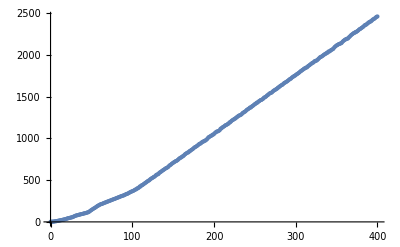

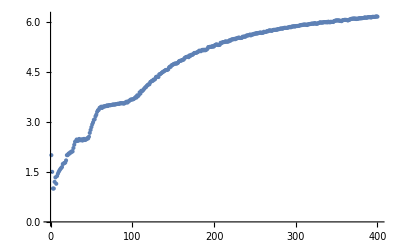

```mathematica
zeroCycleLoadA=;
ListPlot[zeroCycleLoadA]
ListPlot[{#[[1]], #[[2]]/#[[1]]}&/@Rest@zeroCycleLoadA, PlotRange->All]
```

We can see this phenomenon here. The first curve shows accumulated time in blue, the second (noisier) curve shows the average time per load/store over longer and longer runs. 
When we don’t do many load/stores (at the left end of the curve) we get higher performance (lower cycle count for a single pair of load/stores). This is just because the machine is rapidly dispatching the instructions into various queues, and is then able to execute independent groups of these instructions in parallel; it’s not “really” executing any particular sequential set of load/stores faster. 
Long term (past about 80 or so) once all the buffers have filled up, the time to execute a store/load pair of this form seems to takes ~6 cycles (three for the store, then three, maybe four for the load). 

OK, that’s familiar and as expected. A forced sequential set of load/stores indeed operates sequentially. 

Now lets make a slight change to the probe by adding a DIV
( STR x1, [x1]; LDR x2, [x2]; DIV x2, x2, x10 )  where x10=1.
Naively we would expect this to take 3+3+8=14 cycles, but that’s not right.
The critical path is the load to DIV path, 3+8 cycles. While that is happening, the next store can happen in parallel with the DIV, but the next load cannot happen until after the DIV completes. 

And this is what we see

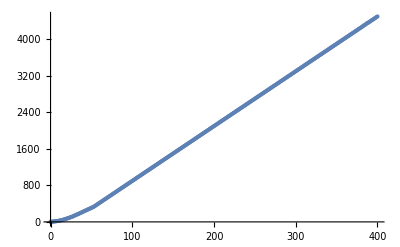

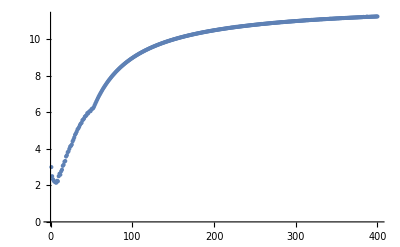

```mathematica
zeroCycleLoadB=;
ListPlot[zeroCycleLoadB]
ListPlot[{#[[1]], #[[2]]/#[[1]]}&/@Rest@zeroCycleLoadB]
```

Long term, the cost for the probe is 11 cycles. 

Now the fun stuff!
Make one small modification of the above, to ( STR x1, [x2]; LDR x2, [x2]; DIV x2, x2, x10 ).
The difference is that it’s now obvious, at decode time, that the store and load happen to same address (because both use [x2]; in the earlier case the addresses were [x1] and [x2], and the front end could not know that x1==x2. 

This difference means that 
- the front-end can speculate (ie ZCL) as to the value that will be loaded into x2 by the LDR, and can immediately feed it to the DIV
- then the validation of this speculation can happen in parallel with the DIV
So we should be able to shave some cycle off the loop time because the critical path 
load (3 cycles) ->DIV(8 cycles) has been converted to (DIV (8 cycles); load happening in parallel)

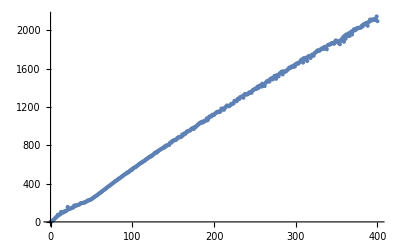

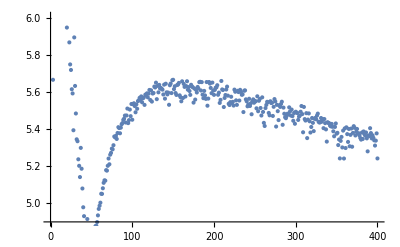

```mathematica
zeroCycleLoadC=;
ListPlot[zeroCycleLoadC]
ListPlot[{#[[1]], #[[2]]/#[[1]]}&/@Rest@zeroCycleLoadC]
```

And that’s what we see! In fact it’s even better than expected. We expected the probe cycles to drop to 8 (cost of a DIV) but in fact the machinery that’s injecting the ZCLs (the speculated value for the load) is able to break the dependency chain so that successive DIVs can execute independently, not sequentially! 
The point that matters is that we see (once the conditions for the 2012 patent are met) a substantial speedup. The conditions for that patent are that the store and load address have to match (as registers) so that we can match them in the front end. 

How can we be sure the 2012 patent is the mechanism, not something else?
Change the probe to  
( STR x1, [x2]; LDR x2, [x2]; DIV x2, x2, x10; 
ADD x2, x2, #8; BIC x2, x2, #16 )
Now we are doing two things to the address
- we increment it by eight each cycle but we also
- wrap it around when it exceeds 16. So we alternate x2, x2+8, x2, x2+8, ...
Any sort of simple address tracker (constant address or constant stride) will be fooled by this, but the 2012 ZCL is not; it does not care about how x2 changes, only that the load and store reference the same [x2].

The flow is confusing! So let's make a slight change that clarifies things a little. This change still runs fast, but the registers are now a little clearer. 
( STR x1, [x2]; LDR x9, [x2]; DIV x2, x9, x10 )  
What matters is that 
- the store and load share a common address [x2]
- because of that common address register, the ZCL can rename x9 to the physical register associated with x1

- the register name x9 is irrelevant to anything
- we need to add a delay (some work) to show that x9 is being generated faster than expect, that's the DIV
- the DIV has to generate a value that's used by the earlier instructions other each block can simply run in parallel, there is  no forced serialization

(As a technicality, I’ve described the boost we see in terms of the 2012 patent, but for technical reasons I think what’s actually relevant is the 2019 patent.
The 2019 patent handles load and store referencing the same register in the same cycle (ie same decode block). 
We can force the 2012 patent by inserting 8 NOPs between the store and the load, so they decode in subsequent cycles. In that case we are using the classic 2012 patent, and things get even better; now we run at 3 cycles per probe rather than about 5.5! 

Slightly fancy addresses like [x2, #8] are handled appropriately. 
But not addresses that depend on two registers, like [x2, x10]. 
Likewise not store pair+load pair.

Maybe I misunderstood the 2018 updated patent; I thought that meant minor changes (add, sub immediate) of the base register would be tracked and handled appropriately, but I could not see that in action.

What if we set the DIV result to x1 rather than x2, so that the store value, not the load/store address, is blocked by the DIV? 
I think in principle this could work, though it would run at 8 cycles (DIV speed) without being able to run subsequent DIVs independently. But in practice the implementation does not seem willing to catch this case, and it runs at 12 cycles.

The DIV case is very nice because it’s incontrovertible proof (IMHO) of a ZCL kicking in. 
Now that we know that that particular ZCL works, we can use a similar pattern to try to test other ZCLs (which are less convincing as ZCLs per se, except that they do or don’t show faster behavior than expected when matching a particular type of pattern. 

So, suppose we remove the DIV, giving us the probe ( STR x1, [x2]; LDR x1, [x2]).
In particular compare two probes, ( STR x1, [x2]; LDR x1, [x2]) and ( STR x1, [x2]; LDR x1, [x1]).
I know your eyes start to glaze over! But think about it. The value that is loaded each time is then stored (load data register is store data register). So every store has to happen after every load. Likewise every store has to happen after every load (same address value, in both cases, because x2=x1).
But the first case, with the load and store registers based off the same address register (ie address= [x2] ) makes the equality visible to the front end, so ZCL can kick in. The second case is identical as far as the LSU and LSDP are concerned (the two addresses of interest, [x2] and [x1] are identical) but it’s different as far as the front-end is concerned. 
And indeed the first case uses ZCL and runs at ~5 cycles/load/store; the second case doesn’t use ZCL and runs at ~7cycles per load/store. 

The value of this pattern is now we can ask what happens if we try similar patterns. 
Compare now  ( STR q0, [x2]; LDR q0, [x1]) 
this has the same structure of load has to follow store (because of the same q0 register) and store has to follow load (because of the same target address); and so it’s no surprise that it runs at ~7 cycles per load/store. 
If we change this to ( STR q0, [x2]; LDR q0, [x2])  
then, in principle, the front-end could notice that the address registers are the same and ZCL the q0 value given to the load. But that does not happen, we get the same ~7 cycles per load/store. 

The graphs below show the ZCL integer case, and how the long term performance (with some weird noise!) seems to tend to about 5 cycles per load/store.

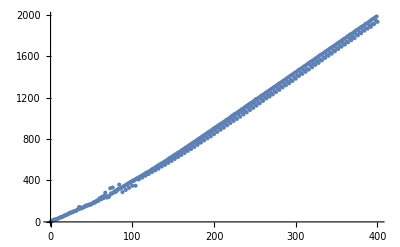

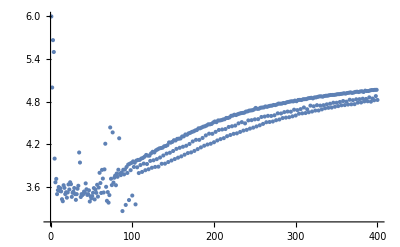

-Graphics-

```mathematica
zeroCycleLoadD=;
ListPlot[zeroCycleLoadD]
ListPlot[{#[[1]], #[[2]]/#[[1]]}&/@Rest@zeroCycleLoadD]
```

#### stack loads

Now that we know what to expect from the previous example, we can do the same sort of thing with stack loads. Consider 
( STP x28, x27, [SP, #-16]; LDP x28, x27, [SP, #-16] ) which is more or less what we see at function prologues and epilogues.

-Graphics-

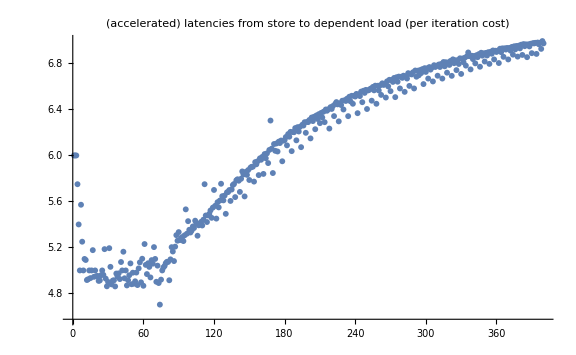

```mathematica
stackZeroCycleLoad=;
ListPlot[stackZeroCycleLoad,
PlotLabel->"(accelerated) latencies from store to dependent load",
PlotLabels->{"stack case"},
ImageSize->Large]
ListPlot[{#[[1]], #[[2]]/#[[1]]}&/@Rest@stackZeroCycleLoad,
PlotLabel->"(accelerated) latencies from store to dependent load (per iteration cost)",
ImageSize->Large]
```

Well that’s disappointing! We seem to take 7 cycles to perform the load/store, just as before, so no acceleration. 
Well...
Remember the fine print! It’s only the magic of the 2019 patent that allows ZCLs to kick in for load/store that happen in the same cycle. And there’s no real reason to work this hard on the stack engine, because the load / store pairs that we want to accelerate will live in different function prologue/epilogues, and will likely be separated by at least one cycle of intervening code (unless the code is very strange). So let’s run the same probe, but with 8 NOPs after the store, and another 8 after the load.

-Graphics-

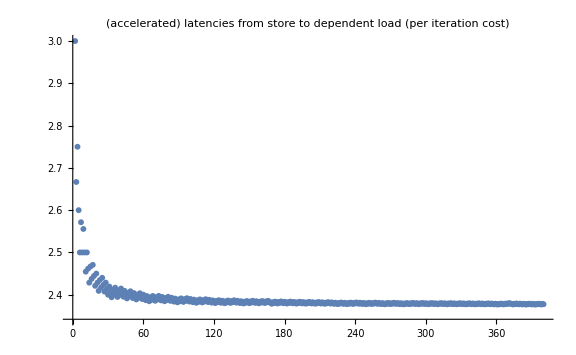

```mathematica
stackZeroCycleLoadB=;
ListPlot[stackZeroCycleLoadB,
PlotLabel->"(accelerated) latencies from store to dependent load",
PlotLabels->{"stack case"},
ImageSize->Large]
ListPlot[{#[[1]], #[[2]]/#[[1]]}&/@Rest@Rest@stackZeroCycleLoadB,
PlotLabel->"(accelerated) latencies from store to dependent load (per iteration cost)",PlotRange->All,
ImageSize->Large]
```

That’s more like it!!! Nice acceleration there!

What if we add in storing then loading a pair of SIMD registers?
Once again that case doesn’t seem to be accelerated.  (I test FP/SIMD in these cases out of interest, but it’s unsurprising that Apple doesn’t accelerate them. Most FP/SIMD work is about throughput, not about latency, so spending area and power on functionality that reduces the latency of FP/SIMD loads is probably not a wise investment; better to spend on improving SIMD throughput.)

A different discussion of this pattern of ZCL (stack-like, even if not on the stack) is given in https://zhuanlan.zhihu.com/p/595582920
Unfortunately this site requires registration (easiest done if you have a WeChat account). If you can register, then machine-translation does an adequate job and you can see that his, somewhat different test code leads to the same sort of conclusion.

## Acceleration via Faster Address Calculation

The mechanisms discussed so far make loads faster by retrieving data from unexpected places (the Store Queue or the Register File).
A second way we might make loads faster is if we can more rapidly construct the address used by the load.

### 2013 patent (pointer chasing)

Our first technique ties both these ideas together, 2013 https://patents.google.com/patent/US9116817B2 Pointer chasing prediction.
Consider pointer chasing code, ie code that looks like node->node->node->data, which will compile to something like 
LDR x3, [x2]
LDR x4, [x3]
LDR x5, [x4, #8]
Performance is limited by how fast the address of the next load is acquired by the previous node. 

Consider the scheduling of the second load. We want to send the load to the LSU at the earliest possible moment that its dependencies are satisfied (ie it has access to the value of x3)  but no earlier.
The most cautious solution is to wait till the value of x3 is in a register, read it from a register, and base the scheduling on that.  That makes sense if a physical register, in this case for x3, is the only available source for a value (eg for values that were calculated many many cycles ago) but not otherwise. 

A better solution is to pull the value of x1 off the bypass bus. Remember that there's a (very wide!) bus connecting every execution unit with the register file to transfer calculated values to their destination register. If these values are appropriately tagged, and the scheduler appropriately matches tags, it can grab the values required for an upcoming instruction off the bus at the moment it's needed. 

But that's still not optimal in the pointer chasing case! The fundamental insight is that there is one more place where data could be made available to the load – internal to the LSU.
The value is available in the LSU, but then has to be transported to the bus, moved over the bus, read, then transported back to the LSU. 
So even better is to guess that the value will be available in the LSU at the appropriate time, and simply fire the second load into the LSU. If everything works out correctly, the request to execute the second load (which begins with an adder in the LSU that adds an offset, in this case 0, to the value of x3) will arrive at the adder just as the value of x3 arrives at the adder, fresh from the L1 cache; and the secondary load begins its execution one cycle earlier than it would have been if it had to wait for the value of x1 on the bypass bus. 

The patent suggests this is handled as a predictor, caring about the combination of 
- a load that depends on an earlier load 
Presumably the fundamental scheduling trick here (although Apple gives no details) is to track in the LS Scheduler that the three most recent loads are each generating register pA, pB, and pC; and to test if any of those three registers match the base register of the next load. 
and
- the earlier load will hit in the L1 cache as opposed to the Store Queue. This is necessary because, see the diagram below, we’re speculatively scheduling the cycle in which when the second load can issue. This is done by using the data in the Load Store Dependency Predictor. 
Like any scheduling speculation, this can fail, in which case we Replay the second load.

A year later in 2014 (so now A7 generation) https://patents.google.com/patent/US9710268B2 Reducing latency for pointer chasing loads we  we improve this in a few simple ways
- we also allow a store that’s dependent on an immediately prior address load to use the mechanism. 
Not that essential for performance, but easy, so why not?

- we now understand that we are using the LSDP in this additional (pointer chasing) way and we allow pointer-chasing failure cases to also train the LSDP predictor
We also get this nice LSU pipeline diagram that helps clarify timing of the different components (remember, again, this is A7 generation; M1 certainly differs in some details because it takes one cycle less).

-Graphics-

In a way way this predictor business is required because a value looked up in the Store Queue is only available half a cycle after it’s looked up in the L1D. It seems feasible that you could get the timing of these two to coincide (especially if you look up in the Store Queue by virtual address so start it in parallel with TLB lookup) in which case you could still get the value of the patent (detect back-to-back loads and schedule the second load one cycle earlier) without requiring the predictor part. 
You still need to validate Store Queue probing by physical address for the rare (but allowed, sigh) cases of virtual address aliasing, so this might mean twice as much probing of the Store Queue, though I could imagine ways around that. (Essentially split the Store queue into two parts tied together by a common “Entry Number” and have one probed by VA, the second part probed in the next cycle by PA.)
It’s unclear where M1 sits in this respect, though there is value, explained in the Memory Volume, to accelerating Store Queue lookups.

### 2017 patent (strided load address prediction + pre-execution)

#### some theory of value prediction

A second way we might know the address faster is to guess! In other words, once again, we use a predictor. This class of predictor is called a Value Predictor, more precisely an Address Predictor. A recent discussion of the idea is here (2017) https://www.researchgate.net/profile/Rami-Sheikh/publication/318283615_Load_Value_Prediction_via_Path-based_Address_Prediction_Avoiding_Mispredictions_due_to_Conflicting_Stores/links/59b26eea0f7e9b37434e7036/Load-Value-Prediction-via-Path-based-Address-Prediction-Avoiding-Mispredictions-due-to-Conflicting-Stores.pdf Load Value Prediction via Path-based Address Prediction: Avoiding Mispredictions due to Conflicting Stores. 

Being such a recent paper, this is full of interesting ideas! 
The “easy” part is the idea of how their address predictor works, based on the path (sequence of PC’s) of prior loads. They claim this load-path history is a high quality predictor (cf the use of paths in branch prediction), and let’s assume that true. 

More complicated is how you might implement a value predictor generically. Speculation always generates the question of how you backtrack; in the case of value prediction you would like something as lightweight as Replay, but (by definition of how value prediction works!) the predicted value has to be stored in a register, so somehow you have to deal with that. This may seem like a Replay situation, but if you work through some cases (think for example of a pointer chasing scenario) you will see problems arise because we start with an incorrect register value, and there’s no “natural” way to fix that once the predicted value has been evaluated and found to differ.

They suggest doing this via a second pool of registers, dedicated to speculation, and a bit (or some other mechanism, like physical register numbers above a certain value) in the rename map that indicate a register comes from the speculation pool or the general pool. 
As I understand it, their idea is: an instruction  at Rename time
- has a Speculation Register pseudo-allocated as its destination (ie marked as the destination in the Rename Map)
- holding the speculated value
This means subsequent instruction can read the speculated value.
- but the instruction actually also gets allocated a standard physical register so that when it executes it writes to that physical register (which has been allocated, but is not "visible" to any instruction via the Rename table)
- at some later point after Execution, 
+ physical register is compared with speculation register
+ modify the entry in the Rename table to point to physical register and free the speculation register
+ if the two don't match force a Flush starting right after the instruction whose value was speculated.

Much of this is not ideal and somewhat hand-wavey, and I think it's the elided details that have resulted in Value Prediction still being considered an idea for the future, even though it was first proposed almost 25 years ago. No-one denies that the idea has potential; it's just that every proposed actual implementation always seems to be based on how machines used to operate, and is no longer a great match for the way they operate at the time of the proposal. 
It's particularly frustrating that we have to Flush rather than Replay. Flush is heavier weight than we really need; it start by reloading the instructions all the way from I-cache, but the instructions we have are correct!  We just need to connect them to a different set of input values. That looks like Replay, but the details differ. It's important to understand why.

For Load Replay we have a situation like
- dependent instruction refers to a physical register for one variable, the load (via a SCH#) for the other variable
- the dependent reads the load value from the bypass bus via the the SCH# dependency
- after the dependent tries to execute, and is held [prevented from completing, retained in the Scheduling Queue] it can sit in the Scheduling Queue until the load completes, re-asserts the appropriate SCH# line, and the load value again read off the bypass bus.

For Value Speculation Replay we have a situation like
- dependent instruction refers to a physical register for one variable, a speculative register for the other variable
- the speculated instruction executes and places the correct (non-speculative value) in a physical (non-speculative) register
- but there is no connection between that register and the speculative register AND 
- there is no natural mechanism to change the register dependencies and suchlike of the dependent instruction so as to re-execute it.

However I think this is manageable within Apple's framework, by re-conceptualizing the problem. Rather than thinking of cleanup as somehow moving the correct value to the appropriate register and trying to force instructions to re-read that register, what about thinking of cleanup as forcing an additional dependency? The idea I have in mind (which seems feasible from the outside, but of course we don't know the internal details!) is 
- a speculated instruction carries not just a dependency bitvector but also a "speculation-dependency vector" which encodes the SCH#'s of the instruction(s) on which it speculatively depends.
The idea then, is 
- a dependent instruction is held in the Scheduling Queue like with Load Replay
- when the speculated instruction notices a speculated value mismatch it sends a notification and the correct value over the bypass bus
- if that matches the SCH# in the  the speculation-dependency vector, then the value can be captured off the bypass bus and steered to override the register-based value that was captured earlier. 
(Of course this requires details we don’t know, like how it’s indicated that a particular SCH# dependency should feed a value to the first, second, or third dependency of a particular instruction...)

The above is all background to the patent below which is, essentially, a value speculation patent.

#### apple’s value prediction patent

Apple's idea, (2019) https://patents.google.com/patent/US20210049015A1 Early load execution via constant address and stride prediction, is to track the address that is generated by any particular load (ie note the stream of addresses generated by a load with a particular PC, presumably in a loop). If this stream of addresses forms a linear sequence then we can reasonably predict what the next address will be. And once we know what that next address will be we can 
- execute the load early behind the scenes
- record the value in a physical register
- rename the destination register of the load at Rename (the usual ZCL) 
- validate by re-executing the load at the correct time, based on the actual values at the correct time. 
(Do we have to re-execute the load? In principle perhaps we can use the Load Store Queue mechanisms and the Poison mechanism to detect if the load address has had its value changed. If that's possible, then all we need to do is validate that the load address matches our speculated load address.)

This may sound like a standard stride prefetcher, but remember the prefetcher gets data into the cache early; we are interested in the next level of getting data from the cache into a register early.

If you looked at the previous diagram for the RF/SP-LSDP pipelines, you saw that, for whatever reason, Apple wants the different predictors to run at different pipeline stages. 
They're close to running out of stages at this point, but, no fear! We can move this prediction all the way back to where the Fetch Address is predicted!
That gives us time to perform the load (based on the speculated strided address), and have the load value available for ZCL by Rename.

-Graphics-

## Experiments

### testing pointer chasing (success)

The easiest case to test is pointer chasing loads. 
Initialize with 
STR x2, [x2], and MOV x0, #0; 

then compare repeats of:
LDR x2, [x2]
with 
LDR x2, [x2, #0],    LDR x2, [x2, x0] and LDR x2, [x0, x2]

All of these perform the same task of repeatedly following a pointer (that points to itself). But some versions of the instruction are (we believe, from the Apple patent) susceptible to pointer chasing acceleration and should take three rather than four cycles per iteration. 

The second case (adding an immediate to the basePtr) is not completely trivial to code because an immediate of 0, as I have written it, encodes to LDR x2, [x2]
To test an offset I’d have to use a more elaborate setup that pre-initialized an entire array of pointers. But I’m pretty confident what the result would be; if you don’t believe me do the test yourself!

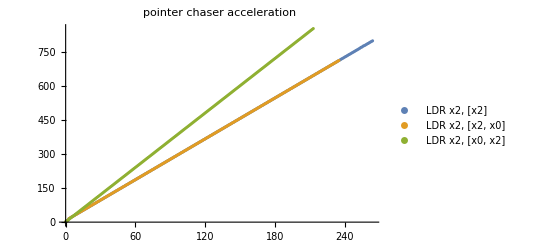

```mathematica
pointerChasingA=;
pointerChasingC=;
pointerChasingD=;
ListPlot[{pointerChasingA, pointerChasingC, pointerChasingD},
PlotLabel->"pointer chaser acceleration",
PlotLegends->{"LDR x2, [x2]", "LDR x2, [x2, x0]", "LDR x2, [x0, x2]"}]
```

We see the accelerator in action. Pointer chasing that feeds the pointer into the first argument (the base pointer) runs at 3 cycles per load, as opposed to normal load loops (and pointer chasing done by someone who doesn’t understand ARMv8 assembly) which takes 4 cycles per load.
Later below I tested other variants of this  and complex addressing works; even load pair works as long as the pointer being chased is (like above) the first pointer of the pair.

### testing stride address prediction (failure)

I was very excited to try the address value prediction patent, but I could find no example for which it kicks in. Like the load after load ZCL, it’s easy to fool yourself that some sequence of code is faster than expected because of this ZCL, until you think about it more carefully and realize it’s just extreme OoO to the rescue!
So my tentative belief is that, in spite of the patent, this is not present in M1.

Some time after writing the above I read (2017) https://www.researchgate.net/profile/Rami-Sheikh/publication/318283615_Load_Value_Prediction_via_Path-based_Address_Prediction_Avoiding_Mispredictions_due_to_Conflicting_Stores/links/59b26eea0f7e9b37434e7036/Load-Value-Prediction-via-Path-based-Address-Prediction-Avoiding-Mispredictions-due-to-Conflicting-Stores.pdf Load Value Prediction via Path-based Address Prediction:
Avoiding Mispredictions due to Conflicting Stores which is a nice overview of (elements of) the problem. 
The details of the paper are most relevant to Qualcomm, what matters is that it clarifies various points that seem implicit in the idea of Value Prediction via Load Address Prediction. In particular it states without equivocation, and with some useful numbers, that 
- for the most part the most useful values to speculate, if you go down the path of value speculation, are the result of loads (for the obvious reason that these are higher latency, even to L1, than most integer operations) 
- trying to speculate the value of loads is somewhat feasible, but requires tracking when an intervening store might have flipped the value at an address
- trying to to speculate the address of loads is more feasible (more likely to be useful). You can certainly track addresses that are static (constantly reloaded  globals, or function A keeps storing a value read later by function B; Apple extend this to also handle the case of running along arrays loading successive values) BUT 
+ the load (occurring early in the pipeline, probably triggered by the PC) has to be validated later at the correct load time, so each speculated load results in two hits to the load unit and cache

If we accept the above (at least in a first implementation, and don’t assume Apple has hooked up additional machinery to bypass the second, validating load [eg record the relevant addresses, and check for stores or cache activity between the speculated load and the executed load], this has various implications. The most obvious is that even if you are very confident in your speculation, this is not worth doing if your code is throttled by load/store activity, because you’re simply doubling that activity! So along with the functionality discussed in the paper, you also need something to track the level of load-store activity. 

This in turn has implications for how you test for this functionality. I was testing it as an extension of the other ZCL activities, which I now think was the wrong starting point. A better framework would be to test it as a way to reduce the latency of a “single threaded” lane of execution. What I mean by this is you want a flow that looks like 
- rA=IDIV(value, value#) [where value is varying and value# is set, to a little larger than value], so this result is always 0
- value=LOAD rA
-rA=IDIV(value, value#)
- value=LOAD rA
etc so no OoO is possible, each instruction depends on the previous one. 

This is our starting idea, but this bundles multiple loads into the same Fetch or Decode group, which means that a single Fetch or Decode PC “implies” multiple loads, and that could be a problem. If this is considered an optimization only relevant when load/store activity is limited, the machinery may only kick in when there is only one load in a Fetch or Decode group...
So the next step would be to pad the above idea to one IDIV+LOAD per decode group (now up to 10 in M4), possibly with NOPs, more safely with something like rA+=1; rA-=1; over and over as padding requires. With all this in place (and repeating a hundred or so of the above idea before we loop back) we can compare the expected latency of one block to the measured latency; if everything is working then we should see an effective latency of maybe 4 less than we expect (ie zero-cycle load). Finally we could modify one of the rA+=1 to something like rA+=9 to move to the next INT64 (on an array filled with “value”), to simulate walking an array, and see if we get the same (ZCL-reduced) latency for the loop. 
Before starting down this path, we will want to test a few things which could confuse the issue! 
Does the divide take as long as we expect? (Is there an early out where it just tests if value<value#?) We might need to have the ratio be some random number, and then subtract that number from rA? Or maybe use an FDIV followed by a convert-to-integer?
Do the rA+=1 and rA-=1 take one cycle? Or does our target chip (like the newest Intel chips) perform short adds at Rename? Maybe we need some nonsense like rA>>=1; rA<<=1 to avoid Rename shenanigans?

(When the address is unchanging, we could be hooking into one of the earlier defined ZCL’s, which can reuse an already loaded value, or a stored value, in a recent non-overwritten register. Which is nice, but not what we’re testing for! Once the address is linearly increasing then we know we have in fact address prediction happening. At which point we can test things like varying strides, negative strides, etc).

Now that we have an overview of the idea of Value Prediction via Load Address Prediction, we can ask how to improve it. An obvious direction of improvement is to go backwards! We want to predict the address in those cases where it makes sense (either the value at the address frequently changes, or the address keeps changing because we are walking an array). But when neither of these are true, if we predict the value that will be loaded, we can avoid the costs of the (first) load, ie energy and taking up load bandwidth, and we only need to execute the second load (to validate the prediction). 
As you will see below in the “what’s new” section, this functionality appears to have been added to the M4. As always when looking at patents, maybe the M5? Maybe the idea didn’t work out? What the patent describes is how to use a single joint table to perform the training of a Load Value Predictor such that the table can store either Values or Addresses; obviously being able to share a table makes such a table cheaper and thus makes it a little more desirable to have both such predictors.

Yet a third way to handle this issue is to base much of your prediction machinery on the existing branch predictor machinery. This is the idea behind VTAGE. VTAGE is not as powerful as the scheme described in the Apple patents, or in the paper referenced above – but it is cheaper. Which means it might be a good choice for E-cores, if the performance benefits are worth the area and energy costs.

## Academic ideas for improving load performance via criticality

The LSQ is an expensive structure, and loads in general are both difficult but vital for performance. Can we do anything smart to reduce their costs?
One interesting set of ideas, written up in (2009) https://citeseerx.ist.psu.edu/document?repid=rep1&type=pdf&doi=bdabca9a89f7ca0d673020642530eb29f3190650 Criticality-Based Optimizations for Efficient Load Processing discusses the use of one my favorite not-yet-implemented ideas, namely criticality. (This is an Intel paper displaying, like so many Intel papers I’ve referenced, that casual disregard for good ideas that has them where they are today...)

The paper starts by suggesting that while some people think it’s too expensive and complex to implement a generic instruction criticality predictor, you can easily implement a simple “load criticality” predictor. This only applies to loads, and does not, in the strict sense, track criticality, rather it tracks an easy, but good-enough, proxy for criticality, namely how many instructions use the value loaded. (The paper discusses a separate table for tracking this, but I suspect in Apple’s designs you can just use the register reader-reference count for this purpose.) You can then define a load as critical if this count is larger than a certain value (eg 5). 
Now that you are able to segregate your loads into two streams, critical and not, what can you do? The obvious answer is to schedule critical loads first, and that certainly results in value. But there is more you can do. For example 
-the whole LSDP machinery, testing loads against earlier store addresses, and predicting whether unknown addresses collide, is not cheap. If a load is not critical, how about we just avoid all this and delay the load until we can be sure there is no load/store dependency? Some energy saved at very little performance reduction.
- if a load is non-critical, does it make sense to be prefetching into the L1 based on this load? Maybe such loads should prefetch to L2, but wait for the actual miss from L1 to move the data to L1? Once again we save some energy at the cost of very little performance.
- we can even use non-criticality to inform the data residence in L1. If the data is not critical, maybe this line should be tagged as first to be tossed when life gets tough and we need to remove lines from the L1 cache?

## “Load-like” acceleration

Everyone asks about and expects that Apple will at some point add SVE/2 to their cores. Above I’ve discussed some of the issues and alternatives to that, including the option of going with Macroscalar. 
But there are other, outside the box, alternatives to get some of the same value. For example one way to use SIMD (which becomes limited with SVE) is for table lookup and data permute type operations. 

One interesting way to improve this type of work is, rather than trying to build a wider data rearrangement network via SVE, accept that we have a good data rearrangement network already in load/store. 
	The problem with load/store is that normal load/stores execute to global address space which 
- has to be coherent, 
- is paged 
- and has various other complications, which make using it somewhat energy/area expensive, and of limited performance.
 	Alternatively we have register space, but the problem with registers is that they cannot be indexed into, which prevents their use for all sorts of particular algorithms. 

What if we had the best of both worlds? Imagine something like a 32kB SRAM that forms an address space specific to a core with 
- no relationship to the outside world (like registers), but 
- byte addressable and highly banked (so with multiple simultaneous and low-latency loads and stores possible)? 
Without the concerns that require a deep load/store queue and a TLB, it should be possible to load and store multiple values into this storage with perhaps 2 cycle latency. 
This is analogous to similar functionality (the Threadblock storage) available in GPUs. 

Like with GPUs, this local address space can’t solve all problems, but there’s a wide range of problems where you 
- can solve a small version of the problem in (probably NEON) registers; 
- aggregate those results to a mid-sized version of the problem solved in this local address space; 
- and aggregate multiple of those mid-sized solutions successively in global address space. 
As always, the larger the fraction of such work you can do locally (in this 32kB local SRAM, without the costs of MMU or snooping) the more time and energy you can save...

I suspect this is an idea it’s worth looking into by both Apple and ARM.

# New material since version 0.90

I’m going to record here various interesting things I’ve discovered since 0.90, but without expanding on them much since my time is limited.

New in A15:
Dougall has so far discovered in the A15/M2 the following differences: https://twitter.com/dougallj/status/1534002276091629569
- ~10% smaller ROB and some other structures, slightly larger load/store scheduling queue. Probably these were slightly rebalanced/optimized based on traces from the A14/M1
- better memory latency in some situations. Could this be the long sought stride address prediction I could never find on the M1?
- some special purpose registers (TPIDRRO_EL0, used by multiple threads within a single process to access thread-local data) are made faster
- ADR/ADRP, used to access global data, made faster (now handled at Rename, like MOV immediate)
- Blizzard (the small core) is now 5-wide rather than 4-wide, with a 33% larger ROB and probably other substantial expansions. “Small”, but probably already more capable than the good old A7 Cyclone that really got Apple into the CPU game!

New in A16
When we get to A16 there seems even more slight tweaking of structure sizes.
For the basic ROB rack (unit of 7 slots, one of which can be a failable instruction) we have 
- for P cores: about 330 for M1, 290 for A15, and 270 for A16. 
- for E cores: about 60 for M1, 75 for A15, and 108 for A16.
These are substantial reductions, which suggests that perhaps the structure has changed. (For example a “rack” may now hold 8 rather than 7 instructions? Although dougall suggests this is not the case, that NOP measurement still gives a 1:7 ratio). Ultimately, remember, usually the real constraint is the number of physical registers; growing that is hard while growing the number of ROB entries is easy. It could be argued that the M1 had more ROB entries than was justified by the number of physical registers, and so this rebalancing makes sense. 
Remember also that Apple’s constant trick is to split a structure that performs two tasks into separate structures each optimized for one task. Tying a single ROB rack to the task of both tracking one failable instruction (branch or load/store) and some non-failables goes against that philosophy. Maybe they split the ROB into two separate pieces for these two tasks, so that long runs of failable or non-failable instructions don’t “use up” slots for the other type of instruction, allowing the overall number of slots to shrink even though the ratio remains 1:7?

NoC (multiple independent networks)

(2021) https://patents.google.com/patent/US20220334997A1 Multiple Independent On-chip Interconnect
	Split the existing NoC (which is already multiple networks, for address vs data, with a separate network for IO/interrupts) into multiple “address+data” networks. Examples might be an IO network (ordering, coherency, high latency), a CPU network (ordering, coherency, low-latency) and a GPU/NPU/ISP network (relaxed ordering, non-coherent). These might also have different topologies. 
	We see an example here: 
	-Graphics-
	The IO network is represented by the solid lines (marked as 40), the CPU network as the dashed lines (marked as 38) and the GPU network as the dotted lines (marked as 42).
	The obvious win is in power (each network can be optimized for its task, so that eg the GPU network can devote substantial resources to bandwidth management, while this is probably less necessary for the IO and CPU networks); but of course there are simply more network resources available which presumably helps performance under extreme conditions (ie all of IO, CPU and GPU working hard).

A revised version of this patent, (2022) https://patents.google.com/patent/US20230239252A1 Segment to Segment Network Interface, contains much the same material, but lays greater stress on each of these independent networks being hierarchical, in a very particular sense of being somewhat like the Internet. The idea is that a local network knows essentially two things – how to perform local routing, and how to hand-off a packet with an unknown address to a “long-distance” router. This limits the knowledge the local network is required to possess as to the structure of the overall chip and overall network. 
	
	Somewhat related is (2021) https://patents.google.com/patent/US20220365896A1 Transaction Generator for On-chip Interconnect Fabric, which is mostly about testing, but which reveals a few more NoC details, like how the NoC is split into a local level (think IO or CPU cluster), often different, and each optimized for the characteristics of the cluster, all connected by one of the above three global networks.
	One of these local networks is described in more detail in https://patents.google.com/patent/US20220237028A1 Shared Control Bus for Graphics Processors. Now the GPU network itself is a two level ring bus, the higher level communicating between GPU clusters (these could be entire chips like an Ultra, or possibly units of say 8..10 GPU cores), the lower level communicating between cores within a cluster. 
	
	Also in this vein is (2021) https://patents.google.com/patent/US20220365900A1 Programmed Input/Output Message Control Circuit. Mainly I like this patent because it clarifies so many things previously seemed correct but were unclear. It clarifies that we need a special way to address low-level hardware (for example to configure a particular switch in the NoC) in a way that cannot easily be handled purely by addresses based on memory locations, and that this addressing is called PIO. It also points out some less obvious points, namely that this mechanism (required at the least for startup/reboot, and for debugging) needs to work before fancier machinery like credits or perhaps even routing tables, have been set up. 
	One way to do this is via a separate network which doesn’t have to be very sophisticated, but which will take some area. An alternative is to add some lightweight additional storage and logic to every “memory controller” (by which I think they mean “memory-address-based buffer/router”) that treats PIO as a special case. This side logic buffers PIO transactions and sends the transactions to the correct place via slow, but simple and reliable, mechanisms, for example using broadcasts and simple sequencing/flow control (not allowing a new transaction till an existing transaction is complete). The details are uninteresting past the main point, that we replace the area of a separate PIO network with what I assume is the smaller area of a distributed “PIO mode” attached to each node in the main network. This seems analogous to the way interrupts were also moved from more of a separate dedicated network to more of a special type of packet on the main network. 
	
(2021) https://patents.google.com/patent/US20220342588A1 Address Hashing in a Multiple Memory Controller System
	In the first place this confirms an obvious point – that the physical memory address space is hashed then spread over multiple memory controllers; but it gives some details as to how the spreading is done so that the most common patterns (ie sequential-like streams) are maximally spread so as to make best use of the full NoC bandwidth at every level. More interesting are two other points:
	- after each routing decision is made (to a particular chip, then a particular slice, then row, then side; and also for subsequent routing internal to the memory controller to different sub-structures within the DRAM chip) the address bit(s) that forced that routing decision are dropped, because they’re no longer needed and moving/storing them takes energy. Maybe not a massive energy saving, but a cute idea!
	-Graphics-
	On-chip machinery is tracking how busy each memory controller is. Every so often this business is reported up to the OS, which also knows the total physical memory footprint in use. Based on these, certain memory controllers can be shut down (to save energy, of course) in low usage situations. If there are a few pages that are still being used, those pages will be migrated/consolidated (by changing the VM mapping) onto a busier memory controller. Depending on details either the memory can be completely shut down (not being used at all, all modified pages migrated to another controller) or the memory can be placed in self-refresh mode until access is required. Presumably there’s also some input from the IO system as to how much memory being used as page cache is really valuable, but that’s not described. 
	
	There are a few patents in this vein, handling various technical aspects of a multi-die system like testing and debug. The most interesting is probably (2021) https://patents.google.com/patent/US20220365579A1 Die-to-die Dynamic Clock and Power Gating which talks about how, before any die is shut down (or similar changes) all the other dies are queried to see if there are pending transactions targeting the relevant die, and if so the transition is delayed till those are cleared. 
	
(2022) https://patents.google.com/patent/US20220318136A1 I/O Agent
	We’ve seen multiple patents that try to mate the relaxed semantics of Apple Fabric with the specific rules for different IO buses. This patent seems to be the final answer to solving the issue once and for all. The idea is that each bus with particular rules is placed behind and IO agent and talks only to that agent; the agent mediates between the IO bus rules and Apple Fabric rules.  In particular the IO agent is able to act in a cache-like fashion, in that it has a small local buffer (“mini-cache”) and understands the SoC coherency rules. Rather than sequences of Io transactions being forced to route all the way to/from SLC and to complete one at a time at some small width (anything from 8b to 64b) the IO agent is able to request the relevant line from DRAM/SLC, modify it locally, and hold onto it in the expectation that multiple successive requests will probably change successive parts of this line. 
	There are related patents (2022) https://patents.google.com/patent/US20230064526A1 Ensuring Transactional Ordering in I/O Agent and (2022) https://patents.google.com/patent/US20230063676A1 Counters For Ensuring Transactional Ordering in I/O Agent which discuss, within the above framework, ways to reorder transactions for optimized performance. An example is something like if a snoop comes in that hits the IO Agent cache, the snoop reply may be delayed for a few cycles if that allows the last elements of an IO transaction using that cache line to complete, before the snoop is acknowledged. 
	
	Related is (2021) https://patents.google.com/patent/US20220357784A1 Telemetry Push Aggregation. Now these “wrapper” IO agents don’t just translate protocols and handle cache, they also gather a constant stream of statistics which are reported to the Power Manager which in turn sends messages to the IO agent to sleep or change the performance characteristics (eg frequency or bus width) of various elements behind the IO agent. 
	
	Similarly we have (2021) https://patents.google.com/patent/US11550745B1 Remapping techniques for message signaled interrupts. Now the issue is the ways foreign devices can handle interrupts (eg PCIe in-band Message Signaled Interrupts). Once again the wrapper IO agent intercepts the outgoing interrupt and remaps it to the uniform scheme used by all Apple Fabric interrupts. In this case the win is not only simplicity but some security improvement in the that “raw” PCIe interrupts have an undesirable degree of access to raw DRAM.

Power 
	(co-ordinated behavior across multiple very different timescales) 
(2021) https://patents.google.com/patent/US20220137692A1 Systems and Methods for Coherent Power Management
	So far power management has been about 
- performing “fast” actions as close as possible to the IP block being controlled but
- with centralized overall control (one place to make a request that changes power states for the SoC or a sub-IP block)
This gives us what we might call “spatial” coherence (each sub-system knows what another subsystem is doing more or less simultaneously) but does not give us “temporal” coherence. This patent changes that.

 -Graphics-
  The above image gives us an idea of the issues. We see that there are four levels of control, operating at four different time scales.
  On the fastest time scale (which is still of the order of ~150 cycles) we see that the primary goal is to respond to an undervolt (UVD) event. This is done by clock dithering (preventing the clock for emitting a pulse for a cycle) which will prevent most work being done for a cycle; if this were done for, say, every second cycle on average you’d reduce instantaneous power in that block by about a half. This goes hand in hand with trying to prevent the UVD from even occurring via power estimation over the next few cycles (based on the DPE and the upcoming instruction flow). 
The next time scale up is based on varying the clock frequency within a certain range, and is controlled by tracking the current flow. 
Next up is controlling the voltage of each voltage island (which in turn sets the  range of possible frequency adjustments). 
Finally at the slowest time scales we monitor temperatures.

The point of the patent is that in the past each of these mechanisms operated somewhat independently on their separate time scales, but the patent describes ways by which each level can communicate to the central power controller what it plans to do next. Based on that, lower levels may modify their plans; for example if the stage one level up is about to increase its power delivery, eg by increasing voltage, the system one level down may alter its plans which were to reduce frequency or whatever; those plans may not be appropriate once more power is delivered. 

This sets up the background; the specifics of the patent are concerned with ultra-low power. In particular, even though (as we have seen) Apple uses sophisticated power supplies and IVRs, there is a limit to how low a power level these can efficiently supply. What to do when the system still requires power, but at lower levels than this minimum? Given all these levels of control, if we know this case is about to occur, the answer is to “coast” – we switch off the power supply and let the low power IP block(s) operate off capacitance for as long as possible; then we restore power until it has recharged the capacitors, and repeat. 

This is a patent that keeps being revised, and accompanied by the companion patent (2020) https://patents.google.com/patent/US11513576B2 Coherent power management system for managing clients of varying power usage adaptability which is much the same ideas, but operating at even slower time scales. 
Whereas the previous patent talks of timescales up to 1ms, this patent talks of timescales of 10s and 1s, and is about informing the OS of thermal/power pressure, so that the OS can take appropriate OS-level response (DVFS, changing scheduling, eg to pause background/less user visible apps, and sending thermal/performance notifications to apps so that they can, if possible, dial back their activity). 
 
For example (2021) https://patents.google.com/patent/US20220147132A1 Quality of Service Tier Thermal Control is essentially the same point (OS response to excessive power) but handled by adding an additional limit to the maximum control effort, namely the maximum extent to which we will allow the various temperature sensors to rise is set to different values depending on whether we are executing priority code vs background code. 
We could think of this, for example, as even if we are willing to pay a certain energy price for running some background services, if the mac or iPhone is currently hotter than usual, let’s run those background services at a slower rate, or even run them later, so as to allow the machine to cool down.

A constant theme we have seen with Apple is placing “adaptors” between different hardware blocks translating communication native to some block (interrupts, power reporting, clock control, etc) into a standardized form for a centralized controller. You might think we’re at the end of this, but not yet! See
(2021) https://patents.google.com/patent/US20230076507A1 Controller for Multiple Sensor Types in an SoC.
The background seems to be that in the past a single sensor type (think of, eg thermal sensors) was used across the entire SoC, but a single thermal sensor type is not optimal for all use cases. Or perhaps two or three different types were used, each type reporting their results differently?
To deal with this, the patent describes an adaptor that sits between each sensor and “the NoC” and transforms the results of the sensor into a uniform format for the rest of the chip. The adaptor handles both protocol conversion and value conversion (eg converting from raw sensor voltages or whatever, via lookup tables and mathematic transforms, into something standardized like Kelvin).

(If possible pre-calculate the next few frames to be displayed) 
 (2022) https://patents.google.com/patent/US20220413589A1 Electronic display power management systems and methods
 	More power saving. The idea is that there are some situations where the next few frames to be displayed can be predicted fairly easily in advance. (Media decode is one possibility, but another is something like scrolling, or an Apple Watch face.) Under these circumstances, the display system switches to ‘Flipbook mode”. The relevant IP blocks generate a few frames in advance stored to memory, and enqueue (time stamp, frame address) pairs in the display controller. The IP blocks can then sleep for a few frames while only the display controller and memory controller need to stay awake to handle the subsequent frame displays.

SoC
A theme we’ve seen repeatedly on the SoC is rationalization of various elements (how power is handled, how QoS is handled, how blocks are powered on and off). How far can this idea be taken? Well consider (2024) https://patents.google.com/patent/US20240160479A1 Hardware accelerators using shared interface registers, which applies the idea to “accelerators”, which can broadly be considered IP blocks, ie even things like controllers that are handling the precise voltage levels of pixels in a display. 
The patent suggests that there is value in, as far as possible, providing each IP block with a common register API so that common functionality is monitored and controlled in the same way, and lists a large number of configuration registers (some not obvious, for example registers handling boundary conditions) that could usefully be unified under a common architecture.

Another way in which this idea can be pushed is co-ordination across different chips. 
Something like an iPad has not just the SoC but a variety of subsidiary chips like display hardware, USB hardware, radios, etc. Optimal power handling requires these all be in sync, for example they can’t all increase their power draw simultaneously. (2022, based on an earlier 2020 patent) https://patents.google.com/patent/US20220382701A1 Billboard for Context Information Sharing describes some of how this is handled. 
	Sitting on a common bus with all these chips is a Coexistence Hub Device which tracks the state of all the chips. As you might imagine this does many things, but one of the things it does is maintain a “billboard”, a central repository of state for all the other chips. When these chips need to perform some change that requires co-ordination, they can first check with this billboard to see how this will affect the rest of the system. This scheme deals with the problem you otherwise face that aggressively powering down chips when they are not needed means that they miss out on general announcements of how the rest of the system is changing. If system design interests you, the whole thing is kinda fascinating in terms of (yet again) how much is offloaded from the CPU and OS, once again trying to ensure that every piece of silicon can sleep as soundly as possible for as long as possible.

Memory Controller

When we last left the memory controller, it was at around its third generation in 2018. By 2021 we see evolution in the direction of a 4th generation. The third generation controller sorted requests via successive queues to try to achieve both high bandwidth and meeting various QoS constraints. The final two stages of this sorting chose
- for each bank, the virtual channel (essentially the client agent) that was going to be granted access to that bank then,
- of all the possible banks, which bank to access next
These two stages are decoupled and mostly independent of each other. The one linkage is that bank selection is driven (if relevant) by whichever virtual channel has pressing latency requirements. 

This scheme could mean that, if one agent is spreading requests across multiple banks, while a second agent is limiting its requests, for some reason, to one bank, then the second agent gets a noticeably reduced bandwidth. This is to some extent unavoidable, but can be improved by hitting the second bank as aggressively as possible, ie by ensuring that the last stage, which decides on which bank to access next, hits the second bank every time as soon as it becomes available. In other words we are now coupling, to some extent, the bank selection stage to the virtual channel selection stage based not only on an agent’s latency QoS but also on an agent’s bandwidth QoS. The details are, of course, in exactly how to implement this! 
(2021) https://patents.google.com/patent/US20220357879A1 Memory Bank Hotspotting.

Once we have Ultra-type designs, and perhaps even earlier with Max systems, the question of memory energy arises. These systems can provide a lot of DRAM, but may also be somewhat bursty in how that memory is used; most of the time only a fraction of the system’s DRAM may actually be useful, but of course at times large tasks are fired up and it is all used. Is there some way we can dynamically alter the amount of DRAM in use?
(2021) https://patents.google.com/patent/US20220342806A1 Hashing with Soft Memory Folding suggests a few ideas. 
The starting point is a programmable system for hashing physical addresses. Obviously you always want to hash physical addresses so that (as far as possible) requests are spread evenly across all SLC’s and memory controllers, and then within the ranks, banks, and pages of the DRAM itself. But if you can program the hash, and if this programming has some flexibility, a few other options open up. 

One possibility is that we can balance the hash to send twice as much traffic to one SLC as to another. This seems strange and pointless, but the M3 Pro seems to require this. Recall that the M3 Pro has ~150GB/s of DRAM bandwidth, corresponding to three “memory channels”, and die shots of the M3 Pro indeed show two DRAM elements on one side of the chip and one DRAM element on the other side:
-Graphics-
It’s unclear how Apple handles this but in some sense the easiest solution is probably something like balancing the hashing algorithm to try to to route 2/3 of the traffic to one SLC+memory controller and 1/3 to the other?

Another possibility is that we dynamically vary the hash. In other words as “appropriate” memory capacity rises and falls, we change the hash to route traffic from say four SLCs (full Max complement) to three, two, or even one. 
One element this requires is, when we want to shut down an SLC/Memory controller/associated DRAM, we need to move any still useful data in that DRAM to some other DRAM. That’s not too hard. 
The more difficult part is dealing with users of that DRAM. There might be multiple clients using a particular virtual→physical mapping to that same physical page, and if we want to modify the physical address we would need to modify those mappings. Then there are clients that operate in the physical address space, like some hardware and DMA agents. The OS itself may use physical addresses internally. It seems like a huge mess, to dynamically take DRAM offline! Even so that’s what the patent seems to be suggesting. 
One possible to think of this is that the hash (possibly augmented by some tables) acts as an additional level of address mapping between the SLC and the DRAM, mapping what we might call “SoC” addresses (which almost every SW and HW client and the OS think of as “physical” addresses) to “DRAM” addresses.  So by changing the hash, I change the (SLC, rank, bank) in which a particular physical page resides. With some very careful sequencing I might be able to “pause the machine” (eg just like before it goes to sleep) move the data page by page from its current physical page to the page where it will be after rehashing, then flip to the new address hashing and power down the now no-longer-required SLC/memory controller/DRAM? 
Reading the patent it’s unclear quite how dynamic Apple intend to be, and maybe what I have described is aspirational, a goal for one day, but not yet attempted?

The third element the patent describes is somewhat cute. As the data (and more precisely its target address) moves through the NoC arriving at the SLC then at a memory controller within the SLC, then one of the queues targeted at a particular DRAM bank, at each stage one or two address bits are no longer relevant since from that point on the subset of possible targets is set. So we can remove that redundant address bit from storage and routing and save a small amount of area and power.

The earlier stages of the memory controller try to sort requests by various QoS properties. The latest version of this is (2021) https://patents.google.com/patent/US20230060508A1 Memory Controller with Separate Transaction Table for Real Time Transactions. I don’t think the “Separate Transaction Table for Real Time” is really the central feature; rather it’s how credits are handled. At every stage of transactions across the SoC credits are used, sometimes as flow-control, sometimes to limit bandwidth. The previous memory controller used credits on entry “into” the memory controller, to limit how many requests each different agent could enqueue but once that was done, I believe the only QoS control was in the ordering of requests as they flowed through the different memory controller queues. The separate real time queue comes with separate DRAM bandwidth credits, so in a way you can think of this as, even after real time requests have made it into the memory controller queues, they now also get a dedicated fraction of the DRAM bandwidth that they have first dibs on. (My guess is that with the increased performance of the GPUs in the M1 Pro or Max, stress tests showed that in certain conditions the GPU could hog almost all the DRAM bandwidth even in spite of the special treatment given to realtime requests, always moving them to the front of various queues.)

We also have (2022) https://patents.google.com/patent/US20230063772A1 Memory Device Bandwidth Optimization which describes how best to optimize for bandwidth given the new constraints on LPDDR5 (as opposed to LPDDR4 and earlier), specifically how to schedule and interleave the different maintenance operations required by the DRAM;  https://patents.google.com/patent/US20230068494A1 Multi-Activation Techniques for Partial Write Operations, which (as I understand it) is to be about speeding up partial writes, again making use of LPDDR5 particulars; and https://patents.google.com/patent/US20230064187A1 Communication Channels with both Shared and Independent Resources which merges, in the memory controller some final stages that in the prior controller were independent hardware in a way that gives the same QoS results, but using less area and power.

(optimize NoC not just for bandwidth but also for energy; ie variable QoS policies)
We also see the usual on-going improvements to the SoC/NoC. 
When we last left this, the essential ideas were (to simplify):
- transactions were marked with a QoS which established a priority at each router/arbitration point. High QoS items were processed first from the queue of transactions. In other words QoS mostly reduces latency.
- orthogonal to this, agents were given credits at a rate proportional to their allocated bandwidth, which limits them from exceeding a target bandwidth

The obvious problem with the credit scheme as I described it is consider eg a (very simplified) case where we give agent A 1000 credits/sec (so that it can use a maximum of say 1MB/sec) and agent B 2000 credits/sec, with the maximum throughput of the A+B link being 3MB/s. What happens when agent B is not active? Agent A is still throttled to 1MB/s, which is clearly sub-optimal.
So the next step is we not only supply credits at a certain rate, we also track the rate at which credits are being used up. The difference (more or less) gives us excess bandwidth, and so we can allocate excess credits to a “shared credit” pool. We now have another lever of policy, namely how to allocate the shared credits. 
The simplest scheme that’s not to totally stupid is probably to allocate excess credits proportionally, based on each active agent’s baseline bandwidth (ie baseline number of credits). But if you think about it, we can do much better! Any agent that is not already using up its full allocation of credits probably doesn’t need more, so instead let’s allocate still proportionally, but now only diving up the pie between all agents that have been using up all the credits they are allocated. 
Something like this is optimal for maximizing bandwidth, but at this point you can ask a secondary question: is bandwidth what I actually want to optimize? Maybe instead I should optimize for energy? For example suppose I have two active agents, A and B, but while B is non-idle it uses a lot more energy than A; in that case perhaps I should allocate essentially all the available excess bandwidth to B to get it to idle ASAP?
(Of course you may want to vary this dynamically – always energy for an iPhone, but optimize for bandwidth for a Mac that is plugged into the wall.)
(2020) https://patents.google.com/patent/US11436049B2 Systems and methods to control bandwidth through shared transaction limits is the latest version of this sort of NoC-wide co-ordination, now tweaked to allow the optimization of targets other than just bandwidth, by allowing the programming of a variety of different policies into the hardware that arbitrates the handing out of shared credits.

(better handle the large DRAM requests  of some IO agents)
Here’s another interesting NoC-level idea. Some agents (think for example camera, or media decoder, perhaps even GPU) naturally access long streams of data, and it’s more efficient (both bandwidth and energy) if they can perform those large accesses, ideally as large as an entire DRAM page. But the most obvious and naive way to build a NoC is around cache-line sized transfers. 
	To improve things, you’d like to 
- be able to indicate to each agent how large a maximum sized transfer it can use
- extend the “syntax” of the NoC so that an agent can indicate a single large-sized transfer (rather than multiple separate cache-line-sized transfers), and have this transfer preserved as a single transfer all the way to the memory controller. For writes to DRAM, or read data returned from DRAM, obviously you need a sequence of cache-line-sized data elements, but, again ideally, the collection of these elements should be treated as a single unit through routing and arbitration all the way to the memory controller. 
	
The patent (2021) https://patents.google.com/patent/US20220334984A1 Memory Fetch Granule doesn’t quite achieve these goals, but it’s a first step in this direction. Rather than improving the NoC syntax as describes, we only update the individual agents (or more precisely, their abstraction units, the “control” blocks that sit between each agent and the NoC). These abstraction blocks accumulate successive cache-line-sized requests until the ideal memory fetch granule (MFG) for this agent is reached, and then they are sent as successive cache-block-sized requests over the NoC (but with some indication that they are tied together as a single MFG). Hopefully by dumping these rapidly into the NoC, they will stay together enough that the memory controller can do the right thing and ultimately handle them as a sequence of back to back transactions to a single DRAM page. 
	The idea seems to be to put most of the change into the abstraction units, with only minimal changes required to everything else (the individual agents, the NoC, and the memory controllers). Presumably as time goes by more of these changes will move into these other areas, reducing some of the bandwidth and energy overhead of multiple transactions down to a single transaction. 
	The immediate target for this seems to be the ANE which mostly deals with blocks of data much larger than a single cache line (either 64B or 128B) but you can imagine its value for many other clients – media, ISP, GPu, even occasional CPU use cases.  
(Interestingly, this is something like an abstraction and generalization to all agents, of (2014) https://patents.google.com/patent/US20150310900A1 Request aggregation with opportunism which attempts the same sort of aggregation of a stream of successive requests, but only for the Display Controller.)

The other, wilder, aspect of the patent is that it suggests each agent records not just a single MFG size, but multiple MFG sizes appropriate for different memory controllers. This doesn’t make sense for multiple memory controllers all handling the same sort of DRAM (ie the Pro/Max/Ultra case); so it’s yet another slight hint that Apple is thinking about designs with heterogeneous RAM of some sort (possibly Optane/Z-Flash/MRAM type storage, persistent, slower, but denser; possibly HBM though it’s unclear what advantages that would provide over the current DRAM strategy; possibly CXL type DRAM connected over a PCIe type connection).

(Provision for Ranks)
(2023) https://patents.google.com/patent/US20240095194A1 Read Arbiter Circuit with Dual Memory Rank Support and (2023) https://patents.google.com/patent/US20240094917A1 Write Arbiter Circuit with Per-Rank Allocation Override Mode form a remarkable pair. 
Superficially this is yet another version of the various earlier memory controller patents: we have a trade-off between bandwidth and latency, and we choose which to prioritize at any given point based on various signals from clients and visible in the request stream (eg are we maintaining bandwidth guarantees? if not, then deprioritize latency). 
The interest element is the reference to ranks, which is something I have seen in none of the earlier patents. 

Recall that when we transition from reading to writing a DRAM there is a period of dead-time, so much of improving memory controller performance is trying to get as much reading or writing as possible done before forcing a turn, along with seeing if the turnaround dead-time can be overlapped with something else that has to be done anyway. 
Now recall what ranks are. A rank is basically a set of DRAM chips that share the same wiring. The traditional example is the two sides of a DIMM module that share all the wires except for one or two that indicate which side of the module is being targeted. The think about ranks is that they give you more memory capacity (a channel with two ranks can now handle twice as many DRAM chips) in what may not be very much more space (especially if you are able to use the second side of a surface, like a DIMM) but there is a price to be paid for reusing wiring which is that, like the read/write transition, there is some dead time when switching addressing from one rank to another. 
So the bulk of both patents is modifying the memory controller slightly to take this into account, in the same way as reads/write – gather requests by the targeted rank, if you are in high bandwidth mode then stay with the same rank as long as possible, if you are in low latency mode, then accept you may need to switch ranks at some point to service the other-rank requests. 

All this might seem technical and uninteresting, but these are the first Apple Memory Controller patents I have seen that reference rank! The obvious implication is that Apple wants to create some products with a larger DRAM capacity (without the more extreme solutions of continually adding more memory controllers and channels, and thus bandwidth). Maybe we will see this as an option in a new Studio and Mac Pro? Maybe it’s simply a Plan B, to be added to the SoC, but not turned into a product until really necessary? Maybe it’s for internal use for Apple chips in Apple Data Warehouses?
The scheme we have already seen, using memory spines to extend the physical area available for DRAMs could use ranks; a simpler scheme which might be feasible might be to copy DIMMs and place a second rank on the reverse side of the SoC substrate, behind the current DRAM chips.

(Addressing Based on Multiples of 3)
Here’s one that might initially stump you: (2023) https://patents.google.com/patent/US20240104017A1 Routing Circuit for Computer Resource Topology. 
But it’s easy to understand when you remember that the M3 Pro now comes with three, not four, SLC’s and memory controllers. So a physical address is going to take the form of 3×(some power of 2 bytes). How do we rapidly extract what the multiple of three is and so decide whether to route the request to SLC/memory controller 0, 1, or 2? If we place the factor of three at the top we could just mask out the top two bits and know that they only encode 0, 1, 2 not 3. But that requires allocating physical addresses at a very coarse granularity. We’d probably prefer to stripe the addresses (by page, or even by 128B) across the three SLC/memory controllers, which means the multiple of three is now somewhere in the middle bits. Now the problem is not so easy, is it!
We have something of the same problem again when we deal with some of the modern DRAM sizes like 12GB rather than 8 or 16GB. 

The patent describes a general solution, giving some examples for how to handle the  case of 3 (obviously relevant to both the examples above) and the case of 15. Why 15? They don’t say. But if you’ve learned anything from these volumes, it’s that I’m a great fan of hashing to solve most problems! 
Certainly if you can hash cache addresses into say 15 sets [or 15×(power of 2) sets] rather than just a power of 2, you can remove the most common cache addressing/bank conflicts, which should help a fair amount of code. So if this were used at the L2 or SLC level (or even eg for the SRAM banks of the GPU) that would probably be advantageous.

PiM
	(more sightings of the elusive, and possibly never-to-be-implemented PiM)
In the packaging chapter we discussed how the packaging of DRAM for the A15 and then A16 were both somewhat unexpected, and speculated that unexpected items we saw were related to PiM. This now seems unlikely (in that Apple has mentioned nothing about this and no-one has discovered anything relevant) so the extra items may just have been stiffening silicon to give the package strength. However Apple does seem to be interested in PiM as evidenced by the following patents.
	We start with (2020) https://patents.google.com/patent/US20220156045A1 Performing Multiple Bit Computation and Convolution in Memory which is mostly about circuits, but the big idea is that, right next to memory storage we have “multipliers” which multiply data loaded from the memory with “activation signals” to generate an analog result on a single line. These analog results add together (as analog voltages) to be converted by an ADC to a digital output. 
The “multiplication” is done bit by bit and so is less a multiplier than a choice of either zero voltage or a pass-through of the weight (converted by a DAC equivalent and multiplied by some power of two).
 -Graphics-
When I hear PiM (processing in memory) I tend to think of logic attached to DRAM, but I think that’s the wrong model here. Logistically it might be difficult for Apple to get a DRAM vendor (which is so optimized for a particular process) to modify that process to add some side logic. So I think the idea is more that this is something like an SRAM on the SoC with some side computation attached. (A separate SRAM, or the SLC?)

The above patent is followed by (2021) https://patents.google.com/patent/US20220101914A1 Memory Bit Cell for In-Memory Computation which assumes the same basic idea, but suggests the “data storage” be a specific bit storage cell based on capacitors, which allows more analog circuitry in terms of transferring the (digital) stored weight into an (analog) voltage on the common line that is adding the products/voltages together. 

Finally we have a later patent (2021) https://patents.google.com/patent/US11694733B2 Acceleration of in-memory-compute arrays, which discusses the routing part of the above design, ie how to move activations relative to weights to achieve various common products or convolutions at minimal energy cost. 

Perhaps this will replace the existing ANE? I don’t know what sort of dynamic range or accuracy this tech can handle; but maybe it’s good enough for all the most common use cases of ANE, with the GPU as backup for more demanding situations?

Realtime CPU...

Here’s one that’s very strange! 
We’ve send endless examples of ways to handle QoS: arbiters that respect QoS, QoS tagging for cache transactions like snoops, ways to avoid priority inversion, dynamically modified QoS for when CPUs are more sensitive to latency or bandwidth, etc etc. And yet it’s still not enough!

The closest analog I can think of this in what we have seen elsewhere (check Volume 3 and Volume 6) is the DSIDs used by the GPU. The GPU DSID mechanism is a way to tag the use of certain resources so that cache lines associated with those resources can be treated a certain way (subject to quota in cache, preferentially retained or preferentially released etc). However making use of the mechanism relies quite a bit on how structured GPU use is – how resources tend to be large, are explicitly marked in Metal/MSL API uses, and how shaders tend to be small and used for just one task. 
Is there a away we can bring some of that to the CPU?

That’s partially what (2022) https://patents.google.com/patent/US11886340B1 Real-time processing in computer systems is about. 
Suppose that we designate a specific range of physical address space as “real-time” address space. Then, via the right APIs and permissions, we can get data (and maybe at some point also instructions?) mapped from an arbitrary virtual address range into the physical pages within that real-time range. We can also (because all transactions beyond the CPU core operate in physical address space) mark some lines in the various caches (L1, L2, SLC) as reserved for realtime lines, and we can give NoC transactions to these addresses maximum priority. 
-Graphics-
What’s all this for? Hmm.
Presumably it is for genuine CPU transactions; presumably the existing QoS/realtime machinery is good enough for media, graphics, camera, etc. 
The obvious assumption is that this is somehow relevant to Vision Pro. The timing kinda works. 
The patent seems to be describing something like an M2, not something like the R1 (insofar as we know what the R1 does). But truth is we have no real idea what the R1 looks like below the surface. The R1 package looks different from the M2 – but is it really?
If you look at the R1 surface shot, it seems to be made of chiplets, and presumably some of these correspond to DRAM. But the main R1 SoC, what is it? 
Could the R1 be essentially a modified M2, not a completely different chip? Maybe start with the M2 design, including this real-time support, then remove whatever is not appropriate to the mission (media, ANE, ISP, Secure Enclave, some, maybe all, of the GPU, etc)? That would certainly fit with the way Apple is very disciplined in reusing IP rather than reinventing the wheel for every new product. 

https://pbs.twimg.com/media/GFwQhB8bsAARJ3R?format=jpg&name=large
-Graphics-

In the same sort of area is (2021) https://patents.google.com/patent/US11900146B2 Memory controller with separate transaction table for real time transactions, which does exactly what it says – in the memory segregates real time transactions into a separate queue, and subjects them to appropriate arbitration (not described, but probably boils down to something like “use the previously described techniques to maximize memory bandwidth, interleaving RT and NRT transactions as opportunity allows, until the age of an RT transaction grows larger than some threshold at which point just switch to servicing the growing-old RT transaction”?
This patent (older than the previous patent for RT support in the CPU) talks only about RT peripherals, but presumably now RT CPU requests also get in on the action.
-Graphics-

Cache
	(zero content cache?)
https://patents.google.com/patent/US11442855B2 Data pattern based cache management
	This seems like an extension of the earlier patent https://patents.google.com/patent/US11303478B2 that masked out zero bytes on NoC transfers. The idea is that the caches track common “data patterns” and when such a pattern needs to be transferred, the pattern index can be transferred rather than the data. 
This would seem one more step on the way to a zero-content cache, giving us the energy saving side, but still not giving us the additional capacity side of such a cache.
HOWEVER look at the explanation associated with Fig 5. This seems to suggest that the system plays games with the address space so that certain addresses map into “pattern space” rather than physical memory space. The only way I can see this making sense is essentially having zero-content pages mapped in this way so that TLB lookups to such pages (at least until overwriting starts) don’t require actual allocation (in physical memory or in caches). Which is nice, one of the zero-content tricks I suggested, but only increases capacity at the page level, not at the zero-line level :-( 
Maybe this is all required as a workaround to someone else’s zero-content cache patents, and will change once those expire?
(There may also be interesting debugging functionality available here which Apple may or may not expose. If “zero’d” pages are actually routed by the OS to a page of random noise or all 1s (“zero’d” pages should never be relied upon by user code to be zero) various, even exploitable, initialization bugs may be exposed?)

(more efficient remote atomics?)
(2021)  https://patents.google.com/patent/US20220365881A1 Memory Cache with Partial Cache Line Valid States
	Consider the SLC as a cache. The first thing that’s unusual about it is that cache lines only requires states like Invalid, Modified, and Valid. States like Exclusive or Shared are about some “agent” within the cache (eg a CPU) modifying the data, but the SLC doesn’t engage in that sort of thing. [At least not yet…]
	Second point is that SLC cache lines are probably long. My guess is that they perhaps 512B long (this seems like a reasonable size for users like the GPU). You want to operate a cache like that as a sectored cache, with one tag (corresponding to address information) covering the entire line, but per-sector flags marking each sector as valid or not. For example if we split this into line into four 128B sectors, then when a CPU L2 read or wrote a single 128B line, we only need to modify that sector of the 512B line. 
	This means that a line lands up with, let’s say, one invalid sector, one modified sector, and two valid sectors. Suppose now the GPU requests that line . The easy way to handle this is to write the modified sector back to DRAM, then load the entire 512B from DRAM. But obviously that’s not ideal! Much better is to load from DRAM the 128B that’s invalid, merge it with the 384B of the line that are valid, and send that to the GPU. It’s optional (but generally makes sense) to write back into the SLC the 128B that was loaded from the DRAM.
	OK, this should all make sense and seem reasonable. But with this set of ideas, can we do anything more interesting? The patent suggests that we track data validity at a finer granularity. Let’s assume (for the sake of argument) that we want to track data at the granularity of 8B, so that a 512B line holds 64=2×32 such 8B units. Then in principle things like strange IO transactions (perhaps even some of the weirder CPU atomic transactions?) could modify data at this granularity. If we were tracking data at this fine granularity we could still know when values have been modified or are invalid, and thus pull data in from DRAM as necessary, but hopefully some of the time we could reduce the amount of data we need to move from DRAM. Likewise these unusual transactions that have written unusual values may want to read back these unusual values, and we can serve just those values from the cache line (whereas if we wrote 8B within a 128B granule without fine tracking, then this request would force a read from DRAM to get the full 128B, so that we can merge that 8B into the rest of the 128B). 
	This should all make sense in theory, but it seems to requires a lot of extra flags in the SLC tags, not just bits cover each of the 128B sectors, but say 2 bits covering every 8B bytes, so an additional 64×2b per tag, which seems kinda excessive for what’s probably a fairly rare use case. And that’s where the true genius of the patent comes in, even though the patent itself downplays this part! In fact what we do is 
- split the cache line into two halves, upper and lower. Each half gets three bits of tag, so eight states are available. Two of these are technical states to keep track of things when waiting for data to arrive. Some describe states where the entire half-line is invalid or invalid. But the interesting states say that a half-line is “partial” meaning that at least one granule (some small fragment, like 8B) within the line is invalid. How do we know which granule(s) it is? Well, we know that at least 8B of the line is invalid. So let’s slide the line left by 8B, squeezing out the first invalid 8B (whose value we don’t care about). This gives us 64b of free bits at the left of the line, which we can set to, eg 32bits of valid/invalid and 32 bits of modified/unmodified. From this mask we can figure out, when necessary, how to reconstitute the line (by shifting appropriately) and what bytes, if necessary, we need to read from DRAM to fill in the invalid slots. Cute, huh!

	I’m somewhat guessing the exact numbers used by Apple, but they give the flavor of the patent. Is it worth doing? It’s not quite clear to me. My guess is that the real win here is for remote atomics. This scheme allows remote atomics to be executed in the SLC in a way that (more or less) isolates each atomic, limited to its 8B, without causing what might look like nasty 512B- or 128B-wide modifications involves moving lots of data back and forth every time a CPU updates a shared counter or whatever. There’s a similar patent a month earlier, (2021) https://patents.google.com/patent/US20220321490A1, Data Encoding and Packet Sharing in a Parallel Communication Interface which likewise allows you to drop some bytes from a wide NoC transaction using a mask (encoded into the transaction in much the same way, though the details differ because the concern is less about saving storage bits and more about transmitting as few changing bits as possible); and that patent likewise only seems relevant to the rare narrow (smaller than a cache-line) transactions, like either some IO control, or remote atomics.

(lower power for L1I way prediction)
 The issue of way prediction has been somewhat confused throughout this exploration!
Experimentally there seems to be no way prediction for the L1D (or whatever they are doing seems to be a perfect predictor even when one tries to generate a random stream of accesses!). 
As far as the patents go, there have been attempts to save power in various ways on the I-side by things like not bothering with way prediction when the next loads from an I-line remain in the same I-line as the previous cycle, and by moving the way prediction into the Next Fetch predictor as a single lookup. To complement these we now have (2021) https://patents.google.com/patent/US11487667B1 Prediction confirmation for cache subsystem. 

Consider a standard way predictor. From the address of interest we generate a hash giving the set of interest, and we feed that setID into a predictor which gives us the predicted way. We then look at the way of interest, compare the tag to the address of interest, and either match (the way is correct) or not. 
Now suppose we access that same address a second time. The setID will be the same, as will the predicted way, and we will again match tags which will succeed. Can we avoid this second (and subsequent) tag matches?

The insight is that 
- until something goes wrong, the way predictor will generate the same result each time for a given setID
- it’s cheaper to read the tag associated with a way from the way prediction storage (along with reading the way prediction itself) than to read it from the cache SRAM
- we can record that a given wayID matches a correct prediction in the cache line as one more “valid” bit.

Now consider various cases
- the normal case is we lookup again in the same line. The tag from the address matches the tag in the way prediction SRAM so we know the prediction is (probably...) correct and read the line directly without testing the line’s tag. We have saved some energy (and some time, though probably not enough to matter.)
- the abnormal case is that something about the line has changed (for some reason it was invalidated or evicted, a TLB mapping changed, whatever). In that case we need a way to know that the way prediction is invalid because the line is no longer appropriate. 

How can we handle this second case? The patent’s answer is to have an extra bit associated with every line that can be flipped in the case that the line is no longer “appropriate to the way predictor”, so this bit will be flipped under conditions like line eviction or TLB changes. So basically the flow now is 
- get the predicted way and see that the (way predictors version of the tag matches the address)
- read the line (including the “way prediction is allowed” bit) 
- if the bit is set, accept the data; if not, treat it as you would a way misprediction and check all the lines. 
- so we’ve basically replaced transporting and comparing a tag (multiple bits, perhaps 40 or so) with a single bit.
	
Whether it’s worth doing depends on how often we have this situation where the same way of a set is hit repeatedly. This seems plausible for I-caches (not exactly for loops, in that small loops should be captured by the loop buffer machinery, but things like repeatedly calling the same function from different places); the stats would have to show whether it’s worth doing for other caches like L1D or L2; perhaps not. What about more unusual caches, like texture caches or vertex caches? I’ve no idea what the access patterns for those look like! but maybe?

(special handling of “critical” lines)
 I’ve mentioned in a few places that one aspect of the academic state of the art for caches is to handle different types of lines differently, so that more critical lines (ie lines that will cause more of a slowdown if they are not present in cache) are handled appropriately; for example making it more difficult to replace I-lines than D-lines in the L2. With (2022) https://patents.google.com/patent/US20230060225A1 Mitigating Retention of Previously-Critical Cache Lines Apple implements a more sophisticated version of this idea. 
 
 What defines a critical line? 
 -Graphics-
A line that defines page table leaf entries is considered critical, as are the data and instruction cache heads as described (I’m guessing that being head of the queue means that you weren’t easily prefetched, and also can’t hide your load time in the shadow of an earlier load the system is already waiting for, so should be “locked’ more aggressively in the L2). The last case is, I think, page table non-leaf entries, which will be stored in the memory (table walker) cache rather than in the L2. Since they go to a separate cache, I’m not sure why they’re treated specially.
 
The elements include:
- lines in the L2 have an additional field that describes how “critical” they are. This field moves around with the line as it travels down to L1 or out to SLC, only being lost when the line reverts to DRAM. In the SLC the existing DSID (data set ID field, mainly used by the GPU) is overloaded for this purpose.

- it’s unclear whether the criticality line is used while in L1; perhaps not, or perhaps only when the line is inserted into the cache.

- the criticality field is used in various ways at different cache levels, but always with the idea that the cache tries harder to retain more critical lines.
You can think of multiple ways to handle this, which usually turn into an issue of which cache line to replace. 
Consider the L1 cache. If a new line comes in, which of the 8 lines in a set should it replace? Options include
+ random. Easy to implement but seems unlikely to be optimal.
+ random-MRU. This only requires us to use a single bit to mark the MRU line, then make sure our randomness does not choose that line. 
+ LRU sounds good in theory, but tracking the LRU line is not obvious. Schemes like recording the exact order in which lines have been used, then updating all the values on each new line access, require a lot of energy. You can approximate this through schemes like https://en.wikipedia.org/wiki/Pseudo-LRU
I’m not aware of anything more sophisticated than pseudo-LRU variants. Apple is definitely doing something at least pseudo-LRU-like, possibly fully LRU tracking.

Now consider a new line comes into the L1 cache. Should it be marked as MRU? Obviously it is the most recently used line, but it’s also the case that we frequently use data in a streaming fashion, so that this line might be used once and never again. One possibility is we use whatever hints we can (perhaps the line was loaded using a non-Temporal load? Or came from the stride predictor?). Perhaps if we have high confidence that a line is streaming, we should mark it (however we can using our pseudo-LRU technology) as the least recently used, or second least recently used line? Give it one chance to be reused soon, otherwise it’s the optimal candidate for replacement.
Then for “average” lines we can mark those as maybe not the most recently used by the 3rd or 4th most recently used; while critical lines are marked as most recently used on placement in the cache. This would be one way to try to “lock” critical lines longer into the L1. Another way to do it might be every time we would downgrade a critical line away from MRU (because we have accessed some other line) instead of definitely performing the demotion, however that is done (again depends on the details of our pseudo-LRU technology) we make this probabilistic. 50% chance the critical line slides down one slot, 50% chance it stays in the same place. 
	We can play similar games with the L2. For the L2 often something like random-MRU is a good enough solution. On the one hand there’s less time pressure, so we can use a more sophisticated algorithm; on the other hand there are many more ways to track and we don’t have perfect info as to what lines should be retained. Even pseudo-LRU may be more effort than it’s worth? It may even be more useful, instead of working on a better L2 victim algorithm, to devote that area and logic to a “dead-line predictor”; if we can often mark lines as “probably dead”, then we have a good pool of first choice lines to evict...
2014 https://www.lume.ufrgs.br/bitstream/handle/10183/96062/000918761.pdf?sequence=1 Increasing energy efficiency of processor caches via line usage predictors has an overview of various ideas in this space. 
However if we do have to evict a good line from our L2 (or SLC), again we can use randomness to try to prioritize critical lines. For example when the random eviction generator chooses a line, if that line is critical we run the random eviction generator a second time. Once again we’re not striving for perfection, just trying to introduce some friction that makes it a little harder to evict critical lines. 

	Given all these ideas and possibilities, the patent seems to suggest
- the L2 uses a strict LRU scheme, but then uses the ideas suggested above to place new lines in an “appropriate” place in the LRU ordering, to bias the LRU ordering to retain some lines (eg critical) and not hold strongly onto other lines (non-temporal, prefetched but not yet referenced), and to choose a line to evict
- the L1 maintains the criticality setting of a line, but there’s no description of how that criticality is used by the L1, or any hint of how the L1 makes these line-by-line decisions.

- the academic literature generally suggest a static assignment of criticality, something like I-lines and page cache lines being marked critical. (I-lines because the CPU soon grinds to a halt if waiting on instructions; page cache lines because a single TLB miss can affect a large number of subsequent loads.)
The Apple scheme is more general. When a request is sent from L1 to L2, the request is accompanied by various data which is used by the L2 to assign a criticality to the line. These data include whether the request will service a TLB miss, or whether it represents a request at the head of the queue of I-cache or the queue of load requests. (In each case the point is that the line will probably land up benefiting many instructions, not just one waiting load.)
	An obvious (but not mentioned) additional way to use the fact of criticality is to give the request maximum priority QoS when it leaves the L2 for servicing by some other cache, the SLC, or DRAM...
There are then various rules for how the criticality is updated over time, and what to do when cache capacity is reduced (eg a portion of L2 is put to sleep, or the SLC has to give up some capacity to increased GPU activity).  
	One thing you may not have thought of is that threads may move to a different cluster. To deal with this, the cluster monitors various indicators that things have changed (included reduced hits rates for the critical lines, or increased snoops from another cluster hitting in this cluster) and if it’s concluded that a thread has moved, then the system enters what I assume is a temporary period (some number of cycles) during which criticality of lines is ignored, so that lines can age out of the cache as normal rather than holding onto them. 
	It’s not clear to me that the above scheme is fully optimal. Snoop monitoring will tell us that a thread has moved to a different cache, and presumably the line will get allocated criticality in the remote L2 by the demand requests of the remote core. On the other hand, reduced hit rates might suggest that the thread has been killed, and that it makes sense not just to ignore the criticality bit but to clear it? There seems scope for some simulations to suggest slightly different behaviors in these two cases?
	
There is also one glaring case that is missing from the above classification!
Consider a line that comes into the cache and that contains some number of data pointers in its contents. Such a line may well hold one or more nodes of some sort of list of pointer-based data structure. We know that Apple is already detecting such lines from the Content-Directed Prefetch patent, https://patents.google.com/patent/US9886385B1. It seems worth making an effort to retain such lines in the L2 given that these types of data structures are notoriously difficult to prefetch. Maybe the Content-Directed Prefetcher does a good enough job to make this moot, but I’d hope Apple has run a simulation testing this hypothesis!

This all represents implementation of one large strain of academic thought on how to get more value out of a cache. 
Not yet addressed is dead block prediction (so that lines unlikely to be reused soon are the first to be dropped from the cache; kinda the flip side of criticality prediction). An alternative way to think of dead block prediction, which fits somewhat into this topic and Apple’s framework, is the handling of “write-only” lines. Improving cache performance is all about detecting some sort of general regularity in cache usage which is fairly easily tracked and exploited. One such regularity is that 
- we care about read performance much more than write performance AND
- it turns out that there are many cache lines that are written to but then never read from until either much later, or read in some non-CPU-relevant way (like you write the data then at some point the file system moves it to storage)
It would be ideal if you could exploit this in some way, along the lines of transferring write-only lines, once they are case out of L1, directly to DRAM, without bothering to store them in L2 or even SLC. This sort of idea (done correctly) results in slightly higher write memory traffic (because sometimes a line you write directly to DRAM is then overwritten and, if it had been present in L2 or SLC, we would not have needed an overwrite to DRAM); but this higher write traffic is balanced by even fewer reads from DRAM (because the L2 and SLC are able to hold a lot more read cache lines). So it’s something very rare – both a performance win and an energy win!
(2014) https://people.inf.ethz.ch/omutlu/pub/read-write-disparity-in-caches_hpca14.pdf Improving Cache Performance by Exploiting Read-Write Disparity discusses various ways to exploit this observation, though I suspect one may be able to do even better than their observations and suggestions. 

Also noteworthy is that some of these ideas (in particular the special treatment of lines that come from reading the page tables) might also be relevant (though with differences in the details) for the GPU. In fact we will see this to be the case in our GPU investigation, though the details differ.

(tracking cache thrashing)
(2022) https://patents.google.com/patent/US11886354B1 Cache thrash detection is maddeningly light on details, but suggests a lot. 
The previous patent suggested special handling of certain lines of particular importance, and was mainly geared towards the L2. This patent is more about handling default lines, and is more geared towards L1. 

The paper (2007) https://www.cs.cmu.edu/afs/cs/academic/class/15740-f18/www/papers/isca07-qureshi-dip.pdf Adaptive Insertion Policies for High Performance Caching forms the background to the patent. Suppose, for example, that we are working on a dataset that is 1MB in size. We will find ourselves continually loading into our 128kB L1 cache a line, which removes a previous line, and which is probably not touched again for some time. So we continually pull in the entire 1MB. Can we do better?
One option is to effectively lock as large a fraction as possible of the data set in L1, so at least that gets reused, and then just accept the rest have to keep being reloaded. We have seen that a policy like this is used by the SLC in some circumstances, and then you try to optimize by spreading out the “locked” data in as even a fashion as possible. But CPU datasets are often accessed in a less predictable, less even way that GPU or Display data sets. 
Another way to look at this is to say that if we are going to effectively lock data in the cache, we should lock the most useful (ie most reused) data, and this leads to the following thinking:
- When we mark a newly loaded line as MRU, that means it effectively has seven “chances” to be re-accessed (and again moved to MRU) by the stream of loads directed to this cache set. If it repeatedly fails to be useful, then eventually it falls to LRU, and gets demoted. 
- Why are we being so generous in giving this line repeated chances? If conditions are such that we are cache thrashing (ie most of our loads are missing in the cache) then we are being too generous, assuming the average line loaded will be reused when it’s clear that in fact the average line is not being reused. 
- So under thrashing conditions, why not place default lines as LRU? This means we access them once to get whatever the load was that brought them into the cache, but our default assumption now is that the line will not be reused, so if we load a new line into this set, it will be this current line that is replaced. A policy like this effectively sets aside one way of the eight ways of each cache to hold streaming data, and ideally 7/8of the L1 will hold reused useful data, while the large ephemeral data set will stream through the designated “streaming way” not affecting the other 7/8.

So that’s the background. Before we discuss the Apple patent, let’s think about the above. The paper is an easy read, and it suggests various options for when to flip between MRU and LRU. But it suggests all this in the context of L2, not L1. Why? It’s obvious if you think a little. Suppose I am handling my streaming data in the most efficient way possible, just walking along a large array reading 16 bytes (one NEON vector) at a time. This will generate four successive loads against my line before I am done with it... Even if I start with my line placed in LRU, it will be reaccessed to move it to MRU. I can try to use details like doing a paired NEON load or even the fancy weirder 3x or 4x NEON loads with rearrangement, but those are all cracked, and will look to the cache like multiple loads. The L2 does in fact see a streaming load as a one-time load to L1; but the L1 does not see a streaming load as a one-time load, more as a short cluster of loads then nothing. So you can’t get what you want in the L1 by playing games with LRU ordering. 
	What might work in the L1 (but I have never seen anyone suggest this) is tracking per-line access counts. Something like increment a counter every time a line is accessed, every so often (100,000 cycles or whatever) shift all the counts by two, and replace lines based not on LRU but on something like “lowest access count of the way that is not the MRU line”. 
	
Anyway, so the ideas above are academia: reasonable ideas for L2, no good ideas for L1. What does Apple propose?
-Graphics-
We have the sort of total control we have come to expect from Apple, a single controller that’s tracking both L1 and L2 and collecting various metrics. 
The particular metrics of interest include
- how often are prefetches useful? Each prefetch is marked with a bit, so we know if a particular load hits a prefetch line, and we can calculate which fraction of cache hits are served by prefetches. If this fraction falls too low and our overall cache hit ratios fall too low, then clearly prefetches are just wasting energy and making things worse. So if those metrics fire, we limit prefetching in some way. You could imagine a more sophisticated version of this where lines are tagged by whether they came from stride prefetcher, region prefetcher, indirect data prefetcher, etc, and each of these was independently dialed up or down. 
- the most critical data lines are probably lines accessed by pointer-chasing, so we have special machinery tracking those types of loads. If these types of loads seem to be hitting less than usual, prefetching is dialed up. This may be a specific version of what I suggested above, tracking the different types of prefetch differently so that the useful ones are encouraged, the less useful ones discouraged?
- the usual case with modern caches is to allocate L1 lines on write, so that even if only a few bytes are written to a line, the line is allocated in the L1. Under normal circumstances this is useful because the L1 is big enough, and we may often write again to the line later, or even overwrite. But if we are thrashing, so that we’re constantly waiting on read data, maybe it makes more sense to just send the writes to L2 (we will try to accumulate them in a few buffers associated with the L1, on the off chance that the code does in fact write full lines of changes at a time). 

So we have these various metrics being detected by the Cache Controller, and various details (how aggressive is prefetch?, do we treat L1 as write-through or write allocate?) There is one other case of interest which is when we are frequently missing in L1, but rarely missing in L2, so in other words our working set fits in L2 but not in L1. 
This is the case I described above, and the patent basically says “yeah, we know this case exists, and we do something to handle it”. But they don’t tell us what! 
They simply state that in that case you should switch to a Modified Insertion Policy, but the kinds of policies they list as possibilities are precisely the ones that (IMHO) aren’t really appropriate for L1 usage. 
Well, maybe in a year or two we’ll get a patent on exactly what that modified L1 insertion policy looks like...

(variable latency cache)
You might think that the M1 already has variable latency caches. Doesn’t it seem like the latency to L2 or SLC is somewhat variable in almost any test?
But we have to be careful here. As far as a CPU is concerned, latency can become variable as soon as anything can cause a variation in timing, most likely because the bus/NoC is active for a cycle or two and we have to wait to gain access. 
That’s not the concern here, the concern is what happens once the request hits a cache. Even in that case there can be variability if, before the line is handed over to the Bus/NoC to be returned, various elements of cache coherence have to modify the line state, send out coherence message or whatever. 
Again, that’s not our concern. 
Our concern is the specific issue of time of travel. Once the cache gets physically large enough, it may take more than one cycle to send a request to the furthest parts of the cache. What should we do in response?

One possibility is to break up the cache into multiple separate pieces that each act independently. This is more or less the Intel solution, with each L3 nominally associated with a core (so that the amount of L3 scales up with the number of cores) but each L3 can hold data from other cores (by hashing addresses and sending different hash bins to different L3’s), so each L3 is never too large. 
Apple could probably do that, if required, for the SLC, but it could be messy given how tightly each SLC block is integrated with its memory controller. 
Another alternative is to simply run the SLC at the latency required for that longest lookup distance. Not great, but better than nothing (and probably better than shrinking the size of the SLC). 

A third alternative is to run the cache at variable latency, so that accessing near blocks takes T1 cycles, mid blocks take T2 cycles, and far blocks take T3 cycles. 
This sounds obvious and simple, but it’s trickier than it first seems. The specific problem is that you can now land up with situations where data is being returned from say both a far block and a near block in the same cycle, so that the machinery that accepts a line from the SLC and moves it to the NoC has to be able to handle and buffer the worst case version of that situation with multiple lines arriving from multiple directions and all piling up at once, possibly repeated over multiple cycles. So the problem now becomes something like a NoC with routers and buffering required to move data between stages, and of course the opportunity for our old friend QoS to play a role. 

If you’re going to make this effort, you might as well go all in and fully optimize the system. If you can rely on the equivalent of a NoC and buffering to handle any sort of collisions and overflow, you can now run the cache more aggressively for maximum bandwidth; instead of occasionally having to limit sending out a new request because you don’t want to overload the simple bus between segments of the cache, you can now run a pipelined series of requests, a new request sent out every cycle, and just rely on the NoC to handle and balance out whatever collisions may arise. 
In terms of QoS you could imagine multiple ways to look at the issue, but Apple’s viewpoint is they want to bound the cache latency to never larger than a certain possible maximum, while keeping the system as simple as possible. The effective consequence of this is that whenever there is a collision between say a line from a far block and a line from a near block, the far block gets priority. That way the far block stays within the latency bounds, while the near block may be delayed one cycle, but it will also be within latency bounds.
In terms of numbers, they suggest that reasonable values for current caches are the nearest blocks are one cycle away, the farthest blocks four cycles away. 
(Note, if you look carefully at the diagram below, while it gives the essential idea, it is missing one arrow, from the Index3 block of cells to Latency Controller Circuit 115...) 
 -Graphics-
 
 The details of handling all this are covered by (2022) https://patents.google.com/patent/US11893241B1 Variable hit latency cache.

SLC cache quotas
When you see a patent titled (2022) https://patents.google.com/patent/US11914521B1 Cache quota control your response might be “so what’s new? SLC has been doing that for years”. And that’s true. What’s new is how the quotas are now implemented.
The obvious way of handling quotas is that an IP block, say the camera, requests a quota, is granted that quota, and uses it while the camera is active. But then what happens after the camera is no longer in use? In a way this is like the critical lines patent: in both cases you do in fact have a stage where you want the lines/quota to be locked down, but it’s also sub-optimal for those lines still to be in place (or still to have the perks of criticality, like being marked MRU) once circumstances change. 

So how can the SLC do better? Conceptually what we want is something like not just allocation of quotas, but also some sort of monitoring of how aggressively each quota allocation is being used, so that entities not making aggressive use of their quota have it gradually shrunk. For example you might consider how much traffic there is by each entity; if an entity is infrequently accessing its quota for whatever reason (maybe its local cache works well, maybe the entity is just not doing much aggressive memory work), then perhaps some of its quota should be granted to an entity engaged in more traffic? Once you have this idea, you can then start to consider various elaborations. You might track if the traffic to the SLC frequently misses in the SLC – if so, maybe the working set is just larger than can fit in SLC, and attempting to cache it is futile? Or if the traffic hits, does it mostly hit in the same repeated lines, or does it cover the whole quota?
This set of ideas informs the patents. Approximately what we do is track these various statistics over some epoch, and at the end of each epoch adjust quotas to reflect the patterns just seen in the previous epoch. 
The patent also suggests these ideas are applicable to L1 or L2 caches. I don’t see how this makes sense for L1, but maybe for L2 you might start with a quota allocation that equal per active core, and then adjust things based on these usage patterns?

CPU instruction Scheduling
	(reduced power for pipeline flushing)
(2018) https://patents.google.com/patent/US11422821B1 Age tracking for independent pipelines 
 	Consider what happens when a pipeline needs to be flushed (eg branch misprediction). Somehow we need to go through each instruction in the OoO portion of the CPU and either kill it (if it is younger than the mispredicting instruction) or allow it to proceed (if it is older). Perhaps the most obvious way to to do this is something like an N-bit timestamp attached to each instruction. This will work but has at least the following disadvantages
- we have to handle N-bit wraparound
- copying (and when necessary comparing) this timestamp uses energy
	The patent describes an alternative that is complicated but uses less energy. 
	
	First there’s some fiddling within the scheduling queue to ensure that a short offset relative to a base timestamp is used for the timestamp of an instruction within the scheduling queue; this saves area and energy while the instruction sits in the scheduling queue, but the full timestamp can be reconstructed as necessary.
	Now imagine the following 
- at the point where a set of instructions are to be simultaneously issued to different pipelines, 
- consider the set of instructions that could cause either a mispredict or an exception
- for each such instruction create a bitmap of what’s in the other pipelines based on either “older than me” or “younger than me”.
- this bitmap is then attached to the instruction and referenced if flushing is required. From it we can work across all the pipelines to figure out what needs to be flushed.
This reduces the data to be propagated down an execution pipeline. 
	In fact, what’s done is even more sparse than this. As far as I can tell, enough about the instruction and its timing is preserved in the scheduling queue through  the initial stages of execution (at least long enough to determine the presence of a misspeculation or exception) that we only perform the above steps on demand! If flushing is required, we construct these bitvectors then use them to flush; but under normal circumstances none of this work needs to be done and fewer bits have to be moved around :-)

(support for wider execution without wider register writeback)
This one is really surprising because, in a sense, it’s something I’ve been hoping for but didn’t imagine would be implemented, at least so soon:
(2021) https://patents.google.com/patent/US20230011446A1 Writeback Hazard Elimination.
Suppose that in a given cycle all six integer execution units generate a result, along with three load pair instructions. In theory this means we need to write back 6 + 2*3=12results in one cycle. Other execution patterns could be even worse. Thus it seems like we have to scale our register file to 12 (or more?) write ports, even though most cycles far fewer than this number are required. This is depressing in terms of area and power. Can we avoid it?
	One option is to detect this situation and throttle (insert a wait cycle) into as many execution pipelines as required. This works, but we lose a cycle, and this will probably upset any sort of speculative scheduling forcing instruction replays and more lost cycles. 
	The patent suggests an alternative of a pool of temporary local storage such that the excess result writes happen to that temporary storage, from which they will later be drained to the main register file. The patent discusses nothing of the obvious complications in such a design (like routing data correctly from this temporary storage to a pending instruction, if required)! 

The reason I like this patent is that one of the barriers to increasing performance is the variance in IPC from cycle to cycle; you can have cycles where only one or two instructions are able to execute followed by cycles where twelve or more instructions all become executable. If you have to design to some sort of mean IPC, then you have to throttle how many instructions you can execute during these peaks; but designs like this write-back pool allow the peaks to be a lot larger than the mean without having to clip them. 

The patent also describes, as a side issue something that I don’t think I mentioned before, that the Apple cores implement fill-forwarding. 
Suppose we have a load that missed in L1. The load is sitting in the Load Queue waiting for its data. The natural thing to do is, more or less, wait until the data is stored in the L1 and then have the load replayed to access it. In fact the design is more aggressive. As soon as the cache interface unit knows that data is coming in, the LSU is informed of this, and the relevant load is speculatively scheduled. Then, as the data flows into the L1 cache, the appropriate bytes are also forwarded to the LSU. This presumably knocks two or three cycles off the latency. 
Versions of this have been suggested since at least the 90s, so it’s no surprise that Apple does it, but nice to see it confirmed.

Fusion
	Consider a stream of dependent FADDs, something FADD V2.4S, V2.4S, V4.4S. 
On M1 the latency of FADD is 3 cycles and frequency is 3GHz, so we expect, and see, 1B instructions per second of this stream.
For M3 the performance is 1.6B instructions per second, which is rather higher than you’d expect from the 4GHz frequency. Where does the extra boost come from?
	IBM POWER10 has something called “back-to-back fusion” for FP/SIMD which is described in detail nowhere (that I could find!) but which appears to be the following. Suppose you detect that an instruction generating register R is followed by an instruction that uses R as input. You could “tie” these two instructions together as a kind of light-weight fusion, and send them together to an execution unit. Then only one initial cycle is required to gather the input registers; the second instruction can execute based on registers already present, and we can eliminate one cycle of register marshalling. 
My guess is that this is what’s being done by Apple, in the same way and for the same reason. It allows us to reduce the latency for dependent pairs of FADDs from 6 to 5  cycles, and if you do the math, that, together with the 4:3 frequency ratio, is just right to get us 1.6x higher throughput. Presumably this extends to many other pairs of dependent instructions of this form, though likely with some limitations. 
Intel has something similar in Golden Cove and later generations. 
	This somewhat matches the pointer-chasing speedup already present in M1, where a load whose destination feeds into a subsequent load can execute in 3 cycles rather than 4.

(load-op fusion)
I’ve suggested elsewhere in these documents that instruction fusion is still not exploited as aggressively as it could be, that doing so optimally will require a decoupling queue between Decode (expanded out to say 11 or 12 instructions wide) and Allocate (still at say 10 instructions wide), and that one set of fusions that was missing from M1 was load-op and op-store fusions. 
Well we don’t have all of this yet, but we are on the way to load-op fusion! (2022) https://patents.google.com/patent/US12008369B1 Load instruction fusion discusses such a fusion, implemented by having a small ALU within the load/store unit which can execute the ALU op directly on the loaded value while it’s still in the load/store unit. 

There are some honestly weird elements associated with this patent. 
One I applaud - rather than just the obvious fusions, like ADD or XOR, they also implement shift/rotate, and even some compares. Specifically, for compares, they don’t fuse anything that touches flags, but they do fuse load with either CBZ (compare and branch if zero) or TBZ (test bit and branch if zero). 
But being so ambitious raises a question: how do you pack all the required additional info (eg the target address of the CBZ or TBZ) into the fused instruction? 
Rather than the obvious solution of just making instructions wider (which, who knows, maybe one day will come) for this implementation they do something unexpected! The patent points out that already a Load Pair instruction has some bits that define the second target register of the the pair, and those bits  go unused for single load instructions. Those bits are repurposed to act as an index into a small table, the so-called Fusion Table, that holds various auxiliary info about the fused instruction, like this target address. Then when the load-branch instruction is executed, more or less simultaneously 
- the load executes
- the load pipeline sends the index of the Fusion Table to a branch pipeline
- the branch pipeline calculates the target address (and all the other associated material that will later be used by the branch predictors) 
- then a cycle or two later, on receiving the data, the load pipeline calculates the result of the CBZ or TBZ, sends it to the branch pipeline, and the branch pipeline proceeds as though it had performed the CBZ or TBZ itself. 
This is a lot of extra work! But you realize that it’s necessary once you remember that anything branch related ultimately also has to communicate with, to train/correct, the branch prediction hardware; and you don’t want to have to replicate all that inside the load pipeline!

What about other cases, like load-add? Fortunately those are much simpler, more or less as you’d expect. The only real difference now is that the load-add has to also wait on the other source register of the add operation, and, when that is ready (and so the entire load-add is Issued) forwards the additional source register into the load pipeline. 
In various ways this second set of load-ops is more ambitious than I expected.
First the load and op do not need to be adjacent! As long as they are in the same decode group (ie decoded in the same cycle) the fusion will happen. (What if they are separated by something like a branch? The patent does not discuss this case, but presumably in such cases the fusion won’t happen?) 
Secondly the obvious allowable fusion would be something like load into rD then op rD, rD, rA, ie we load into rD, then the op uses rD as one of its two inputs, and overwrites rD as the output. This means we don’t have to allocate a second result register to the fused pair; the only result is the value that comes out of op. That simplifies register allocation and means the load pipeline only has to return one result, but it also means that we can’t fuse if we want to use the result of the load into subsequent instructions beyond the immediate op rD, rD, rA. However, since the load pipeline already has the ability to return two results (again for the case of Load Pair) Apple decided not to require this limitation; the fused op can return its result in any register, and the load pipeline returns both the result of the load and the result of the op, in two different registers. 

(Interestingly, at least when I checked in 2024, the most recent relevant LLVM commit, for M4, does not have any reference to a load-op fusion pattern. This may mean that the patent is not yet active in M4 and A17, or that public LLVM hasn’t yet been tweaked to handle this case. Or maybe, given what we have discussed, Apple considers the machinery powerful enough [picks up nearby ops, they don’t have to be adjacent; and they don’t have to reuse a register] that compiler tweaking is unnecessary?)

There is another interesting implication to this patent. 
Recall that M1 has an accelerator for pointer chasing, so that LD Rd, Rs followed by LD Rd’, Rd takes only three cycles, not four, because after the first load pulls in Rd from the L1 cache, that Rd can immediately be used deep in the load-store unit as the address for the second load, without having to propagate outwards to the address generation unit at the “front” of the load-store. But this doesn’t work if the pointers being chased are not aligned at the very start of the nodes being walked, in other words it fails if the second load looks like LD Rd’, Rd+8, because to calculate the address in this case (even though it’s a fairly simple calculation) requires moving Rd out of the  core of the load-store unit up to where an address calculation can be performed. 
But this (potentially) changes if we have an ALU deep within the load-store unit, and set up to perform these sorts of calculations in less than a cycle. In that case it may be feasible to treat this pattern as something like LD Rd, Rs; Add Rd, Rd, 8; LD Rd’, Rd, treat the address ad as fused to the earlier load and have it happen within the same cycle, so that a wider range of pointer chasing situations (with the  pointer being chased not always at the 0 offset of the node data structure) might still be accelerated.

Instruction Prefetch
	(first tentative adapting I-prefetch to a TAGE-like design)
We also see an update to instruction prefetching. (2021) https://patents.google.com/patent/US20230023860A1 Multi-table Signature Prefetch.
Recall that the constrains on I-prefetching are:
- we only care about long distance jumps (essentially function calls); local jumps like loops and goto’s can be handled by a simple next line prefetcher
- we need to predict a function call quite a few cycles in advance
- we don’t want to pollute the prefetch table with material based on speculative execution, so the table is only updated via retired instructions.
To do this we take an idea from TAGE and predict based not on local environment but on the path we took to get to where we are. Specifically Apple’s first version of this calculates a “signature” of the path through the code (essentially a hash based on shifting+xor’ing the PC’s of successive calls and returns). These signatures populate a table which is looked into every time the signature changes, and used to launch prefetches (details all in the volume 4 PDF).

The problem is that, like any hash, this is amenable to collisions. In other words two different paths, ending at two different functions, may have the same hashed path, so that any table trained on that path is constantly prefetching instructions for the wrong one of these two functions. 
Another way to view this is that we have a tradeoff between a hash and table based on a short path, which can be trained rapidly, but has frequent collisions; or a hash and table based on a longer path, which is more accurate but takes a long time to train. 

The solution suggested in this patent is to use a different aspect of TAGE, namely two (and perhaps later more than two?) tables tracking different history lengths. Suggestions for creating these different history lengths include using the same sort of XOR as before but shifting more bits out each time, or by omitting some of the call/return PCs in some way, eg every second one.)
[You might think of adding other control flow info, like the if/then tracking used by TAGE, but you probably don’t want to do that. Most of that tracking is internal to a function, not relevant to the large-distance control flow that we want to track. We’ll insert a lot of noise into the hash without adding much signal.]
Now we’re in the same sort of situation as TAGE and operate in essentially the same way, training and using the short history table as long as it works well (the usual case) and shifting to training and using matches in the long history table for those cases that behave badly (ie continually alias) in the short history table. 

The patent also suggests (but not give details; maybe this is one of these things that is still on the list to be done) that this same sort of technology could be used to inform the Fetch predictor under circumstances where Fetch prediction is difficult because we are jumping to a function that has not been visited in the recent past.

As far as I know all elements of this idea are original. The idea of using long-distance control flow to direct prefetching has been seen in papers like (2013) https://akolli.github.io/pubs/rdip-micro13.pdf RDIP: Return-address-stack Directed Instruction Prefetching; and the way the signature is used in a table of most recent signatures looks somewhat like (2020) https://webs.um.es/aros/papers/pdfs/aros-ipc20.pdf The Entangling Instruction Prefetcher (currently the state of the art in the academic world for “reasonable” storage budgets). 
But the idea of using a path, and of then treating that path as variable length (so you can use TAGE-like ideas) seems to be wholly Apple. It’s especially interesting that Seznec, who has been so aggressive in applying TAGE all over the place (at least also to indirect branches, to value prediction, and to load/store aliasing) never hit on this idea! 

	(relevance of Seznec’s Omnipredictor to E-core?)
But Seznec has said something interestingly relevant to Apple – he has suggested that for a mid-range processor it makes sense to use common TAGE storage (with different front ends) to drive multiple branch predictors and the load/store aliasing predictor (and, we’ve seen, perhaps also even prefetchers), in (2018) https://inria.hal.science/hal-01888884v1/document Cost Effective Speculation with the Omnipredictor. 
This is probably not optimal for an Apple P-core, but may be a good design point for an Apple E-core?

Branching
	(strip strongly biased branches out of the main Branch Predictor, place in Fetch Predictor)
Along with prefetching, the other interesting side of the front-end is branch prediction. (2022) https://patents.google.com/patent/US20230244494A1 Conditional Instructions Prediction includes a very clever idea. 
It has long been known (since at least the 90s) that many branches are either almost always taken, or almost never taken, ie so-called strongly biased. Even if we strip loops out the reckoning, the reason for this is fairly obvious: a lot of branches are essentially some sort of error checking, “if(ptr!=NULL)”, “if(error)”, “if(index<length)”, “if(divisor!=0)” and so on. How can we take advantage of this fact? Two 90’s ideas were 
- split the strongly biased branches into a separate branch table (for reasons that now seem irrelevant, having to do with hash collisions)
- use strongly biased branches to build longer traces (assuming the now uninteresting idea of trace caches). 
Both of these no longer matter to us, but we can re-use the idea in a very nice way. 
Recall that the current instruction flow is that when instructions are loaded into the I-cache (ideally by prefetch, but if necessary by a fetch miss in the I-cache) they are pre-decoded and various interesting data about each line is recorded in the line (like the presence of branches and their types). This can then be used in various way by subsequent Fetch.
Suppose now that 
- we have a conditional branch bias predictor associated with this part of the front-end, which predicts that certain branches are strongly biased
- along with all the other pre-decode hints we store in a cache line, we also mark these strongly predicted branches (one bit) and their branch direction (one bit)
How can we then use this info?
There are two large wins.
The first is that all branch prediction associated with these instructions can be switched off. As far as the front-end is concerned (of course we always check for misprediction at execution!) we can treat these branches either as unconditional branches (always taken) or NOPs (never taken). In particular we 
- don’t bother to run TAGE after fetch to check the TAGE prediction (power saving) 
- don’t bother to train TAGE on these trivial, information-free, branches, meaning that our branch machinery can store substantially less information but still be just as accurate! 
Secondly (the patent is unclear but seems to suggest) that this biasing is fed into the I-Prefetching as a kinda fancier next-line prefetcher. Rather than just fetching the next I-line, we scan the line for what appear to be biased branches, and rather load the target addresses of those branches. 

The patent is somewhat vague on exactly how this front-end bias predictor works. The part that’s obvious is we have a table, indexed by a hash of the PC, and a state machine that updates the (two bit) contents of each table entry. 

-Graphics-
Then there’s obvious correction machinery – as soon as we detect that a bias mispredicted, we want to move the state to not-biased (as in the state machine above) and update the relevant bits in the I-cache. 
What’s not specified in the patent (but probably present) are a few various pieces you’d use to improve performance. For example
- I’d hash the ASID along with the PC, so that the table would work well across context switches.
- I’d probably add a tag (not necessarily a full tag, just a micro-tag, again from the PC and the ASID) to limit aliasing. 
- I’d have to look at the numbers, but it might be worth making the table 2-way associative (ie two entries for each hash index). 
Overall very nice! Probably a substantial win in both TAGE power and area, at the same prediction performance. 

	(provide simple branch pipeline(s) [no misprediction handling, low area]; and one complex branch pipline for mispredictions)
The patent has a second part (as is common, these two things are kinda mixed together in two patents that mostly look the same, but I will treat them separately) as the patent (2022) https://patents.google.com/patent/US20230244495A1 Conditional Instructions Distribution and Execution. 
The first patent was a way to exploit the fact that most branches are strongly biased. The second patent is about exploiting the fact that most branches are correctly predicted, and that we can easily track the confidence of our predictions. (A trivial example of this is any simple two-bit predictor from the 90s with  strongly taken/strongly not taken states and weakly taken/weakly not-taken states. We can treat the weak states as indicating low confidence predictions.)
Likewise, obviously, strongly biased branches are high confidence prediction.

The issue now is that (at least for M1 and M2) we have two branch handling pipelines, and both of them need a tiny amount of circuitry to “execute” the branch (test a flag, or whatever) and a large amount of circuitry to deal with a misprediction (in which case we need to send instructions to the front-end to flush everything queued up and start fetching from the correct address, to the ROB to flush various instructions and roll back to a checkpoint, to the middle-end to flush instructions, to the branch training/updating machinery, etc etc). Huge drama.
The insight of the patent is that MOST OF THE TIME this machinery is not required; most branches are correctly predicted. So why provide two sets of this recovery machinery?
Instead we provide a lightweight branch execution unit and a heavyweight unit. We preferentially send branches to the lightweight unit, only sending them to the heavyweight unit if we’re not confident in our prediction. If the lightweight unit says the branch was mispredicted (hopefully a very uncommon event, requiring both the predictor fail and our confidence in the predictor be incorrect) then we resubmit the branch to the heavyweight predictor. My guess is the actual implementation is the same as we use for speculative scheduling – the branch is issued from the scheduling queue, but is also held in that queue. After one cycle of execution either the hold is released (no replay required) or we need to re-execute the branch down the other, paired, pipeline, in the heavyweight branch execution unit. 

It’s interesting to consider if this idea might be applicable to other pipelines. The case that springs to mind is the load/store pipeline where most load/stores happen without drama, but a few require replay (load/store aliasing) or even an exception. Does it make sense to use the existing load/store aliasing predictor to predict load/stores that are problematic and replay them to the heavyweight ambidextrous pipeline, which is set up for handling exceptional cases, then make the other load and store pipelines lightweight? We are already holding loads for a few cycles to see if need replay, so forcing  them, and stores, to replay for any reason (including exceptions) by routing them to the ambidextrous pipeline seems like not much effort, with the possibility of saving some area in the other three pipelines?

My suspicion is that, as part of this nice reduction in the area of a branch execution unit for the M3 we might see three branch execution units: two lightweight, and one heavyweight. 
(If we do switch to three three branch execution units, obviously the simple-minded replay I described above won’t work exactly as described. 
This isn’t a deal-breaker -- one could imagine various, not especially complicated, ways to move a branch instruction from one queue to the execution unit of another queue. 
But another possibility is that maybe we see instruction queues, at least for the 6 integer units, formed as two triplets rather than three pairs, and with a way to cross-feed instructions between all three queues of a triplet [including even taking three instructions, rather than two, from a queue to feed three units, if the “primary” queue for two units can’t find a runnable instruction?] Like the ability to grab a runnable, any runnable, instruction from the unordered buffer feeding into an instruction queue, we don’t have to optimize for the case of the best [ie 3rd oldest] instruction; finding anything that’s runnable is better than simply leaving an execution slot unfilled.
It’s even possible that the integer units are already arrayed as triplets of scheduling queues, rather than as pairs. If you look at Dougall’s Icestorm and Firestorm diagrams: https://twitter.com/dougallj/status/1373973478731255812/photo/1
the integer pipelines for both seem structured as triplets rather than pairs. I long assumed that, in spite of the diagram, in some non-obvious way they became pairs for the purpose of scheduling, but perhaps not, perhaps they’re already scheduling triplets?)

And if there is a common theme running through both of these patents, it’s “support for a wider machine”...
I’ve suggested, in various places, ways in which Apple could bump the effective width of the A17/M3 to 10-wide without paying much of an area or frequency cost, and these patents, while by themselves very nice additions to say an M1 or M2 class machine, also very much fit into the sort of thing you would need to do if you wanted to widen the M3. Of course who knows how far in advance patents lead products? Maybe these patents will ultimately refer to the M4, not the M3?

(remove the cost of short branches)
At an abstract level, what a compiler delivers can be thought as a stream of basic blocks (linear sequences of code, about five to six instructions long on average) separated by flow control instructions (calls, returns, unconditional and conditional branches). 
The code “in execution” can be thought of as much the same, except that branch prediction transforms the conditional branches to look like either no-ops (not taken) or unconditional branches. So the code “in execution” still looks like a stream of traces (linear sequences of code, now about eight to ten instructions long on average) separated by jumps, ie changes in the PC. 
The front-end of the machine, again at the most abstract level, is doing a whole lot prediction to try to ensure that every cycle it accurately predicts the next trace (the next linear sequence of eight to ten instructions) along with the trace length, the trace exit instructions [call, return, etc] and various other features. But there is a basic constraint here – the rest of the machine cannot run faster than instructions are fetched, and instructions, with this design, are fetched no faster than one trace per cycle. Many traces are longer than ten instructions, but that means that, for the averages to work, many are shorter than eight instructions... 

So how can we bypass this limit? At some point we’ll have to start dealing with fetching two traces per cycle (which is “just” a slightly fancier version of prediction) but before we get there, how about getting better value from our existing machinery? Which gets us to the issue of short branches. I’ve talked about SFBs (short forward branches) before, and the great news is that Apple (doubtless as a result of seeing my brilliant insights!) has delivered! In fact they have delivered a set of ideas. Let’s start with the easiest one. 
Consider some code like if(){one instruction task}. This will compile down to something that looks like branch conditional; one instruction; rest of the code and after branch prediction (if we predict the if is never true) will look like branch+4; one instruction; rest of the code.
The point, which I have stressed before, is that as the previous fetch engine is described, we have to handle skipping this one instruction by terminating fetch at the branch+4, then starting a new fetch at rest of code, even though it’s just one instruction that we want to avoid executing. Can’t we do better and just “cancel out” the one instruction treating everything else as a linear trace? That’s essentially what the new patent does, in a generalized fashion. 

The picture makes it clear:
-Graphics-

We predict that we will want to execute branch 470, jumping to target 475 which is in the same fetch group as 470 (ie the distance from the starting instruction 465 to 475 is less than the maximum number of instructions that can be fetched in one cycle.  Apple does tell us what this is, but we know it can cross from one cache line to another, so it’s probably 16 instructions.) 
So rather than terminate the Fetch at branch 470 (the old model) we keep Fetch going till 475 and later instructions. Then between Fetch (pulling instructions from the I-cache) and placing the instructions in the Fetch Queue, we throw away [ie “skip over”] the instructions between 470 and 475. 
This gives all the SFB (short forward branch) support I wanted, at essentially any length of branch where the branch and the target sit within the same possible Fetch Group (ie are within up to ~16 instructions of each other). 
This is  implemented as an additional field within the Fetch Prediction Table. 
(As described this will handle various Short Forward Branches, eg also common if-then-else patterns. Another way to handle short if-then and if-then-else patterns to avoid a lost Fetch cycle is by converting them to predicated instructions. The two schemes are complementary. If the branch is confidently predicted, we should use branch prediction and instruction removal, as described above. If the branch is non-confidently predicted, we should convert it and the subsequent instructions to predicated instructions.)

However Apple does better than just the above scheme. Once you have this sort of machinery in place [a field in the Fetch Prediction Table to indicate short branches], how else can you use it to deal with the Fetch bottleneck of short traces? Apple describe two more ideas.

First is short backward branches. These occur when you have a short loop [short loop body, not necessarily only a few executions!]  that the compiler did not unroll. We have seen various Apple patents for ways of handling loops (loop buffers, micro-op caches, L0 caches, unrolling a loop within a loop buffer) each one trying to optimize performance vs power. For example a loop buffer works if you don’t need branch prediction within the loop, but it takes a few cycles to detect that it’s worth copying the loop to the loop buffer.
The new scheme wants to optimize a specific type of loop (short, no branch prediction within the loop) right away. So we can use the same sort of machinery as we have already seen to “rewrite” the loop in the instruction fetch buffer. Now the diagram looks like
-Graphics-
We have now duplicated the loop body within the Fetch Queue. Essentially one Fetch has given us two iterations round the loop so, again we are not throttled by the fact that we can only jump the PC (ie execute one loop iteration) per cycle. The “normal” case we expect is that essentially the loop will executes multiple sequences of two loop bodies for a while then presumably move to an optimized loop buffer of some sort. 

Once again this only kicks in once we see it being of value, again via a field in the Fetch Predictor Table, so presumably 
- this will not kick in for strange cases like the body is executed only three times, and all this work is not worth doing
- possibly (since we have a field in the Fetch Predictor Table and might as well use it) we only ever run the two-way-unrolled loop from the Fetch buffer once, then we immediately move it to the Loop Buffer, since, if we can indicate in the Fetch Predictor Table that the Loop Buffer is valuable, we might as well start exploiting it ASAP. 
- a two way unroll might seem to generate problems if the loop count is odd. The patent suggests that this is not as big a problem as you think. It will be caught by the fancy predictors (TAGE and friends) that execute a cycle or two after fetch, at which point the instruction stream will be edited again, so will not require a full machine flush. You could imagine adding another “loop count is odd” field to the Fetch Predictor Table to handle this, and probably that will be done if it’s overall an energy win. 

Overall I’d view this not as a loop optimization (that stuff is already in place) but, like the SFB optimization, a way to avoid one Fetch cycle (either forwards or backwards) in a case where the data you will want to fetch is already easily available. 

Finally we get the third use case, which looks more complicated, but isn’t really. Suppose we make a call to a short function. After the function exits, it returns to one instruction after the call site, and we execute those instructions that were just after the call site. Conceptually this is the same sort of problem as above – we can fetch, in the same Fetch execution, instructions that we know we will need after the call returns, rather than later executing a second Fetch. The problem is, how can we use this idea?
-Graphics-
We add to the Fetch unit a small amount of additional storage, the Return Fetch Stack, RFS, complementing the existing Return Address Stack. 
Then the basic idea is at the execution of the call, we move the extra instructions after the call, instructions 275..278 to this Return Fetch Stack. Then at the point where the return is executed (as predicted by the return address on the Return Address Stack), that same return address on the Return Address Stack indicates that we can pull the first few instructions from the Return Fetch Stack. 

Once again I think this is best viewed as avoiding a Fetch cycle (which can instead be used to load whatever instructions are predicted as following last instruction 278). The patent talks about this as a “Return Fetch Stack” but also talks in terms of this being pretty much a single entry “stack” for now, to be used (again based on data being tracked in the Fetch Predictor Table) only for cases of a short call, and one that presumably does not in turn call another function. But obviously if the idea makes sense in terms of saving energy and a Fetch cycle, it could be worth extending this Return Fetch Stack to be two or four or eight elements deep. 
(You could argue that the sort of function call that is captured by this fetch sequence should have been inlined. That’s true if inlining were free; but Apple is opposed to inlining except for hot loops because their data show that the invisible costs, specifically cache misses from the larger code footprint, are worse than the visible costs of the call/return overhead.)

So all three ideas ultimately have the same goal – to avoid the bottleneck where machine width is limited by short Fetch traces – by effectively extending those trace lengths in cases where it’s easy and practical to do so. The patent is (2022) https://patents.google.com/patent/US20240028339A1 Using a Next Fetch Predictor Circuit with Short Branches and Return Fetch Groups.

A slightly different version of this Return Fetch idea is presented in (2022) https://patents.google.com/patent/US11941401B1 Instruction fetch using a return prediction circuit, submitted at much the same time and by some of the same inventors. 
Here’s the problem. 
The basic fetch loop we want, cycle after cycle is something like 
- load an entry from the Fetch Predictor that looks like 
	[target PC1] (how many instructions to fetch, type of taken branch that ends this trace, target PC2 of the taken branch)
- in this cycle: 
+ send this data (target PC1,  how many instructions to fetch) to I cache
+ send this data to the multi-cycle (but more accurate) branch predictors to make sure that the predictions of the taken branch (branch direction and possibly indirect branch target) are correct
+ use targetPC2 to index into the Fetch Predictor to get next entry to execute, which will look like 
	[target PC2] (how many instructions to fetch, type of taken branch that ends this trace, target PC3 of the taken branch)
And so we repeat (ignoring details like how this table is built and modified, and how we handle mispredictions).

That’s all fine, but there is one case where it’s suboptimal, namely if the taken branch that ends a trace is a return. 
The patent says that the trace following a return is currently not stored in the Fetch Predictor, and so after a return we have to proceed as though the trace is unknown, making worst case (more power) assumptions like loading the maximum possible Fetch length then discarding the excess instructions. Later we’ll discuss why this might have been the case in older designs. 

So can we fix this? We need a way to connect the desired Fetch Parameters to the return address in the return stack. 
One solution, as described by the previous patent, is to place those instructions in the Return Stack, so that we can get them along with the return address. This means we can avoid both accessing the Fetch Predictor for those instructions, and also accessing the I-cache. That’s optimal, but uses some extra storage. Is there an alternative that uses less storage?

The patent suggests two alternatives.
The first alternative  is rather than storing the INSTRUCTIONS alongside the return address, we store the Fetch Predictor ENTRY alongside the return address. 
This is scheme 100a below. At the point where the call is executed, we know where we are coming from and so can index into the Fetch Predictor to get the entry for the code that follows the call, ie instructions 152 and later. We can copy those Fetch Parameters 160, along with the return address, via step 2 into the Return Address Stack. 

-Graphics-
Alternatively we can use scheme 100b. This stores Return Fetch Parameters in a separate piece of storage that is indexed by the return address. So now the idea is on return we look up the return address (step 2 above) and then use that address as a tag/index to look into storage block 130 to find the Fetch Parameters. 

The differences are (if I have the big picture correct)
- the first scheme uses a single block of Fetch Parameters storage, the same block as always. But on each call we have to copy an entry from this Prefetch Parameters storage into the Return Address stack
- the second scheme uses a second, different block of Fetch Parameters storage, purely for Fetch Parameters after a return, and we index into it based on the return address. 
The second scheme may take one cycle longer because of the sequential lookups, first for the return address, then using the return address to index into storage 130. But it uses less energy because it isn’t constantly copying data from the primary Prefetch Parameters storage onto the Return Address stack.

Finally an obvious question is why wasn’t something like this part of the design from the beginning? I always assumed a scheme much like 100b was part of the M1. My guess is that it has to do with the complexity of the state machine controlling Fetch Prediction. This state machine, even for the M1, is extremely complex, having handle not just the usual case of one fetch prediction entry after another each cycle, but a variety of special cases (no relevant entry in the Fetch Predictor table, building the table, handling a mispredict, fixing an incorrect entry in the table, various special cases like TLB entries being destroyed [when an app ends execution and its address space is destroyed], etc etc). Given all this, throwing in an extra special case for Return, where the state machine has to “hiccup”, delaying for one cycle while it reads data from another table (the Return Address Stack) may have been too much; easier, for a few years, to just treat that case as an error case until there’s time to complicate the state machine even further?
If you have a better analysis/understanding (of this or any other design point!) let me know.

So big picture is that we have two alternative patents describing how to Fetch after a return, the first one makes the Fetch a little faster, the second saves a little energy. Why bother? Who knows what Apple will actually do, but one possibility is that we use the first option (higher performing, but uses more area) in the P-core and the second option, probably the 100b lower energy version, in the E-core?

(Tucked into this patent is one other cute little power saving gem. As described above, the Fetch predictor is going to route a request to the Branch Prediction machinery to confirm the Taken Branch that ends this Fetch trace. That Branch Prediction machinery is spread over multiple memory banks to hold all the storage. Rather than waking up all those memory banks [think of different ways of a set], the Fetch Predictor stores the appropriate bank holding data for this particular branch and sends it to the Branch Predictor, so only that particular bank needs to wake up. Like Way Prediction, for the Branch Predictor.)

AMX
	(kinda sorta prefetching for AMX, but based on required addresses not speculated addresses)
(2021) https://patents.google.com/patent/US20230092898A1 Coprocessor Prefetcher is not what you think!
Consider how AMX works. Instructions are passed through the STORE pipeline (meaning a maximum of two per cycle can be issued) and sit in the store queue until they are shifted to the AMX unit. This has obvious implications in that only two instructions per cycle (apparently...) can be executed, but, as we have already pointed out, it’s not quite that bad because 
- multiple cores can (and perhaps will, for large tasks) be sending instructions to AMX, so in a sense up to eight instructions per cycle can be issued
- multiple instructions can be packed into a single L2 packet 
- who knows how wide AMX dispatch is, but it’s surely at least two and probably growing to three as vector operations become more common
So a consequence of all this, along with standard OoO execution and that AMX instructions issue only when the instructions become non-speculative, is that one expects a fairly deep queue of AMX instructions in the store queue. The patent suggests that this store queue is examined, and AMX data addresses in this store queue are “prefetched”. 
In the simplest version, this could mean moving them to L2 (either out of L1, or from SLC/DRAM or even another cluster). Simply by being present in L2 we avoid some latency. More ambitious would be to move the data from L2 into storage within AMX, so that when the load instruction is “executed” the data is already present within the AMX unit. This could be done with some dedicated local storage, or by making temporary use of a register that’s not currently in use. (We’ll see how this could work with the next patent.)
The patent stresses that, unlike normal prefetch, this is not speculative, we know the data will be used. I don’t think that’s 100% true; the AMX instructions in the store queue could be (and usually are) speculative (eg waiting for prior branches to resolve). But it’s true enough for the system to work as it is meant to!

	(derive some value from AMX registers attached to cores not currently using AMX)
(2021) https://patents.google.com/patent/US20230095072A1 Coprocessor Register Renaming takes up another point I have already suggested. We have four logical sets of registers in AMX for each of the four client CPUs. Surely it would be nice to find a way to use those additional physical registers if their clients are not using them? 
The patent suggests a first small step along this path via the following steps:
- we know (because of the AMX SET/CLEAR instructions) when a CPU starts and stops using AMX, so we know when a set of AMX registers is free
- we can with some minor additional hardware (basically a remap table) then treat the pool of available registers like a pool of physical registers subject to allocation/renaming with the attendant benefits. We could also, for example, preload data (as per the previous patent) into one of these free physical registers and then execute a load instruction via renaming. 
This is a cautious first step but one can see a path laid out to make the system more aggressive, switching from per-CPU dedicated registers to a single pool of common registers and on-demand allocation regardless of the client.

Consider what happens when an interrupt reaches a core. The first thing the core has to do is drain all pending operations, before it can switch to handling the interrupt, and that can take considerable time, especially if there are a large number of high latency (ie loads that have missed to DRAM) instructions queued up. https://patents.google.com/patent/US11556485B1 Processor with reduced interrupt latency tries to improve this situation. 
The essential idea is that every load (more precisely every cache request) sent to the cache now has an additional field added which notes whether the request is “abandonable”. Most requests are, including prefetch requests, I-demand requests, and any loads that are speculative. 
Then when an interrupt comes in, the cache is told to drop, as most convenient, all abandonable requests. 
This allows the CPU to avoid having to wait for acknowledgement/handling of most cache requests (for example all speculative loads can be treated as though the speculation failed, rather than waiting for the data to be delivered to a register), so clearing the core can happen a lot faster. It’s not specified exactly what the core does, and presumably it does what’s most convenient, but you would hope that most requests will still be handled appropriately as regards interaction with the higher caches and DRAM. In other words, rather than just squelching a load or I-fetch, treat it as a prefetch and still send the request out; so that once the interrupt is handled and it’s back to the primary task, the requested data is already available in cache. 

The M3 Pro and Max implement a 6-core P-cluster. The optimal cluster size is always something of a tradeoff – you want the shared hardware (L2, L2 TLB, page walkers,  LZ engine, AMX, etc) to be in a position where they are always in use (no “wasted” hardware) but never in so much use that cores are kept waiting because of other clients using this shared hardware. There’s also the fact that, for better or worse, all cores in a cluster have to share the same frequency.
 It’s unclear what the optimal number of cores in a cluster should be, weighing all these facts, but Apple seems to have concluded that 6 is better than 4 (or is at least worth trying). We’ll see in a year or two if the M Pro moves up to a cluster of 8 cores, or drops to two clusters each of 4 cores.
Now, along with this growth in the size of a cluster, an obvious question is whether the M3 Pro comes with two AMX units (like the M2 Pro) or a single such unit. A single unit would represent the same design as M1 and M2, but you could also imagine something like the M3 Pro’s cluster split into two “mini-clusters” each sharing an AMX unit, giving two AMX units per cluster.

The data on this was, for a while, very messy and unclear, but recently has become more clear.
Peak DGEMM (FP64) large matrix multiple performance on a single M1 AMX unit is around 300GFLOPS, so twice that on an M1 Pro or Max.
(One place to see this is https://github.com/philipturner/amx-benchmarks which refers to an M1 Max with two AMX units. Another place is https://www.cs.utexas.edu/users/flame/BLISRetreat2023/slides/GemmFIP-ExoLang.pdf which refers to an M2, and has that large matrix multiple performance on a single AMX unit as more like 350GFLOPS.) 
The thread https://twitter.com/GabrielBaraldi3/status/1741519692458578341 is very confused, and ignore most of it as harmful to your sanity, the one number that matters is that it seems that code that achieved about 600GLOPS on an M1 Max achieves 800GFLOPS on an M3 Max, which is more or less what we would expect from frequency scaling. This means, in turn, that an M3 Max presumably has two AMX units (one per P-cluster) not four (“one per mini-cluster”). 

This is in contrast to Howard Oakley, who saw massive improvements in the M3 Pro vs the M1 Pro for a few Accelerate calls, eg
https://eclecticlight.co/2023/12/13/finding-and-evaluating-amx-co-processors-in-apple-silicon-chips/
https://eclecticlight.co/2023/12/07/evaluating-m3-pro-cpu-cores-5-quest-for-the-amx/
https://eclecticlight.co/2023/12/21/comparing-accelerate-performance-on-apple-silicon-and-intel-cores/
What he found was that the M3 Pro (which we have concluded has just one AMX unit) was consistently faster than the M1 Pro (two AMX units)! How can this be, with only a 4:3 GHz ratio?
The difference is that Howard was testing very small arrays (for FFT) and matrices, whereas the peak AMX numbers result from large matrices (128×128 or larger). So what we see is that (honestly, as expected) when the AMX unit is used as an outer product engine, calculating a full 8×8→64 outer product every cycle, it can only scale faster by the GHz ratio. But when it is used in other contexts (either as a vector unit, so for FFTs) or in the setup overhead for small matrices, that Apple’s improvements since the M1 are visible, with a single M3 AMX unit consistently matching to beating a pair of M1 AMX units.

Small in-order cores
	We mainly think of Apple’s P- and E-cores, but Apple also designs very small in-order cores (which I’ve occasionally called Chinook cores, after the code name for the first version we know of). These are used as companion cores for the GPU and NPU (and media engines? and in AirPods?). From what little we know, they appear to be 64b ARM, to (at least sometimes) have SIMD/FP, and (at least sometimes) not to have an L2 cache.

No L2 cache 2019
There are very few patents that seem relevant to them; for a long time the only one I knew of was (2019) https://patents.google.com/patent/US10909035B2 Processing memory accesses while supporting a zero size cache in a cache hierarchy.This discusses providing a tiny core that omits an L2 cache (but has an L2 cache controller that mediates between the L1 and the rest of the system, to handle things like coherency tracking). Presumably this design allows for more reuse of at least some IP between the larger cores and the Chinook cores.

Now suppose you’re designing a small in-order core. Just because it’s small and in-order doesn’t mean you can’t use smarts to make it faster; it just means you care about a very different set of tradeoffs. The first possibility for improving performance is to make the core two-wide (think something like Pentium UV pipeline). You can also (if it makes sense) without much difficulty add an I- or a D-prefetcher. Adding even basic speculation (ie branch prediction) is trickier because you need some way to rewind in the event of misspeculation, which means you need to start adding additional physical registers to hold temporary state, a store buffer to hold speculative stores, and so on; and if you go too far down this path pretty soon you might as well just go full OoO. The above patent suggests that there is no branch prediction for this small core.

Very mild OoO (for loads that miss in L1) 2022
	So if we just accept the cost of branches (which is not that large if we’re only one or two wide and have a short in-order, low frequency pipeline) the other main cause for slowdown is load misses. What can we do about those? Some version of prefetch is one option, as mentioned; but apart from that?
In some situations successive loads all miss on the same cache line, so if we block on the first load, then once that line is loaded the subsequent loads all hit in cache. But, in other situations, successive loads may hit different  cache lines and in that case in-order really pays a price because we wait for the first load, then we wait again for the second load. It would be much nicer if we could, somehow, fire off multiple loads that we expect to all miss in cache, and have them all traverse the memory hierarchy in parallel, so that one delay results in the arrival of two or more lines or useful data. Strict in-order execution does not allow that. 
Enter (2022) https://patents.google.com/patent/US12001847B1 Processor implementing parallel in-order execution during load misses which tries to get around this. The rough idea is a form of runahead – when we encounter a load that misses in cache, we keep executing, hoping that we’ll encounter more loads that also miss in cache and which also fire off to memory. At some point we’ll no longer be able to runahead, at which point we wait for our data to return, then we restart execution at the first load miss. 

Now obviously there are constraints on this, depending on how much hardware you wish to throw at the problem. (For example are you going to provide a store  buffer to hold stores that are now out of order relative to the loads? Or will you just pause at a store?) 

The patent suggests that Apple is doing this in an extremely minimal way, much less aggressive than what’s normally called runahead. So the conditions that will pause execution appear to include
- any use of the loaded value (so no speculation, including branch speculation)
- I think the ARM memory model would allows for stores to a different cache line from any of the cache lines being loaded, but you can’t store to one of the in-transit cache lines without at least a store buffer and I’m not sure these tiny cores have a store buffer?
- running out of instruction storage space.
This third condition results because the scheme (to save energy) exploits the fact that the in-order design already has a slight decoupling between the Fetch front-end and the Execution back-end, with an Instruction Queue sitting between the two. So we reuse that Instruction Queue storage! Once we start this runahead mode, the first load that misses, and all subsequent instructions, are held in the Instruction Queue sitting before the Decoder. So we execute until a problematic condition (including that we fill up this Instruction Queue storage) then we wait for the data to return. At which point we restart execution with the instructions that ave been queued up in this Instruction Queue storage.

Now, if you think about it, as long as the instructions after the first load do not depend on the load, there’s no harm in their executing, even conditional statements executing, even writes (to other cache lines, and as long as you are using memory barriers when required) executing. So we can optimize this further; we can simply drop all non-problematic instructions that flow through the Instruction Queue storage after the load (and subsequent loads that miss). We allow them to execute and write back their results to their registers, then they’re done; they don’t need to wait for the load, and they don’t need to execute again after the load. This substantially magnifies the power of our scheme. With compiler help, we can potentially do things like execute a load that we expect will miss, then (using different registers) execute a fairly long compute loop while we wait for the data. We’re not really OoO – we have no branch speculation, no speculating past stores without an address, no rearrangement of dependent instructions, and no register renaming. But we’re also not exactly in-order either! A nice compromise to boost performance without much additional area or power.

Faster ISBs
	(2022) https://patents.google.com/patent/US12045615B1 Processing of synchronization barrier instructions
This is one of these horribly technical patents that wrings the absolute maximum out of a specification. 
ISB (instruction synchronization barrier) is used when, approximately, some code is changed (maybe the MMU details of a page are changed, maybe the actual instructions at some address are changed by a JIT). After such a change, along with various cache control instructions (to ensure that the changes of interest propagate either to TLBs or to the relevant I-caches) the last thing we need to do is ensure that we don’t possibly have the (now incorrect) instructions hidden somewhere deep in the core, perhaps in the Instruction Fetch Queue, or perhaps in a loop buffer or whatever. An ISB, nominally, acts by flushing all these possible locations of instructions, so that we execute past the ISB by refetching instructions from the I-cache looking through the I-TLB (both of which, by definition, were forced to the correct state by our earlier cache/TLB manipulations). 

But of course flushing all these places that might hold instructions is expensive. Can we get away with something cheaper? 
The (very simplified) idea of the patent, as I understand it, is that we don’t have to wait until the ISB is the first instruction in the ROB before we execute the flush and reload of all subsequent instructions. Instead all we need is to ensure that the various “relevant” instructions have completed, although they may not be at the head of the ROB because the ROB is being blocked by some irrelevant slow instruction like a cache miss. As long as all the relevant work has been done, we can flush the Instruction Queue and suchlike, and reload, so that all that work happens while we’re still waiting for the head of ROB blocker to finally complete. 

As you can imagine, the details of getting this correct under all circumstances are insanely complicated, and you can look at the patent itself if you want to explore some of them.

Load value prediction (sort of...)?
	Value prediction is one of those ideas that’s been considered for years but never really gained any traction. 
Branch prediction is either predicting a single bit or a target address, and that works well, so why not generalizations that predict the probable results of other instructions? Both the academic and industrial worlds have converged on specifically predicting loads, but the idea still seems bluesky. Why?
Value prediction has a problematic ratio of payoff to cost. A branch prediction saves maybe 8 or so cycles, and saves those cycles across the full width of the machine. A load value prediction saves maybe three or four cycles, and while those cycles probably correspond to the critical path, the machine can usefully execute non-critical-path instructions while it waits. To be worth the risk of misspeculating a value and paying the cost, we need to be really confident!

With that in mind, there are two possible ways we can speculate a load:
- we might be able to guess the value loaded. For example on entry to a function, the first thing it might do is load various (constant or rarely changing) values from some globals. 
- we might be able to guess the pattern of loads (the obvious case being walking along an array loading each successive value). In this case we can “pre-execute” the load. 
In both cases the idea would be that at Rename time, after allocating a result register to the load instruction we
- set the value of that register to either the guessed load value (the first case) or the pre-loaded value (the second case)
- indicate to subsequent instructions that the register is valid (so they don’t have to wait for the value)
- we ALSO send out the load instruction, presumably with an additional different destination register allocated, to be executed
- at completion of the load, we compare its result to the value we speculated (or pre-loaded) and if necessary recover from misspeculation. (Ideally this could be handled as a Replay,  but that’s probably too ambitious and a Flush may be required.)

So to get this all to work and be worth doing
- we need a scheme to track load values and look for high confidence patterns
- we need co-ordination between Rename, the Load Unit, and the ROB (or whatever handles dealing with mispredictions)
- the cases where this is useful need to be common enough, and the cycles saved from the critical path need to be enough
- when addresses are speculated, we also execute each load twice, once for the “pre-load” and again for the “check load”. This is a problem if we are already executing three loads every cycle or so – we don’t have extra load units free to handle this doubled work! So we also need to somehow detect this situation and, in that case, temporarily switch off load address prediction. Unfortunately this may be a common case when, for example, we are running over an array doing only a limited amount of work...

Is it all worth it in the end? That remains unclear, and is why this idea keeps hovering, always almost in reach, always apparently not quite worth the cost and the hassle. 
We have already discussed the idea of load address prediction as a ZCL, and concluded (though possibly my tests were not ideal) that it was not present in the M1. There have been scattered claims (but never great data or careful benchmarks) that the A15 and M2 sometimes seem to execute loads “faster than possible” which suggests that maybe it is active in the M1/A14 successors. 
Into this space we get a second patent, (2022) https://patents.google.com/patent/US12067398B1 Shared learning table for load value prediction and load address prediction. The patent discusses load speculation generally, but its focus is the use of a common table for learning load speculation of either the value or address form. I won’t discuss the details because, honestly, it’s still not clear to me if any of this is real. It’s possible that Apple looked at the idea (yet again, as so many people have before), came up with this idea as one more way to reduce one element of the costs (a single learning table, rather than two different tables, one for values, one for address patterns) and patented it, but after running the simulations, concluded that it’s still just not worth it – the number of cycles saved when you take into account the accuracy you need, and the inability to use this when load bandwidth is maxed out – means it’s still just not worth the area.

Exploiting branch reconvergence
	It’s not uncommon to have code of the form 
		if(){
			short code;} 
		following code;
where the point is that the flow of control converges after a few instructions. 
We’ve already seen one way to exploit this situation, making fetch faster when we predict jumping over the short code, by executing a straightline fetch and deleting the short code instructions from the Fetch Queue. 
Consider an alternative situation where we predict the if is not taken, we execute short code, then we return to the main flow of control in following code. Unfortunately we later learn that the if was incorrectly predicted, so we flush everything and restart at following code. 
Frequently at least some of the work done in following code is useful, and we’d like to take advantage of that. The easy way this happens is when loads in following code land up prefetching some data from at least L2. That’s nice, but the in-place prefetchers already catch many such cases, so can we do better?

Consider for example loads executed by following code. These will have placed a value in a physical register. Suppose also the chain of instructions that led to the load does not depend on registers altered in short code. Then the already loaded value in the register should be legitimate! This is kinda a cross between value speculation and a zero-cycle load. 
(2023) https://patents.google.com/patent/US20240354109A1 Re-use of Speculative Load Instruction Results from Wrong Path discusses the details of how this can actually be implemented. 
Deriving value from instructions executed after reconvergence is one of those ideas (like cache compression, or value speculation) that’s continually being revisited in academia, but with a general feeling that one day it will probably happen, but not this year. Has it happened this year (ie, is it present in M4?) Who knows? As I’ve said elsewhere, as these techniques become ever more leading edge, I suspect we may see initial implementations on one or two or three chips, each implementation a test case that’s stressed aggressively in silico, but one in a billion edge case bugs are found in the first implementation or two, before it’s activated for consumer use. In other words, maybe we as outsiders actually see this in the M5 or M6?

Can we get any further value out of what we executed after the convergence point? This is a balancing act because you don’t want to waste resources storing anything related to “easy” instructions that can be executed in the background on your wide CPU. ideally (yet again, I know I’m a broken record on this) we’d track instruction criticality and use that. Without criticality, loads are frequently critical and long latency, so they’re a good choice. 
The other obvious choice, and also implemented by the patent, is branches. Specifically, we track the outcomes of whatever branch comparisons were performed in the converged region, and pass those back to the I-fetch unit as part of the flushing/resteering when we realized that we had executed down the wrong path. Most of the time this will simply confirm what the fetch or branch predictors were already going to say, but now with full confidence. 
SInce this mostly confirms what was already predicted, it’s a nice to have, and presumably “easy” given the load infrastructure you already have in place, but it’s not especially valuable. Much more valuable would be recording the target of indirect branches in this circumstance. The patent does not mention this (presumably you add one complicated new feature at a time, not everything you can think of) but it’s the obvious next step. And then, once you have criticality in your CPU, a whole new set of options opens up for what you should be recording.

GPU memory queues
	This one is simple but cute: (2022) https://patents.google.com/patent/US12079144B1 Arbitration sub-queues for a memory circuit. 
Consider the GPU, aggressively generating transactions to be sent over the NoC to the memory system. (This patent talks in general terms, but we all know this is about the GPU, and maybe one day the NPU!) These transactions will be placed in a temporary queue until an arbiter grants a slot on the NoC to accept a transaction. 

Recall that the current NoC is split between an address-carrying network and a data-carrying network. The data-carrying network is probably 64B wide, so that a 128B line transaction takes two cycles (the line width of the NoC, as opposed to the 64B line width of the CPU L1 caches). This means that a data transaction (eg a write from GPU to memory) will take two cycles. It also means that for one of those cycles the address network is free for address-only transactions (usually reads, though occasionally fancier things like SLC control transactions). So this is good, means we can get extra value out of the network by sometimes sending down an address-only transaction while the second cycle of the data bus is being used. 

Now consider what happens if the GPU generates a sequence of writes. Now we can’t make full use of the address bus because the queue feeding transactions into the NoC is a single in-order queue. Obviously this is not great!
The patent suggests a simple fix. The queue is split into three queues. Transactions are placed in one of the three based on a hash of the address of the transaction. The arbiter can now look at all three subqueues and (hopefully) with this distribution of the requests, there will usually be at least one address only transaction available at the head of one of the queues, when such a request is desired to make optimal use of the split NoC. Hashing by address means that requests stay in-order “enough”, specifically a read will not be moved relative to a write to the same address!
(Presumably this makes use of the hash-to-3 circuit that we described earlier in conjunction with the M Pro’s three memory channels.)
Obviously this scheme could be grown, to eg 4 or 5 queues, if later, faster GPUs make that appropriate.

GPU “L1” cache control
	Recall that the new (M3) GPU design moves all “local” memory (GPU registers, thread local storage, and L1 D cache) to a common pool of SRAM, so that any particular use  case can access more of one type of storage if it needs less of another type. A consequence is this is that, for example, if a particular thread does not use a particular set of registers for some time, those registers may be swapped out to L2. 

Overall this works well, but like any design, one can always imagine tweaks to make things even better. (2023) https://patents.google.com/patent/US20240289282A1 Cache Control to Preserve Register Data is one such tweak. 
The idea (presumably backed by simulation) is that some classes of data are more important than others, so you want to work a little harder to preserve them in L1. But the perpetual problem with L1 is that you are limited in how fancy you can be because you don’t want to add complexity that slows down the cache...
In particular, what we would like to do is somehow indicate that the cache should hold onto registers a little harder than it holds onto other data.

The compromise adopted by this patent (and I suspect this is an area that will see further tweaks and modifications) goes essentially as follows
- the cache provides one (actually more than, we’ll get to that) lock bit per line or so. Note that 32 16b registers covers 64B.
- the GPU, when it accesses a register (so accesses a line) can indicate that it wants that line locked
- from now on until some sort of “reset event” the register will stay available in L1. 
The above obviously can still effectively hold even if (as I suspect is the case) GPU L1 lines are actually 128B (or more) in length. 
So this is the basic idea - the GPU core can get to “lock” particular registers in the L1 to prevent eviction. With this in place, the rest is policy details. 
The current details (which, as I said, will probably evolve) include
- locking happens automatically, when a register is accessed
- bulk unlocking happens automatically when too many locked lines are present in the cache, or when the client of a particular set of registers has been stalled too long. (I assume the cache does the bulk unlocking when too many lines are present, and the core counts stall cycles for each warp and indicates to the cache when a warp has been stalled too long.)
- at least two lock bits are available, so you can do things like, at the end of a frame or other “transition points”, send a “bulk unlock” message to the cache, then start locking new registers (using the alternate lock bit) while the bulk unlock proceeds over a few cycles. 

The most obvious thing missing from this is any role for the compiler. One can imagine a future design (which will require slight changes to the GPU ISA) which might indicate in load/store instructions when to lock and unlock a register (much like the control bits for the GPU operand cache).

New in the neural engine
	Since the A17 there has been some controversy about whether the A17 was in fact twice as fast as earlier ANE’s, and whether that was due to supporting INT8×INT8 at double speed (like the first step nVidia took in speeding up their support for ML code). The situation was confused for a long time because almost no AI benchmarking code seemed to show any performance improvement by using INT8 rather than FP16. What was missing?
	When the iOS18 betas came out, the situation became more clear. The relevant app is coremltools which was upped to version 8. This app translates an neural model from some standard format (eg pytorch) into something Apple can compile to Apple Silicon. If you look at the release notes, https://github.com/apple/coremltools/releases/ you will see that they have added support for model calibration which, as far as we are concerned, means that you run the model on some representative data and collect a profiler which is used to estimate the mean and range of the activations of each layer. If you have this data, you can then covert your model from W16A16 (ie weights are in FP16, activations are in FP16) to W8A8 (weights and activations are both INT8). You need the calibration data because that is used, after each layer executes, to bias and rescale the activations as appropriate based on the calibration of that layer. 
	Point of all this is that W8A8 was not visible in any benchmarks until this newest coremltools. And you need a W8A8 model to make use of any sort of accelerated INT8×INT8 multiply! With these new models, we did indeed see substantial improvements in some of the INT8 benchmarks (when compiled correctly, and when run on a new enough version of macOS or iOS). So we can conclude that the newest Apple SoCs do in fact have accelerated INT8×INT8 multiplication, presumably by adding an additional INT8×INT8 multiplier to datapath in each Neural Engine. This is not as expensive as it might seem because most of the rest of the existing datapath (the machinery to handle FP16×FP16 and FP16×INT8) does not need to be replicated – none of the machinery to handle floating point and especially not the shifter required for FP add. 
	The next controversial issue is whether or not Apple has (as of presumably M4) added any sort of support for faster 4b quantization (remember the patent showing a neural engine that splits an 8×8 multiply into two 8×4 multiplies or even four 4×4 multiplies?), or even hardware to handle bitnets (neural networks where weights are either +1, 0, or -1). In both these cases, you’d probably want to use INT8 activations, along with calibration. Bitnets are especially interesting because 
- MS has achieved very impressive results using them
- Apple (as mentioned) acquired xnor.ai which did a lot of work on bitnets
- computation of a bitnet replaces multiply-adds (activation×weight) by sums and differences (each activation is multiplied by ±1 or 0, and then added) so a rather simpler datapath is possible) 
- a bitnet actually fits well into Apple’s existing HW (obviously you have three weight values, +1, 0, -1; but you can encode this as a one-bit plane that specifies zero vs non-zero [which, remember the Apple kernel decompressor supports] and a second one-bit plane that specifices +1 vs -1 as 1 vs 0). 
Both these issues (special support for 4b weights and special support for bitnets) remain topics of controversy and it is possible that, like W8A8, the hardware has some support but we won’t see any evidence for it until a new OS release with all the required support added to the ANE driver, compiler, runtime, tools, etc.

OK, we now have definitive proof! (2023) https://patents.google.com/patent/US20240329933A1 Neural engine with accelerated multipiler-accumulator for convolution of intergers [sic, two misspellings! they put this one out in a rush!] describes exactly what we suggested above – adding to the existing FP16×FP16 multiplier (which can also handle INT8×INT8) an additional INT8×INT8 only multiplier. Along with other elements we suggested, like how the existing 16b-wide path from the activations storage into each FMAC can carry two INT8’s, so that part of the design does not have to be revised. One minor tweak to the design that they describe is splitting each multiplier into more than one sub-multiplier. I don’t think this is a performance element, not yet; rather it’s a power element. The 11-wide FP16 multiplier can be split into units that handle the upper 3 bits and the lower 8 bits, which can save power if we’re multiply INT8×INT8. Going further, the 8-wide multiplier could be be split into two parts that handle say INT8×INT4 multiplication, which would give you a power (albeit not a performance) advantage when executing a W4A8 layer. To go further and double the performance of W4A8 will require augmenting the (now two) adders in the accumulator with an additional two adders, for which there’s not yet any evidence. 

As I described both W8A8 and a possible W4A8 mode rely on linear quantization based on biasing and scaling the INT8 or INT4 values. (2023) https://patents.google.com/patent/US20240329929A1 Processing of asymmetrically quantized input and kernel coefficients in neural network processor describes some low level details of how that is actually implemented in the Neural Engine to reduce the required number of computations. In particular some of the work is done in the Neural Engine itself rather than what I suspected, namely doing it all in the Planar Engine as a postprocessing stage.

On the more definitive front, we have:

Better neural engine co-operation
We have 16 neural engines. How should we distribute work across them?
The easiest way to do this is to split the work by “channel”. Think of the image recognition example we used when we discussed how neural networks work generally – first step is to take in an image (for simplicity assume it’s a grey scale image) and apply a large number (say 128 or so) convolutions to it, so that each convolution detects lines at a different angle. Next we repeat this merging the “line” images in various ways to generate multiple channels each of hich correspond to the presence or non-presence of a texture in each part of the image. And so it goes. 
In this model, the easiest way to split work is to give each of the 16 neural engines a subset of the channels, and each works on a copy of the full image. 
This works fine if you have a large number of channels (ideally a multiple of 16!) but this may not always be the case, your work may (in a hand-waving description) look more like multiplying two large matrices together, rather than like multiplying 16 pairs of mid-sized matrices together. So we’d like the ability to split a single task (for example the handling of one channel) across multiple neural engines by splitting the input image (or an input matrix) across neural engines. (2023 https://patents.google.com/patent/US20240320470A1 Mulicast and simulcast in neural engines [sic, the patent spells it as Mulicast, maybe that will be fixed in a patent update?] 

This patent is kinda vague and mostly talking to itself in language that means little to anyone outside Apple. But the important points that can be gathered from it begin with this diagram:
-Graphics-
You may recall an earlier patent which discussed clusters of neural engines, suggesting that there were four clusters of four, but somewhat vague on details. This patent seems to reflect reality as seen in die shots, which show 8 repeated units in the ANE, not 16; the earlier patent may have been initial ideas before simulation suggested the optimal design?

Anyway point is that the ANE neural engines are built as two “clusters” consisting of four pairs of neural engines. Each cluster has a separate connection to the “Smart L2” in the center of the ANE. Data flows from the L2 to the first pair, then if necessary is routed to the second pair, then third, then forth, in a dasiy chain topology. 
This has two consequences:
- If data can be reused by multiple neural engines, it can be multicast, that is sent once by the L2, and each target neural engine can grab what it requires as the data flows past
- different data can be sent simultaneously to the first cluster and the second cluster because two separate communication channels are available.

This is the hardware side of things. Most of the patent is then about how the compiler optimizes things to take advantage of these hardware details. Obviously these mean that, if you are going to split the processing of an image (or a matrix) you first do so within one cluster (and perhaps within a neural engine pair? the diagram and patent suggests these pairs share something, perhaps a common dual-ported tap into the daisy-chain communication  channel?); and that it’s preferable, if possible, to run two channels, each split across one cluster, than to split a single channel over both clusters.

VQ-based weight quantization
Obviously shrinking the size of weights is an on-going concern. 
So far we have seen (supported in the HW and then, perhaps a year later, in the runtime and tools)
- a bitmask that indicates zero vs non-zero weights
- the above could be augmented by pruning (ie looking for values close to zero and forcing them to zero)
- providing weights as “linear” INT8. Linear means that we take the range of the (FP16) weights of interest, subtract a bias to zero the range, then use a multiplier to spread the range from -128 to 127. We then undo this after a layer. You can also do a 4bit version of this. CoreML seems to refer to this as “quantization”. 
- palettizing weights (ie lookup table), of 8, 6 or 4 bits lookup. Now we use some sort of clustering to figure out the optimal 2^8, 2^6, or 2^4 target values. (Intuition suggests that you want to build a histogram of values, then cluster bins together to make the target number of equal probability bins, then choose something approximating a median in each bin.) The looked up value could be an INT8 or an FP16. There are also 5 and 3 bit versions of this. 
- the ability to combine the second two of these with a zero bitmask
- Given that newest hardware supports W8A8 multiplication, you might want a mode that does something like a 5 bit lookup that returns a linearized INT8 value. The CoreMLTools documentation suggests this is possible, but the language is somewhat unclear.

This all sounds pretty good. What can we do to make our weights even smaller? If you’ve ever worked in lossy compression, you’ll know the next step after palettization is VQ, vector quantization, which Apple/ML, having redefined quantization, call Vector Palettization. 
Recall that basic palettization is we try to cluster some large number of possible values into a small number of clusters, so that we can replace each weigh with an index to the cluster that best matches that weight. VQ extends this by taking, say 4 successive values and seeing if they (that array of 4 values) tend to cluster in space. Suppose we want to use 4bits per weight. That means we can provide 16bits for a 4-weight lookup. This means we need to find 2^16 clusters of our arrays of 4 successive values. The extent to which this works well depends on whether there is some sort of innate structure in nearby weights – maybe they tend to be close in value, or to have the same sign? 
Regardless (2023) https://patents.google.com/patent/US20240232571A1 Palettization of Kernel Vector in Neural Network Processor describes an extended lookup table in the ANE kernel decompression hardware which handles VQ lookups. The natural assumption is that this is part of the M4 generation given that tool support for it shipped around August 2024.

This is not the end of the line. Something that Apple should probably work on (though I have not seen any patents) is compressing the zero-mask bitmap. 
This bitmap is an obvious, easy idea, and is fine when your weights at 16 or 8bit. But a 1bit mask starts to cost a lot if your weights are say 4 or 3bits. Is it worth it?
Well, what fraction of your weights are zero? If ~50% are zero, then a bitmap is the right choice. But suppose say 90% of your weights are non-zero.

Lb[x_] := Log[2, x]; Ent[x_] := -Total@(# Lb[#] & /@ x);
p = .1; q = 1 - .1;
Ent[{p, q}]

0.468996

So Shannon says we only need less than half a bit per bitmap element to represent this data (90% of weights non-zero); but we are expending a full bit. This seems sub-optimal! 
The obvious easy fix is to compress the zero bitmask with runlength encoding. The details of how one might do this can vary tremendously, and would depend a lot on the real-world statistics we see of how zeroes are distributed. One could look at, for example the G4 fax standard for a wide set of ideas for how to compress bitmaps. But this seems like an obvious low-lying fruit that Apple has not yet plucked!

Image cropping by DMA
	We have already seen the existence of a texture unit in the ANE, so it’s not clear quite what the added value is of (2024) https://patents.google.com/patent/US20240330217A1 Input and output spatial cropping operations in neural processor circuits. 
Maybe the point is that this cropping is now being done by DMA, so it saves memory bandwidth and power, and we only have to invoke the higher power of the texture unit if we subsequently want to rescale or otherwise manipulate the cropped image?

Memory Thermal Protection
This is interesting as one more example of neat things Apple can do by controlling the RAM.
DRAM has a mechanism to report its temperature to the host. However the reported temperature is very coarse (accurate to 5K or so) which has unfortunate side effects. For example if you are using this temperature to control a fan, it means that your fan speed continually oscillates, in an audible fashion between low and high as the temperature you think you are trying to reduce jumps by 5K every few seconds. To fix this Apple places addition (much more sensitive, to .1 or .01K) thermocouples on the DRAM. Accurate temperature sensing not only allows for stable fan control, but also allows the system, especially for fan-free designs like phone or iPad,  to run close to, but just under, the danger temperature, by throttling memory requests as required. 
(2022) https://patents.google.com/patent/US12055988B1 Memory thermal protection.

Improved cache controls (latency vs bandwidth)
We’ve already seen that the CPU complex has a way to detect whether it’s interaction with the SLC/DRAM is bandwidth vs latency limited. This patent (2022) https://patents.google.com/patent/US12026108B1 Latency-based performance state control is the next step along that axis. Much as we saw power control evolve from independent IP block to a central controller, we are probably headed that way in terms of SoC-wide latency/bandwidth tradeoff. But we’re not there yet! Right now we’re still at the stage of each IP block kinda reinventing its own thing :-(
So this is the GPU version - but unlike the CPU version, it’s written generically, in a way that could be applied to other IP blocks. So...
The specific issue is the link from the GPU L2 to the SLC – we’d like to know if the GPU is currently bandwidth bound or latency bound, and adapt as appropriate. The specific adaptations will depend on NoC and SLC details, but you could imagine, for example, flipping the NoC between a low vs a high frequency, or an SLC that can run in a low power state (which takes 8 cycles of latency from a request till when the request has been looked up and moved to the NoC, vs a high power state where this is 4 cycles). Or the memory controller, in high bandwidth mode, might delay requests more, in order to try to launch more requests to a page once that page is open. 

So now that we know the goal, how can we detect bandwidth or latency overload?
There are basically two strategies available. 
One is to look at backwards, at the history of requests. By counting the bytes in each request as it goes out over epochs, we can build a histogram of both read and write bandwidth (and even bandwidth on the address bus). If we also attach a timestamp to each request, we can then also build up a histogram of latencies. 
Alternatively we can be forward looking. In this case we track bandwidth by the requests that are enqueued in the L2-to-NoC interface, and latency by the number of such requests queued up. 
The CPU mostly uses the second strategy, but this patent suggests using the first. This might be because if you’re doing this by yourself without a central co-ordinator, then NoC latency and bandwidth don’t just depend on your requests, they also depend on what the ANE, media, display etc are all doing. A centralized controller would no longer have this issue, and might revert to the CPU strategy. 

The rest is obvious. Based on the histograms, you classify the current GPU to memory demand as high or low bandwidth, and high or low latency, and send that classification to the Performance State Controller, which will react appropriately.

GPU changes (likely as of M4)
	Recall that when we left GPUs the state of the art in scheduling looked something like this:
We begin with some collection of tasks that have been indicated (one way or another, at the Metal level, by how the tasks are packed into queues) that these tasks can operate as a whole without having to synchronize with the SLC and CPU. 
Those tasks are split into smaller units, I assume through some combination of implicit and explicit features of the Metal language and decisions by the compiler, units called kicks, which now can operate without requiring synchronization or L2 coherence. In concrete terms, before and after a kick, the L1 of a GPU core is synchronized with the GPU L2, but no such synchronization is required during the execution of the kick – if two kicks depend on each other they need to indicate that one must execute before the other. A kick may be small, only needing to execute on a single core (or even just a single quadrant) or large, so that it can execute on many cores (but whatever it does, the work has to be independent enough that what’s done by one core doesn’t require automatic hardware visibility by any other core. Kicks are more of a hardware concept, generally consisting of multiple threadgroups, where threadgroup is the SW concept seen by the developer. 

So, with this in mind, consider the problem of a scheduler that’s given a list of kicks to execute. There are obvious constraints (some kicks depend on others) and obvious optimizations (if a few cores are free, and  small kick is available, schedule it on those cores). Where things get more complicated is once we have an Ultra design, where, in some circumstances we might want to restrict a kick to one SoC, while in other circumstances we might wish to spread a kick across both SoCs. When we left things, this was handled by having a single queue master queue up kicks in a single virtual queue, and then (based on various flags associated with each kick) decide to which of multiple (in the case of an Ultra, two) logical queues to send the kick. 
At a more abstract level, we could imagine the GPU as hierarchy of compute entities: a core consists of four quadrants, maybe say five cores (size of an A-series GPU) are linked as a “supercore” sharing an L2, an M consists of two supercores with two (mutually coherent) L2s, a Pro consists of four, and so on. You could imagine a design like this has some advantages in terms of nearby cores having higher, lower latency mutual bandwidth, and being able to power down supercores and their associated L2s as necessary. 
This scheme of a virtual queue that decides, based on flags, where to place kicks, obviously generalizes at a conceptual level to such a hierarchical design. The main thing is we want to maximize affinity as much as feasible, with the option to add in affinities later even if today we don’t do so. It’s more or less summarized in 
-Graphics--Graphics--Graphics-

We see that (presumably the compiler, maybe with an assist from the driver at run time) associates an affinity map with a kernel. The affinity map suggests how to split the kernel grid into “portions” that should each target a separate SoC. The three diagrams show the flexibility that’s available, along with the confusion in the patents! The middle diagram switches terminology from kicks to batchs, making it seem like these are basically the same thing, different terminology used by different subgroups within Apple. The third diagram (and accompanying text) suggests how this fits into earlier batching:
The portions, A0..M0..AX--MX we understand, they’re each portions of the grid that should go to different SoCs. then each portion is split by the previously described (per-SOC) kernel walker infrastructure to create batches (think threadgroups, or collections of threadgroups) that are sent to each GPU core.

This gets us to the M1 (and probably the M2?) How can we improve on that? That’s the goal of (2023) https://patents.google.com/patent/US20240272940A1 Pipeline Techniques for Dependent Graphics Kicks.
	The first big issue is that the above scheme as implemented on M1 (and maybe M2) only allows for three types of ways to spread a kick – it can be allocated to a single core, to an entire SoC, or to an entire GPU. The new scheme allows allocating a kick to any number of appropriate cores, for example four cores of a ten core M-class device. The patent suggests this allows more small and medium cores to run faster. (Previously you either you spread a kick over ten cores, which wasted energy; or ran it on one core, which might be slow. Now you can run it on four cores while another kick runs on six cores, and both are “right-sized”.) 
This seems like an obvious thing to do, but for it to be worthwhile, you need some intelligence, probably split between the compiler and the runtime, to know the optimal number of cores (which may change from generation to generation) over which to distribute a kick.
	The second big change which kinda fits with the previous one) is that we no longer have to wait for a kick to receive its full complement of allocated cores, we can start a kick allocated to four cores on two cores as they become free, then schedule the other two cores later. 
	The third change is that the previous two changes encourage more, smaller kicks as able to fit into a variety of different-sized GPUs more flexibly. But what if we are limited by the size of the queues that hold the kicks? The third change allows these kicks to be queued in RAM (which I expect, in reality means in GPU L2 cache). This allows effective use of a different style of GPU coding (or GPU compilation) which creates many, possibly dependent, kicks placed in many queues (each queue ordered by dependency) so that arbitration has a wide range of choices to look at each time it tries to match a new kick to available resources. 
One way to view this is that it continues the virtualization of the GPU. The first round of this was virtualizing registers and threadblock scratchpad, now we’re virtualizing scheduling resources. In both cases we don’t want performance to be limited by not having provided enough of a particular resource as dedicated hardware.  
	Another improvement in scheduling is that scheduling can now schedule based on kick deadlines, rather than just the previous scheduling based on priority (and within that some combination of round robin and first come first serve). 
	Kicks are fairly heavyweight objects, and not schedule cycle cycle, so it’s possible all this scheduling is in fact done by the companion core, not dedicated HW? In which case what we are seeing here is actually more advanced firmware, which might (at least in principle) be back-ported to M2 and M1 as system updates.
	The flip side of scheduling is handling completion at the end of a kick. This has also been improved, by providing virtualized completion queues. The big picture is that when a kick is “completed” it is moved to a completion queue (likewise in address space, so probably in L2, not in dedicated SRAM). Later, when the scheduling machinery (which, like I said is, I suspect, the companion core) has some free time it will walk those completion queues and deallocate resources. This allows us to defer completion to a more convenient time, rather than having to delay scheduling new kicks while we complete old kicks. 
	“Completion” may refer to a kick reaching its natural end, but it may also refer to context switching or to a kick being killed (eg an app was force-quit), and these additional “completion modes” have also been tweaked in various ways. The most complex “completion mode” is when a kick discovers that it requires more resources than are available. The patent assumes a lot of background knowledge, but it appears that this can happen with geometry kicks, and that handling this has been improved. The idea, as best I can tell, is that when this happened in the past, the kick was cancelled, we wait until the entire GPU is free, and we try again, and this has been improved in two ways. Firstly by allowing the kick to halt, then drain the machine of existing work, then continue (rather than restart). Secondly, by splitting geometry processing kicks into smaller elements whose results are “stitched together” in a second geometry phase. 
	All the details of this are bound up in Apple internals, but the big idea seems to be some combination of:
- we understand how tiling works, and how it distributes work across multiple GPU cores
- but Geometry, as an earlier stage that, in principle, could distribute triangles to any tile, is not as obviously split across multiple cores
- what’s new seems to be 
+ the frame is split into large units (“Macro-tiles”), and some initial (sequential?) code rapidly splits geometry across macro-tiles
+ then serious geometry processing (which these days is not just triangle co-ordinate transformations, but is also tesselation and meshlets) runs on separate cores for each macro-tile
+ generating bins of triangles, to be fragment processed in each tile
Additional elements of this seem to be splitting a single “Geometry handling” phase in multiple smaller phases (parsing, segment processing, stitching, ...) which again allows for more parallel execution. 
	The above is all for handling large complex geometry. The patent also refers to a “streaming mode” which may be appropriate for less complex geometry? The idea in this case seems to be that partway through geometry processing (based on what? presumably some sort of indication in the geometry stream, perhaps placed there as part of the geometry construction?) we know that a particular tile is “complete”. We now pause the geometry processing and fragment shade the tile, then resume geometry. Presumably this saves energy and memory bandwidth because the shading can immediately read, then discard, the newly created triangles, without them ever having to be written back to SLC (or if we’re lucky, maybe not even L2). This might work well if the app queueing the geometry has a pretty good idea of how to localize it so that, after some point, eg all geometry relevant to a particular 1/16th of the screen has been enqueued and a marker indicating that can be enqueued? Perhaps we’ll see something about this in an update to the Metal API. 
	Another GPU pain point has been the cost of synchronizing work between the GPU and other IP blocks. To improve some aspects of this (unfortunately, so far, this seems to apply only to graphics, not to generic computation shared between GPU and CPU) interrupt-like flags have been defined, so that on the conclusion of a piece of work by the GPU, an interrupt is triggered to immediately shunt work to some other IP block (eg media, ISP, or ANE). The idea is that rather than moving data between IP blocks at frame granularity, the data is streamed at macro-tile granularity, again with latency and energy (more cache reuse) benefits. 
	The above are various ways of a general point (which we have also seen in the most recent changes to the ANE) of trying to “stream” work through an IP block. Obviously it’s easy to enforce dependencies between kicks by requiring kick A to finish before kick B starts, but just as obviously this limits the degree of streaming possibly. The question then, at the HW and SW level, is how can you indicate an appropriate level of granularity to allow part (but not all) of kick A to complete and then part (but not all) of kick B to begin utilizing what kick A has already created? An additional scheme described in the patent is not fully general, but is certainly useful. It allows a “parent” kick to specify an “Early Dependency Release” point, and a “child” kick to specify a “Late Begin” point. 
The idea is that many kicks have a startup phase and/or a cleanup phase during which the work they’re doing no longer touches the work passed between a parent and child. So a parent can execute the Early Dependency Release point (indicating that all the shared state to be used by the child is now stable) and the child can begin using that state while the parent does whatever final work it wishes to perform. Likewise the child can begin setting up whatever it needs (calculating tables, loading constants from RAM, or whatever before the parent state is stable, up till the “Late Begin” point, after which it must not proceed until the parent has indicated a Dependency Release. Obviously this won’t always be applicable, but when it is applicable it allows some degree of overlapping the startup and wind-down phases of successive kicks. 
This mechanism, called kick gates is somewhat generalizable (you could imagine a parent kick executing in three phases, and after each phase allowing the child kick to proceed to consume the phase that was just generated) though it’s unclear how aggressively we will see this over the next year. 
Another way you can make use of these ideas, even if your kick is not annotated by the compiler to indicate a Late Begin point, is to launch the kick early and let it execute the first stages of loading code, and resource allocation (which now means the equivalent of some memory management to allocate and populate “TLB” entries for registers and Threadblock Scratchpad) while the parent kick is finishing up. Similarly we can defer the last (hidden) stages of the parent kick, namely releasing various resources like register and Threadblock Scratchpad mappings, to happen as convenient while the child begins “real” execution.  Saving overhead 2% here, 5% there, 3% somewhere else – each piece may seem small, but soon enough it adds up to 15% faster, without a process bump or very much more PPA added :-)

If you want to be really ambitious and forward looking, think of all these ideas in the context of MLIR. If you have been following the literature, you will know that the hot thing in AI/compilers/LLVM right now is converting a description of your task (eg a neural net specified in PyTorch) into an abstract representation (an MLIR, ideally a good compromise between expressing comfortably the task primitives and the HW primitives). The “compiler” then optimizes the MLIR in various ways (for example fusing tensor operations, converting a complex tensor operation into sub-operations that match the HW, removing redundant operations, etc). Frequently there is a cascade of multiple levels of this, for example Swift, compiled to the CPU, goes through an SIL (Swift Intermediate Language) stage which performs Swift-specific high-level transformations (eg concurrency stuff, or tracking mutability and refcounts) then SIL is converted to LLIR which in turn is optimized for the target CPU (ie some flavor of ARMv8 code). 

Imagine now specification of a task of interest in some high level language which, using one or more MLIRs, converts the task not just into a stream of GPU code or CPU code, but into something that can execute across all these IP blocks (eg Media, ISP, ...) in the streaming fashion described above. 
Neural Network compilation is closest to this ideal for Apple, with a single net compiled to execute, as optimal, across all of CPU, GPU and ANE; and probably soon (maybe not quite yet) in a streaming, rather than layer-by-layer, fashion. Google also appear to be close to this ideal in their particular context (having the compiler split large tasks across not just a single TPU but also TPU boards and pods. 
It will surely be some time before Apple developers get to see this sort of level of abstraction, but it’s also, surely, where things are headed. Maybe in a decade?

GPU Memory Management
	We’ve seen that from the M3 onwards, GPU tasks are given a (probably multiple) private address space(s) into which are mapped registers and threadblock scratchpad, and these private address spaces are mapped into virtual pages. There’s a whole machinery in the GPU to do this that is mostly analogous to the equivalents mapping virtual to address space. A new set of patents (different names but saying the same thing), exemplified by (2024) https://patents.google.com/patent/US20240354249A1 Page Pool Descriptor Cache provide a few tweaks to improve this design. 
	I may be attributing to these new patents an item or two from the first design for this memory management system, but as far as I can tell the improvements include
- the previous memory management system was not scalable. The various task required (maintaining how private pages are mapped to virtual pages, allocating and de-allocating mappings, that sort of thing) are now split into a few centralized tasks, while delegating as much as possible to distributed (presumably per core, but possibly per SoC?) hardware. 
- specific page mappings were already cached in the analog of a TLB. But now a higher level construct, describing pools of pages (I guess this is the equivalent of the page table mappings maintained by an OS, along with queues of free vs zeroed vs active pages) is also cached. 
- pages are “prefetched” and “pre-allocated”. Consider a program on a CPU. When the program asks for a memory allocation from malloc, malloc requires an allocation of virtual address space from which to hand out smaller allocations. If malloc does not have such virtual address space available, it will call sbrk to allocate a new virtual address page to the process. The OS will do its thing, eventually sbrk will return, malloc will do its thing, and eventually malloc will return. The new GPU memory allocation hardware wants to avoid this delay in this process, so it tracks the number of available but not yet active pages in each page pool (essentially virtual address pages that “malloc” could make use of) and when this number goes too low, some new virtual address pages are acquired and mapped into private space, so that hopefully private allocation is rarely to never delayed. I think prefetched essentially  means acquiring virtual pages from the OS, while preallocated essentially means mapping such virtual pages into private address space.
- this adds to what I discussed above with the improved kick scheduling, allowing kicks to have resources (including memory resources) allocated before the kick actually “launches” and then have the resources (including memory resources) de-allocated after the kick has finished executing, and in all cases off the critical path of the main kick execution.

### SME! and hardware matrix multiply loops

Of course the big news recently has been that the M4 supports SME. This doesn’t change the hardware much, just the instruction decoder details. It will take us all some time to work through the SME2 instruction set to figure out what new functionality is present, and how it performs.  The official ARM documents is here (2024) https://developer.arm.com/documentation/109246/0100/Introduction , along with a simple introduction (2024) https://community.arm.com/arm-community-blogs/b/architectures-and-processors-blog/posts/arm-scalable-matrix-extension-introduction that rephrases AMX concepts in SME vocabulary. 

Now I want to discuss this very newly published patent (2022) https://patents.google.com/patent/US20240103858A1 Instruction Support for Matrix Multiplication which both ties a few strands together and suggests options for the future. 

Using the language of SME, we know that AMX (SME2/M4 version) gives us 32 Z-registers (vector registers) that are 512b long (ie can hold 8 FP64 values), along with 16 predicate registers, along with 64 ZA vector registers again 512b long, which can be interpreted as being the equivalent of 8 “tile” registers that cover an 8×8 matrix of FP64’s. Details in the ARM intro article above, including things like how this changes to four tiles of 16×16 FP32 values, two of 32×32 FP16 values, and one of 64×64 U/INT8 values. 

The fundamental matrix operation is an accumulating outer product as shown below, ZA0+=Z1⊗Z3. Possibly with some lanes predicated out (this is most useful for handling edges as in the example below, where we only want a 5⊗4 tensor product and can save power by not performing the edge multiply-accumulates.
 -Graphics-
 
OK, that’s all familiar. And you should be well aware of how we can use this primitive to perform the multiplication of A (8×K in size) by B (K×8 in size) to give us C (8×8 in size) by a sequence of K repeats of (load a column of A, load a row of B, tensor-product colA with rowB and accumulate the sum into ZA). If we can perform two loads and an outer-product-accumulate per cycle then we can achieve the matrix multiply in K cycles. Very nice. 
 
But of course, once we have very nice, can we make it even nicer? The patent suggests some ways of doing so though it’s rather vague on the details (feels like a land grab patent to try to cover ARM and RISC-V potential implementations, rather than the tech details we expect from most Apple patents).
Given Apple’s implementation, two loads and one full tensor/accumulate per cycle is probably about as much as one can really expect in terms of execution. But what we can do is reduce the power and overhead cost of execution, by providing more powerful instructions that take up less space down the store pipeline and then when transferred from a CPU core to the AMX unit. 
Two obvious ideas present themselves. 
The first is, why only specify a single vector in an operation. Our inspiration here is the LOAD PAIR and STORE PAIR ARM instructions. So why not allow a similar load pair and store pair of Z vectors? Once you have that idea, you can generalize it to load/store of say four vectors, why not? And if fact we can go further. SME defines a concept of a Vector Group (VG) and in many instructions where you would indicate a single vector operand, you can indicate a VGx2 or a VGx4 operand. A VGx2 corresponds (in the simplest case) to Zn and Zn+1 and likewise for a VGx4. (There’s a more complicated addressing version which we will ignore.) And not just for load store but for other vector-vector operations, we can indicate something like add this VGx4 to that VGx4 putting the result in some third VGx4. This is all very nice and obviously helps limit our instruction traffic. 
This is in fact implemented in the M2 version of AMX (vector pairs) and the M3 version (also vector quads). 

You could, in principle, be even more ambitious with this. Why not allow the tensor-product-accumulate of a VGx2 with a VGx2, so that our basic A×B matrix multiply described above now becomes a sequence of  K/2 repeats of (load a pair of columns of A, load a pair of rows of B, tensor-product col1A with row1B, and accumulate the sum into ZA, then do the same with col2A tensored with col2B)? And likewise with a VGx4.
On admittedly very quick skimming of the SME I have not seen that this is possible with SME2 as currently defined, apparently vector groups can only be used for loads/stores and vector-vector functions. Maybe this will come later? Or maybe SME has hit a wall in terms of instruction encoding and just has no more bits left?

However the patent is more ambitious. The patent suggests concepts like the above (tensor-product-accumulate of a vector group). And you can be even more ambitious. Suppose that the FP64 matrices you wish to multiply are now 16×K and K×16. You could split them each into two matrices, 8 high and 8 wide, and proceed as before. But what if you instead load two successive Z (Z0, Z1) vectors as an entire 16-element column of the first matrix, and likewise for the second element (Z8, Z9). And what if you had a tensor-product-accumulate operation that performed four successive tensor-accumulates of Z0⊗Z8, Z0⊗Z9, Z1⊗Z8, Z1⊗Z9? Now you’re doing even more work with one one instruction, and getting better reuse of your vectors. (If you didn’t see quite how this works, look at the SME introduction above, page 67 et seq, where they describe the idea, though without describing the fancy instructions I am suggesting. The SME intro also describes some basic points like how you can most efficiently load columns of the A matrix before performing the tensor accumulate. 

So the most generic version of the patent suggests that we provide hardware like AMX/SME, along with a matrix multiply instruction that implements both version of the ideas specified here – load wide vector groups (eg 16 or even 32--wide of FP64) in multiple vector registers, and execute a single tensor/accumulate instruction that performs the relevant vector-by-vector outer product and accumulate for all the different pairs of vectors in the two vector groups. And sure, why not load multiple such wide vector groups in one instruction, and then accumulate-loop over them in the later instruction!
The win in this is obviously less instruction traffic. The trickiness (at least one part of it) is knowing when the instruction has completed. Right now the AMX/SME instructions complete like other instructions, and since the ROB is so large, it’s OK that they sit around in the ROB for a while. Other instructions will just flow past them, and they behave somewhat like a load that misses to L2 – takes a few cycles to complete, but nothing catastrophic. Extending this model to a tensor/accumulate instruction that accumulates a single wide VGx4 against a single wide VGx4 executing 16 successive outer-product accumulates is probably still feasible, but as you extend this to even deeper loops of say 64 or 256 successive outer-product accumulates you may hit problems! The patent talks in terms of a generic setup that could handle any sort of matrix, but I think the widest practical case is something like 16 (maybe, possibly 64) successive outer-product accumulates. 
The patent also suggests that if you have a problem packing the details into your instruction address space, you define a separate register that holds the matrix details, so effectively you execute one instruction that configures the “extended matrix multiply loop” instruction, something like -Graphics-, and then a second instruction that actually begins the extended matrix multiply loop, .
In terms of real hardware, I think we can view this patent as kinda sorta relevant to the VGx2 and VGx4 capabilities in the M2 and M3. 
In terms of future SME instructions and hardware, who knows?

(What future for AMX?)
At this point it’s interesting to consider the future for AMX – what are some (more or less reasonable?) options for future improvement?

- consider the changes made to the A17/M3 GPU, “virtualizing” registers. AMX has the unfortunate situation that it has to provide 4 (now 6 as clusters have grown larger) replicates of a large footprint of registers, almost none of which are ever used. Sure, as described above, one can make some attempt to extract value via early loads, but that’s limited in what it can do. 
An obvious idea, at least in principle, is to copy what the GPU did! Provide an Operand Cache that’s a register file the size, or just slightly larger, of the state required by one core. Virtualize registers as living in an address space that’s mapped into physical address space. Provide a small SRAM cache (not visible to code) that can move data between AMX and the L2. With all these elements in place, the usual execution pattern should be that one core starts SME, no other core does so, and the local register file/operand cache is all that matters. If a second core does begin using SME, the virtualization mechanism can begin swapping registers between operand cache, local SRAM, and paging that local SRAM to L2 as required. There shouldn’t be much risk of serious thrashing because the OS should detect that two threads are trying to use AMX and should schedule appropriately. 
This doesn’t speed things up per se, but it frees up unused resources giving us more area for more useful things. 

- as of the M3 and M4, the capacity of AMX seems to be something like the ability to execute simultaneously two load/store type instructions (so 128B of data movement to L2) along with either an outer product or two vector-vector operations.  What can we do with this?
	One possibility is to hook up AMX to perform large (a page or more’s worth) of zeroing or otherwise filling memory. On the M1 about the best we can do for such zeroing is a sequence of DC ZVA instructions which will zero 64B per cycle (and M1 issues limit this to about 2/3 of a DC ZVA per cycle). The core could be boosted to aggregate two of these into a single transaction, executed every cycle; but doing this via AMX VGx4 instructions gets the same performance in many fewer instructions. If you want to fill with something non-zero, the savings are even better. Of course there is overhead, so some experimenting needs to determine the break-even point. 
	Another idea copied from the GPU might be to place a permute network between the Operand Cache and the execution units. This would allow a wide variety of data rearrangement “for free” if these permute instructions are fused with the subsequent “real” instruction that acts on the permuted data, ie the permute happens as part of Operand Cache lookup. This allows the provision of a whole new set of SVE instructions as SSVE with not much additional cost, and opens up the SSVE/SME unit to non-HPC but high throughput work like sequence matching and some forms of text processing. 
	Maybe (?) it’s also worth putting in that same data path a few very lightweight operations (NEG, ABS are obvious candidates, maybe also changing datatypes) so that, once again, we can fuse away as much trivial work as possible and ensure that every cycle our array of FMAs is active. 
Given that AMX is a throughput engine, albeit a very low latency one, there’s much to be learned from the GPU and ANE in terms of ideas that might be infeasible on the CPU, where an additional two cycles of latency is a catastrophe, but are reasonable in other contexts.

OS Scheduling of threads

There are a few new patents in the area of OS scheduling. 
(2020 https://patents.google.com/patent/US20210157700A1 Adaptive memory performance control by thread group
(2021) https://patents.google.com/patent/US20230040310A1 Cpu cluster shared resource management
(2022) https://patents.google.com/patent/US20230067109A1 Performance islands for cpu clusters
Details of these would detract from our primary hardware concern; the main points are 
- all are based on tracking various data across the SoC; data which, even though it may not be available to developers (yet?) is available to the OS
- to some extent they represent previous ideas, but updated to match the existence of multiple clusters (ie the Pro/Max and Ultra lines).

- the first tracks the extent to which each core is stalling because it is waiting of either SLC or DRAM, and in response to this boosts the frequency of the NoC and/or DRAM. This seems to be an updated and more flexible version of the 2016 patent that (likewise, depending on if a core was frequently stalled, doubled the speed of DRAM); and the 2019 Cache Telemetry patent. 
Feast your eyes on this glorious diagram!
-Graphics-
There are a few non-obvious elements to this. 
One, a fancier version of something we have seen before, is that if it’s determined that a large enough fraction (the “coherent cluster fill ratio”) of the cache loads are actually being produced by the E-cluster (or more generally, some other cluster), in other words we have something like a producer thread on an E-core feeding a consumer thread on a P-core, then the E-cluster gets a performance boost. (What about the reverse situation, if the P-core is producing faster than the E-core can consume? I suspect that will also be detected, and the relevant thread moved to a P-core?)

A second element is: consider what to do when your P-core is constantly waiting for memory.
One response is just to run the NoC and DRAM faster. This is appropriate if the code is throughput code, ie it is running through a large stream of data as fast as possible (think, eg adding one long vector to another).
Another response is to throttle the core. This is appropriate if the code is latency code, think something like pointer chasing. Making the NoC or DRAM faster won’t speed up the return of successive pointer lookups much; most of the delay is intrinsic to every step in the process from core out to DRAM. 
So what’s the appropriate response? The heuristic the OS uses is to essentially look at how much energy the core is burning, which is rather clever! If heavyweight instructions (ie lots of SIMD) are being used, we are likely in throughput code, and the extra bandwidth provided by higher NoC and DRAM frequency is beneficial. But if only a few lightweight instructions are being used, we are likely in pointer-chasing style code, we are limited by latency, and giving the NoC and DRAM extra bandwidth is mostly a waste of energy. 
(Of course these NoC and DRAM decisions are made across the entire set of clients! If the GPU is driving the NoC and DRAM at maximal bandwidth anyway, the CPU latency code will take advantage of that, even though it’s still worth slowing the CPU core down until we’re no longer running code that’s throttled by DRAM latency.)

- the second considers the question of where to schedule the elements of thread groups. Remember that threads are grouped into (possibly short-lived) thread groups that are working together on a single task, and are possibly independent processes (eg a command line pipeline, or an app using OS threads to perform async IO). Ideally these threads are scheduled together  in time (so that communication between them happens with a delay of a few cycles, rather than constantly making OS calls to context switch to a dependent thread then back again),  and on the same cluster (so that communication can happen via L2 (faster and lower energy than via SLC). 
But this scheduling on the same cluster may not be optimal when multiple of these threads all require the same resource. The most obvious case of this is AMX – if we have two threads that want AMX, it may be overall more performant to schedule them on two separate P clusters rather than on the same P cluster, giving them twice the AMX resources. 
The same could also be true if either thread has a truly massive L2 footprint, or very high bandwidth requirements (either to L2 or to SLC/DRAM). 

The way this is implemented is more clever than you might expect. You don’t want to split up a thread group just because two threads use AMX, because maybe their AMX usage is light, or occurs at different times. So there is a monitor within the AMX unit that is detecting, on average, how full is the queue of pending instructions, and whether the instructions are split across more than one source core. There’s something similar for the bus interface unit. These then report to the OS if we have a situation that’s both an overload and that the overload results from more than one client in the cluster. At the next scheduling period, the OS can then look at the per-core metrics acquired over the last execution period and decide which thread(s) should be moved. 

It’s interesting to note that it’s fairly easy to see a situation where threads should be moved for either AMX or bandwidth; in both cases you can see that a queue is filling up, and is occupied by requests from more than one core. While it’s easy to understand, in theory, that an L2 could also be “filled up” by two threads working on different data in such a way that there’s value to moving one thread to a different cluster, it’s much less obvious to see how to actually discover this situation! Elements of a possible solution exist (tag in L2 which core first requested a line, tag lines that have been moved from L1 up to L2 and back again [so you can see L2 reuse activity, rather than just one time stream-through activity]) but it’s not easy to see the entire solution. And in fact the patent punts on this point! It mentions that the same mechanism to be used to track AMX or bandwidth overloads can be used for L2 oversubscription, but leaves it that giving no details as to how you might detect this  third condition.

The above regarding AMX sounds pretty clever, but there’s actually a subtle problem!
Suppose the work to be done involves the multiplication of small matrices, for example two 16×16 FP32 matrices. This operation will involve some initial loads, then the primary outer-product-add loop, then some stores. After the initial loads, the subsequent loads can be executed simultaneously with the outer-product-add’s, but  there will be a four cycle latency between the each multiply-add and the next time we can submit such an add. (You can play fancy games with splitting the add off from the multiply to improve the situation slightly, but basically the adds form a series of dependent operations.) 
If you were multiplying larger matrices you could interleave the work across multiple tiles and so avoid this bottleneck, but not for small matrices. This doesn’t matter if you’re multiplying one and only one matrix, but maybe you are multiplying a long sequence of small matrices. 
And you may have a similar situation when acting on long arrays. 
So, point is: you may have a situation where it looks like one thread is making aggressive use of the AMX unit (because the instruction queue is full of instructions from that one thread), and so by the rules set out above you schedule a second AMX thread to the alternate unit. But that is power-suboptimal! You burn extra power to start up the second AMX unit, but you don’t in fact need to because you could schedule the second thread on the initial AMX unit, using all the unused execution slots where the sequence of dependent operations from the first thread are just waiting for their dependencies to complete. 

This appears to have been done on the M4 (but not earlier), which is much more aggressive about co-scheduling AMX threads on the same AMX unit, especially when it’s clear that one thread is leaving unused execution slots available. Presumably this is made possible by more informative metrics passed on to the OS, which describe not just how full the instruction queue is, but also what fraction of execution slots are being left unutilized.

- the third patent is essentially another power optimization patent. A single cluster runs at a single frequency, so if you have two threads that you believe should run on a P-core, both will run at the same frequency. But what if one of those threads is known to have limited performance demands (based on its work interval objects), while the other wants maximum performance? For the M1 you just have to suck it up and schedule both on the P-cluster at high speed, but for the Pro/Max/Ultra you can put the demanding thread on one P cluster, and the less demanding thread on a lower clocked different P-cluster. 
The patent also points out that there’s value in occasionally “rotating” the clusters, so that the hotter cluster has a chance to cool down. (This allows the demanding thread to always run at highest frequency without thermal throttling.)

Both these two previous patents, interestingly enough, show as their prototypical design a system with two E-clusters and two P-clusters (each of four cores)...
It seems like Apple’s first thoughts (M1 Pro/Max) were that maybe there was not enough “background” work for those sorts of machines to get full value from a 4-core E-cluster; and obviously that changed with the M2. Perhaps experience has shown that a surprisingly large amount of work (OS, interrupt servicing and IO, media, even UI and animation) can run well on E-cores, enough so that it’s worth boosting a future Pro and Max up to 8 E-cores? (In which case maybe even also boost the lowest member of the family to two E-clusters, given how small an E-cluster is?)

In trying to understand scheduling, the most important point to remember is that these devices, iPhones, Macs, or whatever all engage in many very different tasks. You might be most interested in the goal of running a single thread fast, but the device also spends a lot of its time engaged in playing media, or what looks like asleep (screen off, but occasionally checking the network or running various demons), and scheduling also wants to optimize for these cases. 
So recall the basic structure:
- threads are grouped (dynamically) into thread groups that are executing towards a common goal, and are ideally executed at the same time. (Obviously if a single thread group does not fill up a cluster and there are other threads/thread groups waiting, then they will also be scheduled.)
- each thread of a thread group is the subject of a constant stream of performance information from the core (energy usage, IPC and stalls, things like that), from the cluster as a whole (AMX or bandwidth oversubscription), and from other parts of the OS, (eg rate of storage or network IOs).
- this stream of data is filtered, integrated and extrapolated (“averaged”) to produce a best approximation to what these values will look like in the next scheduling period
- based on these various values a “control effort” is suggested for each thread, basically how hard do I want to push the SoC over the next cycle, along with a suggested cluster (either P vs E, usually the previous cluster for cache affinity reasons, possibly avoiding some other thread because both use AMX, etc)
- the control effort is aggregated over all threads 
- the control effort is possibly cut back if some safety machinery demands this; for example if the temperature indicators are rising too high or if the average power draw looks like it might be too high
- the control effort is converted into a DVFS plan (which clusters to fire up, how many cores to wake on each cluster, what frequency to run each core) along with some additional tweaks (possibly run DRAM and NoC faster if throughput code is executing, possibly run another cluster faster if a dependent cluster is constantly waiting for results from that dependent cluster). 
This mapping is not always quite as simple as you might think, for example suppose you have two low-control effort threads. You might think the best thing to do is fire up two E-cores at minimum frequency, but if the work to be done is small enough, why not just fire up one core and execute the tasks sequentially?

I’ve primarily concentrated on the CPU-adjacent aspects of OS thread-scheduling and how the unusual aspects of M1 (E vs P cores, or core clusters) get handled, but if you’re interested in the specific OS software details, you might want to look at (2020) https://patents.google.com/patent/US11422857B2 Multi-level scheduling. This describes scheduling done by first grouping threads into buckets (real-time, user-interface, user-initiated, background), then within each bucket grouping to an appropriate cluster (ie creating thread-groups) then the ultimate per-thread scheduling.

(OS Scheduling for the GPU and ANE)
It’s easy to get so overwhelmed by this CPU scheduling that we forget that there are other coprocessors (eg GPU and ANE) that also require scheduling! (2019) https://patents.google.com/patent/US11119788B2 Serialization floors and deadline driven control for performance optimization of asymmetric multiprocessor systems discuss some of the relevant issues. 
Much of the machinery is the same (eg  constant stream of performance data which is filtered and converted into a control effort, a separate such effort for GPU and/or ANE; and a mapping of the control effort into the activation of some number of GPU or ANE cores at some frequency. But a different aspect to this is co-ordination between devices. In particular the patent describes tracking and handling the frequent situation where a core does a burst of work to create a GPU workload, then has nothing to do until a buffer is freed and it can begin the next GPU workload (and vice versa for the GPU). If the CPU and GPU are each independently optimizing their behavior, the CPU might constantly be deciding to power down (which costs energy, eg in flushing the cache) and the powering up again. By treating the problem as a unified flow of computation across devices, the OS can do a better job of understanding these idle periods and making better informed decisions about how fast to drive both the CPU and GPU (maybe run the CPU slower if the graphics job is the only real client? or maybe, since you know how long it will be until the CPU is required again, put it in a less aggressive sleep mode?)
The patent works through and considers various different cases, both the very predictable case (eg playing a game) where the alternation between CPU and GPU is fairly constant, and less predictable cases (perhaps something like training an LLM?) where there is alternation between CPU and coprocessor, but the exact timing is less predictable.

Packaging

Packaging as always remains unclear. 
The ideas we saw (manufacture pairs of Max chips, and build an RDL directly on top of the pairs) seem to remain relevant and (2021) https://patents.google.com/patent/US20230085890A1 Selectable Monolithic or External Scalable Die-to-Die Interconnection System Methodology builds on top of them. The idea now is that the “connection points” where the UltraFusion links will be placed, can be used in two ways. One way is via an RDL built on top of the chip, and the suggestion is that this can be used for 2× and 4× sized sets, but this becomes problematic (yield reasons; you have to have enough good dies located adjacent to each other) for larger sets and for those an alternative connection will be used (eg 3D stacking and TSVs). 

We know, from teardowns of the M1 Ultra, that it is not built using the above BEOL technology, but with a small interposer (ie something like EMIB). Apple also seems interested in tracking this technology, with an alternative set of patents like (2023) https://patents.google.com/patent/US20230223348A1 High density interconnection using fanout interposer chiplet. 
The big idea of this patent, as I understand it, is we use the interposer fine pitch connection for signals, but the BEOL RDL for connections that don’t need such fine pitch (presumably power/ground, maybe also clock?). Which means (perhaps?) that we’re already using this sort of split system with the M1; an interposer that’s obviously visible, along with an RDL that’s not visible unless you know to look for it, said RDL handling the less sexy coarse pitch connections?

Who knows how ambitious Apple plan to be. But, assuming business conditions justify it, the idea seems to be that you
- fab Max-sized chips (basically limited by reticle, especially once high-NA EUV limits reticle area to ~400 mm^2)
- pairs of these Max-chips are tied together by back-end processing that builds an RDL between pairs (or in theory even quads) to form “monolithic” Ultra-chips
- these Ultra’s can be further tied together using bumps under the chip (rather than along the side of the chip) to communicate with small EMIB-like router chips that tie multiple Ultra’s together.

Another data point in this evolution is (2022) https://patents.google.com/patent/US20230299007A1 Scalable Large System Based on Organic Interconnect. This describes moving the UltraFusion bumps below the chip rather than along an edge, and moving more of the connector logic (buffers, routing, arbitration, etc) into a separate chiplet that connects to these bumps. Among other things, this allows for new geometries: 
-Graphics-
The diagram above shows how four Max-class chips can fit their DRAM along the sides, while still connecting together, with the 4-way logic embedded in the central (separate) chiplet that sits under the four Max chips connected to bumps in the dashed area of each chip. 
In fact this scheme allows for “long distance” routing which can be as short as having four separate chiplets one beneath each Max, and some wiring (say a cm or so long) between the four router chiplets; or you could imagine one one of the Max chips, say the one on the right, being removed, and longer wires extending to a second cluster of three chips, giving a fairly compact layout for six Max chips plus DRAM. 
This may be what we see with the M3 Ultra (and Extreme?) given that 3rd party die shots of the M3 Max do not show the UltraFusion edge connecter that we saw with M1 and M2 Max. 

To the extent that there’s a big architectural idea here, rather than simply a scalable packaging scheme, I think the idea is to move chip-to-chip routing off-chip.
	If you think about something like AMD’s Infinity Fabric, or nVLink, the building block is something like PCIe in that each chip provides a set of n (say 3, or 4, or 8) “links” where  each link is a fixed number of lanes, and the wiring, buffering, PHY’s etc for each link is on the chip of interest. This all takes up area on the primary chip; and even with multiple links, still somewhat constrains the connections and topologies that are possible. 
	The Apple alternative idea seems to be something like
- provide raw (and somewhat simple, in terms of buffering, routing, and arbitration) maximum bandwidth that a chip can handle via area bumps. Because the bumps only need to support a short distance connection very simple and small PHYs can be used
- move all the intelligence (PHY as needed for longer distance, buffering, routing, and arbitration) to an external EMIB-like chip which can be made on a cheaper process
- so now the smaller units (Max, Ultra) can be cheaper because they aren’t paying the costs of highly scalable connectivity when not sold in large configurations. And the EMIB routing chip can grow in size and capability as required. 
	A scheme like this has the potential for somewhat arbitrary scaling independently of what happens to the base SoC’s, by having a separate team separately design these routing/connectivity chips on a separate schedule. For example a later, more advanced, version of one these separate routing chiplets could handle additional buffering and protocol to allow for rack-to-rack connectivity (like nVLink between DGX boxes), or rack to rack optical links, without requiring this functionality to be built into the Max chips themselves. 

More patents in this genre include (2023) https://patents.google.com/patent/US20230214350A1 Die-to-die Dynamic Clock and Power Gating (update of a 2021 patent) and (2023) https://patents.google.com/patent/US20240085968A1 Dynamic Interface Circuit to Reduce Power Consumption. The first is an extension of an idea we’ve seen already on the SoC: isolate IP blocks from the rest of the SoC via a small “interface block” which can negotiate things like when the IP block can power down, can handle requests to power it up, and can buffer other requests while power up occurs. This idea is extended to a collection of SoCs. The second patent gives more details of a possible implementation. The point of interest in both cases is that the examples give are based on four (not two) linked chips, ie on the mythical M Extreme, not an M Ultra. 

Of course this all assumes that Apple have ambitions to scale up very large – rack-sized machines or machines like nVidia’s DGX systems. 
The patent trail certainly supports this. No business announcements do! 
But of course Apple is always silent about any new project till the big announcement. Presumably all these scalability patents (and there are so many of them, going back years) have some end goal in mind...

Another unsurprising, but comforting, patent is seen in (2022) https://patents.google.com/patent/US20230299001A1 Dual Contact and Power Rail for High Performance Standard Cells. If you have any interest in semiconductor logic, you know that the next two big steps are GAA transistors and backside power delivery; and Apple is looking ahead to once these can be used. This patent describes some ways of modifying standard cells given that backside power is now an option. A number of interesting ideas are presented including
- allowing power delivery from both backside and frontside, which reduced resistance
- alternating SRAM control signals (bitlines and wordlines) across backside and frontside. This allows bitlines to control a longer range of cells, reduces line-to-line capacitance Since lines are now twice as far apart), and requires only half the cells in a line to be toggled when a cell is to be changed, rather than all the cells.

Strange new (never to be seen?) products

Then there are the inevitable “what’s this new product???” patents. For example:

(2021) https://patents.google.com/patent/US20210297653A1 Displays with Viewer Tracking. This appears to be a (non-head-mounted) 3D display that uses eye tracking to perform at  higher quality than the usual such displays. It’s conceivable that the grand plan here is to provide macs with 3D displays that allow for the same sort of 3D interaction as is provided by Vision Pro, though I suspect this is a long term plan, depending on a few years to see consumer response to Vision Pro and whether it enables new and interesting interactions. 

(2022) https://patents.google.com/patent/US11619830B1 Display with a time-sequential directional backlight is about a single display that displays two different images to people looking at it from two different angles. This seems to be a followup to the previous patent where someone realized “huh, you know what we could also do with this sort of display?” and it was patented just in case it one day might become useful. 

(2022) https://patents.google.com/patent/US20220244901A1 Tiling Display System describes display “tiles” that operate independently but can be joined together to create a larger seamless display. One could imagine strange possibilities here like Apple envisioning entire walls at home that are covered with a display. (Already a monolithic 65” display is at the limit of what’s easily manageable in terms of fitting in a car, taking home, and setting up. Larger sizes like 75” or 85” seem like they need specialized white glove service which, as much as the cost, is an impediment to wider adoption. So a high quality tile-based solution might actually be quite popular. Not to mention over time you can grow from, say 2×2 to 3×3 and make your “TV” bigger without throwing away what you already have. 

(2022) https://patents.google.com/patent/US20220375428A1 Methods for color or luminance compensation based on view location in foldable displays which is about what it says – foldable displays...

Here’s another where who knows where it will lead: (2021) https://patents.google.com/patent/US20220366278A1 Systems and methods for dynamic hardware configuration. The idea is that in these systems we have a large number of configurable parameters, 
-Graphics--Graphics-
and while we won’t go through what all of these mean, clearly “optimizing” the system, in the sense of making it fast enough to match user needs (but not faster that will be noticed) while using minimal energy is not trivial. So how to do it? In the past this has been done by more or less fixed rules, some hardwired, some programmed into registers at boot time, some set by the OS. But an alternative is to use everyone current favorite panacea, namely machine learning. So the idea is to (based on unexplained criteria, perhaps something like “are these familiar use cases”) sometimes use the fixed rules, while at other times we use the suggestions of the ML model. 
There are similar in spirit patents for other difficult decisions like what’s the current optimal wireless mode (WiFi or cellular) or what’s the optimal way to encode this block of video. Each of these is essentially an optimization problem within a huge search space, and right now “ML” seems a good generic algorithm for finding a good enough solution in a huge search space. 

Then there is this: (2018) https://patents.google.com/patent/US11316594B2 Robust ultrasound communication signal format. Yes, exactly what it says, communication using ultrasound! What’s this for? 
Apparently (so claims the patent) there is a slow standardization going on to allow the connection of hardware to various devices in a wireless way. Of course we can do this today via eg Bluetooth, but Bluetooth is non-directional and can spread beyond a room, so that you land up having to choose from a list of item and to enter PINs and suchlike. The idea seems to be that a combination of getting the audio amplitude correct and directionality will make it fairly clear that the device you want to connect to is the one that’s nearby and, in some sense, perhaps the one you are “pointing to”, something like how RFID connections (Apple Pay, or iPhone proximity to a HomePod) are somewhat more robust in terms of a connection simply happening without the extra steps of a bluetooth or wifi connection. The bit rate is not great, so I expect this will be used just to negotiate the very first connection (“I want to talk to you”) followed by a BT connection to negotiate higher bit rate stuff. 
Will this be a great usability improvement, or will it, like Bluetooth beacons, turn into a usability clusterfsck as every idiot company out there insists on using its particular hardware, API, and app, with zero genuine interoperability? I guess we’ll know in ten years. 

There’s a collection of related patents, of which (2018) https://patents.google.com/patent/US11392409B2 Asynchronous kernel is an illustrative example. To my eyes (and I’d be the first to admit my eyes glaze over when it comes to the narcissism of small differences that governs most OS discourse) this looks like an attempt to move macOS into a more microkernel direction (think something like QNX). Clearly, at an abstract level, Apple (and anyone else in the OS space) should want to have the OS, like any other large performance-sensitive code, split into as many small parts as possible that can each run independently, to take advantage of the existence of E-cores, along with opportunities for truly hard security and isolation (eg dedicate an E-cluster purely to running the kernel parts of the OS, with user code simply unable to ever even see that cluster...) Many such projects have been tried, most have failed, though a few (like QNX in some use cases, or L4 running on the Apple SEP) have had their successes. Maybe Apple is trying again? 
	I assume something like this will first be used in non-visible situations (eg as a revamp of RTKit, Apple’s tiny OS that, as far as we know, runs on the various companion core processors) to see it plays out in real situations. Then maybe, without ever actually announcing a change, more and more of Mach will be modified to fit this new architecture?

What’s the competition (ie Nuvia) doing?

On a very different subject, you surely know the politics behind the creation of the company Nuvia, followed by its absorption into Qualcomm. Who knows how that will turn out as a business issue, but Nuvia have now filed enough patents that we can start to get a feel for how they view things, and where they might be slightly different from Apple. 
At the 10 mile level, their big different idea that’s visible so far is to make control hierarchical, so that whereas Apple have SoC-wide power and performance monitors, Nuvia also add cluster-wide such monitors. So, for example, Apple (at least to the extent they describe things in patents) provide a power budget for a cluster, with the SoC-wide controller deciding things like the cluster frequency, voltage, and extent of L2 power savings. Nuvia delegate that to a per-cluster power controller. This allows them(in theory) to run each core at a different DVFS. 
Now the obvious question is how this is valuable. The whole reason we run the Apple cluster at a single frequency (apart from sleeping cores) is that we don’t want to pay the time costs of shifting from one frequency domain to another every time we want to access the L2 (or AMX, or L2 TLB, or one core communicates with another, or ...) The patent doesn’t answer this question, but two possibilities suggest themselves. 
- There may be occasions where it makes sense to run some of the cores at half (or even a third) the frequency of the other cores, for example if the task they’re engaged in is low priority, or if the core is constantly missing to DRAM. If a core (or alternatively the L2, or L2 TLB, or an accelerator) is running at an integer sub-multiple of the primary frequency, there is less of a cost moving between frequency domains. 
- If a core is engaged in low-complexity work (eg is mainly following pointers, at low IPC) then even at the same frequency as the other cores, it can probably run at a slightly lower voltage than a core engaged in heavy-duty SIMD. 
By delegating the monitoring of each core (and L2, and so on) in the cluster, we allow for this sort of fine-grained management without overwhelming the complexity of either the SoC-wide monitoring, or the OS; both of those can model the cluster in a particular way, without worrying that at a very fine-grained level, either the frequency or voltage of an element of the cluster may occasionally shift from what’s being modeled. 
(2022) https://patents.google.com/patent/US20230093426A1 Dynamic Voltage and Frequency Scaling (DVFS) within Processor Clusters
(2022) https://patents.google.com/patent/US20220413581A1 Dynamic Power Management for SoC-based Electronic Devices

A second version of this is that we track the performance of prefetching into L1, L2, and SLC, both for each cache, and for the predictor that is driving each prefetch (eg stride predictor, region predictor, etc). This allows us to monitor, for each cache, whether prefetching needs to be throttled, and to implement differential throttling. For example for core 1 we can say that the first two quality levels of prefetching are allowed, but the next two quality levels are not good enough and should be throttled. We can implement the same sort of control at each L2, and likewise for the SLC. 
(2022) https://patents.google.com/patent/US20220365879A1 Throttling Schemes in Multicore Microprocessors

(2022) https://patents.google.com/patent/US20230012880A1 Level-aware cache replacement is a differently worded version of something we’ve already described a few paragraphs above; the idea of tracking that certain cache lines (in this case cache lines from page-table) are critical and need to be given special cache treatment. It’s kinda an obvious idea, so everyone tries to get a patent by using different language! Apple talks about “critical” lines (which has the advantage of also including I-cache lines), while Nuvia talks about “levels” meaning elements of the different page table levels. I’m surprised they didn’t try harder with this one, like at least talk about an MMU cache and implement some cleverness there. 

The last two are fairly obvious, but much more relevant to Nuvia’s (original...) target market of data warehouses. 
The first is allocating clusters into “partitions”, and giving each partition a bandwidth to memory. It’s just like all the agent-bandwidth credit-based schemes we’ve seen for Apple, only now with the agents as (dynamic) collections of clusters. 
The second is suppose a cluster or core is given a TLB invalidate instruction. This is (if it’s at the OS level, not the hypervisor level) relative to a particular virtual machine. So add a small storage in front of each TLB recording all the VMs that have been allocated to this TLB (ie that this TLB might be relevant to). If the entries to be invalidated belong to a VM that’s not present in this TLB, then we can just ignore the instruction. 
(2022) https://patents.google.com/patent/US20230067749A1 Methods and Systems for Memory Bandwidth Control
(2022) https://patents.google.com/patent/US20230064603A1 System and methods for invalidating translation information in caches

Summary

One way to summarize everything we’ve seen, along with some idea of where Apple is headed, is to consider something of an aspirational design for the near future. As you read this, you can compare elements to the ARM Neoverse V2 as described in (2023) https://www.servethehome.com/arm-neoverse-v2-at-hot-chips-2023/ ARM seem to be lagging Apple a few years in terms of the algorithms they are using (and more in terms of their structure sizes), but it is nice to see that they do keep advancing, and are willing to keep evolving their design to the known state of the art. 

We start with instruction flow. 
Apple seem to now be using three decoupled address-generation engines to perform I-fetch/branch prediction. 
Ideally all three operate as asynchronous queueing engines so that the addresses generated go into a queue serviced by a separate machine on the other end of the queue. In each case, doing this allows us to use a multi-level prediction scheme whereby most predictions are fast and low energy, while a few take an extra  cycle or two, but hopefully values built up earlier in the queue address will buffer that delay.

- Prefetch is handled by using a variety of branch predictor that only predicts function entry points. For the purposes of prefetch, it’s mostly good enough to treat a function as a single contiguous blob and not worry about the internal flow of control. So what you want is an engine that generates a stream of future function addresses, along with a length giving at least some approximation to how many lines from that address to preload. 
You can make this work better by evolving it to a TAGE like scheme (ie incorporating varying amounts of history). You can imagine various different elements to include in the history hashes indexing into the tables: function calls, function return points, and, perhaps, branch taken history. 
Perhaps you can share some storage with the primary branch predictor (especially the indirect function call ITAGE predictor?)
It doesn’t have to generate an address per cycle, so it can afford to be slow, and to share storage with other clients. 

As instruction flow (ideally via prefetch) into the L1I they are pre-decoded for various purposes. One is to detect and tag all branch-type instructions. A second (in future, no evidence of this today) might be to classify instructions into various classes so as to simplify subsequent fusion. 
Instruction (pre)fetch is accompanied by criticality indicators that mark the line being an instruction line (hold onto it hard in L2 and SLC), a line that was demand fetched (ie hard to prefetch, ie hold onto it even harder in L2 and SLC), a line that is being reused (ie has been previously used in L1I so, once again, yes, hold onto it a little harder because it might be reused again) and so on. 

- Lagging behind the Prefetch Address stream is the Fetch Address stream. This generates a (Fetch address, trace length) pair, pretty much per cycle. Most traces are short enough that simply fetching across two cache lines will acquire the entire trace. You want to pull in, on average, more than 8 instructions per cycle to feed the machine downstream. This is do-able (on the edge...) if we assume something like average traces are about 10 instructions long, and the maximum fetch width (straddling two lines) is about 16 instructions long. But we can improve this fairly easily as I’ll explain soon. 

An important, and non-obvious point, is that going forward for optimal design we want to split prediction duties between Fetch Address prediction and the subsequent prediction stage. In particular Fetch should be trained on and should handle strongly biased branches without these ever making it to, and polluting, the full prediction machinery, and the full prediction machinery should handle Short Forward Branches (up to about 3 or 4 instructions forward) without this ever polluting the Fetch prediction machinery. 
Done optimally this will mean that 
+ strongly biased branches (like error/null tests) take up a few bits in the Fetch prediction machinery, but no bits in the much more expensive TAGE machinery, and no (entropy-free) bits consumed in the global history register(s). 
+ Short Forward Branches are ignored by Fetch which always pulls in the instructions after the SF Branch. This will on average lengthen our traces (not just by the instructions after the SFB, which may not be executed; but by continuing the trace after the SFB basic block). The one to four instruction after the SFB will be marked as “tentative” in the instruction queue. (This is easy enough given that you already have all the info in the predecoding of the instructions.)

- Like the Prefetch queue, addresses generated by Fetch go into a queue, the other side of which is the machinery that accesses the L1I. As always, by decoupling via a queue either side (either the cache side or the address generation side) can occasionally stall without forcing the other to stall, and hopefully the queue will buffer the stalling. 

- The instructions from the I cache flow into an Instruction Queue headed for decode. During the stages while the instruction Fetch was being performed (TLB lookup then cache access) the full prediction machinery (TAGE etc) was thrown at the problem. This can result in the following outcomes:
+ if it’s concluded that either Prefetch or Fetch have gone off the rails, everything after the offending (mispredicted) branch can be flushed and Fetch/Prefetch can be restarted. 
+ if the misprediction is minor (a shortish Forward Branch) we may not have to resteer, we can simply mark the offending instructions as invalid and drop them in Decode
+ an SBF that has high confidence prediction is handled in the same way; either the one to four instructions after the branch are marked invalid (ie taken branch), or they are allowed through as valid (ie non-taken branch) BUT
+ an SBF that has low confidence prediction has these instructions tagged as predicated, to be decoded to predicated instructions 
Net result will be that 
+ both Fetch and Full Predict have larger effective capacity (each is doing what it does best, and not replicating the storage of the other for biased or SF branches)
+ traces are effectively longer, thus delaying the day until we have to predict two Fetch addresses per cycle
+ “trivial” branches (ie SBFs), even those hard to predict, will no longer cause flushes. 

If we compare this to Neoverse we see the same sort of decoupled architecture, but V2 is requiring the Fetch queue to do double duty, both decoupling Fetch Address Generation from I Cache Access AND acting as a prefetcher. This seems elegant reuse, but it’s sub-optimal as I hope the above walk-through makes clear; it doesn’t allow for optimal performance of the three different jobs to be done because one engine is doing two different jobs. 

On to Decode. IMHO it’s about time for Apple to move to 10-wide decoding. Decoding is fairly easy to run in parallel, and the big inefficiency Apple has today is that the expensive hard part of the pipeline (8-wide Rename) is frequently not given a full 8 instructions to work on. This is a horrible waste of expensive silicon. 
The most important reason I care about for this is fusion; if Decode converts two instructions into one. But there are other reasons it can occur. 
My suggestion is (once again...) we separate Decode (10-wide) from Rename (8-wide) via a queue. Sometimes Decode will dump 10 elements in this queue, sometimes fewer than 8. If the decision is made to drop post-SBF “invalid” instructions at Decode, then we may want to widen Decode all the way to 12; alternatively maybe the machinery that moves instructions from the Instruction Queue to Decode could drop these tagged invalid instructions. 
This machinery opens up the way for even more aggressive fusion. Right now fusion is of some, but, limited performance benefit because, mostly, the instruction slot that was removed by the fusion at Decode can never be reclaimed...
It’s worth noting that, with Sierra Rapids Intel has moved to a similar idea, 6-wide Decode but 5-wide Allocate. 
As far as Apple goes https://zhuanlan.zhihu.com/p/675322260 claims that  the Blizzard core (M2 E-core) is 5-wide Decode, but 4-wide Allocate, so like Sierra Rapids in this respect. This doesn’t necessarily imply Apple (or Intel) have an actual decoupling queue in place between Decode and Allocate, but it does suggest that Apple is aware of the issue, and so presumably will at some point implement such a queue when it makes sense. 

Next is Rename (what I prefer to call Allocate). There are two big ideas I propose here.
- Make Allocate flexible in how much work it does. Right now Rename is scaled to execute 8-wide come what may. But a variety of different types of resources are allocated (everybody gets a ROB slot, but some ROB slots are different from others), most instructions (not all) require a source register name lookup, most (not all) require a destination register allocation, some require an LSU slot, and so on. Suppose we allow all these different resources to allocate each as fast as their machinery allows, with no promise that 8 have to happen per cycle. We can now get away with this because we have a decoupling queue between Rename and Decode. My expectation is that we can save some power, can allow that rare problematic sequences maybe only allocate 6 instructions worth of resources, but on average we’re allocating more like 9 or 10 instructions worth.
- Virtualize all resource allocation in Allocate. Remember what I said that Rename performs basically two separate tasks. 
+ One is to allocate identifiers that maintain ordering and dependency relationships. 
+ Second is to allocate physical storage resources. 
Traditionally these two go together, but that means that the expensive resource (physical storage in a register or an LSU slot) has to be allocated (and thus is unavailable) some time before it is actually required (at the point of instruction execution). We can make better use of limited resources by allocating ordering identifiers (which are just numbers) at Allocate, and allocating the ultimate resource at the point of execution. We’ve seen that Apple already seem to be doing this with LSU slots, and the academic literature has described how to this for registers for a while now. 

Traditionally after Rename instructions are Dispatched (placed in some sort of storage waiting to be executed). I propose a new stage at this point, called something like Pre-Schedule. This will classify instructions into various (speculative) classes. 
- One classification will be Criticality. Critical instructions will be marked as such (as per various papers I’ve referenced) and subsequently scheduled according to criticality. 
- Another classification will be a prediction that the instruction will be long-latency (most obviously loads expected to miss in cache; but other possibilities like divide may also be useful here). This will be used to implement Long Term Parking (ie shunting off to some storage buffer all instructions dependent on a long delay instruction, so that they do not hog expensive slots in the scheduling machinery while we wait for their result). 
- Given that this stage is sitting here anyway, and probably will not be time critical, maybe this can also be a location for implementing value prediction of some sort (if it’s ever decided that that’s feasible and worth doing)? 
- Finally, as mentioned, at Decode or Allocate we can detect which instructions are already executable (don’t need to wait in an Scheduling Queue) and can bypass those instructions past the cost of the Scheduling Queue.

Scheduling and Issue then operate as before, though with scheduling driven by instruction criticality, not age. 
With aggressive fusion, I think it’s feasible that at least some pairs of instructions (eg logic+logic, logic+cmp, logic+add/sub) be double-pumped, ie both halves of the fusion can be executed in a single cycle. 
As another aspect of execution, Intel on Granite Rapids managed to shrink FP MUL from 4 or 5 cycles to 3. So there may be scope, if Apple is willing to spend the transistors, to shave latency off some NEON FP operations. 
V2 attempts to save power by providing an execution-unit local result cache to act kinda as a store for bypass results and to hold values if register writeback ports are oversubscribed (something we’ve seen Apple are also doing). But one could imagine an extension of this idea for Apple that provides some register storage local to the NEON unit. Right now even the simplest NEON operation requires two cycles, but maybe you can shrink this to one cycle if most of your operations are back to back writing to, then reading from, this local register storage?

We’ve seen a bunch of ideas for how to get more value out of the LSU, most aggressively by using it as an L0 cache. Given that V2 can perform load-store forwarding at the same latency as their L1 access (but LSU access is lower energy) maybe it’s worth considering this seriously. It won’t improve performance, but will help some with power. 

It’s been unclear (at least to me) how fancy a cache replacement policy Apple is willing to use for the L1D. But if V2 is using DRRIP (Dynamic Re-Reference Interval Prediction) https://en.wikipedia.org/wiki/Cache_replacement_policies#Dynamic_RRIP_(DRRIP)  for their L1D, I expect Apple is also using fancy policies (including the various flags I suggested earlier, like whether the line was fetched as critical, was prefetched, or has been reused). There’s probably also scope for a zero-content cache slapped on the side of the L1D. I continue to believe that my hash-based suggestion for an effective way predictor has great promise, including, eg, making it easier to integrate a zero-content cache, or some similar pattern-based cache, into the L1D without a latency hit. 

It’s an interesting fact that, of all the improvements ARM describe to V2, the single most significant are the improvements to data prefetching. 
Obviously Apple have the same functionality (tracking in virtual space, not physical space; Apple are ahead in capturing all load/stores in order at the LSU, though the noisier stream seen going into the L1D, and not the even noiser, and mostly filtered, stream missing in L1D). Everyone has stride prefetchers, with various fanciness to handle multiple simultaneous strides. I assume ARM’s page prefetcher is essentially Apple’s region prefetcher. 
You can see something of a quick description of the different ARM prefetchers here (2015) https://users.cs.utah.edu/~rajeev/pubs/micro15m.pdf Efficiently Prefetching Complex Address Patterns and (2017) https://inria.hal.science/hal-01254863/document#:~:text=Best%2DOffset%20prefetching%20is%20intended,prefet%2D%20ches%20%5B33%5D. Best-Offset Hardware Prefetching
My understanding is that Apple’s AMPM scheme handles the same sort of cases as SMS (essentially we reference a data structure via a pointer, then a pattern of offsets relative to that pointer) and BO (fancy version of a next line prefetcher); and Apple’s Content Directed Prefetcher is a more powerful form of CMC (Correlated Miss Cache, and basically to handle walking down pointer based structures like lists and graphs). 

So it seems like, in terms of basic algorithms, Apple and ARM are mostly tied for D-prefetching. The one big difference is the following:
- if you do your prefetching based on what see at the L1 cache (eg the stream of L1 cache misses) essentially all you can train on is addresses. You can try to correlate these in various ways, and that will often get you effectively what looks like a way to prefetch graphs or other pointer-based structures, but only if those don’t change, and only after a few misses to the data structures.
- if you do your prefetching based on what you see at the LSU (as Apple does, but apparently no-one else) you can also train on the content of what is loaded (ie what’s returned from a load, and how it is used. This allows you more rapidly to detect patterns like pointer chasing, and to try to react proactively. 
Apple does this using the 2016 Content-directed prefetch circuit patent. Superficially this is based on lines coming into the L1, and so could be utilized by an L1-based prefetch design, but the details to make it work (in particular the undescribed “filtering” step) seem like they rely on knowledge provided by the LSU. 
	The nature of the problem is described in (2016) https://people.inf.ethz.ch/omutlu/pub/enhanced-memory-controller-for-dependent-loads_isca16.pdf Accelerating Dependent Cache Misses with an Enhanced Memory Controller, which, very unusually, has an Apple co-author! (Note that, apart from describing the problem, the rest of the paper is not [yet?] relevant to Apple; the paper describes a way of detecting the pointer chasing in the CPU and then moving it up to the SLC or memory controller so that the chasing loop is executed there rather than on the CPU. Who knows if that idea will ever make it to a real design? 
	The precise details as given in the paper seem to me crazy in terms of maintaining consistency and suchlike; I’d implement this not as moving instructions to the memory controller but as executing shadow instructions at the memory controller, to generate a stream of loads that are sent as “prefetched” lines to the L1D and which, hopefully, speed up the execution on the CPU. 
BUT how about this? 
	Give the SLC an accelerator framework (like AMX uses the L2 accelerator framework) so that a CPU can explicitly send simple short codeblocks to execute at the SLC, primarily things like 
	+ pointer chasing loops
	+ searching for a value, or
	+ simple blits/data transforms
You’d want to think through the precise details carefully because the only way to make this work well is to have it thinking somewhat like a GPU – ie independent instances of these codelets will run on each of the multiple SLC blocks on a Pro, Max, or Ultra, with synchronization barriers expensive and hopefully rare.
But this seems like an interesting idea going forward, a half-way step on the way to PiM.)

Of course there remains ample room for different implementation details (including non-obvious tweaks, like the way Apple runs the prefetchers more aggressively after the L2 cache is powered up after having been powered down and lost its contents). 
I’m unaware of promising and practical really new D-prefetch ideas; perhaps the next step is to accept this and concentrate on making the cache effectively larger, via zero-content, pattern detection, and compression?

If you want to compare the V2 SPEC2017 results with Apple, you can find Apple SPEC2017 results at: https://github.com/TomyLemon/Apple-CPU-Benchmarks
Eyeballing it, Apple is mostly still slightly ahead on IPC (as of M1 and M2), but not dramatically so [apart from dramatically better x264 and exchange2, which may reflect compiler improvements – that’s usually what massive SPEC performance jumps mean]. Let’s see what M3 brings, both for SPEC2017, and for my wish list above of CPU core improvements!

At this point you may want to look at the equivalent RISC-V situation: (2023) https://www.servethehome.com/ventana-veyron-v1-risc-v-data-center-processor-hot-chips-2023/
Veyron V1 has made some, uh, idiosyncratic choices...
The use of a single large I-cache is interesting. I could see Apple growing their I-cache larger over time (perhaps with some smarts so that it could be scaled by quarters from say 128KB to 512KB, depending on use patterns). I’m not sure bypassing the L2 is worth doing for Apple, but maybe so?
A second interesting data point is their use of clustering in the TLB. Time for Apple to start doing this, once the current round of TLB modifications (better  support for hypervisors, and support for various different page sizes) is done?
You can see how they’re definitely a small team, making expedient but far from optimal choices (as we see in, eg, the symmetric pipelines, the simple prefetch, or the low SPEC IPC compared to ARM and Apple).

## How is performance evolving?

With each new Apple SoC release there is grumbling that performance is no longer increasing, often linked to various claims about how TSMC is slowing down, or how every competent engineer at Apple left to join Nuvia.
Is there any reasonable substance to these complaints?

Let’s look at Geekbench 6 single-threaded which, while not perfect, has the merit of having data easily available, and averaged over a wide range of devices. 
Below is a more or less reasonable average over devices, trying to stick to iPads but using an iMac for the M3 results; Pro, Max and Ultra designs sometimes run .1 or .2 GHz higher, which combines with larger SLC to give us 2 or 3% higher score.

```mathematica
M1toM4=Import["/Users/handleym/AArch64-Explore/M1toM4.xlsx"][[1]];
Map[ NumberForm[#,{3,2}]&, M1toM4, {2}]//
TableForm
```

| M1->M2 | M2->M3 | M3->M4 | M1->M4
Overall | 1.12 | 1.20 | 1.21 | 1.62
 |  |  |  | 
GHz ratio | 1.09 | 1.17 | 1.07 | 1.38
 |  |  |  | 
 | IPC | IPC | IPC | IPC
File Compression | 0.99 | 1.01 | 1.04 | 1.04
Navigation | 0.95 | 0.97 | 1.12 | 1.03
HTML5 Browser | 1.22 | 1.03 | 1.12 | 1.40
PDF Renderer | 1.04 | 0.99 | 1.18 | 1.23
Photo Library | 1.01 | 0.99 | 1.22 | 1.21
Clang | 1.06 | 1.01 | 1.04 | 1.11
Text Processing | 0.98 | 1.00 | 1.10 | 1.08
Asset Compression | 1.00 | 1.01 | 1.06 | 1.08
Object Detection | 1.18 | 0.96 | 2.03 | 2.30
Background Blur | 1.05 | 1.04 | 1.25 | 1.37
Horizon Detection | 1.00 | 0.97 | 1.02 | 0.99
Object Remover | 1.07 | 1.00 | 1.11 | 1.19
HDR | 1.00 | 1.02 | 1.11 | 1.13
Photo Filter | 0.98 | 1.05 | 1.12 | 1.15
Ray Tracer | 0.98 | 1.15 | 1.07 | 1.21
Structure from Motion | 1.06 | 0.97 | 1.04 | 1.07

SPEC2017 numbers basically replicate this pattern of ~60% improvement from M1 to M4. 

The first, obvious, point is that picking up ~20% improvement each design is hardly something to complain about! Those improvements add up.
So complaints about raw single-threaded performance are unfounded.

The next complaint one hears is that since the M1 it’s all been GHz, not IPC, and that this is not sustainable. 
There’s more truth to this complaint, so let’s look at it in detail. 
	About 17% of the overall improvement has been IPC, so call it about 5% IPC boost per generation. Not nothing, but also less than the GHz contribution. 
To be fair, simply maintaining flat IPC while substantially boosting GHz is non-trivial! One criticism of prioritizing IPC over GHz has always been the claim that IPC at low frequencies is easy, but it gets harder as you boost frequency because it’s harder to hide DRAM latency (along with other issues like it being harder to run the cache at the relative latencies). If we look at the individual scores we see that Apple has mostly been able to sustain at least flat IPC; occasional slippage in one benchmark, but usually picked up the next year. 

The other part of the complaint about relying on GHz is that it’s not sustainable. Well, of course nothing is sustainable, relying mostly on IPC will also hit a wall at some point. But one’s intuition is that there’s less runway left for GHz, and of course it is true that in spite of amazing things Apple has done to limit the energy costs, higher GHz does cost more. So the more interesting issue isL why did Apple start doing this? Just to chase PC benchmark scores?
	Obviously I think that’s a silly analysis, so can we do better? I think we can.

M1 and M2 were on an N5 process, M3 and M4 on an N3 process. Perhaps the most striking feature of N3, widely commented on, is that while frequency goes up some (or equivalently power goes down some), and while logic density increases by about 60%, SRAM density increases by about 5%. This has implications for any IPC improvement that is based primarily on more SRAM, ie things like branch predictors that try to memorize a lot of context. 
So what to do? An obvious immediate solution is to do what Apple did; pivot to retaining the same sorts of structures in the same sorts of sizes, but restructuring the pipeline (and a whole lot else) to reach higher GHz without exploding the power budget. That’s a good solution for a few generations, but you can only slice a pipeline so fine. 
	Another solution is to add more logic around the SRAM, to get more value out of it, more logic per kB of storage. This is the world of, eg, smarter caches (cache compression, zero-content cache, and suchlike). 
	Yet another solution is to add more execution rather than more prediction. Thus 9-wide (M3) and 10-wide (M4), along with 8 rather than 6 integer execution units. One can also make the execution more powerful (ever more fusions, ideas I’ve suggested for even wider Fetch along with even wider Decode coupled to Allocate via an elastic queue). ARM with the Cortex X925 have added a load unit so that they have essentially three loads, a store, and an ambidextrous unit, compared to Apple’s two loads, a store, and an ambidextrous unit. There might be value to Apple adding a second ambidextrous unit that can give either four loads per cycle or three stores or can provide an extra pipe to handle AMX/SME/SSVE instructions while the other load store pipes are doing load/store work. 		The same X925 added two more NEON pipelines for six pipelines. Once again, something like this starts to make more sense in a world where logic has become a lot cheaper than memory. Another version of this for Apple might be to boost the existing four NEON pipelines to handle SVE. SVE as an ISA has the advantage over NEON that some degree of overhead (branches testing the end of loops, trailing loops to handle values that didn’t fit in the main NEON loop, clever things that can be done with predicates) become available. If Apple adopts 256b SVE they also pick up some degree of flexibility; NEON is available in four pipes for known short vectors (of which there are quite a few) while SVE is available for loops of unknown, or known long, vectors, initially perhaps in two pipes (two NEON pipes work together on the upper and lower halves of an SVE vector); later this can be expanded in various directions, eg boosting to six NEON pipelines like X925. 
	Along the same lines of course SME and SSVE are present for even longer vectors, and once again logic over SRAM justifies adding logic-heavy functionality to that unit every year. 
	Yet another strategy for boosting performance is to add more instructions. Obviously SVE and SME are the extreme version of this, but ARMv8.8 adds the so-called MOPS (Memory Ops) instructions which allow for higher performance copying and flood-filling of memory (memcpy, memset). These won’t double the speed of your memory movement, but they should allow for the same speed of memory movement as today, but with much simpler code. The result will be less I-cache pressure and fewer branch prediction slots used, so some nice second order effects. (The instructions have been designed to learn from Intel’s mistakes in this area, so hopefully they will always be at least slightly faster than the pre-existing alternative, meaning there’s no reason not to use them.) 
	Likewise ARMv8.9 adds the CSSC (Common Short Sequence Compression) instructions which are a few integer instructions performing common tasks that so far have required multiple instructions (abs, min, max, popcount, count trailing zero’s). As far as I can tell clamp is not on the list, which seems a strange omission, hopefully to be rectified in an ISA update. BTW M2 is at ARMv8.6 (technically it omits one crypto instruction only used for a Chinese crypto algorithm); it’s possible that M3 or M4 are at ARMv8.7, I haven’t seen anything either way. 
	
The primary reason SRAM has not shrunk with N3 is wiring density; the N3 transistors are smaller, but the wiring is not, and what limits how close the transistors can get together is now the density of the wiring. The immediate solution to that is to move some wiring to the backside of the chip (so-called BSPD, backside power delivery). Even just moving power to the backside helps alleviate congestion, but of course the more wires you can move the better. Apple has been thinking of the consequences for designing an optimized SRAM given this possibility (2022) https://patents.google.com/patent/US20230298996A1 Backside Routing Implementation in SRAM Arrays. 

We can expect BSPD (maybe with some backside signal, maybe not) with TSMC’s A16 node. Between now and A16 we will see the N2 node, which gives us GAA (gate all around, higher performing transistors, but not much alleviation of wiring congestion) so I expect another two years or so of primarily the sort of thing I’ve described above – somewhat more GHz with N2, and probably a lot more logic in execution units (SVE?), but I don’t expect a dramatic boost in IPC, mainly just the same slog as the past three years, a percentage here, a percentage there, many changes boosting one benchmark (and so some subset of workloads) substantially but not affecting others. 

Another way you could analyze the above data is that Apple has internal priorities as to what’s most important to improve (obviously everything browser related, maybe PDF picks up a lot of generic “make the user interface faster” functionality, from the start AMX/SME has been supposed to improve aspects of ML, especially layers that for whatever reason cannot run on either ANE or GPU and ML is only going to get faster). Meanwhile other functionality is ignored, for example Horizon Detection) is probably limited by cache bandwidth, and Apple has no real reason yet to bother improving it (though adding an additional load pipe probably would have a ~30% IPC boost for that benchmark as a side effect...) Likewise the two compression benchmarks may be limited primarily by cache bandwidth, already discussed, and the speed of recovery from branch misprediction (hard to improve, and the data unpredictability driving the branch mispredictions is also tough to improve upon).
	An obvious aspect of this is that it’s very difficult to benchmark code with a large instruction footprint; neither Geekbench nor SPEC in its different versions, even pretend to do this. But large instruction footprint (and related issues like the speed of dynamic linking, and calls from one dynamic library to another) are an important part of real Mac app performance. Improvements Apple makes in these areas will mostly be invisible to benchmarks (except perhaps well-crafted browser benchmarks). 
Likewise if they make changes that specifically speed up issues related to Swift or SwiftUI (perhaps things that improve bounds or NULL-testing? or to the hashtables used by Swift for various purposes), that has real user benefit, but might be irrelevant to C/C++ code. 
Likewise for changes that primarily speed up OS functionality (eg changes to the MMU/TLB system).
	In this analysis it’s less that Apple can no longer find IPC and more that design is getting harder and slower, so the IPC gains they are achieving are targeted at particular types of code. There are no longer many interventions available that substantially lift all code, so they pick and choose, which has the effect of ignoring benchmarks that don’t match areas of Apple’s concern.

### A book recommendation

At this point, if you can’t get enough of this stuff, I’d recommend you read the book The Goal by Eliyahu Goldratt.
Superficially this looks totally unrelated to the issue of designing hardware, it appears to be a book for MBAs about how to handle finances, run a plant, and perhaps something about work/life balance. But what it’s actually about is queueing theory! How the interactions between dependencies and fluctuations result in non-obvious outcomes. One of the signs that you’re operating with math at a dangerous level is that you think things “average out” in most circumstances; one of the signs that you truly get math (and plenty of STEM PhDs are not at this level) is that you understand in your gut how non-linear processes dramatically reshape stochastic input. 

So, you might think you don’t care about manufacturing, but manufacturing is like running a CPU pipeline; items have to pass through a sequence of stages and any lost time at an earlier stage can never be recovered (this is where the non-linearity comes in, in the form of a ReLU function). And the exact same vocabulary and concepts of manufacturing are relevant to a CPU - identify your bottleneck (having correctly defined bottleneck...) and then ensure that 
- it’s never idle
- every item it works on is valuable (quality control before the bottleneck, not after)
- every item it works on is needed now (don’t use your bottleneck on non-critical items)
- do items really need to be processed by your bottleneck? There are no alternatives?
In the case of a CPU, for example, the bottleneck is probably Rename. So let’s feed it with a front-end that’s bigger than it (apparently) needs to be so that there’s always a deep queue of instruction to be fed into Rename, even in the face of glitches in Fetch. And ensure as best we can that that every instruction is valid, not a dud (branch misprediction) by augmenting the rapid predictors used by Fetch with slower but more powerful predictors that execute after Fetch, but which can exert quality control by removing mispredicted instructions before they reach Allocate. 
	Allocate has to operate in order, so there are limits to what can be done in terms of the third point, but for some code bottlenecks are either the four NEON pipelines or the 4 load/store pipelines. In both those cases tracking criticality (the one missing part from everyone’s designs, including Apple) can result in better execution by delaying non-critical instructions until there’s a temporary lull in the use of this particular resource. 
	A version of the fourth point is the recent changes to the branch units. We still have one complicated branch execution unit that handles error conditions (like branches that are mispredicted, with everything that’s then required to handle the misprediction and retrain the predictors). But most branches are not mispredicted, so we can first send them through an alternate lightweight branch execution unit that simply validates the prediction was correct, and only Replay them if the prediction failed – a way of bypassing the bottleneck of a single complex branch execution unit. 

And for gods sake use appropriate metrics! So much CPU discussion is like the most foolish behavior in the book; an obsession with narrow metrics that have some limited value but which miss the big picture, which try to optimize something local while ignoring the system as a whole.